# xCore

## Mathematica tools for the xAct framework

José M. Martín-García
jose@xact.es

(c) 2007-2020, under GPL

http://www.xact.es/

http://groups.google.com/group/xAct

## 0. Info and copyright

```mathematica
(************************ 0. Info and copyright ***********************)
```

```mathematica
IntegerPart/@Date[]
```

{2018,3,2,23,59,6}

```mathematica
xAct`xCore`$Version={"0.6.10",{2018,2,28}}
```

{0.6.10,{2018,2,28}}

```mathematica
$SessionID
```

19253854462994522918

### 0.1. GPL

```mathematica
(* xCore, basic functional additions to Mathematica *)

(* Copyright (C) 2007-2020 Jose M. Martin-Garcia *)

(* This program is free software; you can redistribute it and/or modify
 it under the terms of the GNU General Public License as published
 by the Free Software Foundation; either version 2 of the License,
  or (at your option) any later version.

This program is distributed in the hope that it will be useful,
  but WITHOUT ANY WARRANTY; without even the implied warranty of
 MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE. See the GNU
 General Public License for more details.

You should have received a copy of the GNU General Public License
 along with this program; if not, write to the Free Software
 Foundation, Inc., 59 Temple Place-Suite 330, Boston, MA 02111-1307,
  USA. 
*)
```

### 0.2. Info package

```mathematica
(* :Title: xCore *)

(* :Author: Jose M. Martin-Garcia *)

(* :Summary: Programming tools for xAct *)

(* :Brief Discussion:
*)
  
(* :Context: xAct`xCore` *)

(* :Package Version: 0.6.9 *)

(* :Copyright: Jose M. Martin-Garcia 2007-2020 *)

(* :History: see xCore.History file *)

(* :Keywords: *)

(* :Source: xCore.nb *)

(* :Warning: Still experimental! *)

(* :Mathematica Version: 6.0 and later *)

(* :Limitations: unlimited limitations *)
```

### 0.3. TODO list

- SetNumberOfArguments does not remove previous definitions. This is wrong when the second use of SetNumberOfArguments is less restrictive than its first use.
- TildeString and Underline do not detect blanks.

## 1. Begin package

```mathematica
(************************ 1. Begin package ***********************)
```

```mathematica
{TimeUsed[],SessionTime[],TimeUsed[]/SessionTime[]}
```

{0.97427,1.59466,0.610965}

### 1.1. BeginPackage

Protect against multiple loading of the package:

```mathematica
With[{xAct`xCore`Private`xCoreSymbols=DeleteCases[Join[Names["xAct`xCore`*"],Names["xAct`xCore`Private`*"]],"$Version"|"xAct`xCore`$Version"|"xAct`xCore`Private`$LastPackage"]},
Unprotect/@xAct`xCore`Private`xCoreSymbols;
Clear/@xAct`xCore`Private`xCoreSymbols;
]
```

The first action is detecting the directory in which xAct has been placed. See notebook Directories.nb for further help on the structure of relevant directories in Mathematica.

```mathematica
If[System`$VersionNumber<6.5,
(* Old definitions *)
xAct`xCore`$xActDirectory=First@FileNames["xAct",{$UserBaseDirectory,$BaseDirectory,$InstallationDirectory},Infinity];
xAct`xCore`$xActDocDirectory=StringJoin[xAct`xCore`$xActDirectory,"/Documentation/English"],
(* FindFile will find the package in the same place that Get found it. Thanks Teake! *)
xAct`xCore`$xActDirectory=DirectoryName[FindFile["xAct`xPerm`"],3];
xAct`xCore`$xActDocDirectory=StringJoin[xAct`xCore`$xActDirectory,"Documentation/English"]
];
```

```mathematica
xAct`xCore`$xActDirectory
```

/Users/jose/Library/Mathematica/Applications/xAct/

```mathematica
xAct`xCore`$xActDocDirectory
```

/Users/jose/Library/Mathematica/Applications/xAct/Documentation/English

Now we need to know which package is actually calling xCore. This will be included in the variable $xAct`xCore`Private`$LastPackage:

```mathematica
If[Unevaluated[xAct`xCore`Private`$LastPackage]===xAct`xCore`Private`$LastPackage,xAct`xCore`Private`$LastPackage="xAct`xCore`"];
```

```mathematica
xAct`xCore`Private`$LastPackage
```

xAct`xCore`

We use the external package ExpressionManipulation, developed by David J. M. Park and Ted Ersek. It is a great package! I don't have any idea about its version number. Deactivated in version 0.6.2. This is to avoid treating it as a xAct package; now the user needs to load it explicitly, as with ShowTime1.

```mathematica
BeginPackage["xAct`xCore`",{"xAct`ExpressionManipulation"}]
```

xAct`xCore`

```mathematica
BeginPackage["xAct`xCore`"]
```

xAct`xCore`

Message:

```mathematica
xAct`xCore`Private`$barslength=60;
xAct`xCore`Private`bars=StringJoin[Table["-",{xAct`xCore`Private`$barslength}]];
```

```mathematica
Print[xAct`xCore`Private`bars]
Print["Package ExpressionManipulation`"]
Print["CopyRight (C) 1999-2018, David J. M. Park and Ted Ersek"]
```

If xCore is the last package being read, print the GPL message and unset $LastPackage (this is because if more xAct packages are loaded later then the GPL message must be printed again):

```mathematica
If[xAct`xCore`Private`$LastPackage==="xAct`xCore`",
Unset[xAct`xCore`Private`$LastPackage];
Print[xAct`xCore`Private`bars];
Print["Package xAct`xCore`  version ",xAct`xCore`$Version[[1]],", ",xAct`xCore`$Version[[2]]];
Print["CopyRight (C) 2007-2020, Jose M. Martin-Garcia, under the General Public License."];
Print[xAct`xCore`Private`bars];
Print["This package comes with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details."];
Print[xAct`xCore`Private`bars]
];
```

------------------------------------------------------------

Package xAct`xCore`  version 0.6.10, {2018,2,28}

CopyRight (C) 2007-2018, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

This package comes with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

We specify the context xAct`xCore` to avoid overriding the Disclaimer of the other xAct packages. However we need to turn off the message General:shdw temporarily:

```mathematica
Off[General::shdw]
xAct`xCore`Disclaimer[]:=Print["These are points 11 and 12 of the General Public License:\n\nBECAUSE THE PROGRAM IS LICENSED FREE OF CHARGE, THERE IS NO WARRANTY FOR THE PROGRAM, TO THE EXTENT PERMITTED BY APPLICABLE LAW. EXCEPT WHEN OTHERWISE STATED IN WRITING THE COPYRIGHT HOLDERS AND/OR OTHER PARTIES PROVIDE THE PROGRAM `AS IS.b4 WITHOUT WARRANTY OF ANY KIND, EITHER EXPRESSED OR IMPLIED, INCLUDING, BUT NOT LIMITED TO, THE IMPLIED WARRANTIES OF MERCHANTABILITY AND FITNESS FOR A PARTICULAR PURPOSE. THE ENTIRE RISK AS TO THE QUALITY AND PERFORMANCE OF THE PROGRAM IS WITH YOU. SHOULD THE PROGRAM PROVE DEFECTIVE, YOU ASSUME THE COST OF ALL NECESSARY SERVICING, REPAIR OR CORRECTION.\n\nIN NO EVENT UNLESS REQUIRED BY APPLICABLE LAW OR AGREED TO IN WRITING WILL ANY COPYRIGHT HOLDER, OR ANY OTHER PARTY WHO MAY MODIFY AND/OR REDISTRIBUTE THE PROGRAM AS PERMITTED ABOVE, BE LIABLE TO YOU FOR DAMAGES, INCLUDING ANY GENERAL, SPECIAL, INCIDENTAL OR CONSEQUENTIAL DAMAGES ARISING OUT OF THE USE OR INABILITY TO USE THE PROGRAM (INCLUDING BUT NOT LIMITED TO LOSS OF DATA OR DATA BEING RENDERED INACCURATE OR LOSSES SUSTAINED BY YOU OR THIRD PARTIES OR A FAILURE OF THE PROGRAM TO OPERATE WITH ANY OTHER PROGRAMS), EVEN IF SUCH HOLDER OR OTHER PARTY HAS BEEN ADVISED OF THE POSSIBILITY OF SUCH DAMAGES."]
On[General::shdw]
```

Eliminate annoying spell messages (included in the package, though it is not really needed since version 6):

```mathematica
Off[General::spell]
Off[General::spell1]
```

```mathematica
$ContextPath
```

{xAct`xCore`,System`}

### 1.2. Usage messages

```mathematica
(* Directories *)
$xActDirectory::usage="$xActDirectory is a global variable containing the directory where the xAct directory has been placed. The two recommended options are $UserBaseDirectory/Applications/xAct for a user-based installation or $BaseDirectory/Applications/xAct for a system-wide installation. The third possible place is $InstallationDirectory/AddOns/Applications/xAct, also for a system-wide installation.";
$xActDocDirectory::usage="$xActDocDirectory is a global variable containing the directory with the Documentation of xAct. It is the subdirectory Documentation/English of $xActDirectory.";
```

```mathematica
(* Warnings *)
$WarningFrom::usage="$WarningFrom is a global variable which is set to different values in different parts of the code. It is used to get an idea of where the warning messages are coming from.";
```

```mathematica
(* Replacements. Not in the package *)
ReplaceLast::usage="ReplaceLast[expr, rules] maps ReplaceAll with the given rules onto the last element of expr.";
```

```mathematica
(* Folded rules *)
FoldedRule::usage="FoldedRule[rules1, rules2, ...] contains a number of lists of rules which are applied sequentially (first rules1, then rules2, etc.) when called by ReplaceAll and ReplaceRepeated.";
CollapseFoldedRule::usage="CollapseFoldedRule[frule, {n, m}] converts the elements n to m of the foldedrule frule into a single list of replacements in terms of the independent objects at level m. The positional argument follows the notation of Take: both n, m or just m can be negative, counting from the end; a single positive integer m represents {1, m}; a single negative integer -n represents {-n, -1}. A third argument can be given specifying a function to be mapped on all rules after collapsing a new level. CollapseFoldedRule[frule] or CollapseFoldedRule[frule, All] are interpreted as collapse of all elements of frule.";
```

```mathematica
(* Dependent and independent rules *)
IndependentRules::usage="IndependentRules[rules] returns a list with the subset of rules of the form x->x. On a FoldedRule expression it returns a list with the last rules.";
DependentRules::usage="DependentRules[rules] return a list with the subset of rules not of the form x->x. On a FoldedRule expression ir returns the first list of rules.";

(* AppendToUnevaluated *)
AppendToUnevaluated::usage="AppendToUnevaluated[symbol, value] works like AppendTo[symbol, value] but none of the elements of the expression associated to symbol is evaluated.";
```

```mathematica
(* Number of arguments *)
xAct`xCore`Private`setargs::usage="xAct`xCore`Private`setargs[head, found, expected] sets a definition for head[args] such that if the number of arguments found is not compatible with the number of arguments expected then an error message is sent (not thrown). Number found must be an integer or Infinity, whereas expected can be an integer or Infinity or a range indicated by a list of two integers {m, n} or an integer and Infinity {m, Infinity}.";
SetNumberOfArguments::usage="SetNumberOfArguments[function, expected] sets several definitions for head[args] using the (private) function setargs for those cases which are incompatible with the expected number or range of arguments. The format for expected is explained in setargs.";
```

```mathematica
(* Small functions for lists *)
JustOne::usage="JustOne[{expr}] gives expr, or an error otherwise.";
MapIfPlus::usage="MapIfPlus[f, expr] maps f on the elements of expr if expr has head Plus, or returns f[expr] otherwise.";
If[System`$VersionNumber<6.5,DeleteDuplicates::usage="DeleteDuplicates[list] gives the union of the elements of list, keeping the original order. The elements of list are evaluated before the union is taken. The expression list may have head other than List."
];
If[System`$VersionNumber<9.0,
DuplicateFreeQ::usage="DuplicateFreeQ[list] returns True if there are no identical elements in the list, and False otherwise."
];
```

```mathematica
(* Combination of names *)
SymbolJoin::usage="SymbolJoin[s1, s2, ...] generates a new symbol joining together the symbols, numbers or strings si, after evaluating them.";
```

```mathematica
(* Convert named patterns into their names *)
NoPattern::usage="NoPattern[expr] converts the named patterns in expr into their names.";
```

```mathematica
(* String modification *)
Underline::usage="Underline[x] returns a string with x underlined. The string form of x must not contain blanks. Underline[x, color] prints colored underlines (but x is not colored).";
Overline::usage="Overline[x] returns a string with x overlined. The string form of x must not contain blanks. overline[x, color] prints colored overlines (but x is not colored).";
TildeString::usage="TildeString[x, n] returns a string with n tildes over x if n>0 and n tildes below x if n<0. When n is not an integer, n is replaced by 1. TildeString[x, n, color] prints colored tildes (but x is not colored).";
ColorString::usage="ColorString[atom, color] returns a string with atom printed in color.";
HatString::usage="HatString[x, n] returns a string with n hats over x if n>0 and n hats below x if n<0. When n is not an integer, n is replaced by 1. HatString[x, n, color] prints colored hats (but x is not colored).";
```

```mathematica
(* Options *)
CheckOptions::usage="CheckOptions[options] checks that options have the right rule structure and that the tensor rank of {options} is either 1 or 2. If True, it returns Flatten[{options}, 1]. If False, it throws an error.";
TrueOrFalse::usage="TrueOrFalse[True] and TrueOrFalse[False] give True. Any other argument gives False.";
```

```mathematica
(* Array manipulation *)
ThreadArray::usage="ThreadArray[head[array1, array2]] threads head over pairs of elements of the two arrays.";
```

```mathematica
(* xUpvalues *)
xUpSet::usage="xUpSet[f[x], rhs] sets an upvalue for x using UpSet[f[x], rhs] but first unprotects x and finally protects it if it was initially protected.";
xUpSetDelayed::usage="xUpSetDelayed[f[x], rhs] sets a delayed upvalue for x using UpSetDelayed[f[x], rhs] but first unprotects x and finally protects it if it was initially protected.";
xUpAppendTo::usage="xUpAppendTo[f[x], e] assumes that f[x] is a list of elements associated to x as an upvalue and appends the element e to it, resetting the association. If f[x] does not have a value, it is initialized in the first place to {}.";
xUpDeleteCasesTo::usage="xUpDeleteCasesTo[f[x], cases] assumes that f[x] is a list of elements associated to x as an upvalue and removes cases from the list, resetting the association.";
xTagSet::usage="xTagSet[{f, lhs}, rhs] assigns rhs to be the value of lhs, and associates the assignment with the symbol f. There are two differences with TagSet: 1) The symbol f is unprotected and later protected again if required; 2) xTagSet evaluates rhs (consistently with all other Set functions), but TagSet does not evaluate it!";
xTagSetDelayed::usage="xTagSetDelayed[{f, lhs}, rhs] assigns rhs to be the delayed value of lhs, and associates the assignment with the symbol f. The only difference with TagSetDelayed is that the symbol f is unprotected and later protected again if required.";
SubHead::usage="SubHead[expr] returns the atom obtained after nesting Head as many times as needed.";
```

```mathematica
(* MapRule *)
MapRuleR::usage="MapRuleR[f, expr] maps f onto the second argument of all Rule or RuleDelayed expressions of expr.";
MapRuleL::usage="MapRuleL[f, expr] maps f onto the first argument of all Rule or RuleDelayed expressions of expr.";
```

```mathematica
(* Linking symbols *)
$LinkCharacter::usage="$LinkCharacter is a global variable containing a single character to be used in linking symbols to define a new symbol. By default we use the symbol \"⎵\" (under-bracket), imitating the package Notations.";
LinkSymbols::usage="LinkSymbols[{s1, s2, ...}] returns a single symbol formed by joining the symbols s1, s2, ... inserting the charcter $LinkCharacter in between any two of them.";
UnlinkSymbol::usage="UnlinkSymbol[symbol] returns a list of symbols obtained by breaking the given symbol at those points having the character $LinkCharacter.";
```

```mathematica
(* Evaluation functions *)
xEvaluateAt::usage="xEvaluateAt[expr, pos] forces evaluation of expr at the position indicated by pos. xEvaluateAt[expr, {pos1, pos2, ...}] forces evaluation at several positions.";
xAct`xCore`Private`HoldMap::usage="xAct`xCore`Private`HoldMap[f, expr] maps and evaluates f on the elements of expr without evaluating the whole expression, which is returned wrapped in xHold. xAct`xCore`Private`HoldMap[f, expr, g] returns the expression wrapped with the function g.";
xHold::usage="xHold reproduces the behaviour of HoldForm, but with much lower precedence. It is introduced to avoid conflicts with the use of HoldForm by the user.";
```

```mathematica
(* DefType command xtension *)
xTension::usage="xTension[package, defcommand, moment]:=func declares func[args] to be executed at some moment during the execution of a defcommand (DefType[args] or UndefType[args]) in the xAct packages. This allows extensions of commands like DefMetric without actually modifying the code of xTensor. defcommand must be a symbol, like DefMetric or UndefMetric. package must be a string with the name of the package making the extension, and this is used to separate the extensions of different packages. Currently moment must be either \"Beginning\" or \"End\", representing whether the code is executed at the beginning or the end of the defcommand. The code is provided as a function func taking the same arguments args as defcommand[args].";
MakexTensions::usage="MakexTensions[defcommand, moment, symbol] collects the xTension expressions defined for defcommand at the given moment (\"Beginning\" or \"End\") and applies them to the symbol being defined.";
```

```mathematica
(* Change configuration variables *)
ReportSet::usage="ReportSet[var, val] sets assigns the value val to the variable var, reporting it if the variable had before a different value.";
ReportSetOption::usage="ReportSetOption[s, opt->val] sets the value val for the option opt of the symbol s, reporting it if the option had before a different value.";
```

```mathematica
(* Functions for previous versions of Mathematica *)
If[$VersionNumber<4.1,Ordering::usage="Ordering[{e1, e2, ...}] gives the permutation-list that brings the ei to the canonical order defined by OrderedQ."];
```

```mathematica
(* Tests *)
xTest::usage="xTest[s, expr, res, messQ] executes the expression expr and compares the result with the expected expression res, using SameQ. The argument messQ says whether we expect messages will be produced during the execution of expr. The checks yield a True/False answer that is stored as TestResult[s, c] where c is an integer that increases for each test performed for the symbol s.";
TestCounter::usage="TestCounter[s] stores the number of tests performed so far for the symbol s.";
TestResult::usage="TestResult[s, c] stores a True/False value reporting whether the test number c for the symbol s was successfull or not.";
AllTests::usage="AllTests[] return the list of all True/False values stored in TesteResult. AllTests[s] returns only those values associated to the tests for the symbol s.";
CheckTests::usage="CheckTests[] report whether all tests performed passed or failed. CheckTests[s] reports only on the tests for the symbol s.";
```

```mathematica
(* Types of names *)
$EMNames::usage="$EMNames gives the list of all names of symbols defined by the package ExpressionManipulation.";
$xPermNames::usage="$xPermNames gives the list of all names of symbols defined by the package xPerm.";
$xTensorNames::usage="$xTensorNames gives the list of names of all symbols defined by the package xTensor.";
$xCoreNames::usage="";
$xTableauNames::usage="";
$xCobaNames::usage="";
$InvarNames::usage="";
$xPertNames::usage="";
$HarmonicsNames::usage="";
$SpinorsNames::usage="";
$xActNames::usage="";
$SystemNames::usage="$SystemNames gives the list of names of all built-in symbols in Mathematica.";
$SpecialOutputNames::usage="$SpecialOutputNames gives the list of names of Mathematica symbols in $SystemNames whose output differs from them.";
FindSymbols::usage="FindSymbols[expr] gives the list of all symbols in expr, without evaluating expr. FindSymbols[expr, f] gives the list of all symbols in expr, each wrapped with the function f; if the function f has a Hold attribute then none of the symbols of expr is evaluated in the process.";
ValidateSymbol::usage="ValidateSymbol[symbol] throws an error if symbol: 1) has a value or numeric character, or is not atomic, 2) its name is locked, protected or readprotected, or 3) it is already used by Mathematica or any of the xAct packages already loaded. Otherwise it gives Null. (Read)Protection is not checked for the capitals C, D, K, N, O, used by Mathematica. Symbols E and I have numeric value.";
```

```mathematica
(* Other. Private in the package *)
LockedQ::usage="LockedQ[symbol] gives True if symbol has attribute Locked and False otherwise.";
ProtectedQ::usage="ProtectedQ[symbol] gives True if symbol has attribute Protected and False otherwise.";
ReadProtectedQ::usage="ReadProtectedQ[symbol] gives True if symbol has attribute ReadProtected and False otherwise.";
HeldQ::usage="HeldQ[symbol] gives True if symbol has an attribute of Hold-type: HoldAllComplete, HoldAll, HoldFirst, HoldRest, NHoldAll, NHoldFirst, NHoldRest, SequenceHold";
$LockedNames::usage="$LockedNames gives the list of all Mathematica names in $SystemNames with attribute Locked. They cannot be used as names for objects in xAct.";
$ProtectedNames::usage="$ProtectedNames gives the list of names of all Mathematica symbols in $SystemNames with attribute Protected. They can be used as names for objects in xAct if protection is removed by the user, but we advise against this use.";
$ReadProtectedNames::usage="$ReadProtectedNames gives the list of names of all Mathematica symbols in $SystemNames with attribute ReadProtected. They can be used as names for objects in xAct if readprotection is removed by the user, but we advise against this use.";
$HeldNames::usage="$HeldNames gives the list of names in $SystemNames with an attribute of Hold-type: HoldAllComplete, HoldAll, HoldFirst, HoldRest, NHoldAll, NHoldFirst, NHoldRest, SequenceHold";
$LengthOneNames::usage="$LengthOneNames gives the names of one-character Mathematica symbols: "<>ToString@$LengthOneNames<>". They are accepted as indices (except E and I), but not as names of other objects.";
```

```mathematica
(* Dagger character *)
$DaggerCharacter::usage="$DaggerCharacter gives the character string to be appended to a daggered symbol. By default it is the dagger symbol †.";
HasDaggerCharacterQ::usage="HasDaggerCharacterQ on symbol or -symbol returns True if symbol contains $DaggerCharacter as one of its characters, and False otherwise. On any other type of expression it throws an error.";
MakeDaggerSymbol::usage="MakeDaggerSymbol[symbol] returns a symbol with an added $DaggerCharacter if it does not already have it as last chracter, or it removes the $DaggerCharacter if symbol already has it. If the symbol contains a dollar, then the character is placed just before the first dollar. On nonsymbol expressions this function throws an error.";
```

### 1.3. Begin Private

```mathematica
$ContextPath
```

{DocumentationSearch`,ResourceLocator`,PacletManager`,xAct`xCore`,System`}

```mathematica
$Context
```

xAct`xCore`

Begin Private context:

```mathematica
Begin["`Private`"]
```

xAct`xCore`Private`

```mathematica
$Context
```

xAct`xCore`Private`

```mathematica
$ContextPath
```

{DocumentationSearch`,ResourceLocator`,PacletManager`,xAct`xCore`,System`}

The Private` context is not added to the $ContextPath. However we can find symbols there. This is confusing... In this notebook we shall follow this convention: examples are carried out in the Global` context, before ending the package, and therefore it is not possible to access xAct`xCore`Private unless we append it to the $ContextPath:

```mathematica
BeginExamples[]:=(Set[$Context,"Global`"];Global`symbols=Names["Global`*"];Null)
Global`EndExamples[]:=(If[#=!={},Print["There are new symbols in Global`:",#]];Set[$Context,"xAct`xCore`Private`"];Null)&@Complement[Names["Global`*"],Global`symbols]
```

The only problem is that writing xAct`xCore`Private is rather long. We define (not in the package):

```mathematica
$PreRead=ReplaceAll[#,expr_String:>StringReplace[expr,"xACP"->"xAct`xCore`Private"]]&
```

#1/.expr_String:>StringReplace[expr,xACP→xAct`xCore`Private]&

```mathematica
Names["xAct`xCore`*"]
```

{AllTests,AppendToUnevaluated,CheckOptions,CheckTests,CollapseFoldedRule,ColorString,DependentRules,Disclaimer,FindSymbols,FoldedRule,HasDaggerCharacterQ,HatString,IndependentRules,JustOne,LinkSymbols,MakeDaggerSymbol,MakexTensions,MapIfPlus,MapRuleL,MapRuleR,NoPattern,Overline,ReplaceLast,ReportSet,ReportSetOption,SetNumberOfArguments,SubHead,SymbolJoin,TestCounter,TestResult,ThreadArray,TildeString,TrueOrFalse,Underline,UnlinkSymbol,ValidateSymbol,xEvaluateAt,xHold,xTagSet,xTagSetDelayed,xTension,xTest,xUpAppendTo,xUpDeleteCasesTo,xUpSet,xUpSetDelayed,$DaggerCharacter,$EMNames,$HarmonicsNames,$InvarNames,$LinkCharacter,$SpecialOutputNames,$SpinorsNames,$SystemNames,$Version,$WarningFrom,$xActDirectory,$xActDocDirectory,$xActNames,$xCobaNames,$xCoreNames,$xPermNames,$xPertNames,$xTableauNames,$xTensorNames}

```mathematica
Length[%]
```

65

## 2. Functions

```mathematica
(******************* 2. Functions *******************)
```

```mathematica
{TimeUsed[],SessionTime[],TimeUsed[]/SessionTime[]}
```

{2.49934,7.544805,0.331269}

### 2.0. New functions

#### 2.0.1. Ordering (from 4.1)

This function is included in Mathematica 4.1 and later, but in previous versions it must be defined explicitly:

```mathematica
?Ordering
```

RowBox[{"Ordering", "[", StyleBox["list", "TI"], "]"}] gives the positions in StyleBox["list", "TI"] at which each successive element of RowBox[{"Sort", "[", StyleBox["list", "TI"], "]"}] appears. 
RowBox[{"Ordering", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives the positions in StyleBox["list", "TI"] at which the first StyleBox["n", "TI"] elements of RowBox[{"Sort", "[", StyleBox["list", "TI"], "]"}] appear. 
RowBox[{"Ordering", "[", RowBox[{StyleBox["list", "TI"], ",", RowBox[{"-", StyleBox["n", "TI"]}]}], "]"}] gives the positions of the last StyleBox["n", "TI"] elements of RowBox[{"Sort", "[", StyleBox["list", "TI"], "]"}]. 
RowBox[{"Ordering", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"], ",", StyleBox["p", "TI"]}], "]"}] uses RowBox[{"Sort", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["p", "TI"]}], "]"}].

```mathematica
If[System`$VersionNumber<4.1,Ordering[list_List]:=Last/@Sort[Transpose[{list,Range@Length@list}]]];
```

Note that we have  given only the main definition of Ordering.

#### 2.4.3. DeleteDuplicates (from 7.0)

This function is used in some places related to the index manipulation:

```mathematica
??DeleteDuplicates
```

RowBox[{"DeleteDuplicates", "[", StyleBox["list", "TI"], "]"}] deletes all duplicates from StyleBox["list", "TI"].
RowBox[{"DeleteDuplicates", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["test", "TI"]}], "]"}] applies StyleBox["test", "TI"] to pairs of elements to determine whether they should be considered duplicates.

Attributes[DeleteDuplicates]={Protected}

This has been copied from Mathematica (it was called UnsortedUnion). I have just added the Verbatim. The philosophy behind this construction is really clever! (note however that this is not the definition going into the package)

```mathematica
If[System`$VersionNumber<7.,
DeleteDuplicates[list_]:=Module[{f,x},f[x_]:=(f[Verbatim[x]]=Sequence[];x);f/@list]
];
```

In versions 7 and 8 there is DeleteDuplicates in Mathematica, but as pointed out by Teake it only works on expressions with head List. In version 9 it works with any head, and we imitate that here:

```mathematica
If[6.5<System`$VersionNumber<8.5,
Unprotect[DeleteDuplicates];
DeleteDuplicates[head_[elems___]/;head=!=List]:=head@@DeleteDuplicates[{elems}];
Protect[DeleteDuplicates];
];
```

Examples:

```mathematica
BeginExamples[]
```

```mathematica
Union[{b,a,a,b}]
```

{a,b}

```mathematica
DeleteDuplicates[{b,a,a,b}]
```

{b,a}

Elements are evaluated before the union is done:

```mathematica
a=b;
```

```mathematica
Union[{b,a,a,b}]
```

{b}

```mathematica
DeleteDuplicates[{b,a,a,b}]
```

{b}

```mathematica
a=.
```

Without the Verbatim, the function f would get confused with patterns. Slots are automatically numbered (even with a HoldComplete wrapper):

```mathematica
DeleteDuplicates[{b,a_,a,a__,a___,b,#,#1,#,#2,##}]
```

{b,a_,a,a__,a___,#1,#2,##1}

```mathematica
HoldComplete[#]
```

HoldComplete[#1]

An issue with the pre7 definition

There is an annoying problem, already reported to Wolfram Support in version 5.1, but not corrected in 5.2 or 6.0. If we have a list of 99 or less elements the temporary variable f$ behaves properly:

```mathematica
list=Table[Random[Integer,{0,9}],{99}];
```

```mathematica
DeleteDuplicates[list]
```

{3,1,6,0,7,2,9,5,4,8}

```mathematica
?xACP`f$*
```

xAct`xCore`Private`f$

Attributes[xAct`xCore`Private`f$]={Temporary}

But if we have 100 or more then it refuses to die!

```mathematica
list=Table[Random[Integer,{0,9}],{100}];
```

```mathematica
DeleteDuplicates[list]
```

{9,1,4,6,5,2,3,7,0,8}

```mathematica
?xACP`f$*
```

```mathematica
Names["xAct`xCore`Private`f$*"]
```

{xAct`xCore`Private`f$,xAct`xCore`Private`f$14335}

```mathematica
Information[Evaluate@Last[%]]
```

xAct`xCore`Private`f$14335

Attributes[xAct`xCore`Private`f$14335]={Temporary}
 
xAct`xCore`Private`f$14335[Verbatim[0]]=Sequence[]
 
xAct`xCore`Private`f$14335[Verbatim[1]]=Sequence[]
 
xAct`xCore`Private`f$14335[Verbatim[2]]=Sequence[]
 
xAct`xCore`Private`f$14335[Verbatim[3]]=Sequence[]
 
xAct`xCore`Private`f$14335[Verbatim[4]]=Sequence[]
 
xAct`xCore`Private`f$14335[Verbatim[5]]=Sequence[]
 
xAct`xCore`Private`f$14335[Verbatim[6]]=Sequence[]
 
xAct`xCore`Private`f$14335[Verbatim[7]]=Sequence[]
 
xAct`xCore`Private`f$14335[Verbatim[8]]=Sequence[]
 
xAct`xCore`Private`f$14335[Verbatim[9]]=Sequence[]
 
xAct`xCore`Private`f$14335[xAct`xCore`Private`x$_]:=(xAct`xCore`Private`f$14335[Verbatim[xAct`xCore`Private`x$]]=Sequence[];xAct`xCore`Private`x$)

```mathematica
Remove[a,b,list]
EndExamples[]
```

That problem forces us to use the definition

```mathematica
If[System`$VersionNumber<6.5,DeleteDuplicates[list_]:=Module[{f,x,r},f[x_]:=(f[Verbatim[x]]=Sequence[];x);r=f/@list;Remove[f];r];
SetNumberOfArguments[DeleteDuplicates,1];
Protect[DeleteDuplicates];
]
```

which explicitly removes the function f after using it.

#### 2.0.2. DuplicateFreeQ (from 9.0)

```mathematica
If[System`$VersionNumber<9.0,DuplicateFreeQ[expr_]:=SameQ[DeleteDuplicates[expr],expr]];
```

### 2.1. Errors and messages

We already define here the Validate::warning message. Note that it deals with warnings, and not with errors, which are always output. Note also that this message needs two strings and that it has different colors in diferent versions of Mathematica. The global variable $WarningFrom gives an indication (through Block constructs) of where the warning was generated; the default value General gives no information whatsoever.

```mathematica
?$WarningFrom
```

$WarningFrom is a global variable which is set to different values in different parts of the code. It is used to get an idea of where the warning messages are coming from.

Note that StyleBox expects a box-structure as first argument, which can be in particular a string:

```mathematica
$WarningFrom=General;
General::warning=Switch[System`$VersionNumber,
_?(#≥5.&),"\!\(\*StyleBox[`1`,FontColor->RGBColor[0,0,1]]\)",
_?(#<5.&),"\!\(\*StyleBox[`1`,FontColor->RGBColor[1,0,0]]\)"]<>" : From `2`."
```

1 : From `2`.

```mathematica
Message[General::warning,"Example: "<>ToString[a],$WarningFrom]
```

General::warning: Example: a : From General.

```mathematica
Remove[a]
```

By default it is off, but here we keep it in order to check its behaviour:

```mathematica
Off[General::warning]
```

```mathematica
On[General::warning]
```

We can also give information on any new symbol created. This is not equivalent to On[General::newsym] due to the treatment of contexts. In particular the latter does not report creation of Private symbols, and that is the main reason why we want to use $NewSymbol. Deactivated because there are commands generating long lists of internal symbols.

```mathematica
$NewSymbol=Print["New symbol created: ", #1, ", Context: ",#2]&
```

Print[New symbol created: ,#1,, Context: ,#2]&

These are very common messages that we associate to General:

```mathematica
(* General messages *)
General::versions="Loaded `1` version `2` but expected version `3` at least.";
General::unknown="Unknown `1` `2`.";
General::invalid="`1` is not a valid `2`.";
General::noundef="`1` `2` cannot be undefined because `3`.";
General::nouse="Attempting to apply `1` on `2`.";
General::empty="Argument number `1` cannot be an empty list of `2`.";
General::notyet="Sorry. Cannot work with `1` yet.";
General::missing="There is no `1` in `2`.";
General::undef="Undefined `1` of `2`.";
General::error="`1`";
General::error1="`1` `2`";
General::error2="`1` `2` `3`";
General::error3="`1` `2` `3` `4`";
```

Some packages modify global configuration variables. When that happens there is the following warning message:

```mathematica
General::nostdvar="Nonstandard configuration: variable `1` now has value `2`.";
General::nostdopt="Nonstandard configuration: option `1` of `2` now has value `3`.";
```

A message for self-checks:

```mathematica
$ReportToJose="Uhh. This was not expected (though there is nothing wrong). Please, report to jose@xact.es."
```

### 2.2. Option values

This function checks that the given options have the expected rule structure and depth (options must be a sequence of rules or a list of rules). We will not check that those options are actually options for a given function because it could happen that they are options for a function that is called internally by the first function. CheckOptions always return a list of rules. The issue of evaluation is not important here if we assume that rules are still rules even after evaluation:

```mathematica
??OptionQ
```

RowBox[{"OptionQ", "[", StyleBox["e", "TI"], "]"}] returns True if StyleBox["e", "TI"] can be considered an option or list of options, and False otherwise.

Attributes[OptionQ]={Protected}

```mathematica
BeginExamples[]
```

```mathematica
OptionQ[a->b]
```

True

```mathematica
OptionQ[a->b,c->d]
```

OptionQ::argx: OptionQ called with 2 arguments; 1 argument is expected.

OptionQ[a→b,c→d]

```mathematica
OptionQ[{a->b,c->d}]
```

True

```mathematica
OptionQ[{{a->b},{{c->d}}}]
```

True

```mathematica
EndExamples[]
```

There are new symbols in Global`:{b,c,d}

```mathematica
?CheckOptions
```

CheckOptions[options] checks that options have the right rule structure and that the tensor rank of {options} is either 1 or 2. If True, it returns Flatten[{options}, 1]. If False, it throws an error.

```mathematica
CheckOptions[]:={};
CheckOptions[opts__]:=If[OptionQ[{opts}]&&MemberQ[{1,2},ArrayDepth[{opts}]],
Flatten[{opts},1],
Throw[Message[CheckOptions::invalid,opts,"option or list of options"]]];
Protect[CheckOptions];
```

```mathematica
BeginExamples[]
```

```mathematica
CheckOptions[a->b]
```

{a→b}

```mathematica
CheckOptions[a->b,c->d]
```

{a→b,c→d}

```mathematica
CheckOptions[{a->b,c->d}]
```

{a→b,c→d}

```mathematica
Catch@CheckOptions[{{a->b},{c->d}}]
```

CheckOptions::invalid: {{a → b}, {c → d}} is not a valid "option or list of options".

```mathematica
Catch@CheckOptions[{{a->b},{{c->d}}}]
```

CheckOptions::invalid: {{a → b}, {{c → d}}} is not a valid "option or list of options".

```mathematica
Remove[a,b,c,d]
```

```mathematica
EndExamples[]
```

TrueOrFalse will be used to check the value of Boolean rules. Just a comment: this function evaluates its argument before checking it:

```mathematica
?TrueOrFalse
```

TrueOrFalse[True] and TrueOrFalse[False] give True. Any other argument gives False.

```mathematica
TrueOrFalse[True|False]:=True;
TrueOrFalse[_]:=False;
SetNumberOfArguments[TrueOrFalse,1];
Protect[TrueOrFalse];
```

```mathematica
Trace[TrueOrFalse[True&&False]]
```

{{True&&False,False},TrueOrFalse[False],True}

```mathematica
Trace[TrueOrFalse[True||False]]
```

{{True||False,True},TrueOrFalse[True],True}

### 2.3. SetNumberOfArguments

There are five kinds of argument messages:
	- n arguments are expected (argx, argr, argrx)
	- n or more arguments are expected (argm, argmu)
	- n or fewer arguments are expected (argf)
	- n or m arguments are expected (argt, argtu)
	- between n and m arguments are expected (argb, argbu)

This function imposes one condition. Structure: setargs[function, found, expected]

```mathematica
?setargs
```

xAct`xCore`Private`setargs[head, found, expected] sets a definition for head[args] such that if the number of arguments found is not compatible with the number of arguments expected then an error message is sent (not thrown). Number found must be an integer or Infinity, whereas expected can be an integer or Infinity or a range indicated by a list of two integers {m, n} or an integer and Infinity {m, Infinity}.

```mathematica
SetAttributes[setargs,HoldFirst];

setargs[f_,n_,n_]:=Null;
setargs[f_,Infinity,1]:=SetDelayed[f[_,x__],Message[f::argx,f,1+Length[{x}]]];
setargs[f_,Infinity,n_]:=SetDelayed[f[##],Message[f::argrx,f,n+Length[{x}],n]]&@@Table[Blank[],{n}]~Join~{Pattern[x,BlankSequence[]]};
setargs[f_,1,n_/;n=!=1]:=SetDelayed[f[_],Message[f::argr,f,n]];
setargs[f_,i_/;i=!=1,1]:=SetDelayed[f[##],Message[f::argx,f,i]]&@@Table[Blank[],{i}];
setargs[f_,i_,n_]:=SetDelayed[f[##],Message[f::argrx,f,i,n]]&@@Table[Blank[],{i}];

setargs[f_,n_,{n_,Infinity}]:=Null;
setargs[f_,Infinity,{n_,Infinity}]:=SetDelayed[f[##],Message[f::argm,f,n+Length[{x}],n]]&@@Table[Blank[],{n}]~Join~{Pattern[x,BlankSequence[]]};
setargs[f_,1,{n_/;n=!=1,Infinity}]:=SetDelayed[f[_],Message[f::argmu,f,n]];
setargs[f_,i_,{n_,Infinity}]:=SetDelayed[f[##],Message[f::argm,f,i,n]]&@@Table[Blank[],{i}];

setargs[f_,Infinity,{0,0}]:=setargs[f,Infinity,0];
setargs[f_,Infinity,{0,n_}]:=SetDelayed[f[##],Message[f::argf,f,n+Length[{x}],n]]&@@Table[Blank[],{n}]~Join~{Pattern[x,BlankSequence[]]};
setargs[f_,0,{1,2}]:=SetDelayed[f[],Message[f::argt,f,0,1,2]];
setargs[f_,Infinity,{1,2}]:=SetDelayed[f[_,_,x__],Message[f::argt,f,2+Length[{x}],1,2]];
setargs[f_,0,{2,3}]:=SetDelayed[f[],Message[f::argt,f,0,2,3]];
setargs[f_,1,{2,3}]:=SetDelayed[f[_],Message[f::argt,f,1,2,3]];
setargs[f_,Infinity,{2,3}]:=SetDelayed[f[_,_,_,x__],Message[f::argt,f,3+Length[{x}],2,3]];
```

SetNumberOfArguments imposes all conditions:

```mathematica
?SetNumberOfArguments
```

SetNumberOfArguments[function, expected] sets several definitions for head[args] using the (private) function setargs for those cases which are incompatible with the expected number or range of arguments. The format for expected is explained in setargs.

```mathematica
SetAttributes[SetNumberOfArguments,HoldFirst];

(* Function with exactly n arguments *)
SetNumberOfArguments[f_,n_Integer]:=(
Do[setargs[f,i,n],{i,0,n-1}];
setargs[f,Infinity,n];
);

(* Function with n or more arguments *)
SetNumberOfArguments[f_,{n_Integer?Positive,Infinity}]:=
Do[setargs[f,i,{n,Infinity}],{i,0,n-1}];

(* Function with n or fewer arguments *)
SetNumberOfArguments[f_,{0,n_Integer?Positive}]:=setargs[f,Infinity,{0,n}];

(* Function with 1 or 2 arguments *)
SetNumberOfArguments[f_,{1,2}]:=(
setargs[f,0,{1,2}];
setargs[f,Infinity,{1,2}];
);

(* Function with 2 or 3 arguments *)
SetNumberOfArguments[f_,{2,3}]:=(
setargs[f,0,{2,3}];
setargs[f,1,{2,3}];
setargs[f,Infinity,{2,3}];
);
```

It is important to note that these functions give messages but do not throw them.

Examples:

```mathematica
BeginExamples[]
```

```mathematica
SetNumberOfArguments[function,2]
```

```mathematica
SetNumberOfArguments[function,2]
```

```mathematica
??function
```

Global`function

function[]:=Message[function::argrx,function,0,2]
 
function[_]:=Message[function::argr,function,2]
 
function[_,_,xAct`xCore`Private`x__]:=Message[function::argrx,function,2+Length[{xAct`xCore`Private`x}],2]

```mathematica
function[]
```

function::argrx: function called with 0 arguments; 2 arguments are expected.

```mathematica
function[1]
```

function::argr: function called with 1 argument; 2 arguments are expected.

```mathematica
function[1,2]
```

function[1,2]

```mathematica
function[1,2,3]
```

function::argrx: function called with 3 arguments; 2 arguments are expected.

We can change the definitions, but this is only really right if the new set of conditions is more restrictive than the previous one. Otherwise, the old definitions are still there. QUESTION: How can we solve this? It seems we have to remove previous definitions, but that seems dangerous.

```mathematica
SetNumberOfArguments[function,{2,3}]
```

```mathematica
??function
```

Global`function

function[]:=Message[function::argt,function,0,2,3]
 
function[_]:=Message[function::argr,function,{2,3}]
 
function[_,_,_,xAct`xCore`Private`x$__]:=Message[function::argt,function,3+Length[{xAct`xCore`Private`x$}],2,3]
 
function[_,_,xAct`xCore`Private`x__]:=Message[function::argrx,function,2+Length[{xAct`xCore`Private`x}],2]

```mathematica
function[]
```

function::argt: function called with 0 arguments; 2 or 3 arguments are expected.

```mathematica
function[1]
```

function::argr: function called with 1 argument; {2, 3} arguments are expected.

```mathematica
function[1,2]
```

function[1,2]

```mathematica
function[1,2,3,4]
```

function::argt: function called with 4 arguments; 2 or 3 arguments are expected.

This definition is now wrong:

```mathematica
function[1,2,3]
```

function::argrx: function called with 3 arguments; 2 arguments are expected.

```mathematica
Remove[function]
```

```mathematica
EndExamples[]
```

### 2.4. Lists

This subsection develops some small but useful functions:

#### 2.4.1. JustOne

This is a stupid, but terribly useful, function that checks that we have a list (head List) with only one element:

```mathematica
?JustOne
```

JustOne[{expr}] gives expr, or an error otherwise.

```mathematica
JustOne::notone="Expecting a list with one element, but got `1`.";
JustOne[{expr_}]:=expr;
JustOne[]:=Throw@Message[JustOne::notone,"nothing"];
JustOne[expr_]:=Throw@Message[JustOne::notone,expr];
SetNumberOfArguments[JustOne,1];
Protect[JustOne];
```

#### 2.4.2. MapIfPlus

This is another simple function, used by ToCanonical:

```mathematica
?MapIfPlus
```

MapIfPlus[f, expr] maps f on the elements of expr if expr has head Plus, or returns f[expr] otherwise.

```mathematica
MapIfPlus[f_,expr_Plus]:=Map[f,expr];
MapIfPlus[f_,expr_]:=f[expr];
SetNumberOfArguments[MapIfPlus,2];
Protect[MapIfPlus];
```

#### 2.4.3. ThreadArray

We construct a simple threading head for expressions with two arrays of the same dimensions (although we do not check that their dimensions are the same). This function is used in xCoba:

```mathematica
?ThreadArray
```

ThreadArray[head[array1, array2]] threads head over pairs of elements of the two arrays.

```mathematica
ThreadArray[head_[arrayL_List,arrayR_List]]:=MapThread[head,{arrayL,arrayR},ArrayDepth[arrayL]];
SetNumberOfArguments[ThreadArray,1];
Protect[ThreadArray];
```

#### 2.4.4. xThrough

This function is not being used now in xAct:

```mathematica
xThrough[List[args__][expr_]]:=xThrough/@Through[List[args][expr]];
xThrough[expr_]:=expr;
```

### 2.5. Evaluation

#### 2.5.1. xEvaluateAt

The package ExpressionManipulation has a function EvaluateAt (there is no such built-in in Mathematica), but it is rather complicated. Here we define two simplified versions. The functions are constructed using the functions ReplacePart and Extract, which themselve do not have holding attributes. Note that both latter functions (and MapAt) have been modified by the original form of ExpressionManipulation, but I have deactivated that creating three functions NewReplacePart, NewExtract and NewMapAt inside that package.

```mathematica
??ReplacePart
```

RowBox[{"ReplacePart", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{StyleBox["i", "TI"], "->", StyleBox["new", "TI"]}]}], "]"}] yields an expression in which the StyleBox[RowBox[{StyleBox["i", "TI"], ""}]]SuperscriptBox["", "th"] part of StyleBox["expr", "TI"] is replaced by StyleBox["new", "TI"]. 
RowBox[{"ReplacePart", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], "->", SubscriptBox[StyleBox["new", "TI"], StyleBox["1", "TR"]]}], ",", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], "->", SubscriptBox[StyleBox["new", "TI"], StyleBox["2", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] replaces parts at positions SubscriptBox[StyleBox["i", "TI"], StyleBox["n", "TI"]] by SubscriptBox[StyleBox["new", "TI"], StyleBox["n", "TI"]]. 
RowBox[{"ReplacePart", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", StyleBox["j", "TI"], ",", StyleBox["…", "TR"]}], "}"}], "->", StyleBox["new", "TI"]}]}], "]"}] replaces the part at position RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", StyleBox["j", "TI"], ",", StyleBox["…", "TR"]}], "}"}]. 
RowBox[{"ReplacePart", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "->", SubscriptBox[StyleBox["new", "TI"], StyleBox["1", "TR"]]}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] replaces parts at positions RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["n", "TI"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["n", "TI"]], ",", StyleBox["…", "TR"]}], "}"}] by SubscriptBox[StyleBox["new", "TI"], StyleBox["n", "TI"]]. 
RowBox[{"ReplacePart", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "->", StyleBox["new", "TI"]}]}], "]"}] replaces all parts at positions RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["n", "TI"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["n", "TI"]], ",", StyleBox["…", "TR"]}], "}"}] by StyleBox["new", "TI"].

Attributes[ReplacePart]={Protected}
 
Options[ReplacePart]={Heads→Automatic}

```mathematica
??Extract
```

RowBox[{"Extract", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["list", "TI"]}], "]"}] extracts the part of StyleBox["expr", "TI"] at the position specified by StyleBox["list", "TI"]. 
RowBox[{"Extract", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["list", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["list", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] extracts a list of parts of StyleBox["expr", "TI"]. 
RowBox[{"Extract", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["list", "TI"], ",", StyleBox["h", "TI"]}], "]"}] extracts parts of StyleBox["expr", "TI"], wrapping each of them with head StyleBox["h", "TI"] before evaluation.

Attributes[Extract]={NHoldRest,Protected}

```mathematica
??MapAt
```

RowBox[{"MapAt", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", StyleBox["n", "TI"]}], "]"}] applies StyleBox["f", "TI"] to the element at position StyleBox["n", "TI"] in StyleBox["expr", "TI"]. If StyleBox["n", "TI"] is negative, the position is counted from the end. 
RowBox[{"MapAt", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", StyleBox["j", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] applies StyleBox["f", "TI"] to the part of StyleBox["expr", "TI"] at position RowBox[{"{", RowBox[{StyleBox["i", "TI"], ",", StyleBox["j", "TI"], ",", StyleBox["…", "TR"]}], "}"}]. 
RowBox[{"MapAt", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["i", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["j", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] applies StyleBox["f", "TI"] to parts of StyleBox["expr", "TI"] at several positions.

Attributes[MapAt]={Protected}

This first function is used by ScreenDollarIndices and by DisplaceSlots. Note that xEvaluateAt does not have a holding attribute.

```mathematica
?xEvaluateAt
```

xEvaluateAt[expr, pos] forces evaluation of expr at the position indicated by pos. xEvaluateAt[expr, {pos1, pos2, ...}] forces evaluation at several positions.

```mathematica
xEvaluateAt[expr_,positions_]:=Fold[ReplacePart[#1,Part[#1,Sequence@@#2],#2]&,Unevaluated[expr],positions];
SetNumberOfArguments[xEvaluateAt,2];
Protect[xEvaluateAt];
```

```mathematica
xEvaluateAt[{Hold[1+1],Hold[1+1],Hold[1+1]},{{1,1},{2,1},{3,1}}]
```

{Hold[2],Hold[2],Hold[2]}

The following function assumes that expr does not evaluate by itself (i.e., assumes that expr has a holding wrapper). It is used in HoldMap. The mapped function can have holding attributes or not. It is not included in the package because HoldMap is not included in the package:

```mathematica
(* A single position *)
xEvaluateAt2[expr_,posn:_Integer|{___Integer},f_:Identity]:=ReplacePart[expr,Extract[expr,posn,f],posn];
(* A list of positions *)
xEvaluateAt2[expr_,posn:{{__Integer}..},f_:Identity]:=Fold[xEvaluateAt2[#1,#2,f]&,expr,Reverse[Sort[posn]]];
```

```mathematica
xEvaluateAt2[Hold[(1+1)+(1+1)+(1+1)],{{1,2},{1,3}},XX]
```

Hold[(1+1)+XX[2]+XX[2]]

```mathematica
Attributes[XX]={HoldFirst}
```

{HoldFirst}

```mathematica
xEvaluateAt2[Hold[(1+1)+(1+1)+(1+1)],{{1,2},{1,3}},XX]
```

Hold[(1+1)+XX[1+1]+XX[1+1]]

```mathematica
Remove[XX]
```

#### 2.5.2. xHold

In several computations it is interesting to have an alternative function to HoldForm to avoid conflicts. It will be called xHold. Comments:
	- We define xHold with attribute HoldAll instead of HoldAllComplete imitating Hold. The problem is that HoldAllComplete does not strip out Unevaluated or Sequence, and we usually want to do it.
	- I have not been able to make PrecedenceForm to work because it evaluates its argument. We use the (undocumented in the Help) function Parenthesize, that requires the use of DisplayForm. It gives us, however, more control on the ouput.
	- The precedence level 15 is chosen to be just above the precedence 10 of CompoundExpression:
	- I'd like to have those parenthesis colored, but don't know how to do it.

```mathematica
Attributes[PrecedenceForm]
```

{Protected}

```mathematica
Attributes[Parenthesize]
```

{HoldAllComplete,Protected}

```mathematica
?xHold
```

xHold reproduces the behaviour of HoldForm, but with much lower precedence. It is introduced to avoid conflicts with the use of HoldForm by the user.

```mathematica
SetAttributes[xHold,HoldAll];
Format[xHold[expr_]]:=DisplayForm@Parenthesize[expr, StandardForm, 15, NonAssociative];
Protect[xHold];
```

Note that Format produces a MakeBoxes definition.

```mathematica
??xHold
```

xHold reproduces the behaviour of HoldForm, but with much lower precedence. It is introduced to avoid conflicts with the use of HoldForm by the user.

Attributes[xHold]={HoldAll,Protected}
 
MakeBoxes[DisplayForm[expr_],FormatType_]^:=Format[DisplayForm[Parenthesize[expr,StandardForm,15,NonAssociative]],FormatType]
 
Format[DisplayForm[expr_]]:=DisplayForm[Parenthesize[expr,StandardForm,15,NonAssociative]]

The parenthesis do not appear if the expression is at level 0:

```mathematica
xHold[1+1]
```

1+1

```mathematica
%//InputForm
```

xHold[1 + 1]

```mathematica
7 +xHold[1+1]
```

7+(1+1)

```mathematica
%//InputForm
```

7 + xHold[1 + 1]

### 2.6. Held mappings

#### 2.6.1. The problem of evaluation. Preliminary comments

Here we deal with the problem of evaluation.

Cycle of evaluation of h[("e")_1, ("e")_2,…] (copied from the Reference Guide):
◼ If the expression is a raw object (e.g., Integer, String, etc.), leave it unchanged.
◼ Evaluate the head h of the expression.
◼ Evaluate each element ("e")_i of the expression in turn. If h is a symbol with attributes HoldFirst, HoldRest, HoldAll or HoldAllComplete, then skip evaluation of certain elements.
◼ Unless h has attribute HoldAllComplete strip the outermost of any Unevaluated wrappers that appear in the ("e")_i.
◼ Unless h has attribute SequenceHold, flatten out all Sequence objects that appear among the ("e")_i.
◼ If h has attribute Flat, then flatten out all nested expressions with head h.
◼ If h has attribute Listable, then thread through any ("e")_i that are lists.
◼ If h has attribute Orderless, then sort the ("e")_i into order.
◼ Unless h has attribute HoldAllComplete, use any applicable transformation rules associated with f that you have defined for objects of the form h[ f[("e")_1,…],…].
◼ Use any built-in transformation rules associated with f for objects of the form h[ f[("e")_1,…],…].
◼ Use any applicable transformation rules that you have defined for h[("e")_1, ("e")_2,…] or for h[…][…].
◼ Use any built-in transformation rules for h[("e")_1, ("e")_2,…] or for h[…][…].

To summarize. There are three groups of actions, in this order:
	1.- Evaluate all parts of the expression: first the  head, then the elements.
	2.- Worry, in this order, about Unevaluated, Sequence, Flat, Listable, Orderless. This part is not really clear to me.
	3.- Use upvalues before downvalues, and user definitions before built-in definitions.

Unevaluated plays a very special role in Mathematica because it is very high up in the previous list. I find it the most confusing and difficult to understand or use. For example here the function Length behaves as I would expect:

```mathematica
Length[1+1]//Trace
```

{{1+1,2},Length[2],0}

```mathematica
Length[Unevaluated[1+1]]//Trace
```

{Length[1+1],2}

However, a new function behaves very strangely because I guess that its argument is really evaluated, as shown in next line. So, why is not Unevaluated removed from the expression?

```mathematica
length[1+1]//Trace
```

{{1+1,2},length[2]}

```mathematica
length[Unevaluated[1+1]]//Trace
```

{length[1+1],length[Unevaluated[1+1]]}

```mathematica
Remove[length]
```

Nothing for the rest of this section goes into the package. We just test different ideas:

#### 2.6.2. The problem of evaluation. Use ReplacePart/Extract. HoldMap

We want to map a function ff on the elements of an expression without evaluating the whole expression or any of its parts (nor at the beginning not at the end), but evaluating the function ff on each element throught downvalues of ff or upvalues for the elements of the expression. We also want to implement recursion in this function. There are two main options:
	- We can avoid evaluation of the input wrapping it initially with xHold and then evaluate its parts using Extract and ReplacePart,
	- or else we can just be extremely careful using the holding attributes and the head Unevaluated.
The first possibility is simpler, but then recursion becomes more complicated because the mapped head is inside a holding head and hence does not easily evaluate. The second possibility is easier from the recursion point of view, but it is also easy to let the arguments evaluate if we manipulate them carelessly.

Let us first explore the first possibility:

This is a simple example:

```mathematica
BeginExamples[]
```

BeginExamples[]

We define downvalues for ff:

```mathematica
ff[k_Integer]:=k^2
```

```mathematica
DownValues[ff]
```

{HoldPattern[ff[k_Integer]]:>k^2}

It is clear that we do not want ff to let evaluate its arguments. Therefore we must set a holding attribute. Note that this does not prevent the use of downvalues of ff, which is later in the evaluation cycle.

```mathematica
SetAttributes[ff,HoldFirst]
```

The example is that we want to convert all integers in the expression 1+2+(3+4) into their squares, without doing any sum at any point.

Without a holding head, Map evaluates its arguments:

```mathematica
Map[ff,1+2+(3+4)]//Trace
```

{{{3+4,7},1+2+7,10},ff/@10,10}

We can add Unevaluated to avoid evaluation of the original expression, but then there cannot be recursion because the argument is evaluated before the call to ff. The expression is evaluated at the end too.

```mathematica
Map[ff,Unevaluated[1+2]]//Trace
```

{ff/@(1+2),ff[1]+ff[2],{ff[1],1^2,1},{ff[2],2^2,4},1+4,5}

If we wrap the expression with Hold, then ff does not get evaluated:

```mathematica
Map[ff,Hold[1+2+(3+4)],{2}]
```

Hold[ff[1]+ff[2]+ff[3+4]]

We have not implemented recursion yet:

```mathematica
Map[ff,Unevaluated[1+2+(3+4)]]//Trace
```

{ff/@(1+2+(3+4)),ff[1]+ff[2]+ff[3+4],{ff[1],1^2,1},{ff[2],2^2,4},1+4+ff[3+4],5+ff[3+4]}

Therefore we need to control the evaluation. A good option is xEvaluateAt2, constructed from Extract and ReplacePart:

```mathematica
xACP`xEvaluateAt2[Hold[1+2+(3+4)],{{1,1},{1,2},{1,3}},ff]
```

xAct`xCore`Private`xEvaluateAt2[Hold[1+2+(3+4)],{{1,1},{1,2},{1,3}},ff]

A complete possibility in this case would be the following, but it is not recursive:

```mathematica
xACP`xEvaluateAt2[Hold[1+2+(3+4)],{{1,1},{1,2},{1,3,1},{1,3,2}},ff]
```

xAct`xCore`Private`xEvaluateAt2[Hold[1+2+(3+4)],{{1,1},{1,2},{1,3,1},{1,3,2}},ff]

```mathematica
EndExamples[]
```

There are new symbols in Global`:{a,args,arrayL,arrayR,b,BeginExamples,expr,f,ff,head,k,list,positions,posn,r,x,xEvaluateAt2,xThrough}

We can implement recursion as follows. The idea is that we must evaluate the mapped function, but without evaluating the expression. A possibility is given below, based on the fact that we enclose all substructures with the xHold function.

This is the final function. There is a third argument to choose the holding function. By default it is xHold. This function is not included in the package.

```mathematica
?HoldMap
```

xAct`xCore`Private`HoldMap[f, expr] maps and evaluates f on the elements of expr without evaluating the whole expression, which is returned wrapped in xHold. xAct`xCore`Private`HoldMap[f, expr, g] returns the expression wrapped with the function g.

```mathematica
SetAttributes[HoldMap,HoldAll];
HoldMap[f_,expr_,g_:xHold]:=xEvaluateAt2[g@expr,Thread[{1,Range@Length@Unevaluated@expr}],f];
SetNumberOfArguments[HoldMap,{2,3}];
Protect[HoldMap];
```

```mathematica
BeginExamples[]
```

We add recursion as follows. In this case recursion acts on every nonatomic expression:

```mathematica
ff[k:_[___]]:=xACP`HoldMap[ff,k]
```

```mathematica
ff[1+(2+3):>Module[{},4+(5+6)]]
```

xAct`xCore`Private`xEvaluateAt2[1+(2+3):>Module[{},4+(5+6)],{{1,1},{1,2}},ff]

```mathematica
InputForm[%]
```

xAct`xCore`Private`xEvaluateAt2[xHold[1 + (2 + 3) :> Module[{}, 4 + (5 + 6)]], {{1, 1}, {1, 2}}, ff]

It also works well if the input has holding structures:

```mathematica
ff[Unevaluated[1+(2+3):>Module[{},4+(5+6)]]]
```

xAct`xCore`Private`xEvaluateAt2[1+(2+3):>Module[{},4+(5+6)],{{1,1},{1,2}},ff]

```mathematica
ff[Hold[1+(2+3):>Module[{},4+(5+6)]]]
```

xAct`xCore`Private`xEvaluateAt2[Hold[1+(2+3):>Module[{},4+(5+6)]],{{1,1}},ff]

```mathematica
ff[Hold@Hold[1+(2+3):>Module[{},4+(5+6)]]]
```

xAct`xCore`Private`xEvaluateAt2[Hold[Hold[1+(2+3):>Module[{},4+(5+6)]]],{{1,1}},ff]

To eliminate the xHold wrappers we need a second function:

```mathematica
SetAttributes[MAINff,HoldFirst]
```

```mathematica
MAINff[k_]:=ff[k]//.xHold[kk_]->kk
```

It eliminates even the most external of the xHold's.

```mathematica
MAINff[1+(2+3):>Module[{},4+(5+6)]]
```

xAct`xCore`Private`xEvaluateAt2[6:>Module[{},4+(5+6)],{{1,1},{1,2}},ff]

```mathematica
InputForm[%]
```

xAct`xCore`Private`xEvaluateAt2[6 :> Module[{}, 4 + (5 + 6)], {{1, 1}, {1, 2}}, ff]

```mathematica
MAINff[Hold[Set[1+(2+3),3+(4+5)]]]
```

xAct`xCore`Private`xEvaluateAt2[Hold[1+(2+3)=3+(4+5)],{{1,1}},ff]

```mathematica
MAINff[Hold[1+(2+3),3+(4+5)]]
```

xAct`xCore`Private`xEvaluateAt2[Hold[1+(2+3),3+(4+5)],{{1,1},{1,2}},ff]

```mathematica
MAINff[Hold@Hold[1+(2+3),3+(4+5)]]
```

xAct`xCore`Private`xEvaluateAt2[Hold[Hold[1+(2+3),3+(4+5)]],{{1,1}},ff]

```mathematica
ff[RuleDelayed[1+(2+3),3+(4+5)]]//Trace
```

{ff[1+(2+3):>3+(4+5)],xAct`xCore`Private`HoldMap[ff,1+(2+3):>3+(4+5)],xAct`xCore`Private`xEvaluateAt2[1+(2+3):>3+(4+5),Thread[{1,Range[Length[Unevaluated[1+(2+3):>3+(4+5)]]]}],ff],{{{{Length[1+(2+3):>3+(4+5)],2},Range[2],{1,2}},{1,{1,2}}},Thread[{1,{1,2}}],{{1,1},{1,2}}},xAct`xCore`Private`xEvaluateAt2[1+(2+3):>3+(4+5),{{1,1},{1,2}},ff]}

It is however very slow:

```mathematica
Flatten[%]//Length
```

11

Note however that recursion must be simple:

```mathematica
ff[k:_[___]]:=xACP`HoldMap[ff,k]
```

```mathematica
ff[1+(2+3):>Module[{},4+(5+6)]]
```

xAct`xCore`Private`xEvaluateAt2[1+(2+3):>Module[{},4+(5+6)],{{1,1},{1,2}},ff]

```mathematica
ff[k:_[___]]:=xACP`HoldMap[ff[#]&,k]
```

```mathematica
ff[1+(2+3):>Module[{},4+(5+6)]]
```

xAct`xCore`Private`xEvaluateAt2[1+(2+3):>Module[{},4+(5+6)],{{1,1},{1,2}},ff[#1]&]

If a pure function is required,then we need to use the third argument of Function:

```mathematica
ff[k:_[___]]:=xACP`HoldMap[Function[{kk},ff[kk],{HoldAll}],k]
```

```mathematica
ff[1+(2+3):>Module[{},4+(5+6)]]
```

xAct`xCore`Private`xEvaluateAt2[1+(2+3):>Module[{},4+(5+6)],{{1,1},{1,2}},Function[{kk},ff[kk],{HoldAll}]]

```mathematica
Remove[ff,MAINff,k,kk]
```

```mathematica
EndExamples[]
```

#### 2.6.3. The problem of evaluation. Use ReplacePart/Thread

An alternative is this, which still uses ReplacePart, but now uses Thread instead of Extract. This is more complicated, but I think it is faster:

```mathematica
BeginExamples[]
```

```mathematica
SetAttributes[ff,HoldFirst]
ff[k_Integer]:=k^2
ff[head_[]]:=xHold[head[]]
ff[head_[elements__]]:=ReplacePart[xHold[head[elements]],Map[Function[{k},ff[k],{HoldAll}],Unevaluated[List[elements]]],Thread[{1,Range@Length@HoldComplete[elements]}],Thread[{Range@Length@HoldComplete[elements]}]]
```

```mathematica
ff[RuleDelayed[1+(2+3),3+(4+5)]]//Trace
```

{ff[1+(2+3):>3+(4+5)],ReplacePart[1+(2+3):>3+(4+5),Function[{k},ff[k],{HoldAll}]/@Unevaluated[{1+(2+3),3+(4+5)}],Thread[{1,Range[Length[HoldComplete[1+(2+3),3+(4+5)]]]}],Thread[{Range[Length[HoldComplete[1+(2+3),3+(4+5)]]]}]],{Function[{k},ff[k],{HoldAll}]/@{1+(2+3),3+(4+5)},{Function[{k},ff[k],{HoldAll}][1+(2+3)],Function[{k},ff[k],{HoldAll}][3+(4+5)]},{Function[{k},ff[k],{HoldAll}][1+(2+3)],ff[1+(2+3)],ReplacePart[1+(2+3),Function[{k},ff[k],{HoldAll}]/@Unevaluated[{1,2+3}],Thread[{1,Range[Length[HoldComplete[1,2+3]]]}],Thread[{Range[Length[HoldComplete[1,2+3]]]}]],{Function[{k},ff[k],{HoldAll}]/@{1,2+3},{Function[{k},ff[k],{HoldAll}][1],Function[{k},ff[k],{HoldAll}][2+3]},{Function[{k},ff[k],{HoldAll}][1],ff[1],1^2,1},{Function[{k},ff[k],{HoldAll}][2+3],ff[2+3],ReplacePart[2+3,Function[{k},ff[k],{HoldAll}]/@Unevaluated[{2,3}],Thread[{1,Range[Length[HoldComplete[2,3]]]}],Thread[{Range[Length[HoldComplete[2,3]]]}]],{Function[{k},ff[k],{HoldAll}]/@{2,3},{Function[{k},ff[k],{HoldAll}][2],Function[{k},ff[k],{HoldAll}][3]},{Function[{k},ff[k],{HoldAll}][2],ff[2],2^2,4},{Function[{k},ff[k],{HoldAll}][3],ff[3],3^2,9},{4,9}},{{{{Length[HoldComplete[2,3]],2},Range[2],{1,2}},{1,{1,2}}},Thread[{1,{1,2}}],{{1,1},{1,2}}},{{{{Length[HoldComplete[2,3]],2},Range[2],{1,2}},{{1,2}}},Thread[{{1,2}}],{{1},{2}}},ReplacePart[2+3,{4,9},{{1,1},{1,2}},{{1},{2}}],4+9},{1,4+9}},{{{{Length[HoldComplete[1,2+3]],2},Range[2],{1,2}},{1,{1,2}}},Thread[{1,{1,2}}],{{1,1},{1,2}}},{{{{Length[HoldComplete[1,2+3]],2},Range[2],{1,2}},{{1,2}}},Thread[{{1,2}}],{{1},{2}}},ReplacePart[1+(2+3),{1,4+9},{{1,1},{1,2}},{{1},{2}}],1+(4+9)},{Function[{k},ff[k],{HoldAll}][3+(4+5)],ff[3+(4+5)],ReplacePart[3+(4+5),Function[{k},ff[k],{HoldAll}]/@Unevaluated[{3,4+5}],Thread[{1,Range[Length[HoldComplete[3,4+5]]]}],Thread[{Range[Length[HoldComplete[3,4+5]]]}]],{Function[{k},ff[k],{HoldAll}]/@{3,4+5},{Function[{k},ff[k],{HoldAll}][3],Function[{k},ff[k],{HoldAll}][4+5]},{Function[{k},ff[k],{HoldAll}][3],ff[3],3^2,9},{Function[{k},ff[k],{HoldAll}][4+5],ff[4+5],ReplacePart[4+5,Function[{k},ff[k],{HoldAll}]/@Unevaluated[{4,5}],Thread[{1,Range[Length[HoldComplete[4,5]]]}],Thread[{Range[Length[HoldComplete[4,5]]]}]],{Function[{k},ff[k],{HoldAll}]/@{4,5},{Function[{k},ff[k],{HoldAll}][4],Function[{k},ff[k],{HoldAll}][5]},{Function[{k},ff[k],{HoldAll}][4],ff[4],4^2,16},{Function[{k},ff[k],{HoldAll}][5],ff[5],5^2,25},{16,25}},{{{{Length[HoldComplete[4,5]],2},Range[2],{1,2}},{1,{1,2}}},Thread[{1,{1,2}}],{{1,1},{1,2}}},{{{{Length[HoldComplete[4,5]],2},Range[2],{1,2}},{{1,2}}},Thread[{{1,2}}],{{1},{2}}},ReplacePart[4+5,{16,25},{{1,1},{1,2}},{{1},{2}}],16+25},{9,16+25}},{{{{Length[HoldComplete[3,4+5]],2},Range[2],{1,2}},{1,{1,2}}},Thread[{1,{1,2}}],{{1,1},{1,2}}},{{{{Length[HoldComplete[3,4+5]],2},Range[2],{1,2}},{{1,2}}},Thread[{{1,2}}],{{1},{2}}},ReplacePart[3+(4+5),{9,16+25},{{1,1},{1,2}},{{1},{2}}],9+(16+25)},{1+(4+9),9+(16+25)}},{{{{Length[HoldComplete[1+(2+3),3+(4+5)]],2},Range[2],{1,2}},{1,{1,2}}},Thread[{1,{1,2}}],{{1,1},{1,2}}},{{{{Length[HoldComplete[1+(2+3),3+(4+5)]],2},Range[2],{1,2}},{{1,2}}},Thread[{{1,2}}],{{1},{2}}},ReplacePart[1+(2+3):>3+(4+5),{1+(4+9),9+(16+25)},{{1,1},{1,2}},{{1},{2}}],1+(4+9):>9+(16+25)}

```mathematica
Length[Flatten[%]]
```

133

```mathematica
ff[Hold[Set[1+(2+3),3+(4+5)]]]
```

Hold[1+(4+9)=9+(16+25)]

```mathematica
%//.xHold[k_]->k
```

Hold[1+(4+9)=9+(16+25)]

Again, we can implement the elimination of xHold using two functions:

```mathematica
SetAttributes[MAINff,HoldFirst];
```

```mathematica
MAINff[k_]:=ff[k]//.xHold[kk_]->kk
```

```mathematica
MAINff[1+(2+3)]
```

14

```mathematica
ff[RuleDelayed[1+(2+3),3+(4+5)]]
```

1+(4+9):>9+(16+25)

```mathematica
MAINff[RuleDelayed[1+(2+3),3+(4+5)]]
```

14:>9+(16+25)

```mathematica
ff[Rule[1+(2+3),3+(4+5)]]
```

1+(4+9)→9+(16+25)

```mathematica
MAINff[Rule[1+(2+3),3+(4+5)]]
```

14→50

```mathematica
MAINff[Hold[Rule[1+(2+3),3+(4+5)]]]
```

Hold[1+(4+9)→9+(16+25)]

```mathematica
MAINff[Hold[Hold[Rule[1+(2+3),3+(4+5)]]]]
```

Hold[Hold[1+(4+9)→9+(16+25)]]

```mathematica
ff[1+(2+3):>Module[{},3+(4+5)]]
```

1+(4+9):>Module[{},9+(16+25)]

```mathematica
MAINff[1+(2+3):>Module[{},3+(4+5)]]
```

14:>Module[{},9+(16+25)]

```mathematica
Remove[ff,k,kk,MAINff,head,elements]
```

```mathematica
EndExamples[]
```

#### 2.6.4. The problem of evaluation. Use ReplacePart/Extract. HoldMap2

Another alternative to define ff. Let us try using Extract and ReplacePart, imitating the examples given by Mathematica for ReplacePart in the Help. We define the function HoldMap2. It is similar to Map in spirit, but with three differences:
	- Assuming that the mapped function has a Hold attribute, HoldMap maps it on the expression and evaluates the elements, but not the head.
	- There is no choice of levels.
	- There is a third argument to give a wrapper that is placed after mapping and evaluation of the element, but before evalution of the head.
Again, it is not included in the package.

```mathematica
SetAttributes[HoldMap2,HoldAll]
HoldMap2[f_,expr:_[___],g_:xHold]:=Module[{range,heldParts,newParts},
range=Range@Length@Unevaluated@expr;
heldParts=Extract[Unevaluated@expr,Thread@{range},HoldComplete];
newParts=Apply[f,heldParts,{1}];
ReplacePart[Unevaluated@g@expr,newParts,Thread@{1,range},Thread@{range}]
]
```

Note that the key steps are: 1) the elements of the expression are each wrapped in HoldComplete and then stored as the list heldParts; 2) then each one is passed into the function f (without the HoldComplete) and f[element] is evaluated. The result is wrapped in xHold. The list of results is stored in newParts.

With HoldMap we have full control on the first level of the expression, but not below:

```mathematica
BeginExamples[]
```

```mathematica
SetAttributes[ff,HoldFirst]
```

```mathematica
ff[k_Integer]:=k^2
```

```mathematica
xACP`HoldMap2[ff,1+2+3+4,Identity]
```

30

```mathematica
xACP`HoldMap2[ff,1+2+3+4]
```

1+4+9+16

```mathematica
xACP`HoldMap2[ff,1+2+(3+(4+5))]
```

1+4+ff[3+(4+5)]

```mathematica
xACP`HoldMap2[ff,Times[1,2,3+4]]//FullForm
```

xHold[Times[1,4,ff[Plus[3,4]]]]

Now we can define a new function (which still has the HoldAll attribute):

```mathematica
ff[k:_[___]]:=xACP`HoldMap2[ff,k]
```

(We do not need to wrap head[elements] with Unevaluated because HoldMap2 has a HoldAll attribute.)

```mathematica
ff[1+(2+(3+4))]
```

1+(4+(9+16))

```mathematica
RuleDelayed[1+(2+3),3+(4+5)]
```

6:>3+(4+5)

```mathematica
ff[RuleDelayed[1+(2+3),3+(4+5)]]
```

1+(4+9):>9+(16+25)

```mathematica
%//InputForm
```

xHold[xHold[1 + xHold[4 + 9]] :> xHold[9 + xHold[16 + 25]]]

```mathematica
ff[Hold[Hold[Set[1+2,3+4]]]]
```

Hold[Hold[1+4=9+16]]

Again, if a pure function is required, then the third argument of Function must be used:

```mathematica
ff[k:_[___]]:=xACP`HoldMap2[ff,k]
```

```mathematica
ff[1+(2+(3+4))]
```

1+(4+(9+16))

```mathematica
ff[k:_[___]]:=xACP`HoldMap2[ff[#]&,k]
```

```mathematica
ff[1+(2+(3+4))]
```

1+81

```mathematica
ff[k:_[___]]:=xACP`HoldMap2[Function[{kk},ff[kk],{HoldAll}],k]
```

```mathematica
ff[1+(2+(3+4))]
```

1+(4+(9+16))

Again we would need a second function to eliminate the xHold's.

```mathematica
Remove[ff,k,kk]
```

```mathematica
EndExamples[]
```

#### 2.6.5. The problem of evaluation. Second option

Start again: we would like to map a function over a expression without evaluating the expression or its elements, but allowing evaluation of the mapped function taking into account the properties of the elements, using ownvalues of the function of upvalues for the arguments. A simple example is this function, that must change any integer by its square

```mathematica
BeginExamples[]
```

```mathematica
SetAttributes[ff,HoldFirst];
ff[k_Integer]:=k^2
```

```mathematica
ff[5]
```

25

The HoldFirst attribute ensures that the function ff gets the original argument, not evaluated yet:

```mathematica
ff[2+3]
```

ff[2+3]

The expression will be always assumed to be an expression with a head with a Hold attribute, or an expression which has been fed into the function ff using Unevaluated. In the former case the output will be wrapped in the same holding head; in the latter the expression will be returned and inmediately evaluated (unless we supply a holding function using a second argument to the function ff. The elements could be other expressions, not neccesarily the objects that we are seeking to change, and these other expressions need not be surrounded by a holding head, so that we must be careful not to evaluate them at any stage of the process.

1) A simple Map doesn't work. Here we should get 1+4+9, which is 14.

```mathematica
ff[head_[elements___]]:=Map[ff,head[elements]]
```

```mathematica
ff[1+(2+3)]//Trace
```

{ff[1+(2+3)],ff/@(1+(2+3)),{{2+3,5},1+5,6},ff/@6,6}

We see that the expression is evaluated before mapping the function (Map doesn't have a Hold attribute). We prevent this by using Unevaluated:

```mathematica
ff[head_[elements___]]:=Map[ff,Unevaluated[head[elements]]]
```

```mathematica
ff[1+(2+3)]//Trace
```

{ff[1+(2+3)],ff/@Unevaluated[1+(2+3)],ff/@(1+(2+3)),ff[1]+ff[2+3],{ff[1],1^2,1},{ff[2+3],ff/@Unevaluated[2+3],ff/@(2+3),ff[2]+ff[3],{ff[2],2^2,4},{ff[3],3^2,9},4+9,13},1+13,14}

2) Now it works. However, if we use a pure function instead of a simple head, recursion doesn't work:

```mathematica
ff[head_[elements___]]:=Map[ff[#]&,Unevaluated[head[elements]]]
```

```mathematica
ff[1+(2+3)]//Trace
```

{ff[1+(2+3)],(ff[#1]&)/@Unevaluated[1+(2+3)],(ff[#1]&)/@(1+(2+3)),(ff[#1]&)[1]+(ff[#1]&)[2+3],{(ff[#1]&)[1],ff[1],1^2,1},{{2+3,5},(ff[#1]&)[5],ff[5],5^2,25},1+25,26}

It works only partially because even though ff has attribute HoldFirst we have that these two construction are very different:

```mathematica
ff[2+3]//Trace
```

{ff[2+3],(ff[#1]&)/@Unevaluated[2+3],(ff[#1]&)/@(2+3),(ff[#1]&)[2]+(ff[#1]&)[3],{(ff[#1]&)[2],ff[2],2^2,4},{(ff[#1]&)[3],ff[3],3^2,9},4+9,13}

```mathematica
(ff[#]&)[2+3]//Trace
```

{{2+3,5},(ff[#1]&)[5],ff[5],5^2,25}

A possible solution is using a third argument of pure functions. Note the differences between the previous line and

```mathematica
Function[{k},ff[k]][2+3]//Trace
```

{{2+3,5},Function[{k},ff[k]][5],ff[5],5^2,25}

```mathematica
Function[{k},ff[k],{HoldAll}][2+3]//Trace
```

{Function[{k},ff[k],{HoldAll}][2+3],ff[2+3],(ff[#1]&)/@Unevaluated[2+3],(ff[#1]&)/@(2+3),(ff[#1]&)[2]+(ff[#1]&)[3],{(ff[#1]&)[2],ff[2],2^2,4},{(ff[#1]&)[3],ff[3],3^2,9},4+9,13}

Therefore we try:

```mathematica
ff[head_[elements___]]:=Map[Function[{k},ff[k],{HoldAll}],Unevaluated[head[elements]]]
```

```mathematica
ff[1+(2+3)]//Trace
```

{ff[1+(2+3)],Function[{k},ff[k],{HoldAll}]/@Unevaluated[1+(2+3)],Function[{k},ff[k],{HoldAll}]/@(1+(2+3)),Function[{k},ff[k],{HoldAll}][1]+Function[{k},ff[k],{HoldAll}][2+3],{Function[{k},ff[k],{HoldAll}][1],ff[1],1^2,1},{Function[{k},ff[k],{HoldAll}][2+3],ff[2+3],Function[{k},ff[k],{HoldAll}]/@Unevaluated[2+3],Function[{k},ff[k],{HoldAll}]/@(2+3),Function[{k},ff[k],{HoldAll}][2]+Function[{k},ff[k],{HoldAll}][3],{Function[{k},ff[k],{HoldAll}][2],ff[2],2^2,4},{Function[{k},ff[k],{HoldAll}][3],ff[3],3^2,9},4+9,13},1+13,14}

```mathematica
ff[1+2+3]//Trace
```

{ff[1+2+3],Function[{k},ff[k],{HoldAll}]/@Unevaluated[1+2+3],Function[{k},ff[k],{HoldAll}]/@(1+2+3),Function[{k},ff[k],{HoldAll}][1]+Function[{k},ff[k],{HoldAll}][2]+Function[{k},ff[k],{HoldAll}][3],{Function[{k},ff[k],{HoldAll}][1],ff[1],1^2,1},{Function[{k},ff[k],{HoldAll}][2],ff[2],2^2,4},{Function[{k},ff[k],{HoldAll}][3],ff[3],3^2,9},1+4+9,14}

3) We have an additional problem with the heads with a Hold attribute:

```mathematica
ff[Rule[1+2,3+4]]
```

5→25

```mathematica
ff[RuleDelayed[1+2,3+4]]
```

5:>Function[{k},ff[k],{HoldAll}][3+4]

We solve it by temporarily replacing that head:

```mathematica
ff[head_[elements___]]:=Apply[xHold[head[##]]&,Map[Function[{k},ff[k],{HoldAll}],HoldComplete[elements]]]
```

```mathematica
ff[RuleDelayed[1+(2+3),3+(4+5)]]//Trace
```

{ff[1+(2+3):>3+(4+5)],(RuleDelayed[##1]&)@@Function[{k},ff[k],{HoldAll}]/@HoldComplete[1+(2+3),3+(4+5)],{Function[{k},ff[k],{HoldAll}]/@HoldComplete[1+(2+3),3+(4+5)],HoldComplete[Function[{k},ff[k],{HoldAll}][1+(2+3)],Function[{k},ff[k],{HoldAll}][3+(4+5)]]},(RuleDelayed[##1]&)@@HoldComplete[Function[{k},ff[k],{HoldAll}][1+(2+3)],Function[{k},ff[k],{HoldAll}][3+(4+5)]],(RuleDelayed[##1]&)[Function[{k},ff[k],{HoldAll}][1+(2+3)],Function[{k},ff[k],{HoldAll}][3+(4+5)]],{Function[{k},ff[k],{HoldAll}][1+(2+3)],ff[1+(2+3)],(+##1&)@@Function[{k},ff[k],{HoldAll}]/@HoldComplete[1,2+3],{Function[{k},ff[k],{HoldAll}]/@HoldComplete[1,2+3],HoldComplete[Function[{k},ff[k],{HoldAll}][1],Function[{k},ff[k],{HoldAll}][2+3]]},(+##1&)@@HoldComplete[Function[{k},ff[k],{HoldAll}][1],Function[{k},ff[k],{HoldAll}][2+3]],(+##1&)[Function[{k},ff[k],{HoldAll}][1],Function[{k},ff[k],{HoldAll}][2+3]],{Function[{k},ff[k],{HoldAll}][1],ff[1],1^2,1},{Function[{k},ff[k],{HoldAll}][2+3],ff[2+3],(+##1&)@@Function[{k},ff[k],{HoldAll}]/@HoldComplete[2,3],{Function[{k},ff[k],{HoldAll}]/@HoldComplete[2,3],HoldComplete[Function[{k},ff[k],{HoldAll}][2],Function[{k},ff[k],{HoldAll}][3]]},(+##1&)@@HoldComplete[Function[{k},ff[k],{HoldAll}][2],Function[{k},ff[k],{HoldAll}][3]],(+##1&)[Function[{k},ff[k],{HoldAll}][2],Function[{k},ff[k],{HoldAll}][3]],{Function[{k},ff[k],{HoldAll}][2],ff[2],2^2,4},{Function[{k},ff[k],{HoldAll}][3],ff[3],3^2,9},(+##1&)[4,9],4+9},(+##1&)[1,4+9],1+(4+9)},{Function[{k},ff[k],{HoldAll}][3+(4+5)],ff[3+(4+5)],(+##1&)@@Function[{k},ff[k],{HoldAll}]/@HoldComplete[3,4+5],{Function[{k},ff[k],{HoldAll}]/@HoldComplete[3,4+5],HoldComplete[Function[{k},ff[k],{HoldAll}][3],Function[{k},ff[k],{HoldAll}][4+5]]},(+##1&)@@HoldComplete[Function[{k},ff[k],{HoldAll}][3],Function[{k},ff[k],{HoldAll}][4+5]],(+##1&)[Function[{k},ff[k],{HoldAll}][3],Function[{k},ff[k],{HoldAll}][4+5]],{Function[{k},ff[k],{HoldAll}][3],ff[3],3^2,9},{Function[{k},ff[k],{HoldAll}][4+5],ff[4+5],(+##1&)@@Function[{k},ff[k],{HoldAll}]/@HoldComplete[4,5],{Function[{k},ff[k],{HoldAll}]/@HoldComplete[4,5],HoldComplete[Function[{k},ff[k],{HoldAll}][4],Function[{k},ff[k],{HoldAll}][5]]},(+##1&)@@HoldComplete[Function[{k},ff[k],{HoldAll}][4],Function[{k},ff[k],{HoldAll}][5]],(+##1&)[Function[{k},ff[k],{HoldAll}][4],Function[{k},ff[k],{HoldAll}][5]],{Function[{k},ff[k],{HoldAll}][4],ff[4],4^2,16},{Function[{k},ff[k],{HoldAll}][5],ff[5],5^2,25},(+##1&)[16,25],16+25},(+##1&)[9,16+25],9+(16+25)},(RuleDelayed[##1]&)[1+(4+9),9+(16+25)],1+(4+9):>9+(16+25)}

```mathematica
Length[Flatten[%]]
```

68

```mathematica
ff[RuleDelayed[1+(2+3),3+(4+5)]]
```

1+(4+9):>9+(16+25)

```mathematica
%//.xHold[k_]->k
```

14:>9+(16+25)

```mathematica
ff[Hold[1+(2+3),3+(4+5)]]
```

Hold[1+(4+9),9+(16+25)]

```mathematica
%//.xHold[k_]->k
```

Hold[1+(4+9),9+(16+25)]

```mathematica
ff[Hold[Set[1+(2+3),3+(4+5)]]]
```

Hold[1+(4+9)=9+(16+25)]

```mathematica
ff[Hold[Hold[Set[1+(2+3),3+(4+5)]]]]
```

Hold[Hold[1+(4+9)=9+(16+25)]]

```mathematica
%//.xHold[k_]->k
```

Hold[Hold[1+(4+9)=9+(16+25)]]

```mathematica
ff[Module[{},3+(4+5)]]
```

Module[{},9+(16+25)]

```mathematica
Remove[ff,k,head,elements]
```

```mathematica
EndExamples[]
```

This looks better, but it is possible to do it even simpler.

#### 2.6.6. The problem of evaluation. Second option. Simpler

Another idea, even simpler: everything is always wrapped in xHold. Note that ff does not need a holding attribute!

```mathematica
BeginExamples[]
```

```mathematica
ff[xHold[k_Integer]]:=k^2
```

```mathematica
ff[xHold[head_[elements___]]]:=Apply[xHold[head[##]]&,ff/@xHold/@xHold[elements]]
```

```mathematica
ff[xHold[RuleDelayed[1+(2+3),3+(4+5)]]]//Trace
```

{ff[1+(2+3):>3+(4+5)],(RuleDelayed[##1]&)@@ff/@xHold/@xHold[1+(2+3),3+(4+5)],{{xHold/@xHold[1+(2+3),3+(4+5)],xHold[1+(2+3),3+(4+5)]},ff/@xHold[1+(2+3),3+(4+5)],xHold[ff[1+(2+3)],ff[3+(4+5)]]},(RuleDelayed[##1]&)@@xHold[ff[1+(2+3)],ff[3+(4+5)]],(RuleDelayed[##1]&)[ff[1+(2+3)],ff[3+(4+5)]],{ff[1+(2+3)],(+##1&)@@ff/@xHold/@xHold[1,2+3],{{xHold/@xHold[1,2+3],xHold[1,2+3]},ff/@xHold[1,2+3],xHold[ff[1],ff[2+3]]},(+##1&)@@xHold[ff[1],ff[2+3]],(+##1&)[ff[1],ff[2+3]],{ff[1],1^2,1},{ff[2+3],(+##1&)@@ff/@xHold/@xHold[2,3],{{xHold/@xHold[2,3],xHold[2,3]},ff/@xHold[2,3],xHold[ff[2],ff[3]]},(+##1&)@@xHold[ff[2],ff[3]],(+##1&)[ff[2],ff[3]],{ff[2],2^2,4},{ff[3],3^2,9},(+##1&)[4,9],4+9},(+##1&)[1,4+9],1+(4+9)},{ff[3+(4+5)],(+##1&)@@ff/@xHold/@xHold[3,4+5],{{xHold/@xHold[3,4+5],xHold[3,4+5]},ff/@xHold[3,4+5],xHold[ff[3],ff[4+5]]},(+##1&)@@xHold[ff[3],ff[4+5]],(+##1&)[ff[3],ff[4+5]],{ff[3],3^2,9},{ff[4+5],(+##1&)@@ff/@xHold/@xHold[4,5],{{xHold/@xHold[4,5],xHold[4,5]},ff/@xHold[4,5],xHold[ff[4],ff[5]]},(+##1&)@@xHold[ff[4],ff[5]],(+##1&)[ff[4],ff[5]],{ff[4],4^2,16},{ff[5],5^2,25},(+##1&)[16,25],16+25},(+##1&)[9,16+25],9+(16+25)},(RuleDelayed[##1]&)[1+(4+9),9+(16+25)],1+(4+9):>9+(16+25)}

```mathematica
Length[Flatten[%]]
```

68

```mathematica
ff[xHold[RuleDelayed[1+(2+3),3+(4+5)]]]
```

1+(4+9):>9+(16+25)

```mathematica
%//.xHold[k_]->k
```

14:>9+(16+25)

```mathematica
ff[xHold[Hold[RuleDelayed[1+(2+3),3+(4+5)]]]]
```

Hold[1+(4+9):>9+(16+25)]

```mathematica
%//.xHold[k_]->k
```

Hold[1+(4+9):>9+(16+25)]

```mathematica
ff[xHold[Module[{},1+(2+3 4)]]]//Trace
```

{ff[Module[{},1+(2+3 4)]],(Module[##1]&)@@ff/@xHold/@xHold[{},1+(2+3 4)],{{xHold/@xHold[{},1+(2+3 4)],xHold[{},1+(2+3 4)]},ff/@xHold[{},1+(2+3 4)],xHold[ff[{}],ff[1+(2+3 4)]]},(Module[##1]&)@@xHold[ff[{}],ff[1+(2+3 4)]],(Module[##1]&)[ff[{}],ff[1+(2+3 4)]],{ff[{}],({##1}&)@@ff/@xHold/@xHold[],{{xHold/@xHold[],xHold[]},ff/@xHold[],xHold[]},({##1}&)@@xHold[],({##1}&)[],{}},{ff[1+(2+3 4)],(+##1&)@@ff/@xHold/@xHold[1,2+3 4],{{xHold/@xHold[1,2+3 4],xHold[1,2+3 4]},ff/@xHold[1,2+3 4],xHold[ff[1],ff[2+3 4]]},(+##1&)@@xHold[ff[1],ff[2+3 4]],(+##1&)[ff[1],ff[2+3 4]],{ff[1],1^2,1},{ff[2+3 4],(+##1&)@@ff/@xHold/@xHold[2,3 4],{{xHold/@xHold[2,3 4],xHold[2,3 4]},ff/@xHold[2,3 4],xHold[ff[2],ff[3 4]]},(+##1&)@@xHold[ff[2],ff[3 4]],(+##1&)[ff[2],ff[3 4]],{ff[2],2^2,4},{ff[3 4],(Times[##1]&)@@ff/@xHold/@xHold[3,4],{{xHold/@xHold[3,4],xHold[3,4]},ff/@xHold[3,4],xHold[ff[3],ff[4]]},(Times[##1]&)@@xHold[ff[3],ff[4]],(Times[##1]&)[ff[3],ff[4]],{ff[3],3^2,9},{ff[4],4^2,16},(Times[##1]&)[9,16],9 16},(+##1&)[4,9 16],4+9 16},(+##1&)[1,4+9 16],1+(4+9 16)},(Module[##1]&)[{},1+(4+9 16)],Module[{},1+(4+9 16)]}

Note that Sequence heads are stripped out:

```mathematica
ff[xHold[Module[{},1+Sequence[2]]]]//Trace
```

{ff[Module[{},1+Sequence[2]]],(Module[##1]&)@@ff/@xHold/@xHold[{},1+Sequence[2]],{{xHold/@xHold[{},1+Sequence[2]],xHold[{},1+Sequence[2]]},ff/@xHold[{},1+Sequence[2]],xHold[ff[{}],ff[1+Sequence[2]]]},(Module[##1]&)@@xHold[ff[{}],ff[1+Sequence[2]]],(Module[##1]&)[ff[{}],ff[1+Sequence[2]]],{ff[{}],({##1}&)@@ff/@xHold/@xHold[],{{xHold/@xHold[],xHold[]},ff/@xHold[],xHold[]},({##1}&)@@xHold[],({##1}&)[],{}},{ff[1+Sequence[2]],(+##1&)@@ff/@xHold/@xHold[1,Sequence[2]],{{{xHold[1,Sequence[2]],xHold[1,2]},xHold/@xHold[1,2],xHold[1,2]},ff/@xHold[1,2],xHold[ff[1],ff[2]]},(+##1&)@@xHold[ff[1],ff[2]],(+##1&)[ff[1],ff[2]],{ff[1],1^2,1},{ff[2],2^2,4},(+##1&)[1,4],1+4},(Module[##1]&)[{},1+4],Module[{},1+4]}

because xHold has attribute HoldAll, and not HoldAllComplete:

```mathematica
xHold[1,Sequence[2]]//Trace
```

{xHold[1,Sequence[2]],xHold[1,2]}

```mathematica
HoldComplete[1,Sequence[2]]
```

HoldComplete[1,Sequence[2]]

The function fails when head is Slot or SlotSequence:

```mathematica
ff[xHold[Slot[1+(2+3)]]]
```

Function::slot: Slot[##1] (in Slot[##1] &) should contain a non-negative integer.

(Slot[##1]&)[1+(4+9)]

We need an additional definition for those cases (In Mathematica 6.0 this new definition is placed last and the problem persists). We break recursion and do not look in the interior of the slots. QUESTION: Are these two the only functions with this problem?

```mathematica
ff[xHold[k:(_Slot|_SlotSequence)]]:=xHold[k]
```

```mathematica
ff[xHold[Slot[1+(2+3)]]]
```

Function::slot: Slot[##1] (in Slot[##1] &) should contain a non-negative integer.

(Slot[##1]&)[1+(4+9)]

```mathematica
Remove[ff,head,elements,k]
EndExamples[]
```

This is finally the idea that will be used to construct ReplaceIndex in xTensor.

### 2.7. Formatting strings

#### 2.7.0. On linear syntax

See the tutorial/StringRepresentationOfBoxes for an introduction to this. Remember the correspondence:

	\^	SuperscriptBox
	\_	SubscriptBox
	\&	OverscriptBox
	\+	UnderscriptBox

#### 2.7.1. Underlining strings without blanks: Underline

We shall underline patterns in Output format. This function underlines any expression without blanks:

```mathematica
?Underline
```

Underline[x] returns a string with x underlined. The string form of x must not contain blanks. Underline[x, color] prints colored underlines (but x is not colored).

The kind of input used in the main definition here generates an Information message complaining about the double quotes and the notebook preferences options ShowStringCharacters→False. We cannot turn it to True because then there would be quotes around the indices of the tensors in StandardForm. QUESTION: Can we detect blanks?

One argument:

```mathematica
Format::blank="Empty string cannot be `1`.";
Underline[""]:=Throw@Message[Format::blank,"underlined"];
Underline[x_String]:=StringJoin["\!\(",x,"\+_\)"];
Underline[x_]:=Underline[ToString[x]];
```

Two arguments (colored line):

```mathematica
Underline["",color_]:=Throw@Message[Format::blank,"underlined"];
Underline[x_String,color_]:=StringJoin["\!\(",x,"\+\*StyleBox[\(_\),FontColor->",ToString[color],"]\)"];
Underline[x_,color_]:=Underline[ToString[x],color];
SetNumberOfArguments[Underline,{1,2}];
Protect[Underline];
```

```mathematica
BeginExamples[]
```

```mathematica
Underline[hello]
```

hello _

```mathematica
Underline["hello"]
```

hello _

```mathematica
%//FullForm
```

"hello _"

```mathematica
Underline["ab"]
```

ab _

```mathematica
%//FullForm
```

"ab _"

```mathematica
Catch@Underline[""]
```

Format::blank: Empty string cannot be "underlined".

```mathematica
Underline["hello",RGBColor[1,0,0]]
```

hello

The blank is not detected in the next three cases. This is odd, because Overline (having the same code) does not have this problem:

```mathematica
Underline["a b"]
```

a b _

```mathematica
Underline[a b]
```

a b _

```mathematica
Underline[" "]
```

_

```mathematica
Remove[a,b,hello]
```

```mathematica
EndExamples[]
```

#### 2.7.2. Tilding strings without blanks: TildeString

We shall use tildes to denote the weight of densities (Ashtekar notation)

```mathematica
?TildeString
```

TildeString[x, n] returns a string with n tildes over x if n>0 and n tildes below x if n<0. When n is not an integer, n is replaced by 1. TildeString[x, n, color] prints colored tildes (but x is not colored).

```mathematica
Format::ntilde="Number of tildes `1` should be an integer. Replaced by 1.";
```

One argument:

```mathematica
TildeString[x_]:=TildeString[x,1];
```

Two arguments (uncolored tilde):

```mathematica
TildeString["",n_]:=Throw[Message[Format::blank,"tilded"]];
TildeString[x_String,0]:=x;
TildeString[x_String,n_Integer?Positive]:=StringJoin["\!\(",x,Table["\&~",{n}],"\)"];
TildeString[x_String,n_Integer?Negative]:=StringJoin["\!\(",x,Table["\+~",{-n}],"\)"];
TildeString[x_String,n_]:=(Message[Format::ntilde,n];TildeString[x,1]);
TildeString[x_,n_]:=TildeString[ToString[x],n];
```

Three arguments (colored tilde):

```mathematica
TildeString["",n_,color_]:=Throw[Message[Format::blank,"tilded"]];
TildeString[x_String,0,color_]:=x;
TildeString[x_String,n_Integer?Positive,color_]:=With[{colortilde=StringJoin["\&\*StyleBox[\"~\",FontColor->",ToString[color],"]"]},StringJoin["\!\(",x,Table[colortilde,{n}],"\)"]];
TildeString[x_String,n_Integer?Negative,color_]:=With[{colortilde=StringJoin["\+\*StyleBox[\"~\",FontColor->",ToString[color],"]"]},StringJoin["\!\(",x,Table[colortilde,{-n}],"\)"]];
TildeString[x_String,n_,color_]:=(Message[Format::ntilde,n];TildeString[x,1,color]);
TildeString[x_,n_,color_]:=TildeString[ToString[x],n,color];
SetNumberOfArguments[TildeString,{1,3}];
Protect[TildeString];
```

Examples:

```mathematica
BeginExamples[]
```

```mathematica
TildeString[x,3]
```

x ~ ~ ~

```mathematica
%//FullForm
```

"x ~ ~ ~"

```mathematica
TildeString[x,-3]
```

x ~ ~ ~

```mathematica
%//FullForm
```

"x ~ ~ ~"

```mathematica
"\!\(x\+~\%~"<>"\)"
```

x ~ ~

```mathematica
TildeString[x,3,Hue[0]]
```

x

```mathematica
%//FullForm
```

"x"

```mathematica
TildeString[x,-3,Hue[0]]
```

x

```mathematica
%//FullForm
```

"x"

Error messages:

```mathematica
TildeString[x,1/2]
```

Format::ntilde: Number of tildes 1/2 should be an integer. Replaced by 1.

x ~

Again, the blank is not detected:

```mathematica
TildeString[x x,1]
```

2
x ~

```mathematica
TildeString["x x",1]
```

x x ~

```mathematica
Remove[x]
```

```mathematica
EndExamples[]
```

#### 2.7.3. Coloring strings: ColorString

We shall color the basis indices, and some other heads like ERROR.

```mathematica
?ColorString
```

ColorString[atom, color] returns a string with atom printed in color.

We need to map N on the color to convert rational numbers into real numbers. Otherwise ToString does stupid things... Thanks to Alessandro for reporting this problem.

```mathematica
(*ColorString[x_String,color_]:="\!\(\*StyleBox[\""<>x<>"\",FontColor->"<>ToString[N/@color]<>"]\)";*)
(* Replaced by the following line, as suggested by Thomas, to be able to change the color of an already colored string *)
ColorString[x_String,color_]:="\!\(\*StyleBox[\""<>StringReplace[x,StringExpression["\!\(\*StyleBox[\"",y___,"\",FontColor->",col__,"]\)"]:>y]<>"\",FontColor->"<>ToString[N/@color]<>"]\)";
ColorString[x_Symbol,color_]:=ColorString[ToString[x],color];
ColorString[x_Integer,color_]:=ColorString[ToString[x],color];
ColorString[x_,_]:=(Message[Format::nouse,"xTensor`Private`ColorString",x];x);
SetNumberOfArguments[ColorString,2];
Protect[ColorString];
```

```mathematica
BeginExamples[]
```

```mathematica
ColorString[Underline[a],Hue[0]]
```

```mathematica
Underline[ColorString[a,Hue[0]]]
```

a

```mathematica
ColorString[-1,Hue[0]]
```

-1

```mathematica
ColorString[a,RGBColor[0,1,0]]
```

a

```mathematica
ColorString["▽",Hue[0]]<>"Hello"
```

▽Hello

```mathematica
FullForm[%]
```

"▽Hello"

```mathematica
ColorString["▽▽",Hue[0]]<>"Hello"
```

▽▽Hello

```mathematica
ColorString[-a,RGBColor[0,1,0]]
```

Format::nouse: Attempting to apply "xTensor`Private`ColorString" on -a.

-a

```mathematica
ColorString[a+b,RGBColor[0,1,0]]
```

Format::nouse: Attempting to apply "xTensor`Private`ColorString" on a + b.

a+b

```mathematica
Remove[a,b]
```

```mathematica
EndExamples[]
```

#### 2.7.4. Overlining strings: Overline

We shall use overlining for some daggered expressions:

```mathematica
?Overline
```

Underline[x] returns a string with x underlined. The string form of x must not contain blanks. Underline[x, color] prints colored underlines (but x is not colored).

One argument:

```mathematica
Format::blank="Empty string cannot be `1`.";
Overline[""]:=Throw@Message[Format::blank,"overlined"];
Overline[x_String]:=StringJoin["\!\(",x,"\&_\)"];
Overline[x_]:=Overline[ToString[x]];
```

Two arguments (colored line):

```mathematica
Overline["",color_]:=Throw@Message[Format::blank,"overlined"];
Overline[x_String,color_]:=StringJoin["\!\(",x,"\&\*StyleBox[\(_\),FontColor->",ToString[color],"]\)"];
Overline[x_,color_]:=Overline[ToString[x],color];
SetNumberOfArguments[Overline,{1,2}];
Unprotect[Overline];
```

```mathematica
BeginExamples[]
```

```mathematica
Overline[hello]
```

OverBar[hello]

```mathematica
Overline["hello"]
```

OverBar[hello]

```mathematica
%//FullForm
```

"OverBar[hello]"

```mathematica
Overline["ab"]
```

OverBar[ab]

```mathematica
%//FullForm
```

"OverBar[ab]"

```mathematica
Catch@Overline[""]
```

Format::blank: Empty string cannot be "overlined".

```mathematica
Overline["hello",RGBColor[1,0,0]]
```

OverBar[hello]

```mathematica
Overline["a b"]
```

OverBar[a b]

```mathematica
Overline[a b]
```

OverBar[a b]

```mathematica
Overline[" "]
```

OverBar[]

```mathematica
Remove[a,b,hello]
```

```mathematica
EndExamples[]
```

#### 2.7.5. Hatted strings without blanks: HatString

```mathematica
?HatString
```

HatString[x, n] returns a string with n hats over x if n>0 and n hats below x if n<0. When n is not an integer, n is replaced by 1. HatString[x, n, color] prints colored hats (but x is not colored).

```mathematica
Format::nhat="Number of hats `1` should be an integer. Replaced by 1.";
```

One argument:

```mathematica
HatString[x_]:=HatString[x,1];
```

Two arguments (uncolored hat):

```mathematica
HatString["",n_]:=Throw[Message[Format::blank,"hatted"]];
HatString[x_String,0]:=x;
HatString[x_String,n_Integer?Positive]:=StringJoin["\!\(",x,Table["\&^",{n}],"\)"];
HatString[x_String,n_Integer?Negative]:=StringJoin["\!\(",x,Table["\+^",{-n}],"\)"];
HatString[x_String,n_]:=(Message[Format::nhat,n];HatString[x,1]);
HatString[x_,n_]:=HatString[ToString[x],n];
```

Three arguments (colored hat):

```mathematica
HatString["",n_,color_]:=Throw[Message[Format::blank,"hatted"]];
HatString[x_String,0,color_]:=x;
HatString[x_String,n_Integer?Positive,color_]:=With[{colorhat=StringJoin["\&\*StyleBox[\"^\",FontColor->",ToString[color],"]"]},StringJoin["\!\(",x,Table[colorhat,{n}],"\)"]];
HatString[x_String,n_Integer?Negative,color_]:=With[{colorhat=StringJoin["\+\*StyleBox[\"^\",FontColor->",ToString[color],"]"]},StringJoin["\!\(",x,Table[colorhat,{-n}],"\)"]];
HatString[x_String,n_,color_]:=(Message[Format::nhat,n];TildeString[x,1,color]);
HatString[x_,n_,color_]:=HatString[ToString[x],n,color];
SetNumberOfArguments[HatString,{1,3}];
Protect[HatString];
```

Examples:

```mathematica
BeginExamples[]
```

```mathematica
HatString[x,3]
```

x ^ ^ ^

```mathematica
%//FullForm
```

"x ^ ^ ^"

```mathematica
HatString[x,-3]
```

x ^ ^ ^

```mathematica
%//FullForm
```

"x ^ ^ ^"

```mathematica
HatString[x,3,Hue[0]]
```

x

```mathematica
%//FullForm
```

"x"

```mathematica
HatString[x,-3,Hue[0]]
```

x

```mathematica
%//FullForm
```

"x"

Error messages:

```mathematica
HatString[x,1/2]
```

Format::nhat: Number of hats 1/2 should be an integer. Replaced by 1.

x ^

Again, the blank is not detected:

```mathematica
HatString[x x,1]
```

2
x ^

```mathematica
HatString["x x",1]
```

x x ^

```mathematica
Remove[x]
```

```mathematica
EndExamples[]
```

### 2.8. xUpvalues

#### xUpSet

We introduce functions that generalize UpSet, UpSetDelayed, AppendTo and DeleteCases, dealing with the possibility of having protected symbols. Note that we evaluate rhs before the assignment and that xUpAppendTo initializes with {} the value of the expression if it does not have a value. Note also that xUpSet only accepts as first arguments expressions with a single argument, and not several as UpSet does.

```mathematica
??UpSet
```

RowBox[{StyleBox["lhs", "TI"], "^=", StyleBox["rhs", "TI"]}] assigns StyleBox["rhs", "TI"] to be the value of StyleBox["lhs", "TI"], and associates the assignment with symbols that occur at level one in StyleBox["lhs", "TI"].

Attributes[UpSet]={HoldFirst,Protected,SequenceHold}

```mathematica
?xUpSet
```

xUpSet[f[x], rhs] sets an upvalue for x using UpSet[f[x], rhs] but first unprotects x and finally protects it if it was initially protected.

```mathematica
SetAttributes[xUpSet,{HoldFirst,SequenceHold}];
xUpSet[head_[symbol_],rhs_]:=With[{protected=Unprotect@@{SubHead[symbol]}},
head[symbol]^=rhs;
Protect[protected];
head[symbol]];
xUpSet[head_[symbol_]]:=With[{subhead=SubHead[symbol],protected=Unprotect@@{SubHead[symbol]}},
TagUnset[subhead,head[symbol]];
Protect[protected];
];
SetNumberOfArguments[xUpSet,{1,2}];
Protect[xUpSet];
```

#### xUpSetDelayed

```mathematica
??UpSetDelayed
```

RowBox[{StyleBox["lhs", "TI"], "^:=", StyleBox["rhs", "TI"]}] assigns StyleBox["rhs", "TI"] to be the delayed value of StyleBox["lhs", "TI"], and associates the assignment with symbols that occur at level one in StyleBox["lhs", "TI"].

Attributes[UpSetDelayed]={HoldAll,Protected,SequenceHold}

```mathematica
?xUpSet
```

xUpSet[f[x], rhs] sets an upvalue for x using UpSet[f[x], rhs] but first unprotects x and finally protects it if it was initially protected.

```mathematica
SetAttributes[xUpSetDelayed,{HoldAll,SequenceHold}];
xUpSetDelayed[head_[symbol_],rhs_]:=With[{protected=Unprotect@@{SubHead[symbol]}},
head[symbol]^:=rhs;
Protect[protected];
head[symbol]];
xUpSetDelayed[head_[symbol_]]:=With[{subhead=SubHead[symbol],protected=Unprotect@@{SubHead[symbol]}},
TagUnset[subhead,head[symbol]];
Protect[protected];
];
SetNumberOfArguments[xUpSetDelayed,{1,2}];
Protect[xUpSetDelayed];
```

#### xUpAppendTo

```mathematica
??AppendTo
```

RowBox[{"AppendTo", "[", RowBox[{StyleBox["s", "TI"], ",", StyleBox["elem", "TI"]}], "]"}] appends StyleBox["elem", "TI"] to the value of StyleBox["s", "TI"], and resets StyleBox["s", "TI"] to the result.

Attributes[AppendTo]={HoldFirst,Protected}

```mathematica
?xUpAppendTo
```

xUpAppendTo[f[x], e] assumes that f[x] is a list of elements associated to x as an upvalue and appends the element e to it, resetting the association. If f[x] does not have a value, it is initialized in the first place to {}.

```mathematica
SetAttributes[xUpAppendTo,HoldFirst];
xUpAppendTo[head_[symbol_],element_]:=xUpSet[head[symbol],Append[If[ValueQ[head[symbol]],head[symbol],{}],element]];
SetNumberOfArguments[xUpAppendTo,2];
Protect[xUpAppendTo];
```

#### xUpDeleteCases

```mathematica
??DeleteCases
```

RowBox[{"DeleteCases", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["pattern", "TI"]}], "]"}] removes all elements of StyleBox["expr", "TI"] that match StyleBox["pattern", "TI"]. 
RowBox[{"DeleteCases", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["pattern", "TI"], ",", StyleBox["levelspec", "TI"]}], "]"}] removes all parts of StyleBox["expr", "TI"] on levels specified by StyleBox["levelspec", "TI"] that match StyleBox["pattern", "TI"]. 
RowBox[{"DeleteCases", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["pattern", "TI"], ",", StyleBox["levelspec", "TI"], ",", StyleBox["n", "TI"]}], "]"}] removes the first StyleBox["n", "TI"] parts of StyleBox["expr", "TI"] that match StyleBox["pattern", "TI"].

Attributes[DeleteCases]={Protected}
 
Options[DeleteCases]={Heads→False}

```mathematica
?xUpDeleteCasesTo
```

xUpDeleteCasesTo[f[x], cases] assumes that f[x] is a list of elements associated to x as an upvalue and removes cases from the list, resetting the association.

```mathematica
SetAttributes[xUpDeleteCasesTo,HoldFirst];
xUpDeleteCasesTo[head_[symbol_],cases_]:=xUpSet[head[symbol],DeleteCases[head[symbol],cases]];
SetNumberOfArguments[xUpDeleteCasesTo,2];
Protect[xUpDeleteCasesTo];
```

#### xTagSet

Now we do the same for the Tag functions. Note the following absurd point: All Set functions hold their first argument only, and the SetDelayed functions hold all arguments. However, both TagSet and TagSetDelayed hold all arguments. I do not want to do that, because then TagSet and TagSetDelayed are equivalent. Therefore we slightly modify the notation to pack together the arguments to be held:

```mathematica
??TagSet
```

RowBox[{StyleBox["f", "TI"], "/:", StyleBox["lhs", "TI"], "=", StyleBox["rhs", "TI"]}] assigns StyleBox["rhs", "TI"] to be the value of StyleBox["lhs", "TI"], and associates the assignment with the symbol StyleBox["f", "TI"].

Attributes[TagSet]={HoldAll,Protected,SequenceHold}

```mathematica
?xTagSet
```

xTagSet[{f, lhs}, rhs] assigns rhs to be the value of lhs, and associates the assignment with the symbol f. There are two differences with TagSet: 1) The symbol f is unprotected and later protected again if required; 2) xTagSet evaluates rhs (consistently with all other Set functions), but TagSet does not evaluate it!

```mathematica
SubHead[symbol_Symbol]:=symbol;
SubHead[expr_]:=NestWhile[Head,expr,Function[!AtomQ[#]]];
```

```mathematica
SetAttributes[xTagSet,{HoldFirst,SequenceHold}];
xTagSet[{expr_,lhs_},rhs_]:=With[{symbol=SubHead[expr]},
With[{protected=Unprotect[symbol]},
TagSet[symbol,lhs,rhs];
Protect[protected];
rhs]
];
SetNumberOfArguments[xTagSet,2];
Protect[xTagSet];
```

#### xTagSetDelayed

```mathematica
??TagSetDelayed
```

RowBox[{StyleBox["f", "TI"], "/:", StyleBox["lhs", "TI"], ":=", StyleBox["rhs", "TI"]}] assigns StyleBox["rhs", "TI"] to be the delayed value of StyleBox["lhs", "TI"], and associates the assignment with the symbol StyleBox["f", "TI"].

Attributes[TagSetDelayed]={HoldAll,Protected,SequenceHold}

```mathematica
?xTagSetDelayed
```

xTagSetDelayed[{f, lhs}, rhs] assigns rhs to be the delayed value of lhs, and associates the assignment with the symbol f. The only difference with TagSetDelayed is that the symbol f is unprotected and later protected again if required.

```mathematica
SetAttributes[xTagSetDelayed,{HoldAll,SequenceHold}];
xTagSetDelayed[{expr_,lhs_},rhs_]:=With[{symbol=SubHead[expr]},
With[{protected=Unprotect[symbol]},
TagSetDelayed[symbol,lhs,rhs];
Protect[protected];
]
];
SetNumberOfArguments[xTagSetDelayed,2];
Protect[xTagSetDelayed];
```

#### Examples

```mathematica
BeginExamples[]
```

```mathematica
example[pp]^={hello1};
Protect[example,pp];
xUpAppendTo[example[pp],hello2]
```

{hello1,hello2}

If the expression does not have a value, it is initialized to the empty list:

```mathematica
Protect[example2];
xUpAppendTo[example2[pp],hello3]
```

{hello3}

```mathematica
??pp
```

Global`pp

Attributes[pp]={Protected}
 
example[pp]^={hello1,hello2}
 
example2[pp]^={hello3}

```mathematica
xUpDeleteCasesTo[example[pp],hello1]
```

{hello2}

```mathematica
??pp
```

Global`pp

Attributes[pp]={Protected}
 
example[pp]^={hello2}
 
example2[pp]^={hello3}

If the expression does not have a value, nothing happens:

```mathematica
xUpDeleteCasesTo[example3[pp],hello4]
```

example3[pp]

```mathematica
Unprotect[example,example2,pp];
Remove[example,example2,example3,hello1,hello2,hello3,hello4,pp]
```

```mathematica
EndExamples[]
```

### 2.9. On rules

#### 2.9.1. ReplaceLast

This function maps ReplaceAll with a given set of rules to the last element of an expression. It is very useful to replace rules in the rhs of other rules. It is not being used right now.

```mathematica
ReplaceLast[expr_,rules_]:=ReplacePart[expr,Extract[expr,-1,Hold]/.rules,-1,1];
SetNumberOfArguments[ReplaceLast,2];
Protect[ReplaceLast];
```

We do not need to switch to the Global` context here:

```mathematica
ReplaceLast[RuleDelayed[1+1,1+1],1->2]//Trace
```

{{{1+1,2},2:>1+1,2:>1+1},{1→2,1→2},ReplaceLast[2:>1+1,1→2],ReplacePart[2:>1+1,Extract[2:>1+1,-1,Hold]/.1→2,-1,1],{{Extract[2:>1+1,-1,Hold],Hold[1+1]},Hold[1+1]/.1→2,Hold[2+2]},ReplacePart[2:>1+1,Hold[2+2],-1,1],2:>2+2,2:>2+2}

#### 2.9.2. MapRule

To act on the left of right hand sides of rules we introduce these two simple functions (not being used right now):

```mathematica
?MapRuleR
```

MapRuleR[f, expr] maps f onto the second argument of all Rule or RuleDelayed expressions of expr.

```mathematica
MapRuleR[f_,list_List]:=Map[MapRuleR[f,#]&,list];
MapRuleR[f_,Rule[x_,y_]]:=Rule[x,f[y]];
MapRuleR[f_,RuleDelayed[x_,y_]]:=RuleDelayed[x,f[y]];
MapRuleR[f_,FoldedRule[rules__,last_]]:=FoldedRule[rules,MapRuleR[f,last]];
MapRuleR[f_,expr_]:=expr;
SetNumberOfArguments[MapRuleR,2];
Protect[MapRuleR];
```

```mathematica
?MapRuleL
```

MapRuleL[f, expr] maps f onto the first argument of all Rule or RuleDelayed expressions of expr.

```mathematica
MapRuleL[f_,list_List]:=Map[MapRuleL[f,#]&,list];
MapRuleL[f_,Rule[x_,y_]]:=Rule[f[x],y];
MapRuleL[f_,RuleDelayed[x_,y_]]:=RuleDelayed[f[x],y];
MapRuleL[f_,FoldedRule[rules__,last_]]:=FoldedRule[rules,MapRuleL[f,last]];
MapRuleL[f_,expr_]:=expr;
SetNumberOfArguments[MapRuleL,2];
Protect[MapRuleL];
```

### 2.10. FoldedRule

#### 2.10.1. Definition

We introduce the useful concept of folded-rules. Note that it can be used with both Rule and DelayedRule. These definitions instruct ReplaceAll and ReplaceRepeated (but not Replace or ReplaceList) on how to use it:

```mathematica
?FoldedRule
```

FoldedRule[rules1, rules2, ...] contains a number of lists of rules which are applied sequentially (first rules1, then rules2, etc.) when called by ReplaceAll and ReplaceRepeated.

```mathematica
Attributes[FoldedRule]={Flat,OneIdentity};
FoldedRule/:ReplaceAll[expr_,FoldedRule[rules___]]:=Fold[ReplaceAll,expr,{rules}];
FoldedRule/:ReplaceRepeated[expr_,FoldedRule[rules___]]:=Fold[ReplaceRepeated,expr,{rules}];
Protect[FoldedRule];
```

```mathematica
BeginExamples[]
```

```mathematica
FoldedRule[]
```

FoldedRule[]

```mathematica
x+t/.FoldedRule[{x->y,t->x},{y->z}]
```

x+z

```mathematica
x//.FoldedRule[x->y,y->z]//Trace
```

{{{x→y,x→y},{y→z,y→z},FoldedRule[x→y,y→z]},x//.FoldedRule[x→y,y→z],Fold[ReplaceRepeated,x,{x→y,y→z}],{x//.x→y,y},{y//.y→z,z},z}

Note the Flat attribute:

```mathematica
FoldedRule[a,b,FoldedRule[c,FoldedRule[d]],e,f]
```

FoldedRule[a,b,c,d,e,f]

```mathematica
Attributes[RuleDelayed]
```

{HoldRest,Protected,SequenceHold}

Note that the first 1+1 is not evaluated initially, but the second is, due to the HoldRest attribute of RuleDelayed:

```mathematica
x+t/.FoldedRule[{x:>1+1},{1+1:>hello}]//Trace
```

{{x+t,t+x},{{{x:>1+1,x:>1+1},{x:>1+1}},{{{1+1,2},2:>hello,2:>hello},{2:>hello}},FoldedRule[{x:>1+1},{2:>hello}]},t+x/.FoldedRule[{x:>1+1},{2:>hello}],Fold[ReplaceAll,t+x,{{x:>1+1},{2:>hello}}],{t+x/.{x:>1+1},t+(1+1),{1+1,2},t+2,2+t},{2+t/.{2:>hello},hello+t},hello+t}

QUESTION: There is a problem with lists of rules, and I don't know how to solve it:

```mathematica
x+y/.{x->a,a->b,y->c}
```

a+c

```mathematica
x+y/.{FoldedRule[x->a,a->b],y->c}
```

ReplaceAll::reps: {FoldedRule[x → a, a → b], y → c} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

x+y/.{FoldedRule[x→a,a→b],y→c}

```mathematica
Remove[a,b,c,d,e,f,hello,t,x,y,z]
```

```mathematica
EndExamples[]
```

#### 2.10.2. CollapseFoldedRule

Sometimes we want to collapse the FoldedRule, obtaining a sequence of lists of rules directly in terms of the independent objects. We also introduce an intermediate function f which can be used to arrange or simplify intermediate steps of the computation. Note that the last set of rules of the FoldedRule (the "independent" rules) are not touched by this function f.

```mathematica
maprule[f_][head_[lhs_,rhs_]]:=head[lhs,f[rhs]];
```

```mathematica
collapse1[FoldedRuleTMP[rules_],f_]:=Flatten[{rules}];
collapse1[FoldedRuleTMP[rules___,rulesm2_,rulesm1_],f_]:=FoldedRuleTMP[rules,Flatten[{Map[maprule[f],Flatten[{rulesm2/.rulesm1}],{1}],rulesm1}]];
collapse[FoldedRule[rules__],f_]:=Nest[collapse1[#,f]&,FoldedRuleTMP[rules],Length[{rules}]];
```

To increase flexibility we imitate the positional notation of Take, and so there are lots of different cases:

```mathematica
?CollapseFoldedRule
```

CollapseFoldedRule[frule, {n, m}] converts the elements n to m of the foldedrule frule into a single list of replacements in terms of the independent objects at level m. The positional argument follows the notation of Take: both n, m or just m can be negative, counting from the end; a single positive integer m represents {1, m}; a single negative integer -n represents {-n, -1}. A third argument can be given specifying a function to be mapped on all rules after collapsing a new level. CollapseFoldedRule[frule] or CollapseFoldedRule[frule, All] are interpreted as collapse of all elements of frule.

```mathematica
CollapseFoldedRule::pos="Cannot collapse positions `1`.";
CollapseFoldedRule[frule_]:=CollapseFoldedRule[frule,{1,Length[frule]},Identity];
CollapseFoldedRule[frule_,All,f_:Identity]:=CollapseFoldedRule[frule,{1,Length[frule]},f];
CollapseFoldedRule[frule_,0|{0,0},f_:Identity]:=frule;
CollapseFoldedRule[frule_,n_Integer?Positive,f_:Identity]:=CollapseFoldedRule[frule,{1,n},f];
CollapseFoldedRule[frule_,n_Integer?Negative,f_:Identity]:=CollapseFoldedRule[frule,{n+1,0}+Length[frule],f];
CollapseFoldedRule[frule_,{first_Integer?Negative,last_Integer?Negative},f_:Identity]:=CollapseFoldedRule[frule,{first,last}+Length[frule]+1,f];
CollapseFoldedRule[frule_,{first_Integer?Positive,last_Integer?Negative},f_:Identity]:=CollapseFoldedRule[frule,{first,last+1+Length[frule]},f];
CollapseFoldedRule[frule_,{first_Integer?Positive,last_Integer?Positive}/;last≥first,f_:Identity]:=FoldedRule[Take[frule,{1,first-1}],collapse[Take[frule,{first,last}],f],Take[frule,{last+1,Length[frule]}]];
CollapseFoldedRule[frule_,positions_,f_:Identity]:=Throw[Message[CollapseFoldedRule::pos,positions]];
SetNumberOfArguments[CollapseFoldedRule,{1,3}];
Protect[CollapseFoldedRule];
```

Examples:

```mathematica
BeginExamples[]
```

```mathematica
FRule=FoldedRule[a->b,b->c,c->d,{d->e,x->e},e->f];
```

```mathematica
{a,b,c,d,e,f,x}/.FRule//Trace
```

{{FRule,FoldedRule[a→b,b→c,c→d,{d→e,x→e},e→f]},{a,b,c,d,e,f,x}/.FoldedRule[a→b,b→c,c→d,{d→e,x→e},e→f],Fold[ReplaceAll,{a,b,c,d,e,f,x},{a→b,b→c,c→d,{d→e,x→e},e→f}],{{a,b,c,d,e,f,x}/.a→b,{b,b,c,d,e,f,x}},{{b,b,c,d,e,f,x}/.b→c,{c,c,c,d,e,f,x}},{{c,c,c,d,e,f,x}/.c→d,{d,d,d,d,e,f,x}},{{d,d,d,d,e,f,x}/.{d→e,x→e},{e,e,e,e,e,f,e}},{{e,e,e,e,e,f,e}/.e→f,{f,f,f,f,f,f,f}},{f,f,f,f,f,f,f}}

```mathematica
collapsedFRule=CollapseFoldedRule[FRule]
```

FoldedRule[{a→f,b→f,c→f,d→f,x→f,e→f}]

```mathematica
{a,b,c,d,e,f,x}/.collapsedFRule//Trace
```

{{collapsedFRule,FoldedRule[{a→f,b→f,c→f,d→f,x→f,e→f}]},{a,b,c,d,e,f,x}/.FoldedRule[{a→f,b→f,c→f,d→f,x→f,e→f}],Fold[ReplaceAll,{a,b,c,d,e,f,x},{{a→f,b→f,c→f,d→f,x→f,e→f}}],{{a,b,c,d,e,f,x}/.{a→f,b→f,c→f,d→f,x→f,e→f},{f,f,f,f,f,f,f}},{f,f,f,f,f,f,f}}

Positive arguments:

```mathematica
CollapseFoldedRule[FRule,1]
```

FoldedRule[{a→b},b→c,c→d,{d→e,x→e},e→f]

```mathematica
CollapseFoldedRule[FRule,2]
```

FoldedRule[{a→c,b→c},c→d,{d→e,x→e},e→f]

```mathematica
CollapseFoldedRule[FRule,3]
```

FoldedRule[{a→d,b→d,c→d},{d→e,x→e},e→f]

```mathematica
CollapseFoldedRule[FRule,4]
```

FoldedRule[{a→e,b→e,c→e,d→e,x→e},e→f]

```mathematica
CollapseFoldedRule[FRule,5]
```

FoldedRule[{a→f,b→f,c→f,d→f,x→f,e→f}]

```mathematica
%===collapsedFRule
```

True

Negative arguments:

```mathematica
CollapseFoldedRule[FRule,-1]
```

FoldedRule[a→b,b→c,c→d,{d→e,x→e},{e→f}]

```mathematica
CollapseFoldedRule[FRule,-2]
```

FoldedRule[a→b,b→c,c→d,{d→f,x→f,e→f}]

```mathematica
CollapseFoldedRule[FRule,-3]
```

FoldedRule[a→b,b→c,{c→f,d→f,x→f,e→f}]

```mathematica
CollapseFoldedRule[FRule,-4]
```

FoldedRule[a→b,{b→f,c→f,d→f,x→f,e→f}]

```mathematica
CollapseFoldedRule[FRule,-5]
```

FoldedRule[{a→f,b→f,c→f,d→f,x→f,e→f}]

```mathematica
%===collapsedFRule
```

True

Additional function:

```mathematica
CollapseFoldedRule[FRule,{1,1},hello]
```

FoldedRule[{a→b},b→c,c→d,{d→e,x→e},e→f]

```mathematica
CollapseFoldedRule[FRule,{1,2},hello]
```

FoldedRule[{a→hello[c],b→c},c→d,{d→e,x→e},e→f]

```mathematica
CollapseFoldedRule[FRule,{1,3},hello]
```

FoldedRule[{a→hello[hello[d]],b→hello[d],c→d},{d→e,x→e},e→f]

```mathematica
CollapseFoldedRule[FRule,{1,4},hello]
```

FoldedRule[{a→hello[hello[hello[e]]],b→hello[hello[e]],c→hello[e],d→e,x→e},e→f]

```mathematica
CollapseFoldedRule[FRule,{1,5},hello]
```

FoldedRule[{a→hello[hello[hello[hello[f]]]],b→hello[hello[hello[f]]],c→hello[hello[f]],d→hello[f],x→hello[f],e→f}]

Intermediate cases:

```mathematica
CollapseFoldedRule[FRule,{2,4}]
```

FoldedRule[a→b,{b→e,c→e,d→e,x→e},e→f]

```mathematica
CollapseFoldedRule[FRule,{3,5}]
```

FoldedRule[a→b,b→c,{c→f,d→f,x→f,e→f}]

```mathematica
Remove[a,b,c,d,e,f,x,hello,FRule,collapsedFRule]
```

```mathematica
EndExamples[]
```

#### 2.10.3. Dependent and Independent

Given a list or an array of rules we usually need to separate the "dependent rules", for which some components can be given in terms of other components, the "independent components". There are some List's and Flatten's to ensure that the output is always a list (not an array) of rules.

```mathematica
?DependentRules
```

DependentRules[rules] return a list with the subset of rules not of the form x->x. On a FoldedRule expression ir returns the first list of rules.

```mathematica
?IndependentRules
```

IndependentRules[rules] returns a list with the subset of rules of the form x->x. On a FoldedRule expression it returns a list with the last rules.

This is not being used now:

```mathematica
DependentRules[list_]:=List@@DeleteCases[list,HoldPattern[x_->x_]];
DependentRules[frule_FoldedRule]:=Flatten[Join@@Map[List,Drop[frule,-1]]];
IndependentRules[list_]:=Cases[list,HoldPattern[x_->x_]];
IndependentRules[frule_FoldedRule]:=Flatten[{Last[frule]}];
SetNumberOfArguments[DependentRules,1];
SetNumberOfArguments[IndependentRules,1];
Protect[DependentRules,IndependentRules];
```

### 2.11. AppendToUnevaluated

The builtin AppendTo has attribute HoldFirst, but actually evaluates its first argument:

```mathematica
list={a};
a=1;
```

```mathematica
AppendTo[list,b]
```

{1,b}

```mathematica
a=.
```

```mathematica
list
```

{1,b}

There is no way to get {a,b} back.

```mathematica
SetAttributes[AppendToUnevaluated,HoldFirst];
append[Hold[{values___}],value_]:=Hold[{values,value}];
AppendToUnevaluated[symbol_Symbol,value_]:=Set[OwnValues[symbol],ruledelayed[HoldPattern[symbol],append[Extract[OwnValues[symbol],{1,2},Hold],value]]];
ruledelayed[LHS_,Hold[RHS_]]:=RuleDelayed[LHS,RHS];
Protect[AppendToUnevaluated];
```

```mathematica
list={a};
a=1;
```

```mathematica
AppendToUnevaluated[list,b]
```

HoldPattern[list]:>{a,b}

```mathematica
list
```

{1,b}

```mathematica
a=.
```

```mathematica
list
```

{a,b}

### 2.12. xTension

```mathematica
MakexTensions[defcommand_Symbol,moment_String,args__]:=ReleaseHold[#][args]&/@Cases[DownValues[xTension],rule_[holdpattern_[xTension[package_,defcommand,moment,___]],action_]:>Hold[action]];
```

### 2.13. Changing configuration variables and options

Report changes in configuration variables:

```mathematica
Exit
```

```mathematica
ValueQ[$PrePrint]
```

False

```mathematica
SetAttributes[ReportSet,HoldFirst];
ReportSet[var_,value_]:=If[var=!=value,
If[ValueQ[var],
Print["** Variable ",Unevaluated[var]," changed from ",var," to ",value],
Print["** Variable ",Unevaluated[var]," assigned value ",value]
];
Set[var,value]
];
Protect[SetConfigurationVariable];
```

```mathematica
ReportSetOption[symbol_,option_->value_]:=If[(option/.Options[symbol])=!=value,
Print["** Option ",option," of ",symbol," changed from ",option/.Options[symbol]," to ",value];
SetOptions[symbol,option->value]
];
Protect[ReportSetOption];
```

### 2.14. A tests system

We use xTest instead of Test to avoid conflicts with the Test functionality of WorkBench.

This is a simple way to perform a set of tests and report the results. Tests are associated to a given symbol and execute and expression. We compare the result with a prestored result and also check whether messages were produced:

```mathematica
Clear[xTest,TestResult,TestCounter,AllTests];

SetAttributes[xTest,HoldAll];
SetAttributes[{TestResult,TestCounter,AllTests},HoldFirst];

TestCounter[]:=(TestCounter[]=0);
TestCounter[symbol_]:=(TestCounter[symbol]=0);

xTest[symbol_,expr_,expected_,messageQ_:False,postprocess_:Null]:=Module[{eval,result},
TestCounter[]++;
TestCounter[symbol]++;
eval=(
TestResult[symbol,TestCounter[symbol]]=
Check[SameQ[result=With[{res=Catch[expr]},Hold[res]],Hold[expected]],messageQ]
);
If[!eval,Print["Obtained instead: ",result]];
postprocess;
{HoldForm[symbol],TestCounter[symbol],eval}
];
```

This collects the results of all tests, or of all tests for a given symbol:

```mathematica
AllTests[]:=Last/@DownValues[TestResult];
AllTests[symbol_]:=
Cases[DownValues[TestResult],_[_[TestResult[symbol,_]],result_]:>result]
```

Check whether the tests passed or failed:

```mathematica
CheckTests[symbol___]:=With[{alltests=AllTests[symbol]},
If[And@@alltests &&Length@alltests===TestCounter[],

Print["All ",Length[alltests]," tests passed"],

Print["These tests failed: "];Print[(First/@DownValues[TestResult][[Flatten@Position[alltests,False]]])/.{HoldPattern->HoldForm,TestResult->List}//Column]

]
];
```

### 2.15. Patterns

```mathematica
NoPattern[x_PatternTest]:=NoPattern[First[x]];
NoPattern[x_Pattern]:=NoPattern[First[x]];
NoPattern[x_Blank]:=NoPattern[First[x]];
NoPattern[f_[args___]]:=NoPattern[f]@@(NoPattern/@{args});
NoPattern[x_]:=x;
Protect[NoPattern];
```

## 3. Symbols and names

```mathematica
(******************* 3. Symbols, names and messages *******************)
```

```mathematica
{TimeUsed[],SessionTime[],TimeUsed[]/SessionTime[]}
```

{7.74392,41.381801,0.187134}

### 3.0. Comments

```mathematica
If[$ReadingVerbose,Print["Reading section 1: Symbols, names and messages."],Null,Null]
```

Note the difference between symbols and names:names are always strings; symbols have names. From strings to symbols use Symbol:

```mathematica
Symbol["hello"]
```

hello

```mathematica
Head[%]
```

Symbol

or the more general ToExpression. From symbols to strings use SymbolName:

```mathematica
SymbolName[%%]
```

hello

```mathematica
Head[%]
```

String

or the more general ToString.

A first major decision in the design of xTensor is the following: all objects will be identified with symbols (not strings) in order to associate them the corresponding definitions (it is not possible to associate definitions to strings). This follows both the rule of simplicity and the rule of compliance with Mathematica's way. This decision has, however, several drawbacks:
	1) Many symbols are already used by Mathematica, or by xTensor,  xPerm,  xCoba, xCore. Those symbols will not be allowed to represent  xTensor objects. We shall define a set of functions that store the known symbols and analyze whether a candidate name for a new object is allowed or not. We will see that there are a few special cases.
	2) Defined symbols will have a "type". A symbol cannot have two types to avoid conflicting information. We could introduce contexts Tensor`, Spinor`, Form`, etc, but it is not clear what it would really improve. If a tensor M and a manifold M are needed then use symbols ManifoldM or TensorM instead of Manifold`M or Tensor`M.
	3) A symbol can have ownvalues. For example if T is a tensor we can also say T=1, which will generate all kinds of errors. This is normal Mathematica: if you have a function f[x] you can say f=1. A way of avoiding this could be protecting the symbol of any defined object, but this requires unprotecting symbols when you want to associate new definitions to them. We introduce the global variable $ProtectNewSymbols and the option ProtectNewSymbol to control this point, together with some xCore functions xUpSet and similar which are able to unprotect/reprotect symbols.

```mathematica
f[x_]:=x^2
```

```mathematica
f[3]
```

9

```mathematica
f=1
```

1

```mathematica
?f
```

xAct`xCore`Private`f

f=1
 
f[x_]:=x^2

The ownvalue for f is used before its downvalue:

```mathematica
f[3]
```

1[3]

```mathematica
Remove[f,x,hello]
```

The basic use of symbols rather than strings can be compared to GRTensor's input, based on strings. The strings give you more flexibility in the notations, but heavily rely on the parser. In other words, because the user cannot modify the parser, it is difficult for the user to use tricks of the system without changing the code of the package. Working with symbols has the problems referred to above and does not allow beautiful notations such that using parenthesis for symmetrization of indices. However it is much closer to Mathematica's spirit and allows the user to interact closely with the internals of the package because there is no parser acting as interface. There is an important comment here: if I had to write a system for other users I would write a parser; but because I am the the main user of xTensor, I don't want to do it.

### 3.1. Names in Mathematica

#### 3.1.0. Comments

We will use symbols in xAct obeying these properties:
	- They have valid names in Mathematica. (Copied from Reference Guide A.2.4: Symbol names and contexts can contain any characters that are treated by Mathematica as letters or letter-like forms. They can contain digits but cannot start with them.)
	- Their names are not LockedNames or SpecialOutputNames (see below).
	- When trying to use a symbol which is protected or readprotected, we issue a warning and stop. The attribute must be removed (under responsibility of the user; we advise against this) before the object can be defined.

Classification of names (subcategories of SystemNames are overlapping)

* Names:
	* PrivateNames
	* MathematicaNames:
		* SystemNames:
			* SpecialOutputNames
			* LockedNames
			* ProtectedNames
			* ReadProtectedNames
			* LengthOneNames
			* other
		* ContextualNames
	* EMNames
	* xCoreNames
	* xPermNames
	* xTableauNames
	* xTensorNames
	* xCobaNames
	* InvarNames
	* HarmonicsNames
	* xPertNames
	* SpinorsNames
	
	* Objects: manifolds, vector bundles, abstract-indices, tensors, forms, covariant derivatives, constant symbols, scalar functions, inert heads, bases, charts

#### 3.1.2. Names variables

Note: the variable Verbose, already present as a SystemName, will be redefined by xTensor:

```mathematica
??Verbose
```

System`Verbose

Attributes[Verbose]={Protected}

```mathematica
Verbose
```

Verbose

```mathematica
xAct`xTensor`Verbose
```

xAct`xTensor`Verbose

We see that xAct`xTensor`Verbose will be found before System`Verbose. That means that everything defined before xTensor is loaded will continue working, but everything we define now using the internal Verbose must be properly defined. I don't know what System`Verbose is, and so I guess this is not a problem.

We can already define (For Mathematica 8 we remove two symbols that are not supported under Unix/Linux):

```mathematica
$EMNames=Names["xAct`ExpressionManipulation`*"];
$xCoreNames=Names["xAct`xCore`*"];
$SystemNames=DeleteCases[Names["System`*"],"$DefaultImagingDevice"|"$ImagingDevices"];
```

```mathematica
Length/@{$EMNames,$xCoreNames,$SystemNames}
```

{0,54,4562}

Other eight variables will be initialized when reading the corresponding packages:

```mathematica
$xPermNames:={};
$xTableauNames:={};
$xTensorNames:={};
$xCobaNames:={};
$InvarNames:={};
$HarmonicsNames:={};
$xPertNames:={};
$SpinorsNames:={};
```

```mathematica
$xActNames:=Join[$EMNames,$xCoreNames,$xPermNames,$xTableauNames,$xTensorNames,$xCobaNames,$InvarNames,$HarmonicsNames,$xPertNames,$SpinorNames];
```

Note that in total, including many other packages and their private symbols:

```mathematica
Length[Names[]]
```

19787

Seven SystemNames, plus 113 global dollar-variables (plus 13 colors, starting 5.2) have special output and therefore are not valid as names in xTensor (to avoid interfeering with their Format definitions):

Note of October 2011: There is some bug in Mathematica 8 that makes this line interfere with the syntax coloring routines. We deactivative this now:

```mathematica
$SpecialOutputNames=Select[$SystemNames,(#=!=ToString@FullForm@ToExpression@#)&]
```

{Black,Blue,Brown,ComplexInfinity,Cyan,FileInformation,Gray,Green,I,Infinity,Magenta,NotebookInformation,Orange,Pink,Purple,Red,Space,Tab,White,Yellow,$AddOnsDirectory,$AnimationDisplayFunction,$AnimationFunction,$Assumptions,$BaseDirectory,$BatchInput,$BatchOutput,$BoxForms,$ByteOrdering,$CharacterEncoding,$CommandLine,$Context,$ContextPath,$CreationDate,$DefaultFont,$DefaultPath,$Display,$DisplayFunction,$DumpDates,$DumpSupported,$Echo,$Epilog,$ExportEncodings,$ExportFormats,$FormatType,$FrontEnd,$HistoryLength,$HomeDirectory,$IgnoreEOF,$ImportEncodings,$ImportFormats,$InitialDirectory,$Input,$Inspector,$InstallationDate,$InstallationDirectory,$InterfaceEnvironment,$IterationLimit,$Language,$LaunchDirectory,$LicenseExpirationDate,$LicenseID,$LicenseProcesses,$LicenseServer,$Line,$Linked,$LinkSupported,$MachineDomain,$MachineEpsilon,$MachineID,$MachineName,$MachinePrecision,$MachineType,$MaxExtraPrecision,$MaxLicenseProcesses,$MaxMachineNumber,$MaxNumber,$MaxPiecewiseCases,$MaxPrecision,$MaxRootDegree,$MessageList,$MessagePrePrint,$Messages,$MinMachineNumber,$MinNumber,$MinPrecision,$ModuleNumber,$NetworkLicense,$NewMessage,$Notebooks,$NumberMarks,$OperatingSystem,$Output,$OutputForms,$Packages,$ParentLink,$ParentProcessID,$PasswordFile,$Path,$PathnameSeparator,$PipeSupported,$PreferencesDirectory,$PreRead,$PrintForms,$ProcessID,$ProcessorType,$ProductInformation,$ProgramName,$PSDirectDisplay,$RandomState,$RasterFunction,$RecursionLimit,$ReleaseNumber,$RootDirectory,$SessionID,$SoundDisplay,$SoundDisplayFunction,$SuppressInputFormHeads,$System,$SystemCharacterEncoding,$SystemID,$TemporaryPrefix,$TextStyle,$TimeUnit,$TopDirectory,$TraceOff,$TraceOn,$TracePattern,$TracePostAction,$TracePreAction,$Urgent,$UserAddOnsDirectory,$UserBaseDirectory,$UserName,System`$Version,$VersionNumber}

```mathematica
FullForm/@ToExpression/@$SpecialOutputNames[[Range[7]]]
```

{GrayLevel[0],RGBColor[0,0,1],RGBColor[0.6,0.4,0.2],DirectedInfinity[],RGBColor[0,1,1],Developer`FileInformation,GrayLevel[0.5]}

```mathematica
$SpecialOutputNames={};
```

It is interesting (and confusing) to analyze the information on one of these objects:

```mathematica
Attributes[DirectedInfinity]
```

{Listable,Protected,ReadProtected}

```mathematica
Unprotect[DirectedInfinity]
```

{DirectedInfinity}

```mathematica
ClearAttributes[DirectedInfinity,ReadProtected]
```

```mathematica
??DirectedInfinity
```

RowBox[{"DirectedInfinity", "[", "]"}] represents an infinite numerical quantity whose direction in the complex plane is unknown. 
RowBox[{"DirectedInfinity", "[", StyleBox["z", "TI"], "]"}] represents an infinite numerical quantity that is a positive real multiple of the complex number StyleBox["z", "TI"].

Attributes[DirectedInfinity]={Listable}
 
Format[ComplexInfinity]=ComplexInfinity
 
Format[∞]:=Infinity
 
Format[HoldPattern[ComplexInfinity]]=ComplexInfinity
 
Format[DirectedInfinity[System`Dump`x_]]:=PrecedenceForm[System`Dump`x Infinity,Round[Precedence[Times]]]
 
MakeBoxes[ComplexInfinity,BoxForm`fmt_]^:=MakeBoxes[ComplexInfinity,BoxForm`fmt]
 
MakeBoxes[ComplexInfinity,BoxForm`fmt_]^:=MakeBoxes[ComplexInfinity,BoxForm`fmt]
 
MakeBoxes[∞,BoxForm`fmt_]^:=MakeBoxes[∞,BoxForm`fmt]
 
MakeBoxes[-∞,BoxForm`fmt_]^:=MakeBoxes[-∞,BoxForm`fmt]
 
MakeBoxes[DirectedInfinity[BoxForm`z_?BoxForm`HeldNumberQ],BoxForm`fmt_]^:=TagBox[(RowBox[{#1, ,MakeBoxes[∞,BoxForm`fmt]}]&)[TagBox[Parenthesize[BoxForm`z,BoxForm`fmt,Times,Left],DirectedInfinityCoefficient,Editable→True]],DirectedInfinity,Editable→False]

```mathematica
SetAttributes[DirectedInfinity,{Protected,ReadProtected}]
```

Nine SystemNames (and symbol I) are locked and therefore we cannot associate new values to them (note that Attributes accepts both symbols and their names):

```mathematica
LockedQ[symbol_]:=MemberQ[Attributes[symbol],Locked]
$LockedNames=Select[Complement[$SystemNames,$SpecialOutputNames],LockedQ]
```

{Fail,False,I,List,Locked,Remove,Removed,Symbol,System`$Version,TooBig,True,$Aborted,$BatchOutput,$CommandLine,$CreationDate,$InitialDirectory,$Input,$InputStreamMethods,$LinkSupported,$MachineType,$MinorReleaseNumber,$Off,$OperatingSystem,$OutputStreamMethods,$PipeSupported,$PrintForms,$PrintLiteral,$ProcessorType,$ProductInformation,$ReleaseNumber,$ScriptCommandLine,$System,$SystemID,$SystemWordLength,$TimeUnit,$VersionNumber}

```mathematica
??TooBig
```

TooBig is an internal symbol.

Attributes[TooBig]={Locked,Protected}

but most SystemNames are just protected. We advise against their use in xTensor, but it is possible to do it, under responsibility of the user, removing the protection.

```mathematica
ProtectedQ[symbol_]:=MemberQ[Attributes[symbol],Protected]
$ProtectedNames=Select[Complement[$SystemNames,$SpecialOutputNames,$LockedNames],ProtectedQ];
```

```mathematica
Length[$ProtectedNames]
```

4127

We also have readprotected SystemNames:

```mathematica
ReadProtectedQ[symbol_]:=MemberQ[Attributes[symbol],ReadProtected]
$ReadProtectedNames=Select[Complement[$SystemNames,$SpecialOutputNames],ReadProtectedQ];
```

```mathematica
Length[$ReadProtectedNames]
```

1828

and interestingly, not all of them are protected. Note that most of them are related to I/O processes:

```mathematica
Complement[$ReadProtectedNames,$ProtectedNames]
```

{DefineExternal,Derivative,ErrorPacket,ExternalCall,FileName,FindLibrary,I,Install,LinkPatterns,NCache,RawBoxes,Reinstall,SelectionPlaceholder,Subsuperscript,Superscript,ThisLink,Uninstall,$BoxForms,$CurrentLink,$DynamicEvaluation,$InputStreamMethods,$LibraryPath,$MessageGroups,$MessagePrePrint,$OutputSizeLimit,$OutputStreamMethods,$SynchronousEvaluation}

#### 3.1.3. Classification of $HeldNames

Nothing in this subsection goes into the package.

It is also interesting to know which symbols have Hold Attributes:

```mathematica
HeldQ[symbol_]:=MemberQ[Attributes[symbol],HoldAllComplete|HoldAll|HoldFirst|HoldRest|NHoldAll|NHoldFirst|NHoldRest|SequenceHold]
$HeldNames=Select[$SystemNames,HeldQ];
```

```mathematica
Length[$HeldNames]
```

246

It is important to study these names to get an idea of what situations need a Hold attribute:

First we have assignment functions, which are all Protected. Important observations: 
	1) They all hold the first argument at least.
	2) Set functions have HoldFirst, whereas SetDelayed functions have HoldAll.
	3) Functions like AddTo use HoldFirst.
	4) Set, UpSet and TagSet (and their Delayed versions) use SequenceHold. QUESTION: Why?

```mathematica
assignment=ToString/@{Set,UpSet,Unset,SetDelayed,TagSet,TagSetDelayed,TagUnset,UpSetDelayed,Clear,Protect,Unprotect,UpValues,DownValues,Attributes,ClearAttributes,SetAttributes,DefaultValues,FormatValues,NValues,OwnValues,ClearAll,Remove,SubValues,Alias,UnAlias,EditDefinition,Increment,Decrement,PreIncrement,PreDecrement,AddTo,SubtractFrom,TimesBy,DivideBy,AppendTo,PrependTo};
```

```mathematica
And@@(ProtectedQ/@assignment)
```

False

```mathematica
{#,DeleteCases[Attributes[#],Protected]}&/@assignment//TableForm
```

Set | HoldFirst
SequenceHold
UpSet | HoldFirst
SequenceHold
Unset | HoldFirst
ReadProtected
SetDelayed | HoldAll
SequenceHold
TagSet | HoldAll
SequenceHold
TagSetDelayed | HoldAll
SequenceHold
TagUnset | HoldAll
UpSetDelayed | HoldAll
SequenceHold
Clear | HoldAll
Protect | HoldAll
Unprotect | HoldAll
UpValues | HoldAll
DownValues | HoldAll
Attributes | HoldAll
Listable
ClearAttributes | HoldFirst
SetAttributes | HoldFirst
DefaultValues | HoldAll
FormatValues | HoldAll
NValues | HoldAll
OwnValues | HoldAll
ClearAll | HoldAll
Remove | HoldAll
Locked
SubValues | HoldAll
Alias | 
UnAlias | 
EditDefinition | 
Increment | HoldFirst
ReadProtected
Decrement | HoldFirst
ReadProtected
PreIncrement | HoldFirst
ReadProtected
PreDecrement | HoldFirst
ReadProtected
AddTo | HoldFirst
SubtractFrom | HoldFirst
TimesBy | HoldFirst
DivideBy | HoldFirst
AppendTo | HoldFirst
PrependTo | HoldFirst

Then we have functions that move around definitions and messages. Note that MakeBoxes and InterpretationBox have attribute HoldAllComplete.

```mathematica
information=ToString/@{Save,DumpSave,Definition,FullDefinition,Information,Messages,On,Off,Message,MessageName,MessagePacket,ConsoleMessage,ConsolePrint,Catch,Check,CheckAbort,CheckAll,AbortProtect,InterpretationBox,MakeBoxes,Trace,TraceDialog,TracePrint,TraceScan,Debug,Context};
```

All but three are protected:

```mathematica
And@@(ProtectedQ/@DeleteCases[information,"ConsoleMessage"|"ConsolePrint"|"MakeBoxes"])
```

True

```mathematica
{#,DeleteCases[Attributes[#],Protected]}&/@information//TableForm
```

Save | HoldRest
DumpSave | HoldRest
Definition | HoldAll
FullDefinition | HoldAll
Information | HoldAll
ReadProtected
Messages | HoldAll
On | HoldAll
Off | HoldAll
Message | HoldFirst
MessageName | HoldFirst
ReadProtected
MessagePacket | HoldFirst
ReadProtected
ConsoleMessage | HoldAll
ConsolePrint | 
Catch | HoldFirst
Check | HoldAll
CheckAbort | HoldAll
CheckAll | HoldAll
AbortProtect | HoldAll
InterpretationBox | HoldAllComplete
ReadProtected
MakeBoxes | HoldAllComplete
Trace | HoldAll
TraceDialog | HoldAll
TracePrint | HoldAll
TraceScan | HoldAll
Debug | HoldFirst
Context | HoldFirst

Now rules and patterns. Comments:
	1) Rule and RuleDelayed do not hold their first argument (compare with assignment functions). They also use SequenceHold.
	2) Blank, Pattern, PatternTest and Condition are all different!

```mathematica
rulepatterns=ToString/@{Rule,RuleDelayed,RuleCondition,Blank,Pattern,PatternTest,Condition};
```

```mathematica
And@@(ProtectedQ/@rulepatterns)
```

True

```mathematica
{#,DeleteCases[Attributes[#],Protected]}&/@rulepatterns//TableForm
```

Rule | SequenceHold
RuleDelayed | HoldRest
SequenceHold
RuleCondition | HoldFirst
Blank | 
Pattern | HoldFirst
PatternTest | HoldRest
Condition | HoldAll

```mathematica
FullForm[x_h?Q]
```

PatternTest[Pattern[x,Blank[h]],Q]

```mathematica
Remove[x,h,Q]
```

Actual operators and mathematical functions. Comments:
	1) Those functions that have arguments pinpointing parts use NHoldRest on them so that they are not affected by N.
	2) Mathematical functions with an Integer index use NHoldFirst for the same reason
	3) Other heads have attribute HoldAll

```mathematica
operators=ToString/@{
Drop,Extract,HeldPart,Part,Take,
Product,Sum,Root,FindRoot,FindMinimum,NIntegrate,NProduct,NSum,
Plot,Plot3D,ParametricPlot,ParametricPlot3D,DensityPlot,ContourPlot,
MathieuC,MathieuCharacteristicA,MathieuCharacteristicB,MathieuCPrime,MathieuS,MathieuSPrime,StieltjesGamma,PolyGamma,EllipticTheta,EllipticThetaPrime};
```

```mathematica
And@@(ProtectedQ/@operators)
```

True

```mathematica
{#,DeleteCases[Attributes[#],Protected]}&/@operators//TableForm
```

Drop | NHoldRest
Extract | NHoldRest
HeldPart | NHoldRest
Part | NHoldRest
ReadProtected
Take | NHoldRest
Product | HoldAll
ReadProtected
Sum | HoldAll
ReadProtected
Root | NHoldAll
ReadProtected
FindRoot | HoldAll
FindMinimum | HoldAll
NIntegrate | HoldAll
NProduct | HoldAll
NSum | HoldAll
Plot | HoldAll
ReadProtected
Plot3D | HoldAll
ReadProtected
ParametricPlot | HoldAll
ReadProtected
ParametricPlot3D | HoldAll
ReadProtected
DensityPlot | HoldAll
ReadProtected
ContourPlot | HoldAll
ReadProtected
MathieuC | Listable
NHoldFirst
NumericFunction
MathieuCharacteristicA | Listable
NHoldFirst
NumericFunction
MathieuCharacteristicB | Listable
NHoldFirst
NumericFunction
MathieuCPrime | Listable
NHoldFirst
NumericFunction
MathieuS | Listable
NHoldFirst
NumericFunction
MathieuSPrime | Listable
NHoldFirst
NumericFunction
StieltjesGamma | Listable
NHoldFirst
ReadProtected
PolyGamma | Listable
NumericFunction
EllipticTheta | Listable
NHoldFirst
NumericFunction
EllipticThetaPrime | Listable
NHoldFirst
NumericFunction

Functions that evaluate their arguments in special ways. QUESTION: Why Verbatim does not have a Hold attribute?

```mathematica
evaluation=ToString/@{Block,Module,With,Hold,HoldForm,HoldPattern,Literal,Verbatim,HoldComplete,Parenthesize,Unevaluated};
```

```mathematica
And@@(ProtectedQ/@evaluation)
```

True

```mathematica
{#,DeleteCases[Attributes[#],Protected]}&/@evaluation//TableForm
```

Block | HoldAll
Module | HoldAll
With | HoldAll
Hold | HoldAll
HoldForm | HoldAll
HoldPattern | HoldAll
Literal | HoldAll
Verbatim | 
HoldComplete | HoldAllComplete
Parenthesize | HoldAllComplete
Unevaluated | HoldAllComplete

And functions that control the flow of evaluation. Note that If and Switch evaluate their first argument.

```mathematica
flow=ToString/@{And,Or,For,ForAll,Exists,CompoundExpression,Do,Which,While,Table,If,Switch};
```

```mathematica
{#,DeleteCases[Attributes[#],Protected]}&/@flow//TableForm
```

And | Flat
HoldAll
OneIdentity
Or | Flat
HoldAll
OneIdentity
For | HoldAll
ForAll | HoldAll
ReadProtected
Exists | HoldAll
ReadProtected
CompoundExpression | HoldAll
ReadProtected
Do | HoldAll
Which | HoldAll
While | HoldAll
Table | HoldAll
If | HoldRest
Switch | HoldRest
ReadProtected

Other functions:

```mathematica
other=Complement[$HeldNames,assignment,rulepatterns,operators,evaluation,information,flow]
```

{AbsoluteTiming,AlgebraicNumber,Arrow3DBox,ArrowBox,Assert,Assuming,BarabasiAlbertGraphDistribution,BernoulliGraphDistribution,BezierCurve3DBox,BezierCurveBox,BlockRandom,BSplineCurve3DBox,BSplineCurveBox,BSplineSurface3DBox,Button,C,CancelButton,ChoiceButtons,CircleBox,Compile,CompiledFunction,ConeBox,ContinuedFractionK,ControlActive,CreateScheduledTask,CuboidBox,Cycles,CylinderBox,DebugTag,DefaultButton,DegreeGraphDistribution,Derivative,Dialog,DialogInput,DialogReturn,DifferenceRoot,DifferentialRoot,DiskBox,DisplayWith,DisplayWithRef,DivisorSigma,DivisorSum,Dynamic,DynamicBox,DynamicModuleBox,DynamicWrapperBox,FileName,FilledCurveBox,FindArgMax,FindArgMin,FindMaximum,FindMaxValue,FindMinValue,FrontEndValueCache,Function,GeometricTransformation3DBox,GeometricTransformationBox,Graph,Graphics3DBox,GraphicsBox,GraphicsComplex,GraphicsComplex3DBox,GraphicsComplexBox,GraphicsGroup3DBox,GraphicsGroupBox,GraphPropertyDistribution,HexahedronBox,Inset3DBox,InsetBox,InverseFunction,JoinedCurveBox,LibraryFunction,Line3DBox,LineBox,MatchLocalNameQ,MaxMemoryUsed,MemoryConstrained,MenuItem,Monitor,Nand,NCache,Nor,OptimumFlowData,Overscript,ParametricFunction,PathGraph,Piecewise,Play,Point3DBox,PointBox,Polygon3DBox,PolygonBox,PreemptProtect,PriceGraphDistribution,PrismBox,PyramidBox,QPolyGamma,Quiet,Raster3DBox,RasterBox,Reap,RectangleBox,RefBox,Refresh,RunScheduledTask,SampledSoundFunction,ScheduledTaskObject,ShortestPathFunction,Slot,SlotSequence,SpatialGraphDistribution,SphereBox,Stack,StackBegin,StackComplete,StackInhibit,Subscript,Subsuperscript,Superscript,SystemException,TableViewBox,TetrahedronBox,Text3DBox,TextBox,TimeConstrained,Timing,TreeGraph,TubeBezierCurveBox,TubeBox,TubeBSplineCurveBox,Underoverscript,Underscript,UniformGraphDistribution,ValueQ,WaitUntil,WattsStrogatzGraphDistribution,WhenEvent,$ConditionHold,$Failed}

```mathematica
{#,DeleteCases[Attributes[#],Protected]}&/@other//TableForm
```

AbsoluteTiming | HoldAll
SequenceHold
AlgebraicNumber | NHoldAll
Arrow3DBox | HoldAll
ReadProtected
ArrowBox | HoldAll
ReadProtected
Assert | HoldAllComplete
Assuming | HoldRest
BarabasiAlbertGraphDistribution | NHoldAll
BernoulliGraphDistribution | NHoldAll
BezierCurve3DBox | HoldAll
ReadProtected
BezierCurveBox | HoldAll
ReadProtected
BlockRandom | HoldAll
BSplineCurve3DBox | HoldAll
ReadProtected
BSplineCurveBox | HoldAll
ReadProtected
BSplineSurface3DBox | HoldAll
ReadProtected
Button | HoldRest
ReadProtected
C | NHoldAll
CancelButton | HoldAll
ReadProtected
ChoiceButtons | HoldAll
ReadProtected
CircleBox | HoldAll
ReadProtected
Compile | HoldAll
CompiledFunction | HoldAll
NHoldAll
ConeBox | HoldAll
ReadProtected
ContinuedFractionK | HoldAll
ReadProtected
ControlActive | HoldAll
ReadProtected
CreateScheduledTask | HoldFirst
CuboidBox | HoldAll
ReadProtected
Cycles | NHoldAll
CylinderBox | HoldAll
ReadProtected
DebugTag | HoldAllComplete
DefaultButton | HoldAll
ReadProtected
DegreeGraphDistribution | NHoldAll
Derivative | NHoldAll
ReadProtected
Dialog | HoldAll
DialogInput | HoldAll
ReadProtected
DialogReturn | HoldFirst
ReadProtected
DifferenceRoot | NHoldAll
DifferentialRoot | NHoldAll
ReadProtected
DiskBox | HoldAll
ReadProtected
DisplayWith | HoldAllComplete
DisplayWithRef | HoldFirst
DivisorSigma | Listable
NHoldAll
DivisorSum | NHoldAll
ReadProtected
Dynamic | HoldFirst
ReadProtected
DynamicBox | HoldAll
ReadProtected
DynamicModuleBox | HoldAll
ReadProtected
DynamicWrapperBox | HoldRest
ReadProtected
FileName | HoldAll
ReadProtected
FilledCurveBox | HoldAll
ReadProtected
FindArgMax | HoldAll
FindArgMin | HoldAll
FindMaximum | HoldAll
FindMaxValue | HoldAll
FindMinValue | HoldAll
FrontEndValueCache | NHoldFirst
Function | HoldAll
GeometricTransformation3DBox | HoldAll
ReadProtected
GeometricTransformationBox | HoldAll
ReadProtected
Graph | NHoldAll
Graphics3DBox | HoldAll
ReadProtected
GraphicsBox | HoldAll
ReadProtected
GraphicsComplex | NHoldRest
ReadProtected
GraphicsComplex3DBox | HoldAll
ReadProtected
GraphicsComplexBox | HoldAll
ReadProtected
GraphicsGroup3DBox | HoldAll
ReadProtected
GraphicsGroupBox | HoldAll
ReadProtected
GraphPropertyDistribution | HoldAll
ReadProtected
HexahedronBox | HoldAll
ReadProtected
Inset3DBox | HoldAll
ReadProtected
InsetBox | HoldAll
ReadProtected
InverseFunction | NHoldAll
ReadProtected
JoinedCurveBox | HoldAll
ReadProtected
LibraryFunction | NHoldAll
Line3DBox | HoldAll
ReadProtected
LineBox | HoldAll
ReadProtected
MatchLocalNameQ | HoldAll
MaxMemoryUsed | HoldAll
MemoryConstrained | HoldAll
MenuItem | HoldRest
Monitor | HoldAll
ReadProtected
Nand | HoldAll
NCache | HoldFirst
ReadProtected
Nor | HoldAll
OptimumFlowData | NHoldAll
Overscript | NHoldRest
ParametricFunction | HoldAllComplete
PathGraph | NHoldAll
Piecewise | HoldAll
ReadProtected
Play | HoldAll
Point3DBox | HoldAll
ReadProtected
PointBox | HoldAll
ReadProtected
Polygon3DBox | HoldAll
ReadProtected
PolygonBox | HoldAll
ReadProtected
PreemptProtect | HoldAllComplete
PriceGraphDistribution | NHoldAll
PrismBox | HoldAll
ReadProtected
PyramidBox | HoldAll
ReadProtected
QPolyGamma | Listable
NHoldFirst
NumericFunction
Quiet | HoldAll
Raster3DBox | HoldAll
ReadProtected
RasterBox | HoldAll
ReadProtected
Reap | HoldFirst
RectangleBox | HoldAll
ReadProtected
RefBox | HoldFirst
Refresh | HoldFirst
RunScheduledTask | HoldFirst
SampledSoundFunction | HoldAll
ReadProtected
ScheduledTaskObject | HoldAll
ShortestPathFunction | NHoldAll
ReadProtected
Slot | NHoldAll
SlotSequence | NHoldAll
SpatialGraphDistribution | NHoldAll
SphereBox | HoldAll
ReadProtected
Stack | HoldFirst
StackBegin | HoldAll
StackComplete | HoldAll
StackInhibit | HoldAll
Subscript | NHoldRest
Subsuperscript | NHoldRest
ReadProtected
Superscript | NHoldRest
ReadProtected
SystemException | HoldAllComplete
TableViewBox | HoldFirst
ReadProtected
TetrahedronBox | HoldAll
ReadProtected
Text3DBox | HoldAll
ReadProtected
TextBox | HoldAll
ReadProtected
TimeConstrained | HoldAll
Timing | HoldAll
SequenceHold
TreeGraph | NHoldAll
TubeBezierCurveBox | HoldAll
ReadProtected
TubeBox | HoldAll
ReadProtected
TubeBSplineCurveBox | HoldAll
ReadProtected
Underoverscript | NHoldRest
Underscript | NHoldRest
UniformGraphDistribution | NHoldAll
ValueQ | HoldAll
ReadProtected
WaitUntil | HoldFirst
WattsStrogatzGraphDistribution | NHoldAll
WhenEvent | HoldAll
$ConditionHold | HoldAll
$Failed | HoldAll

```mathematica
Complement[$HeldNames,Join[assignment,evaluation,flow,information,operators,other,rulepatterns]]
```

{}

I'm really surprised with these pattern heads. I would assume they need holding attributes:

```mathematica
Complement[Join[assignment,evaluation,flow,information,operators,other,rulepatterns],$HeldNames]
```

{Alias,Blank,ConsolePrint,ContourPlot,DensityPlot,EditDefinition,ParametricPlot,ParametricPlot3D,Plot,Plot3D,PolyGamma,StieltjesGamma,UnAlias,Verbatim}

```mathematica
Remove[assignment,rulepatterns,operators,evaluation,information,flow,other]
```

#### 3.1.4. Capitals

There are several capital letters that could interfere with Mathematica:

```mathematica
Cases[$SystemNames,Alternatives@@CharacterRange["A","Z"]]
```

{C,D,E,I,K,N,O}

They are actually the only names with length 1. In Mathematica 5 we also have $.

```mathematica
$LengthOneNames=Select[$SystemNames,StringLength[#]==1&]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z,C,D,E,I,K,N,O,\[SystemsModelDelay]}

```mathematica
??$
```

Information::notfound: Symbol "$" not found.

Two of them have special output:

```mathematica
{C,D,E,I,K,N,O}
```

{C,D,ⅇ,ⅈ,K,N,O}

but the default output for E can be changed. In the past this was included in xTensor to allow E to be an index. Now it is not allowed and the output is not modified by default.

```mathematica
Unprotect[E];
MakeBoxes[E,_]^="E";
Protect[E];
```

```mathematica
{C,D,E,I,K,N,O}
```

{C,D,E,ⅈ,K,N,O}

However I is locked. Then I cannot be registered as a tensor or an index (I would really prefer to be a tensor, really... ).

```mathematica
Attributes[I]
```

{Locked,Protected,ReadProtected}

Problem: values for D, E, O are ReadProtected and have associated MakeBoxes definitions.

```mathematica
Attributes/@{C,D,E,K,N,O}
```

{{NHoldAll,Protected},{Protected,ReadProtected},{Constant,Protected,ReadProtected},{},{Protected},{Protected,ReadProtected}}

Is there any problem in removing readprotection for them? At the moment I do not do it.

Another question is whether the declaration of C, D, K, N, O as indices might interfere with their Mathematica meanings. The answer depends on the context given to them. They have originally context System`. We have two options: using System`D as an index or using Global`D as an index, etc. The first option has the possible problem of interfeering definitions; the second option has the problem of requiring to write System`D when we want a derivative, etc.

```mathematica
Context/@$LengthOneNames
```

{System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`,System`}

#### 3.1.5. Lengths

```mathematica
withlengths=Split[Sort[{StringLength[#],#}&/@$SystemNames],First[#1]===First[#2]&];
```

```mathematica
Last/@withlengths[[1]]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z,C,D,E,I,K,N,O,\[SystemsModelDelay]}

```mathematica
Last/@withlengths[[2]]
```

{Do,Dt,If,Im,In,On,Or,Pi,Re,Tr,Up}

```mathematica
Last/@withlengths[[3]]
```

{Abs,All,And,Arg,Box,Bra,Cap,CDF,Cos,Cot,Csc,Cup,Del,Det,Div,Dot,End,Erf,Exp,Fit,For,GCD,Get,Hue,Ket,LCM,Log,Map,Max,Min,Mod,Nor,Not,Off,Out,PDF,Put,Raw,Red,Row,Run,Sec,Set,Sin,Sow,Sum,Tab,Tan,Top,URL,Vee,Xor}

```mathematica
withlengths[[-3]]
```

{{35,GeometricTransformation3DBoxOptions},{35,WalleniusHypergeometricDistribution}}

```mathematica
withlengths[[-2]]
```

{{36,NotebookSetupLayoutInformationPacket}}

```mathematica
withlengths[[-1]]
```

{{38,MultivariateHypergeometricDistribution}}

```mathematica
{First[First[#]],Length[#]}&/@withlengths
```

{{1,60},{2,11},{3,52},{4,109},{5,130},{6,147},{7,194},{8,267},{9,300},{10,311},{11,334},{12,323},{13,292},{14,316},{15,285},{16,260},{17,230},{18,163},{19,127},{20,125},{21,111},{22,81},{23,85},{24,63},{25,46},{26,30},{27,28},{28,26},{29,9},{30,10},{31,15},{32,11},{33,4},{34,3},{35,2},{36,1},{38,1}}

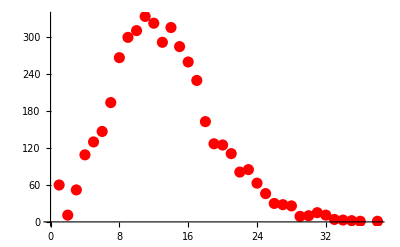

```mathematica
ListPlot[%,PlotStyle->{Hue[0],PointSize[0.02]}]
```

```mathematica
Remove[withlengths]
```

#### 3.1.6. FindSymbols

We can detect all symbols of an expression using FindSymbols. Strings and numeric quantities are removed. The function Hold in the definition holds the symbols found by Level; the function Cases evaluates the result by default, but if we use a function f that holds its arguments then the symbols are not evaluated. Note that repeated elements appear several times:

```mathematica
?FindSymbols
```

FindSymbols[expr] gives the list of all symbols in expr, without evaluating expr. FindSymbols[expr, f] gives the list of all symbols in expr, each wrapped with the function f; if the function f has a Hold attribute then none of the symbols of expr is evaluated in the process.

```mathematica
SetAttributes[FindSymbols,HoldAllComplete];
FindSymbols[expr_,f_:Identity]:=Cases[Level[Unevaluated[expr],{-1},Hold,Heads->True],x_Symbol:>f[x]];
FindSymbols[]:={};
SetNumberOfArguments[FindSymbols,{0,2}];
Protect[FindSymbols];
```

It is only used by UnknownSymbols.

```mathematica
BeginExamples[]
```

```mathematica
FindSymbols[a1+a2[b]+a3[c][{d,1+2}]+a4[e[f[g]]][h i]+f["Hello"]]
```

{Plus,a1,a2,b,a3,c,List,d,Plus,a4,e,f,g,Times,h,i,f}

```mathematica
FindSymbols[3a]
```

{Times,a}

```mathematica
FindSymbols[a]
```

{a}

```mathematica
FindSymbols[{}]
```

{List}

```mathematica
FindSymbols[]
```

{}

We can map the symbols with some head:

```mathematica
FindSymbols[3b+c]
```

{Plus,Times,b,c}

```mathematica
FindSymbols[3b+c,f]
```

{f[Plus],f[Times],f[b],f[c]}

If a symbol can be evaluated, then it will be evaluated by default, but we can use a head with some Hold attribute to avoid it:

```mathematica
a=b;
```

```mathematica
FindSymbols[3a+c]
```

{Plus,Times,b,c}

```mathematica
Trace[FindSymbols[3a+c,HoldForm]]
```

{FindSymbols[3 a+c,HoldForm],Cases[Level[Unevaluated[3 a+c],{-1},Hold,Heads→True],xAct`xCore`Private`x$_Symbol:>xAct`xCore`Private`x$],{{Heads→True,Heads→True},Level[3 a+c,{-1},Hold,Heads→True],Hold[Plus,Times,3,a,c]},{xAct`xCore`Private`x$_Symbol:>xAct`xCore`Private`x$,xAct`xCore`Private`x$_Symbol:>xAct`xCore`Private`x$},Cases[Hold[Plus,Times,3,a,c],xAct`xCore`Private`x$_Symbol:>xAct`xCore`Private`x$],{Plus,Times,a,c}}

```mathematica
FindSymbols[Hold[3a+c]]
```

{Hold,Plus,Times,b,c}

```mathematica
Trace[FindSymbols[FindSymbols[a[b]+c],Hold]]
```

{FindSymbols[FindSymbols[a[b]+c],Hold],Cases[Level[Unevaluated[FindSymbols[a[b]+c]],{-1},Hold,Heads→True],xAct`xCore`Private`x$_Symbol:>Hold[xAct`xCore`Private`x$]],{{Heads→True,Heads→True},Level[FindSymbols[a[b]+c],{-1},Hold,Heads→True],Hold[FindSymbols,Plus,a,b,c]},{xAct`xCore`Private`x$_Symbol:>Hold[xAct`xCore`Private`x$],xAct`xCore`Private`x$_Symbol:>Hold[xAct`xCore`Private`x$]},Cases[Hold[FindSymbols,Plus,a,b,c],xAct`xCore`Private`x$_Symbol:>Hold[xAct`xCore`Private`x$]],{Hold[FindSymbols],Hold[Plus],Hold[a],Hold[b],Hold[c]}}

```mathematica
Trace[FindSymbols[Sequence[a+b],HoldForm]]
```

{FindSymbols[Sequence[a+b],HoldForm],Cases[Level[Unevaluated[Sequence[a+b]],{-1},Hold,Heads→True],xAct`xCore`Private`x$_Symbol:>xAct`xCore`Private`x$],{{Heads→True,Heads→True},Level[Sequence[a+b],{-1},Hold,Heads→True],Hold[Sequence,Plus,a,b]},{xAct`xCore`Private`x$_Symbol:>xAct`xCore`Private`x$,xAct`xCore`Private`x$_Symbol:>xAct`xCore`Private`x$},Cases[Hold[Sequence,Plus,a,b],xAct`xCore`Private`x$_Symbol:>xAct`xCore`Private`x$],{Sequence,Plus,a,b}}

Note that Evaluate does not really evaluate the symbol a in the next two examples. FindSymbols allows no evaluation at all due to its HoldAllComplete attribute

```mathematica
Trace[FindSymbols[Evaluate[a+b]]]
```

{FindSymbols[Evaluate[a+b]],Cases[Level[Unevaluated[Evaluate[a+b]],{-1},Hold,Heads→True],xAct`xCore`Private`x$_Symbol:>Identity[xAct`xCore`Private`x$]],{{Heads→True,Heads→True},Level[Evaluate[a+b],{-1},Hold,Heads→True],Hold[Evaluate,Plus,a,b]},{xAct`xCore`Private`x$_Symbol:>Identity[xAct`xCore`Private`x$],xAct`xCore`Private`x$_Symbol:>Identity[xAct`xCore`Private`x$]},Cases[Hold[Evaluate,Plus,a,b],xAct`xCore`Private`x$_Symbol:>Identity[xAct`xCore`Private`x$]],{Identity[Evaluate],Identity[Plus],Identity[a],Identity[b]},{Identity[Evaluate],Evaluate},{Identity[Plus],Plus},{{a,b},Identity[b],b},{Identity[b],b},{Evaluate,Plus,b,b}}

```mathematica
Trace[FindSymbols[Evaluate[a+b],HoldForm]]
```

{FindSymbols[Evaluate[a+b],HoldForm],Cases[Level[Unevaluated[Evaluate[a+b]],{-1},Hold,Heads→True],xAct`xCore`Private`x$_Symbol:>xAct`xCore`Private`x$],{{Heads→True,Heads→True},Level[Evaluate[a+b],{-1},Hold,Heads→True],Hold[Evaluate,Plus,a,b]},{xAct`xCore`Private`x$_Symbol:>xAct`xCore`Private`x$,xAct`xCore`Private`x$_Symbol:>xAct`xCore`Private`x$},Cases[Hold[Evaluate,Plus,a,b],xAct`xCore`Private`x$_Symbol:>xAct`xCore`Private`x$],{Evaluate,Plus,a,b}}

Study these additional cases:

```mathematica
FindSymbols[Function[{a},a^2],HoldForm]
```

{Function,List,a,Power,a}

```mathematica
FindSymbols[x^2]
```

{Power,x}

```mathematica
FindSymbols[#^2]
```

{Power,Slot}

```mathematica
Remove[a,b,c,d,e,f,g,h,i,a1,a2,a3,a4,x]
```

```mathematica
EndExamples[]
```

### 3.2. ValidateSymbol

Detect whether a symbol (or character) is a capital in the System` context:

```mathematica
SystemCapitalQ[symbol_]:=And[MemberQ[$LengthOneNames,ToString[symbol]],Context[symbol]==="System`"];
```

With this function we check that a symbol is valid and that it is not already in use by xCore, xPerm, xTensor, ExpressionManipulation or Mathematica. The checks are performed in a slightly different order from that given in the usage message. As we said, this should be generalized to include other packages like xCoba.

```mathematica
?ValidateSymbol
```

ValidateSymbol[symbol] throws an error if symbol: 1) has a value or numeric character, or is not atomic, 2) its name is locked, protected or readprotected, or 3) it is already used by Mathematica or any of the xAct packages already loaded. Otherwise it gives Null. (Read)Protection is not checked for the capitals C, D, K, N, O, used by Mathematica. Symbols E and I have numeric value.

We have separated invalid from protected messages due to the following reason: we can have indices which are protected symbols but not invalid symbols. The "locked" error has been moved to the first group because a locked symbol can never be used, even if it is one-character long.

```mathematica
ValidateSymbol::invalid="Symbol `1` is invalid because it `2`.";
ValidateSymbol::protected="Symbol `1` is `2`.";
ValidateSymbol::used="Symbol `1` is already used `2`.";
```

```mathematica
MemberQ[$SystemNames,"C"]
```

True

```mathematica
SetAttributes[ValidateSymbol,HoldFirst]
ValidateSymbol[symbol_]:=With[{name=ToString[Unevaluated[symbol]]},
Which[

(* Errors: generic problems *)
NumericQ[symbol],
Throw@Message[ValidateSymbol::invalid,name,"has numeric value"],
ValueQ[symbol],
Throw@Message[ValidateSymbol::invalid,name,"has an ownvalue"],
!AtomQ[symbol],
Throw@Message[ValidateSymbol::invalid,name,"is not atomic"],
LockedQ[Symbol[name]],
Throw@Message[ValidateSymbol::protected,name,"is Locked"],

(* Errors: xAct problems *)
MemberQ[$EMNames,name],
Throw@Message[ValidateSymbol::used,name,"by ExpressionManipulation"],
MemberQ[$xCoreNames,name],
Throw@Message[ValidateSymbol::used,name,"by xCore"],
MemberQ[$xPermNames,name],
Throw@Message[ValidateSymbol::used,name,"by xPerm"],
MemberQ[$xTableauNames,name],
Throw@Message[ValidateSymbol::used,name,"by xTableau"],
MemberQ[$xTensorNames,name],
Throw@Message[ValidateSymbol::used,name,"by xTensor"],
MemberQ[$xCobaNames,name],
Throw@Message[ValidateSymbol::used,name,"by xCoba"],
MemberQ[$InvarNames,name],
Throw@Message[ValidateSymbol::used,name,"by Invar"],
MemberQ[$HarmonicsNames,name],
Throw@Message[ValidateSymbol::used,name,"by Harmonics"],
MemberQ[$xPertNames,name],
Throw@Message[ValidateSymbol::used,name,"by xPert"],
MemberQ[$SpinorsNames,name],
Throw@Message[ValidateSymbol::used,name,"by Spinors"],

SystemCapitalQ[symbol],
Return[],

(* Errors: Mathematica problems *)
ProtectedQ[Symbol[name]],
Throw@Message[ValidateSymbol::protected,name,"Protected"],
ReadProtectedQ[Symbol[name]],
Throw@Message[ValidateSymbol::protected,name,"ReadProtected"],
MemberQ[$SystemNames,name]&&Context[name]=="System`",
Throw@Message[ValidateSymbol::used,name,"by Mathematica"]

]
];
SetNumberOfArguments[ValidateSymbol,1];
Protect[ValidateSymbol];
```

Examples:

```mathematica
BeginExamples[]
```

Checks of the number of arguments:

```mathematica
Catch@ValidateSymbol[]
```

ValidateSymbol::argx: ValidateSymbol called with 0 arguments; 1 argument is expected.

```mathematica
Catch@ValidateSymbol[A,E]
```

ValidateSymbol::argx: ValidateSymbol called with 2 arguments; 1 argument is expected.

Checks of first group of problems:

```mathematica
Catch@ValidateSymbol[E]
```

ValidateSymbol::invalid: Symbol "E" is invalid because it "has numeric value".

```mathematica
Catch@ValidateSymbol[I]
```

ValidateSymbol::invalid: Symbol "I" is invalid because it "has numeric value".

```mathematica
A=B;
```

```mathematica
Catch@ValidateSymbol[A]
```

ValidateSymbol::invalid: Symbol "A" is invalid because it "has an ownvalue".

```mathematica
A=.
```

```mathematica
Catch@ValidateSymbol[Space]
```

ValidateSymbol::invalid: Symbol "Space" is invalid because it "has an ownvalue".

```mathematica
Catch@ValidateSymbol[{A,E}]
```

ValidateSymbol::invalid: Symbol "{A, E}" is invalid because it "is not atomic".

```mathematica
Catch@ValidateSymbol[A+B]
```

ValidateSymbol::invalid: Symbol "A + B" is invalid because it "is not atomic".

Checks of second group of problems:

```mathematica
Catch@ValidateSymbol[True]
```

ValidateSymbol::protected: Symbol "True" is "is Locked".

```mathematica
Catch@ValidateSymbol[Hold]
```

ValidateSymbol::protected: Symbol "Hold" is "Protected".

```mathematica
Catch@ValidateSymbol[Install]
```

ValidateSymbol::protected: Symbol "Install" is "ReadProtected".

Checks of third group of problems:

```mathematica
Catch@ValidateSymbol[eP]
```

```mathematica
Catch@ValidateSymbol[xUpSet]
```

ValidateSymbol::used: Symbol "xUpSet" is already used "by xCore".

```mathematica
Catch@ValidateSymbol[Box]
```

ValidateSymbol::protected: Symbol "Box" is "Protected".

Capitals C,D,K,N,O are used by Mathematica but do not throw an error:

```mathematica
ValidateSymbol[C]
```

Other symbols are valid:

```mathematica
ValidateSymbol[hello]
```

Again, don't follow the Trace of ValidateSymbol because it works with huge lists of names...

```mathematica
Remove[A,B,hello]
```

```mathematica
EndExamples[]
```

There are new symbols in Global`:{eP}

### 3.3. Precedence of symbols

Nothing here goes into the package.

We can compute the precedence of all SystemNames:

```mathematica
Length[$SystemNames]
```

4562

```mathematica
precs=Precedence/@Symbol/@$SystemNames;
```

Most of them have precedence 680 in Mathematica 4 or 670 in Mathematica 5:

```mathematica
precMost=Switch[System`$VersionNumber,
4.,680.,
5.,670.,
5.1,670.,
5.2,670.
]
```

Switch[9.,
4.,680.,
5.,670.,
5.1,670.,
5.2,670.]

Actually only these do not have it:

```mathematica
nonMostprecs=Sort[DeleteCases[Transpose[{precs,$SystemNames}],{precMost,_}]];
```

```mathematica
Transpose[Join[{Range@Length@nonMostprecs},Transpose[nonMostprecs]]]//TableForm
```

1 | 0. | OverBar
2 | 0. | OverDot
3 | 0. | OverHat
4 | 0. | OverTilde
5 | 0. | OverVector
6 | 0. | SubMinus
7 | 0. | SubPlus
8 | 0. | SubStar
9 | 0. | SuperDagger
10 | 0. | SuperMinus
11 | 0. | SuperPlus
12 | 0. | SuperStar
13 | 0. | UnderBar
14 | 10. | CompoundExpression
15 | 20. | ColonForm
16 | 30. | Put
17 | 30. | PutAppend
18 | 40. | Set
19 | 40. | SetDelayed
20 | 40. | UpSet
21 | 40. | UpSetDelayed
22 | 50. | Because
23 | 50. | Therefore
24 | 60. | VerticalSeparator
25 | 70. | Postfix
26 | 80. | Colon
27 | 90. | Function
28 | 100. | AddTo
29 | 100. | DivideBy
30 | 100. | SubtractFrom
31 | 100. | TimesBy
32 | 110. | ReplaceAll
33 | 110. | ReplaceRepeated
34 | 120. | Rule
35 | 120. | RuleDelayed
36 | 130. | Condition
37 | 135. | StringExpression
38 | 140. | Optional
39 | 150. | Pattern
40 | 160. | Alternatives
41 | 170. | Repeated
42 | 170. | RepeatedNull
43 | 180. | SuchThat
44 | 190. | DoubleLeftTee
45 | 190. | DoubleRightTee
46 | 190. | DownTee
47 | 190. | LeftTee
48 | 190. | Perpendicular
49 | 190. | RightTee
50 | 190. | UpTee
51 | 195. | Conditioned
52 | 200. | Implies
53 | 205. | Equivalent
54 | 215. | And
55 | 215. | Nand
56 | 215. | Nor
57 | 215. | Or
58 | 215. | Xnor
59 | 215. | Xor
60 | 230. | Not
61 | 240. | Exists
62 | 240. | ForAll
63 | 240. | NotExists
64 | 240. | RoundImplies
65 | 250. | Distributed
66 | 250. | Element
67 | 250. | NotElement
68 | 250. | NotReverseElement
69 | 250. | NotSquareSubset
70 | 250. | NotSquareSubsetEqual
71 | 250. | NotSquareSuperset
72 | 250. | NotSquareSupersetEqual
73 | 250. | NotSubset
74 | 250. | NotSubsetEqual
75 | 250. | NotSuperset
76 | 250. | NotSupersetEqual
77 | 250. | ReverseElement
78 | 250. | SquareSubset
79 | 250. | SquareSubsetEqual
80 | 250. | SquareSuperset
81 | 250. | SquareSupersetEqual
82 | 250. | Subset
83 | 250. | SubsetEqual
84 | 250. | Superset
85 | 250. | SupersetEqual
86 | 270. | DoubleLeftArrow
87 | 270. | DoubleLeftRightArrow
88 | 270. | DoubleRightArrow
89 | 270. | DownLeftRightVector
90 | 270. | DownLeftTeeVector
91 | 270. | DownLeftVector
92 | 270. | DownLeftVectorBar
93 | 270. | DownRightTeeVector
94 | 270. | DownRightVector
95 | 270. | DownRightVectorBar
96 | 270. | LeftArrow
97 | 270. | LeftArrowBar
98 | 270. | LeftArrowRightArrow
99 | 270. | LeftRightArrow
100 | 270. | LeftRightVector
101 | 270. | LeftTeeArrow
102 | 270. | LeftTeeVector
103 | 270. | LeftVector
104 | 270. | LeftVectorBar
105 | 270. | LowerLeftArrow
106 | 270. | LowerRightArrow
107 | 270. | RightArrow
108 | 270. | RightArrowBar
109 | 270. | RightArrowLeftArrow
110 | 270. | RightTeeArrow
111 | 270. | RightTeeVector
112 | 270. | RightVector
113 | 270. | RightVectorBar
114 | 270. | ShortLeftArrow
115 | 270. | ShortRightArrow
116 | 270. | UpperLeftArrow
117 | 270. | UpperRightArrow
118 | 280. | DoubleVerticalBar
119 | 280. | NotDoubleVerticalBar
120 | 280. | NotVerticalBar
121 | 280. | VerticalBar
122 | 290. | Congruent
123 | 290. | CupCap
124 | 290. | DotEqual
125 | 290. | Equal
126 | 290. | EqualTilde
127 | 290. | Equilibrium
128 | 290. | Greater
129 | 290. | GreaterEqual
130 | 290. | GreaterEqualLess
131 | 290. | GreaterFullEqual
132 | 290. | GreaterGreater
133 | 290. | GreaterLess
134 | 290. | GreaterTilde
135 | 290. | HumpDownHump
136 | 290. | HumpEqual
137 | 290. | LeftTriangle
138 | 290. | LeftTriangleBar
139 | 290. | LeftTriangleEqual
140 | 290. | Less
141 | 290. | LessEqual
142 | 290. | LessEqualGreater
143 | 290. | LessFullEqual
144 | 290. | LessGreater
145 | 290. | LessLess
146 | 290. | LessTilde
147 | 290. | NestedGreaterGreater
148 | 290. | NestedLessLess
149 | 290. | NotCongruent
150 | 290. | NotCupCap
151 | 290. | NotEqualTilde
152 | 290. | NotGreater
153 | 290. | NotGreaterEqual
154 | 290. | NotGreaterFullEqual
155 | 290. | NotGreaterGreater
156 | 290. | NotGreaterLess
157 | 290. | NotGreaterSlantEqual
158 | 290. | NotGreaterTilde
159 | 290. | NotHumpDownHump
160 | 290. | NotHumpEqual
161 | 290. | NotLeftTriangle
162 | 290. | NotLeftTriangleBar
163 | 290. | NotLeftTriangleEqual
164 | 290. | NotLess
165 | 290. | NotLessEqual
166 | 290. | NotLessFullEqual
167 | 290. | NotLessGreater
168 | 290. | NotLessLess
169 | 290. | NotLessSlantEqual
170 | 290. | NotLessTilde
171 | 290. | NotNestedGreaterGreater
172 | 290. | NotNestedLessLess
173 | 290. | NotPrecedes
174 | 290. | NotPrecedesEqual
175 | 290. | NotPrecedesSlantEqual
176 | 290. | NotPrecedesTilde
177 | 290. | NotRightTriangle
178 | 290. | NotRightTriangleBar
179 | 290. | NotRightTriangleEqual
180 | 290. | NotSucceeds
181 | 290. | NotSucceedsEqual
182 | 290. | NotSucceedsSlantEqual
183 | 290. | NotSucceedsTilde
184 | 290. | NotTilde
185 | 290. | NotTildeEqual
186 | 290. | NotTildeFullEqual
187 | 290. | NotTildeTilde
188 | 290. | Precedes
189 | 290. | PrecedesEqual
190 | 290. | PrecedesSlantEqual
191 | 290. | PrecedesTilde
192 | 290. | Proportion
193 | 290. | Proportional
194 | 290. | ReverseEquilibrium
195 | 290. | RightTriangle
196 | 290. | RightTriangleBar
197 | 290. | RightTriangleEqual
198 | 290. | SameQ
199 | 290. | Succeeds
200 | 290. | SucceedsEqual
201 | 290. | SucceedsSlantEqual
202 | 290. | SucceedsTilde
203 | 290. | Tilde
204 | 290. | TildeEqual
205 | 290. | TildeFullEqual
206 | 290. | TildeTilde
207 | 290. | Unequal
208 | 290. | UnsameQ
209 | 295. | DirectedEdge
210 | 295. | UndirectedEdge
211 | 300. | IntervalIntersection
212 | 300. | IntervalUnion
213 | 300. | SquareUnion
214 | 300. | Union
215 | 300. | UnionPlus
216 | 305. | Intersection
217 | 305. | Span
218 | 305. | SquareIntersection
219 | 310. | Complex
220 | 310. | MinusPlus
221 | 310. | Plus
222 | 310. | PlusMinus
223 | 310. | Subtract
224 | 320. | Sum
225 | 325. | ExpectationE
226 | 325. | Integrate
227 | 325. | ProbabilityPr
228 | 330. | CircleMinus
229 | 330. | CirclePlus
230 | 340. | Cup
231 | 350. | Cap
232 | 360. | Coproduct
233 | 370. | VerticalTilde
234 | 380. | ContinuedFractionK
235 | 380. | Product
236 | 390. | Star
237 | 395. | Mod
238 | 400. | Times
239 | 410. | CenterDot
240 | 420. | CircleTimes
241 | 430. | Vee
242 | 440. | Wedge
243 | 450. | Diamond
244 | 460. | Backslash
245 | 470. | Divide
246 | 480. | Minus
247 | 480. | Piecewise
248 | 490. | Dot
249 | 495. | TensorProduct
250 | 500. | Cross
251 | 500. | TensorWedge
252 | 510. | NonCommutativeMultiply
253 | 520. | CircleDot
254 | 520. | PermutationProduct
255 | 530. | SmallCircle
256 | 540. | Square
257 | 550. | CapitalDifferentialD
258 | 550. | Curl
259 | 550. | D
260 | 550. | Del
261 | 550. | DifferenceDelta
262 | 550. | DifferentialD
263 | 550. | DiscreteRatio
264 | 550. | DiscreteShift
265 | 550. | Divergence
266 | 550. | Dt
267 | 550. | Gradient
268 | 550. | Laplacian
269 | 580. | DoubleDownArrow
270 | 580. | DoubleLongLeftArrow
271 | 580. | DoubleLongLeftRightArrow
272 | 580. | DoubleLongRightArrow
273 | 580. | DoubleUpArrow
274 | 580. | DoubleUpDownArrow
275 | 580. | DownArrow
276 | 580. | DownArrowBar
277 | 580. | DownArrowUpArrow
278 | 580. | DownTeeArrow
279 | 580. | LeftDownTeeVector
280 | 580. | LeftDownVector
281 | 580. | LeftDownVectorBar
282 | 580. | LeftUpDownVector
283 | 580. | LeftUpTeeVector
284 | 580. | LeftUpVector
285 | 580. | LeftUpVectorBar
286 | 580. | LongLeftArrow
287 | 580. | LongLeftRightArrow
288 | 580. | LongRightArrow
289 | 580. | ReverseUpEquilibrium
290 | 580. | RightDownTeeVector
291 | 580. | RightDownVector
292 | 580. | RightDownVectorBar
293 | 580. | RightUpDownVector
294 | 580. | RightUpTeeVector
295 | 580. | RightUpVector
296 | 580. | RightUpVectorBar
297 | 580. | ShortDownArrow
298 | 580. | ShortUpArrow
299 | 580. | UpArrow
300 | 580. | UpArrowBar
301 | 580. | UpArrowDownArrow
302 | 580. | UpDownArrow
303 | 580. | UpEquilibrium
304 | 580. | UpTeeArrow
305 | 590. | Power
306 | 590. | SuperscriptBox
307 | 600. | StringJoin
308 | 610. | Factorial
309 | 610. | Factorial2
310 | 620. | Apply
311 | 620. | Map
312 | 620. | MapAll
313 | 630. | Infix
314 | 640. | InvisibleApplication
315 | 640. | Prefix
316 | 660. | Decrement
317 | 660. | Increment
318 | 660. | PreDecrement
319 | 660. | PreIncrement
320 | 670. | a
321 | 670. | b
322 | 670. | c
323 | 670. | d
324 | 670. | e
325 | 670. | f
326 | 670. | g
327 | 670. | h
328 | 670. | i
329 | 670. | j
330 | 670. | k
331 | 670. | l
332 | 670. | m
333 | 670. | n
334 | 670. | o
335 | 670. | p
336 | 670. | q
337 | 670. | r
338 | 670. | s
339 | 670. | t
340 | 670. | u
341 | 670. | v
342 | 670. | w
343 | 670. | x
344 | 670. | y
345 | 670. | z
346 | 670. | A
347 | 670. | B
348 | 670. | C
349 | 670. | D
350 | 670. | E
351 | 670. | F
352 | 670. | G
353 | 670. | H
354 | 670. | I
355 | 670. | J
356 | 670. | K
357 | 670. | L
358 | 670. | M
359 | 670. | N
360 | 670. | O
361 | 670. | P
362 | 670. | Q
363 | 670. | R
364 | 670. | S
365 | 670. | T
366 | 670. | U
367 | 670. | V
368 | 670. | W
369 | 670. | X
370 | 670. | Y
371 | 670. | Z
372 | 670. | AbelianGroup
373 | 670. | Abort
374 | 670. | AbortKernels
375 | 670. | AbortProtect
376 | 670. | Above
377 | 670. | Abs
378 | 670. | Absolute
379 | 670. | AbsoluteCorrelation
380 | 670. | AbsoluteCorrelationFunction
381 | 670. | AbsoluteCurrentValue
382 | 670. | AbsoluteDashing
383 | 670. | AbsoluteFileName
384 | 670. | AbsoluteOptions
385 | 670. | AbsolutePointSize
386 | 670. | AbsoluteThickness
387 | 670. | AbsoluteTime
388 | 670. | AbsoluteTiming
389 | 670. | AccountingForm
390 | 670. | Accumulate
391 | 670. | Accuracy
392 | 670. | AccuracyGoal
393 | 670. | ActionDelay
394 | 670. | ActionMenu
395 | 670. | ActionMenuBox
396 | 670. | ActionMenuBoxOptions
397 | 670. | Active
398 | 670. | ActiveItem
399 | 670. | ActiveStyle
400 | 670. | AcyclicGraphQ
401 | 670. | AddOnHelpPath
402 | 670. | AdjacencyGraph
403 | 670. | AdjacencyList
404 | 670. | AdjacencyMatrix
405 | 670. | AdjustmentBox
406 | 670. | AdjustmentBoxOptions
407 | 670. | AdjustTimeSeriesForecast
408 | 670. | AffineTransform
409 | 670. | After
410 | 670. | AiryAi
411 | 670. | AiryAiPrime
412 | 670. | AiryAiZero
413 | 670. | AiryBi
414 | 670. | AiryBiPrime
415 | 670. | AiryBiZero
416 | 670. | AlgebraicIntegerQ
417 | 670. | AlgebraicNumber
418 | 670. | AlgebraicNumberDenominator
419 | 670. | AlgebraicNumberNorm
420 | 670. | AlgebraicNumberPolynomial
421 | 670. | AlgebraicNumberTrace
422 | 670. | AlgebraicRules
423 | 670. | AlgebraicRulesData
424 | 670. | Algebraics
425 | 670. | AlgebraicUnitQ
426 | 670. | Alignment
427 | 670. | AlignmentMarker
428 | 670. | AlignmentPoint
429 | 670. | All
430 | 670. | AllowedDimensions
431 | 670. | AllowGroupClose
432 | 670. | AllowInlineCells
433 | 670. | AllowKernelInitialization
434 | 670. | AllowReverseGroupClose
435 | 670. | AllowScriptLevelChange
436 | 670. | AlphaChannel
437 | 670. | AlternatingGroup
438 | 670. | AlternativeHypothesis
439 | 670. | AmbientLight
440 | 670. | Analytic
441 | 670. | AnchoredSearch
442 | 670. | AndersonDarlingTest
443 | 670. | AngerJ
444 | 670. | AngleBracket
445 | 670. | AngularGauge
446 | 670. | Animate
447 | 670. | AnimationCycleOffset
448 | 670. | AnimationCycleRepetitions
449 | 670. | AnimationDirection
450 | 670. | AnimationDisplayTime
451 | 670. | AnimationRate
452 | 670. | AnimationRepetitions
453 | 670. | AnimationRunning
454 | 670. | Animator
455 | 670. | AnimatorBox
456 | 670. | AnimatorBoxOptions
457 | 670. | AnimatorElements
458 | 670. | Annotation
459 | 670. | Annuity
460 | 670. | AnnuityDue
461 | 670. | Antialiasing
462 | 670. | Antisymmetric
463 | 670. | Apart
464 | 670. | ApartSquareFree
465 | 670. | Appearance
466 | 670. | AppearanceElements
467 | 670. | AppellF1
468 | 670. | Append
469 | 670. | AppendTo
470 | 670. | ArcCos
471 | 670. | ArcCosh
472 | 670. | ArcCot
473 | 670. | ArcCoth
474 | 670. | ArcCsc
475 | 670. | ArcCsch
476 | 670. | ArcSec
477 | 670. | ArcSech
478 | 670. | ArcSin
479 | 670. | ArcSinDistribution
480 | 670. | ArcSinh
481 | 670. | ArcTan
482 | 670. | ArcTanh
483 | 670. | Arg
484 | 670. | ArgMax
485 | 670. | ArgMin
486 | 670. | ArgumentCountQ
487 | 670. | ARIMAProcess
488 | 670. | ArithmeticGeometricMean
489 | 670. | ARMAProcess
490 | 670. | ARProcess
491 | 670. | Array
492 | 670. | ArrayComponents
493 | 670. | ArrayDepth
494 | 670. | ArrayFlatten
495 | 670. | ArrayPad
496 | 670. | ArrayPlot
497 | 670. | ArrayQ
498 | 670. | ArrayReshape
499 | 670. | ArrayRules
500 | 670. | Arrays
501 | 670. | Arrow
502 | 670. | Arrow3DBox
503 | 670. | ArrowBox
504 | 670. | Arrowheads
505 | 670. | AspectRatio
506 | 670. | AspectRatioFixed
507 | 670. | Assert
508 | 670. | Assuming
509 | 670. | Assumptions
510 | 670. | AstronomicalData
511 | 670. | Asynchronous
512 | 670. | AsynchronousTaskObject
513 | 670. | AsynchronousTasks
514 | 670. | AtomQ
515 | 670. | Attributes
516 | 670. | AugmentedSymmetricPolynomial
517 | 670. | AutoAction
518 | 670. | AutoDelete
519 | 670. | AutoEvaluateEvents
520 | 670. | AutoGeneratedPackage
521 | 670. | AutoIndent
522 | 670. | AutoIndentSpacings
523 | 670. | AutoItalicWords
524 | 670. | AutoloadPath
525 | 670. | AutoMatch
526 | 670. | Automatic
527 | 670. | AutomaticImageSize
528 | 670. | AutoMultiplicationSymbol
529 | 670. | AutoNumberFormatting
530 | 670. | AutoOpenNotebooks
531 | 670. | AutoOpenPalettes
532 | 670. | AutorunSequencing
533 | 670. | AutoScaling
534 | 670. | AutoScroll
535 | 670. | AutoSpacing
536 | 670. | AutoStyleOptions
537 | 670. | AutoStyleWords
538 | 670. | Axes
539 | 670. | AxesEdge
540 | 670. | AxesLabel
541 | 670. | AxesOrigin
542 | 670. | AxesStyle
543 | 670. | Axis
544 | 670. | BabyMonsterGroupB
545 | 670. | Back
546 | 670. | Background
547 | 670. | BackgroundTasksSettings
548 | 670. | Backsubstitution
549 | 670. | Backward
550 | 670. | Band
551 | 670. | BandpassFilter
552 | 670. | BandstopFilter
553 | 670. | BarabasiAlbertGraphDistribution
554 | 670. | BarChart
555 | 670. | BarChart3D
556 | 670. | BarLegend
557 | 670. | BarlowProschanImportance
558 | 670. | BarnesG
559 | 670. | BarOrigin
560 | 670. | BarSpacing
561 | 670. | BartlettHannWindow
562 | 670. | BartlettWindow
563 | 670. | BaseForm
564 | 670. | Baseline
565 | 670. | BaselinePosition
566 | 670. | BaseStyle
567 | 670. | BatesDistribution
568 | 670. | BattleLemarieWavelet
569 | 670. | BeckmannDistribution
570 | 670. | Beep
571 | 670. | Before
572 | 670. | Begin
573 | 670. | BeginDialogPacket
574 | 670. | BeginFrontEndInteractionPacket
575 | 670. | BeginPackage
576 | 670. | BellB
577 | 670. | BellY
578 | 670. | Below
579 | 670. | BenfordDistribution
580 | 670. | BeniniDistribution
581 | 670. | BenktanderGibratDistribution
582 | 670. | BenktanderWeibullDistribution
583 | 670. | BernoulliB
584 | 670. | BernoulliDistribution
585 | 670. | BernoulliGraphDistribution
586 | 670. | BernoulliProcess
587 | 670. | BernsteinBasis
588 | 670. | BesselFilterModel
589 | 670. | BesselI
590 | 670. | BesselJ
591 | 670. | BesselJZero
592 | 670. | BesselK
593 | 670. | BesselY
594 | 670. | BesselYZero
595 | 670. | Beta
596 | 670. | BetaBinomialDistribution
597 | 670. | BetaDistribution
598 | 670. | BetaNegativeBinomialDistribution
599 | 670. | BetaPrimeDistribution
600 | 670. | BetaRegularized
601 | 670. | BetweennessCentrality
602 | 670. | BezierCurve
603 | 670. | BezierCurve3DBox
604 | 670. | BezierCurve3DBoxOptions
605 | 670. | BezierCurveBox
606 | 670. | BezierCurveBoxOptions
607 | 670. | BezierFunction
608 | 670. | BilateralFilter
609 | 670. | Binarize
610 | 670. | BinaryFormat
611 | 670. | BinaryImageQ
612 | 670. | BinaryRead
613 | 670. | BinaryReadList
614 | 670. | BinaryWrite
615 | 670. | BinCounts
616 | 670. | BinLists
617 | 670. | Binomial
618 | 670. | BinomialDistribution
619 | 670. | BinomialProcess
620 | 670. | BinormalDistribution
621 | 670. | BiorthogonalSplineWavelet
622 | 670. | BipartiteGraphQ
623 | 670. | BirnbaumImportance
624 | 670. | BirnbaumSaundersDistribution
625 | 670. | BitAnd
626 | 670. | BitClear
627 | 670. | BitGet
628 | 670. | BitLength
629 | 670. | BitNot
630 | 670. | BitOr
631 | 670. | BitSet
632 | 670. | BitShiftLeft
633 | 670. | BitShiftRight
634 | 670. | BitXor
635 | 670. | BlackmanHarrisWindow
636 | 670. | BlackmanNuttallWindow
637 | 670. | BlackmanWindow
638 | 670. | BlankForm
639 | 670. | Blend
640 | 670. | Block
641 | 670. | BlockRandom
642 | 670. | BlomqvistBeta
643 | 670. | BlomqvistBetaTest
644 | 670. | Blur
645 | 670. | BodePlot
646 | 670. | BohmanWindow
647 | 670. | Bold
648 | 670. | Bookmarks
649 | 670. | Boole
650 | 670. | BooleanConsecutiveFunction
651 | 670. | BooleanConvert
652 | 670. | BooleanCountingFunction
653 | 670. | BooleanFunction
654 | 670. | BooleanGraph
655 | 670. | BooleanMaxterms
656 | 670. | BooleanMinimize
657 | 670. | BooleanMinterms
658 | 670. | Booleans
659 | 670. | BooleanTable
660 | 670. | BooleanVariables
661 | 670. | BorderDimensions
662 | 670. | BorelTannerDistribution
663 | 670. | Bottom
664 | 670. | BottomHatTransform
665 | 670. | BoundaryStyle
666 | 670. | Bounds
667 | 670. | Box
668 | 670. | BoxBaselineShift
669 | 670. | BoxData
670 | 670. | BoxDimensions
671 | 670. | Boxed
672 | 670. | Boxes
673 | 670. | BoxForm
674 | 670. | BoxFormFormatTypes
675 | 670. | BoxFrame
676 | 670. | BoxID
677 | 670. | BoxMargins
678 | 670. | BoxMatrix
679 | 670. | BoxRatios
680 | 670. | BoxRotation
681 | 670. | BoxRotationPoint
682 | 670. | BoxStyle
683 | 670. | BoxWhiskerChart
684 | 670. | Bra
685 | 670. | BracketingBar
686 | 670. | BraKet
687 | 670. | BrayCurtisDistance
688 | 670. | BreadthFirstScan
689 | 670. | Break
690 | 670. | BrownForsytheTest
691 | 670. | BrownianBridgeProcess
692 | 670. | BrowserCategory
693 | 670. | BSplineBasis
694 | 670. | BSplineCurve
695 | 670. | BSplineCurve3DBox
696 | 670. | BSplineCurveBox
697 | 670. | BSplineCurveBoxOptions
698 | 670. | BSplineFunction
699 | 670. | BSplineSurface
700 | 670. | BSplineSurface3DBox
701 | 670. | BubbleChart
702 | 670. | BubbleChart3D
703 | 670. | BubbleScale
704 | 670. | BubbleSizes
705 | 670. | BulletGauge
706 | 670. | BusinessDayQ
707 | 670. | ButterflyGraph
708 | 670. | ButterworthFilterModel
709 | 670. | Button
710 | 670. | ButtonBar
711 | 670. | ButtonBox
712 | 670. | ButtonBoxOptions
713 | 670. | ButtonCell
714 | 670. | ButtonContents
715 | 670. | ButtonData
716 | 670. | ButtonEvaluator
717 | 670. | ButtonExpandable
718 | 670. | ButtonFrame
719 | 670. | ButtonFunction
720 | 670. | ButtonMargins
721 | 670. | ButtonMinHeight
722 | 670. | ButtonNote
723 | 670. | ButtonNotebook
724 | 670. | ButtonSource
725 | 670. | ButtonStyle
726 | 670. | ButtonStyleMenuListing
727 | 670. | Byte
728 | 670. | ByteCount
729 | 670. | ByteOrdering
730 | 670. | C
731 | 670. | CachedValue
732 | 670. | CacheGraphics
733 | 670. | CalendarData
734 | 670. | CalendarType
735 | 670. | CallPacket
736 | 670. | CanberraDistance
737 | 670. | Cancel
738 | 670. | CancelButton
739 | 670. | CandlestickChart
740 | 670. | CapForm
741 | 670. | CardinalBSplineBasis
742 | 670. | CarmichaelLambda
743 | 670. | Cases
744 | 670. | Cashflow
745 | 670. | Casoratian
746 | 670. | Catalan
747 | 670. | CatalanNumber
748 | 670. | Catch
749 | 670. | CauchyDistribution
750 | 670. | CauchyWindow
751 | 670. | CayleyGraph
752 | 670. | CDF
753 | 670. | CDFDeploy
754 | 670. | CDFInformation
755 | 670. | CDFWavelet
756 | 670. | Ceiling
757 | 670. | Cell
758 | 670. | CellAutoOverwrite
759 | 670. | CellBaseline
760 | 670. | CellBoundingBox
761 | 670. | CellBracketOptions
762 | 670. | CellChangeTimes
763 | 670. | CellContents
764 | 670. | CellContext
765 | 670. | CellDingbat
766 | 670. | CellDynamicExpression
767 | 670. | CellEditDuplicate
768 | 670. | CellElementsBoundingBox
769 | 670. | CellElementSpacings
770 | 670. | CellEpilog
771 | 670. | CellEvaluationDuplicate
772 | 670. | CellEvaluationFunction
773 | 670. | CellEventActions
774 | 670. | CellFrame
775 | 670. | CellFrameColor
776 | 670. | CellFrameLabelMargins
777 | 670. | CellFrameLabels
778 | 670. | CellFrameMargins
779 | 670. | CellGroup
780 | 670. | CellGroupData
781 | 670. | CellGrouping
782 | 670. | CellGroupingRules
783 | 670. | CellHorizontalScrolling
784 | 670. | CellID
785 | 670. | CellLabel
786 | 670. | CellLabelAutoDelete
787 | 670. | CellLabelMargins
788 | 670. | CellLabelPositioning
789 | 670. | CellMargins
790 | 670. | CellObject
791 | 670. | CellOpen
792 | 670. | CellPrint
793 | 670. | CellProlog
794 | 670. | Cells
795 | 670. | CellSize
796 | 670. | CellStyle
797 | 670. | CellTags
798 | 670. | CellularAutomaton
799 | 670. | CensoredDistribution
800 | 670. | Censoring
801 | 670. | Center
802 | 670. | CentralMoment
803 | 670. | CentralMomentGeneratingFunction
804 | 670. | CForm
805 | 670. | ChampernowneNumber
806 | 670. | ChanVeseBinarize
807 | 670. | Character
808 | 670. | CharacterEncoding
809 | 670. | CharacterEncodingsPath
810 | 670. | CharacteristicFunction
811 | 670. | CharacteristicPolynomial
812 | 670. | CharacterRange
813 | 670. | Characters
814 | 670. | ChartBaseStyle
815 | 670. | ChartElementData
816 | 670. | ChartElementDataFunction
817 | 670. | ChartElementFunction
818 | 670. | ChartElements
819 | 670. | ChartLabels
820 | 670. | ChartLayout
821 | 670. | ChartLegends
822 | 670. | ChartStyle
823 | 670. | Chebyshev1FilterModel
824 | 670. | Chebyshev2FilterModel
825 | 670. | ChebyshevDistance
826 | 670. | ChebyshevT
827 | 670. | ChebyshevU
828 | 670. | Check
829 | 670. | CheckAbort
830 | 670. | CheckAll
831 | 670. | Checkbox
832 | 670. | CheckboxBar
833 | 670. | CheckboxBox
834 | 670. | CheckboxBoxOptions
835 | 670. | ChemicalData
836 | 670. | ChessboardDistance
837 | 670. | ChiDistribution
838 | 670. | ChineseRemainder
839 | 670. | ChiSquareDistribution
840 | 670. | ChoiceButtons
841 | 670. | ChoiceDialog
842 | 670. | CholeskyDecomposition
843 | 670. | Chop
844 | 670. | Circle
845 | 670. | CircleBox
846 | 670. | CirculantGraph
847 | 670. | CityData
848 | 670. | Clear
849 | 670. | ClearAll
850 | 670. | ClearAttributes
851 | 670. | ClearSystemCache
852 | 670. | ClebschGordan
853 | 670. | ClickPane
854 | 670. | Clip
855 | 670. | ClipboardNotebook
856 | 670. | ClipFill
857 | 670. | ClippingStyle
858 | 670. | ClipPlanes
859 | 670. | ClipRange
860 | 670. | Clock
861 | 670. | ClockGauge
862 | 670. | ClockwiseContourIntegral
863 | 670. | Close
864 | 670. | Closed
865 | 670. | CloseKernels
866 | 670. | ClosenessCentrality
867 | 670. | Closing
868 | 670. | ClosingAutoSave
869 | 670. | ClosingEvent
870 | 670. | ClusteringComponents
871 | 670. | CMYKColor
872 | 670. | Coarse
873 | 670. | Coefficient
874 | 670. | CoefficientArrays
875 | 670. | CoefficientDomain
876 | 670. | CoefficientList
877 | 670. | CoefficientRules
878 | 670. | CoifletWavelet
879 | 670. | Collect
880 | 670. | ColorCombine
881 | 670. | ColorConvert
882 | 670. | ColorData
883 | 670. | ColorDataFunction
884 | 670. | ColorFunction
885 | 670. | ColorFunctionScaling
886 | 670. | Colorize
887 | 670. | ColorNegate
888 | 670. | ColorOutput
889 | 670. | ColorProfileData
890 | 670. | ColorQuantize
891 | 670. | ColorReplace
892 | 670. | ColorRules
893 | 670. | ColorSelectorSettings
894 | 670. | ColorSeparate
895 | 670. | ColorSetter
896 | 670. | ColorSetterBox
897 | 670. | ColorSetterBoxOptions
898 | 670. | ColorSlider
899 | 670. | ColorSpace
900 | 670. | Column
901 | 670. | ColumnAlignments
902 | 670. | ColumnBackgrounds
903 | 670. | ColumnForm
904 | 670. | ColumnLines
905 | 670. | ColumnsEqual
906 | 670. | ColumnSpacings
907 | 670. | ColumnWidths
908 | 670. | CommonDefaultFormatTypes
909 | 670. | Commonest
910 | 670. | CommonestFilter
911 | 670. | CommonUnits
912 | 670. | CommunityBoundaryStyle
913 | 670. | CommunityGraphPlot
914 | 670. | CommunityLabels
915 | 670. | CommunityRegionStyle
916 | 670. | CompatibleUnitQ
917 | 670. | CompilationOptions
918 | 670. | CompilationTarget
919 | 670. | Compile
920 | 670. | Compiled
921 | 670. | CompiledFunction
922 | 670. | Complement
923 | 670. | CompleteGraph
924 | 670. | CompleteGraphQ
925 | 670. | CompleteKaryTree
926 | 670. | CompletionsListPacket
927 | 670. | Complexes
928 | 670. | ComplexExpand
929 | 670. | ComplexityFunction
930 | 670. | ComponentMeasurements
931 | 670. | ComponentwiseContextMenu
932 | 670. | Compose
933 | 670. | ComposeList
934 | 670. | ComposeSeries
935 | 670. | Composition
936 | 670. | CompoundPoissonDistribution
937 | 670. | CompoundPoissonProcess
938 | 670. | CompoundRenewalProcess
939 | 670. | Compress
940 | 670. | CompressedData
941 | 670. | ConditionalExpression
942 | 670. | Cone
943 | 670. | ConeBox
944 | 670. | ConfidenceLevel
945 | 670. | ConfidenceRange
946 | 670. | ConfidenceTransform
947 | 670. | ConfigurationPath
948 | 670. | Conjugate
949 | 670. | ConjugateTranspose
950 | 670. | Conjunction
951 | 670. | Connect
952 | 670. | ConnectedComponents
953 | 670. | ConnectedGraphQ
954 | 670. | ConnesWindow
955 | 670. | ConoverTest
956 | 670. | ConsoleMessage
957 | 670. | ConsoleMessagePacket
958 | 670. | ConsolePrint
959 | 670. | Constant
960 | 670. | ConstantArray
961 | 670. | Constants
962 | 670. | ConstrainedMax
963 | 670. | ConstrainedMin
964 | 670. | ContentPadding
965 | 670. | ContentsBoundingBox
966 | 670. | ContentSelectable
967 | 670. | ContentSize
968 | 670. | Context
969 | 670. | ContextMenu
970 | 670. | Contexts
971 | 670. | ContextToFilename
972 | 670. | ContextToFileName
973 | 670. | Continuation
974 | 670. | Continue
975 | 670. | ContinuedFraction
976 | 670. | ContinuousAction
977 | 670. | ContinuousMarkovProcess
978 | 670. | ContinuousTimeModelQ
979 | 670. | ContinuousWaveletData
980 | 670. | ContinuousWaveletTransform
981 | 670. | ContourDetect
982 | 670. | ContourGraphics
983 | 670. | ContourIntegral
984 | 670. | ContourLabels
985 | 670. | ContourLines
986 | 670. | ContourPlot
987 | 670. | ContourPlot3D
988 | 670. | Contours
989 | 670. | ContourShading
990 | 670. | ContourSmoothing
991 | 670. | ContourStyle
992 | 670. | ContraharmonicMean
993 | 670. | Control
994 | 670. | ControlActive
995 | 670. | ControlAlignment
996 | 670. | ControllabilityGramian
997 | 670. | ControllabilityMatrix
998 | 670. | ControllableDecomposition
999 | 670. | ControllableModelQ
1000 | 670. | ControllerInformation
1001 | 670. | ControllerInformationData
1002 | 670. | ControllerLinking
1003 | 670. | ControllerManipulate
1004 | 670. | ControllerMethod
1005 | 670. | ControllerPath
1006 | 670. | ControllerState
1007 | 670. | ControlPlacement
1008 | 670. | ControlsRendering
1009 | 670. | ControlType
1010 | 670. | Convergents
1011 | 670. | ConversionOptions
1012 | 670. | ConversionRules
1013 | 670. | ConvertToBitmapPacket
1014 | 670. | ConvertToPostScript
1015 | 670. | ConvertToPostScriptPacket
1016 | 670. | Convolve
1017 | 670. | ConwayGroupCo1
1018 | 670. | ConwayGroupCo2
1019 | 670. | ConwayGroupCo3
1020 | 670. | CoordinateChartData
1021 | 670. | CoordinatesToolOptions
1022 | 670. | CoordinateTransform
1023 | 670. | CoordinateTransformData
1024 | 670. | CoprimeQ
1025 | 670. | CopulaDistribution
1026 | 670. | Copyable
1027 | 670. | CopyDirectory
1028 | 670. | CopyFile
1029 | 670. | CopyTag
1030 | 670. | CopyToClipboard
1031 | 670. | CornerFilter
1032 | 670. | CornerNeighbors
1033 | 670. | Correlation
1034 | 670. | CorrelationDistance
1035 | 670. | CorrelationFunction
1036 | 670. | CorrelationTest
1037 | 670. | Cos
1038 | 670. | Cosh
1039 | 670. | CoshIntegral
1040 | 670. | CosineDistance
1041 | 670. | CosineWindow
1042 | 670. | CosIntegral
1043 | 670. | Cot
1044 | 670. | Coth
1045 | 670. | Count
1046 | 670. | CounterAssignments
1047 | 670. | CounterBox
1048 | 670. | CounterBoxOptions
1049 | 670. | CounterClockwiseContourIntegral
1050 | 670. | CounterEvaluator
1051 | 670. | CounterFunction
1052 | 670. | CounterIncrements
1053 | 670. | CounterStyle
1054 | 670. | CounterStyleMenuListing
1055 | 670. | CountRoots
1056 | 670. | CountryData
1057 | 670. | Covariance
1058 | 670. | CovarianceEstimatorFunction
1059 | 670. | CovarianceFunction
1060 | 670. | CoxianDistribution
1061 | 670. | CoxIngersollRossProcess
1062 | 670. | CoxModel
1063 | 670. | CoxModelFit
1064 | 670. | CramerVonMisesTest
1065 | 670. | CreateArchive
1066 | 670. | CreateDialog
1067 | 670. | CreateDirectory
1068 | 670. | CreateDocument
1069 | 670. | CreateIntermediateDirectories
1070 | 670. | CreatePalette
1071 | 670. | CreatePalettePacket
1072 | 670. | CreateScheduledTask
1073 | 670. | CreateTemporary
1074 | 670. | CreateWindow
1075 | 670. | CriticalityFailureImportance
1076 | 670. | CriticalitySuccessImportance
1077 | 670. | CriticalSection
1078 | 670. | CrossingDetect
1079 | 670. | CrossMatrix
1080 | 670. | Csc
1081 | 670. | Csch
1082 | 670. | CubeRoot
1083 | 670. | Cubics
1084 | 670. | Cuboid
1085 | 670. | CuboidBox
1086 | 670. | Cumulant
1087 | 670. | CumulantGeneratingFunction
1088 | 670. | CurlyDoubleQuote
1089 | 670. | CurlyQuote
1090 | 670. | CurrentImage
1091 | 670. | CurrentlySpeakingPacket
1092 | 670. | CurrentValue
1093 | 670. | CurvatureFlowFilter
1094 | 670. | CurveClosed
1095 | 670. | CycleGraph
1096 | 670. | CycleIndexPolynomial
1097 | 670. | Cycles
1098 | 670. | CyclicGroup
1099 | 670. | Cyclotomic
1100 | 670. | Cylinder
1101 | 670. | CylinderBox
1102 | 670. | CylindricalDecomposition
1103 | 670. | DagumDistribution
1104 | 670. | DamerauLevenshteinDistance
1105 | 670. | DampingFactor
1106 | 670. | Darker
1107 | 670. | Dashing
1108 | 670. | DataCompression
1109 | 670. | DataDistribution
1110 | 670. | DataRange
1111 | 670. | DataReversed
1112 | 670. | Date
1113 | 670. | DateDelimiters
1114 | 670. | DateDifference
1115 | 670. | DateFunction
1116 | 670. | DateList
1117 | 670. | DateListLogPlot
1118 | 670. | DateListPlot
1119 | 670. | DatePattern
1120 | 670. | DatePlus
1121 | 670. | DateRange
1122 | 670. | DateString
1123 | 670. | DateTicksFormat
1124 | 670. | DaubechiesWavelet
1125 | 670. | DavisDistribution
1126 | 670. | DawsonF
1127 | 670. | DayCount
1128 | 670. | DayCountConvention
1129 | 670. | DayMatchQ
1130 | 670. | DayName
1131 | 670. | DayPlus
1132 | 670. | DayRange
1133 | 670. | DayRound
1134 | 670. | DeBruijnGraph
1135 | 670. | Debug
1136 | 670. | DebugTag
1137 | 670. | Decimal
1138 | 670. | DeclareKnownSymbols
1139 | 670. | DeclarePackage
1140 | 670. | Decompose
1141 | 670. | DedekindEta
1142 | 670. | Default
1143 | 670. | DefaultAxesStyle
1144 | 670. | DefaultBaseStyle
1145 | 670. | DefaultBoxStyle
1146 | 670. | DefaultButton
1147 | 670. | DefaultColor
1148 | 670. | DefaultControlPlacement
1149 | 670. | DefaultDuplicateCellStyle
1150 | 670. | DefaultDuration
1151 | 670. | DefaultElement
1152 | 670. | DefaultFaceGridsStyle
1153 | 670. | DefaultFieldHintStyle
1154 | 670. | DefaultFont
1155 | 670. | DefaultFontProperties
1156 | 670. | DefaultFormatType
1157 | 670. | DefaultFormatTypeForStyle
1158 | 670. | DefaultFrameStyle
1159 | 670. | DefaultFrameTicksStyle
1160 | 670. | DefaultGridLinesStyle
1161 | 670. | DefaultInlineFormatType
1162 | 670. | DefaultInputFormatType
1163 | 670. | DefaultLabelStyle
1164 | 670. | DefaultMenuStyle
1165 | 670. | DefaultNaturalLanguage
1166 | 670. | DefaultNewCellStyle
1167 | 670. | DefaultNewInlineCellStyle
1168 | 670. | DefaultNotebook
1169 | 670. | DefaultOptions
1170 | 670. | DefaultOutputFormatType
1171 | 670. | DefaultStyle
1172 | 670. | DefaultStyleDefinitions
1173 | 670. | DefaultTextFormatType
1174 | 670. | DefaultTextInlineFormatType
1175 | 670. | DefaultTicksStyle
1176 | 670. | DefaultTooltipStyle
1177 | 670. | DefaultValues
1178 | 670. | Defer
1179 | 670. | DefineExternal
1180 | 670. | DefineInputStreamMethod
1181 | 670. | DefineOutputStreamMethod
1182 | 670. | Definition
1183 | 670. | Degree
1184 | 670. | DegreeCentrality
1185 | 670. | DegreeGraphDistribution
1186 | 670. | DegreeLexicographic
1187 | 670. | DegreeReverseLexicographic
1188 | 670. | Deinitialization
1189 | 670. | Deletable
1190 | 670. | Delete
1191 | 670. | DeleteBorderComponents
1192 | 670. | DeleteCases
1193 | 670. | DeleteContents
1194 | 670. | DeleteDirectory
1195 | 670. | DeleteDuplicates
1196 | 670. | DeleteFile
1197 | 670. | DeleteSmallComponents
1198 | 670. | DeleteWithContents
1199 | 670. | DeletionWarning
1200 | 670. | Delimiter
1201 | 670. | DelimiterFlashTime
1202 | 670. | DelimiterMatching
1203 | 670. | Delimiters
1204 | 670. | Denominator
1205 | 670. | DensityGraphics
1206 | 670. | DensityHistogram
1207 | 670. | DensityPlot
1208 | 670. | DependentVariables
1209 | 670. | Deploy
1210 | 670. | Deployed
1211 | 670. | Depth
1212 | 670. | DepthFirstScan
1213 | 670. | Derivative
1214 | 670. | DerivativeFilter
1215 | 670. | DescriptorStateSpace
1216 | 670. | DesignMatrix
1217 | 670. | Det
1218 | 670. | DGaussianWavelet
1219 | 670. | DiacriticalPositioning
1220 | 670. | Diagonal
1221 | 670. | DiagonalMatrix
1222 | 670. | Dialog
1223 | 670. | DialogIndent
1224 | 670. | DialogInput
1225 | 670. | DialogLevel
1226 | 670. | DialogNotebook
1227 | 670. | DialogProlog
1228 | 670. | DialogReturn
1229 | 670. | DialogSymbols
1230 | 670. | DiamondMatrix
1231 | 670. | DiceDissimilarity
1232 | 670. | DictionaryLookup
1233 | 670. | DifferenceOrder
1234 | 670. | DifferenceRoot
1235 | 670. | DifferenceRootReduce
1236 | 670. | Differences
1237 | 670. | DifferentialRoot
1238 | 670. | DifferentialRootReduce
1239 | 670. | DifferentiatorFilter
1240 | 670. | DigitBlock
1241 | 670. | DigitBlockMinimum
1242 | 670. | DigitCharacter
1243 | 670. | DigitCount
1244 | 670. | DigitQ
1245 | 670. | DihedralGroup
1246 | 670. | Dilation
1247 | 670. | Dimensions
1248 | 670. | DiracComb
1249 | 670. | DiracDelta
1250 | 670. | DirectedEdges
1251 | 670. | DirectedGraph
1252 | 670. | DirectedGraphQ
1253 | 670. | DirectedInfinity
1254 | 670. | Direction
1255 | 670. | Directive
1256 | 670. | Directory
1257 | 670. | DirectoryName
1258 | 670. | DirectoryQ
1259 | 670. | DirectoryStack
1260 | 670. | DirichletCharacter
1261 | 670. | DirichletConvolve
1262 | 670. | DirichletDistribution
1263 | 670. | DirichletL
1264 | 670. | DirichletTransform
1265 | 670. | DirichletWindow
1266 | 670. | DisableConsolePrintPacket
1267 | 670. | DiscreteChirpZTransform
1268 | 670. | DiscreteConvolve
1269 | 670. | DiscreteDelta
1270 | 670. | DiscreteHadamardTransform
1271 | 670. | DiscreteIndicator
1272 | 670. | DiscreteLQEstimatorGains
1273 | 670. | DiscreteLQRegulatorGains
1274 | 670. | DiscreteLyapunovSolve
1275 | 670. | DiscreteMarkovProcess
1276 | 670. | DiscretePlot
1277 | 670. | DiscretePlot3D
1278 | 670. | DiscreteRiccatiSolve
1279 | 670. | DiscreteTimeModelQ
1280 | 670. | DiscreteUniformDistribution
1281 | 670. | DiscreteVariables
1282 | 670. | DiscreteWaveletData
1283 | 670. | DiscreteWaveletPacketTransform
1284 | 670. | DiscreteWaveletTransform
1285 | 670. | Discriminant
1286 | 670. | Disjunction
1287 | 670. | Disk
1288 | 670. | DiskBox
1289 | 670. | DiskMatrix
1290 | 670. | Dispatch
1291 | 670. | DispersionEstimatorFunction
1292 | 670. | Display
1293 | 670. | DisplayAllSteps
1294 | 670. | DisplayEndPacket
1295 | 670. | DisplayFlushImagePacket
1296 | 670. | DisplayForm
1297 | 670. | DisplayFunction
1298 | 670. | DisplayPacket
1299 | 670. | DisplayRules
1300 | 670. | DisplaySetSizePacket
1301 | 670. | DisplayString
1302 | 670. | DisplayTemporary
1303 | 670. | DisplayWith
1304 | 670. | DisplayWithRef
1305 | 670. | DisplayWithVariable
1306 | 670. | DistanceFunction
1307 | 670. | DistanceTransform
1308 | 670. | Distribute
1309 | 670. | DistributedContexts
1310 | 670. | DistributeDefinitions
1311 | 670. | DistributionChart
1312 | 670. | DistributionDomain
1313 | 670. | DistributionFitTest
1314 | 670. | DistributionParameterAssumptions
1315 | 670. | DistributionParameterQ
1316 | 670. | Dithering
1317 | 670. | Div
1318 | 670. | Dividers
1319 | 670. | Divisible
1320 | 670. | Divisors
1321 | 670. | DivisorSigma
1322 | 670. | DivisorSum
1323 | 670. | DMSList
1324 | 670. | DMSString
1325 | 670. | Do
1326 | 670. | DockedCells
1327 | 670. | DocumentNotebook
1328 | 670. | DominantColors
1329 | 670. | DOSTextFormat
1330 | 670. | DoubleBracketingBar
1331 | 670. | DoubleContourIntegral
1332 | 670. | DoublyInfinite
1333 | 670. | Down
1334 | 670. | Downsample
1335 | 670. | DownValues
1336 | 670. | DragAndDrop
1337 | 670. | DrawEdges
1338 | 670. | DrawFrontFaces
1339 | 670. | DrawHighlighted
1340 | 670. | Drop
1341 | 670. | DSolve
1342 | 670. | DualLinearProgramming
1343 | 670. | DualSystemsModel
1344 | 670. | DumpGet
1345 | 670. | DumpSave
1346 | 670. | DuplicateFreeQ
1347 | 670. | Dynamic
1348 | 670. | DynamicBox
1349 | 670. | DynamicBoxOptions
1350 | 670. | DynamicEvaluationTimeout
1351 | 670. | DynamicLocation
1352 | 670. | DynamicModule
1353 | 670. | DynamicModuleBox
1354 | 670. | DynamicModuleBoxOptions
1355 | 670. | DynamicModuleParent
1356 | 670. | DynamicModuleValues
1357 | 670. | DynamicName
1358 | 670. | DynamicNamespace
1359 | 670. | DynamicReference
1360 | 670. | DynamicSetting
1361 | 670. | DynamicUpdating
1362 | 670. | DynamicWrapper
1363 | 670. | DynamicWrapperBox
1364 | 670. | DynamicWrapperBoxOptions
1365 | 670. | E
1366 | 670. | EccentricityCentrality
1367 | 670. | EdgeAdd
1368 | 670. | EdgeBetweennessCentrality
1369 | 670. | EdgeCapacity
1370 | 670. | EdgeCapForm
1371 | 670. | EdgeColor
1372 | 670. | EdgeConnectivity
1373 | 670. | EdgeCost
1374 | 670. | EdgeCount
1375 | 670. | EdgeCoverQ
1376 | 670. | EdgeDashing
1377 | 670. | EdgeDelete
1378 | 670. | EdgeDetect
1379 | 670. | EdgeForm
1380 | 670. | EdgeIndex
1381 | 670. | EdgeJoinForm
1382 | 670. | EdgeLabeling
1383 | 670. | EdgeLabels
1384 | 670. | EdgeLabelStyle
1385 | 670. | EdgeList
1386 | 670. | EdgeOpacity
1387 | 670. | EdgeQ
1388 | 670. | EdgeRenderingFunction
1389 | 670. | EdgeRules
1390 | 670. | EdgeShapeFunction
1391 | 670. | EdgeStyle
1392 | 670. | EdgeThickness
1393 | 670. | EdgeWeight
1394 | 670. | Editable
1395 | 670. | EditButtonSettings
1396 | 670. | EditCellTagsSettings
1397 | 670. | EditDistance
1398 | 670. | EffectiveInterest
1399 | 670. | Eigensystem
1400 | 670. | Eigenvalues
1401 | 670. | EigenvectorCentrality
1402 | 670. | Eigenvectors
1403 | 670. | ElementData
1404 | 670. | Eliminate
1405 | 670. | EliminationOrder
1406 | 670. | EllipticE
1407 | 670. | EllipticExp
1408 | 670. | EllipticExpPrime
1409 | 670. | EllipticF
1410 | 670. | EllipticFilterModel
1411 | 670. | EllipticK
1412 | 670. | EllipticLog
1413 | 670. | EllipticNomeQ
1414 | 670. | EllipticPi
1415 | 670. | EllipticReducedHalfPeriods
1416 | 670. | EllipticTheta
1417 | 670. | EllipticThetaPrime
1418 | 670. | EmitSound
1419 | 670. | EmphasizeSyntaxErrors
1420 | 670. | EmpiricalDistribution
1421 | 670. | Empty
1422 | 670. | EmptyGraphQ
1423 | 670. | EnableConsolePrintPacket
1424 | 670. | Enabled
1425 | 670. | Encode
1426 | 670. | End
1427 | 670. | EndAdd
1428 | 670. | EndDialogPacket
1429 | 670. | EndFrontEndInteractionPacket
1430 | 670. | EndOfFile
1431 | 670. | EndOfLine
1432 | 670. | EndOfString
1433 | 670. | EndPackage
1434 | 670. | EngineeringForm
1435 | 670. | Enter
1436 | 670. | EnterExpressionPacket
1437 | 670. | EnterTextPacket
1438 | 670. | Entropy
1439 | 670. | EntropyFilter
1440 | 670. | Environment
1441 | 670. | Epilog
1442 | 670. | EqualColumns
1443 | 670. | EqualRows
1444 | 670. | EquatedTo
1445 | 670. | EquirippleFilterKernel
1446 | 670. | Erf
1447 | 670. | Erfc
1448 | 670. | Erfi
1449 | 670. | ErlangB
1450 | 670. | ErlangC
1451 | 670. | ErlangDistribution
1452 | 670. | Erosion
1453 | 670. | ErrorBox
1454 | 670. | ErrorBoxOptions
1455 | 670. | ErrorNorm
1456 | 670. | ErrorPacket
1457 | 670. | ErrorsDialogSettings
1458 | 670. | EstimatedDistribution
1459 | 670. | EstimatedProcess
1460 | 670. | EstimatorGains
1461 | 670. | EstimatorRegulator
1462 | 670. | EuclideanDistance
1463 | 670. | EulerE
1464 | 670. | EulerGamma
1465 | 670. | EulerianGraphQ
1466 | 670. | EulerPhi
1467 | 670. | Evaluatable
1468 | 670. | Evaluate
1469 | 670. | Evaluated
1470 | 670. | EvaluatePacket
1471 | 670. | EvaluationCell
1472 | 670. | EvaluationCompletionAction
1473 | 670. | EvaluationElements
1474 | 670. | EvaluationMode
1475 | 670. | EvaluationMonitor
1476 | 670. | EvaluationNotebook
1477 | 670. | EvaluationObject
1478 | 670. | EvaluationOrder
1479 | 670. | Evaluator
1480 | 670. | EvaluatorNames
1481 | 670. | EvenQ
1482 | 670. | EventData
1483 | 670. | EventEvaluator
1484 | 670. | EventHandler
1485 | 670. | EventHandlerTag
1486 | 670. | EventLabels
1487 | 670. | ExactBlackmanWindow
1488 | 670. | ExactNumberQ
1489 | 670. | ExactRootIsolation
1490 | 670. | ExampleData
1491 | 670. | Except
1492 | 670. | ExcludedForms
1493 | 670. | ExcludePods
1494 | 670. | Exclusions
1495 | 670. | ExclusionsStyle
1496 | 670. | Exit
1497 | 670. | ExitDialog
1498 | 670. | Exp
1499 | 670. | Expand
1500 | 670. | ExpandAll
1501 | 670. | ExpandDenominator
1502 | 670. | ExpandFileName
1503 | 670. | ExpandNumerator
1504 | 670. | Expectation
1505 | 670. | ExpectedValue
1506 | 670. | ExpGammaDistribution
1507 | 670. | ExpIntegralE
1508 | 670. | ExpIntegralEi
1509 | 670. | Exponent
1510 | 670. | ExponentFunction
1511 | 670. | ExponentialDistribution
1512 | 670. | ExponentialFamily
1513 | 670. | ExponentialGeneratingFunction
1514 | 670. | ExponentialMovingAverage
1515 | 670. | ExponentialPowerDistribution
1516 | 670. | ExponentPosition
1517 | 670. | ExponentStep
1518 | 670. | Export
1519 | 670. | ExportAutoReplacements
1520 | 670. | ExportPacket
1521 | 670. | ExportString
1522 | 670. | Expression
1523 | 670. | ExpressionCell
1524 | 670. | ExpressionPacket
1525 | 670. | ExpToTrig
1526 | 670. | ExtendedGCD
1527 | 670. | Extension
1528 | 670. | ExtentElementFunction
1529 | 670. | ExtentMarkers
1530 | 670. | ExtentSize
1531 | 670. | ExternalCall
1532 | 670. | ExternalDataCharacterEncoding
1533 | 670. | Extract
1534 | 670. | ExtractArchive
1535 | 670. | ExtremeValueDistribution
1536 | 670. | FaceForm
1537 | 670. | FaceGrids
1538 | 670. | FaceGridsStyle
1539 | 670. | Factor
1540 | 670. | FactorComplete
1541 | 670. | FactorialMoment
1542 | 670. | FactorialMomentGeneratingFunction
1543 | 670. | FactorialPower
1544 | 670. | FactorInteger
1545 | 670. | FactorList
1546 | 670. | FactorSquareFree
1547 | 670. | FactorSquareFreeList
1548 | 670. | FactorTerms
1549 | 670. | FactorTermsList
1550 | 670. | Fail
1551 | 670. | FailureDistribution
1552 | 670. | False
1553 | 670. | FARIMAProcess
1554 | 670. | FEDisableConsolePrintPacket
1555 | 670. | FeedbackSector
1556 | 670. | FeedbackSectorStyle
1557 | 670. | FeedbackType
1558 | 670. | FEEnableConsolePrintPacket
1559 | 670. | Fibonacci
1560 | 670. | FieldHint
1561 | 670. | FieldHintStyle
1562 | 670. | FieldMasked
1563 | 670. | FieldSize
1564 | 670. | File
1565 | 670. | FileBaseName
1566 | 670. | FileByteCount
1567 | 670. | FileDate
1568 | 670. | FileExistsQ
1569 | 670. | FileExtension
1570 | 670. | FileFormat
1571 | 670. | FileHash
1572 | 670. | FileInformation
1573 | 670. | FileName
1574 | 670. | FileNameDepth
1575 | 670. | FileNameDialogSettings
1576 | 670. | FileNameDrop
1577 | 670. | FileNameJoin
1578 | 670. | FileNames
1579 | 670. | FileNameSetter
1580 | 670. | FileNameSplit
1581 | 670. | FileNameTake
1582 | 670. | FilePrint
1583 | 670. | FileType
1584 | 670. | FilledCurve
1585 | 670. | FilledCurveBox
1586 | 670. | Filling
1587 | 670. | FillingStyle
1588 | 670. | FillingTransform
1589 | 670. | FilterRules
1590 | 670. | FinancialBond
1591 | 670. | FinancialData
1592 | 670. | FinancialDerivative
1593 | 670. | FinancialIndicator
1594 | 670. | Find
1595 | 670. | FindArgMax
1596 | 670. | FindArgMin
1597 | 670. | FindClique
1598 | 670. | FindClusters
1599 | 670. | FindCurvePath
1600 | 670. | FindDistributionParameters
1601 | 670. | FindDivisions
1602 | 670. | FindEdgeCover
1603 | 670. | FindEdgeCut
1604 | 670. | FindEulerianCycle
1605 | 670. | FindFaces
1606 | 670. | FindFile
1607 | 670. | FindFit
1608 | 670. | FindGeneratingFunction
1609 | 670. | FindGeoLocation
1610 | 670. | FindGeometricTransform
1611 | 670. | FindGraphCommunities
1612 | 670. | FindGraphIsomorphism
1613 | 670. | FindGraphPartition
1614 | 670. | FindHamiltonianCycle
1615 | 670. | FindIndependentEdgeSet
1616 | 670. | FindIndependentVertexSet
1617 | 670. | FindInstance
1618 | 670. | FindIntegerNullVector
1619 | 670. | FindKClan
1620 | 670. | FindKClique
1621 | 670. | FindKClub
1622 | 670. | FindKPlex
1623 | 670. | FindLibrary
1624 | 670. | FindLinearRecurrence
1625 | 670. | FindList
1626 | 670. | FindMaximum
1627 | 670. | FindMaximumFlow
1628 | 670. | FindMaxValue
1629 | 670. | FindMinimum
1630 | 670. | FindMinimumCostFlow
1631 | 670. | FindMinimumCut
1632 | 670. | FindMinValue
1633 | 670. | FindPermutation
1634 | 670. | FindPostmanTour
1635 | 670. | FindProcessParameters
1636 | 670. | FindRoot
1637 | 670. | FindSequenceFunction
1638 | 670. | FindSettings
1639 | 670. | FindShortestPath
1640 | 670. | FindShortestTour
1641 | 670. | FindThreshold
1642 | 670. | FindVertexCover
1643 | 670. | FindVertexCut
1644 | 670. | Fine
1645 | 670. | FinishDynamic
1646 | 670. | FiniteAbelianGroupCount
1647 | 670. | FiniteGroupCount
1648 | 670. | FiniteGroupData
1649 | 670. | First
1650 | 670. | FirstPassageTimeDistribution
1651 | 670. | FischerGroupFi22
1652 | 670. | FischerGroupFi23
1653 | 670. | FischerGroupFi24Prime
1654 | 670. | FisherHypergeometricDistribution
1655 | 670. | FisherRatioTest
1656 | 670. | FisherZDistribution
1657 | 670. | Fit
1658 | 670. | FitAll
1659 | 670. | FittedModel
1660 | 670. | FixedPoint
1661 | 670. | FixedPointList
1662 | 670. | FlashSelection
1663 | 670. | Flat
1664 | 670. | Flatten
1665 | 670. | FlattenAt
1666 | 670. | FlatTopWindow
1667 | 670. | FlipView
1668 | 670. | Floor
1669 | 670. | FlushPrintOutputPacket
1670 | 670. | Fold
1671 | 670. | FoldList
1672 | 670. | Font
1673 | 670. | FontColor
1674 | 670. | FontFamily
1675 | 670. | FontForm
1676 | 670. | FontName
1677 | 670. | FontOpacity
1678 | 670. | FontPostScriptName
1679 | 670. | FontProperties
1680 | 670. | FontReencoding
1681 | 670. | FontSize
1682 | 670. | FontSlant
1683 | 670. | FontSubstitutions
1684 | 670. | FontTracking
1685 | 670. | FontVariations
1686 | 670. | FontWeight
1687 | 670. | For
1688 | 670. | Format
1689 | 670. | FormatRules
1690 | 670. | FormatType
1691 | 670. | FormatTypeAutoConvert
1692 | 670. | FormatValues
1693 | 670. | FormBox
1694 | 670. | FormBoxOptions
1695 | 670. | FortranForm
1696 | 670. | Forward
1697 | 670. | ForwardBackward
1698 | 670. | Fourier
1699 | 670. | FourierCoefficient
1700 | 670. | FourierCosCoefficient
1701 | 670. | FourierCosSeries
1702 | 670. | FourierCosTransform
1703 | 670. | FourierDCT
1704 | 670. | FourierDCTFilter
1705 | 670. | FourierDCTMatrix
1706 | 670. | FourierDST
1707 | 670. | FourierDSTMatrix
1708 | 670. | FourierMatrix
1709 | 670. | FourierParameters
1710 | 670. | FourierSequenceTransform
1711 | 670. | FourierSeries
1712 | 670. | FourierSinCoefficient
1713 | 670. | FourierSinSeries
1714 | 670. | FourierSinTransform
1715 | 670. | FourierTransform
1716 | 670. | FourierTrigSeries
1717 | 670. | FractionalBrownianMotionProcess
1718 | 670. | FractionalPart
1719 | 670. | FractionBox
1720 | 670. | FractionBoxOptions
1721 | 670. | FractionLine
1722 | 670. | Frame
1723 | 670. | FrameBox
1724 | 670. | FrameBoxOptions
1725 | 670. | Framed
1726 | 670. | FrameInset
1727 | 670. | FrameLabel
1728 | 670. | Frameless
1729 | 670. | FrameMargins
1730 | 670. | FrameStyle
1731 | 670. | FrameTicks
1732 | 670. | FrameTicksStyle
1733 | 670. | FRatioDistribution
1734 | 670. | FrechetDistribution
1735 | 670. | FreeQ
1736 | 670. | FrequencySamplingFilterKernel
1737 | 670. | FresnelC
1738 | 670. | FresnelS
1739 | 670. | Friday
1740 | 670. | FrobeniusNumber
1741 | 670. | FrobeniusSolve
1742 | 670. | FromCharacterCode
1743 | 670. | FromCoefficientRules
1744 | 670. | FromContinuedFraction
1745 | 670. | FromDate
1746 | 670. | FromDigits
1747 | 670. | FromDMS
1748 | 670. | Front
1749 | 670. | FrontEndDynamicExpression
1750 | 670. | FrontEndEventActions
1751 | 670. | FrontEndExecute
1752 | 670. | FrontEndObject
1753 | 670. | FrontEndResource
1754 | 670. | FrontEndResourceString
1755 | 670. | FrontEndStackSize
1756 | 670. | FrontEndToken
1757 | 670. | FrontEndTokenExecute
1758 | 670. | FrontEndValueCache
1759 | 670. | FrontEndVersion
1760 | 670. | FrontFaceColor
1761 | 670. | FrontFaceOpacity
1762 | 670. | Full
1763 | 670. | FullAxes
1764 | 670. | FullDefinition
1765 | 670. | FullForm
1766 | 670. | FullGraphics
1767 | 670. | FullOptions
1768 | 670. | FullSimplify
1769 | 670. | FunctionExpand
1770 | 670. | FunctionInterpolation
1771 | 670. | FunctionSpace
1772 | 670. | FussellVeselyImportance
1773 | 670. | GaborFilter
1774 | 670. | GaborMatrix
1775 | 670. | GaborWavelet
1776 | 670. | GainMargins
1777 | 670. | GainPhaseMargins
1778 | 670. | Gamma
1779 | 670. | GammaDistribution
1780 | 670. | GammaRegularized
1781 | 670. | GapPenalty
1782 | 670. | Gather
1783 | 670. | GatherBy
1784 | 670. | GaugeFaceElementFunction
1785 | 670. | GaugeFaceStyle
1786 | 670. | GaugeFrameElementFunction
1787 | 670. | GaugeFrameSize
1788 | 670. | GaugeFrameStyle
1789 | 670. | GaugeLabels
1790 | 670. | GaugeMarkers
1791 | 670. | GaugeStyle
1792 | 670. | GaussianFilter
1793 | 670. | GaussianIntegers
1794 | 670. | GaussianMatrix
1795 | 670. | GaussianWindow
1796 | 670. | GCD
1797 | 670. | GegenbauerC
1798 | 670. | General
1799 | 670. | GeneralizedLinearModelFit
1800 | 670. | GenerateConditions
1801 | 670. | GeneratedCell
1802 | 670. | GeneratedParameters
1803 | 670. | GeneratingFunction
1804 | 670. | Generic
1805 | 670. | GenericCylindricalDecomposition
1806 | 670. | GenomeData
1807 | 670. | GenomeLookup
1808 | 670. | GeodesicClosing
1809 | 670. | GeodesicDilation
1810 | 670. | GeodesicErosion
1811 | 670. | GeodesicOpening
1812 | 670. | GeoDestination
1813 | 670. | GeodesyData
1814 | 670. | GeoDirection
1815 | 670. | GeoDistance
1816 | 670. | GeoGridPosition
1817 | 670. | GeometricBrownianMotionProcess
1818 | 670. | GeometricDistribution
1819 | 670. | GeometricMean
1820 | 670. | GeometricMeanFilter
1821 | 670. | GeometricTransformation
1822 | 670. | GeometricTransformation3DBox
1823 | 670. | GeometricTransformation3DBoxOptions
1824 | 670. | GeometricTransformationBox
1825 | 670. | GeometricTransformationBoxOptions
1826 | 670. | GeoPosition
1827 | 670. | GeoPositionENU
1828 | 670. | GeoPositionXYZ
1829 | 670. | GeoProjectionData
1830 | 670. | GestureHandler
1831 | 670. | GestureHandlerTag
1832 | 670. | GetBoundingBoxSizePacket
1833 | 670. | GetContext
1834 | 670. | GetEnvironment
1835 | 670. | GetFileName
1836 | 670. | GetFrontEndOptionsDataPacket
1837 | 670. | GetLinebreakInformationPacket
1838 | 670. | GetMenusPacket
1839 | 670. | GetPageBreakInformationPacket
1840 | 670. | Glaisher
1841 | 670. | GlobalClusteringCoefficient
1842 | 670. | GlobalPreferences
1843 | 670. | GlobalSession
1844 | 670. | Glow
1845 | 670. | GoldenRatio
1846 | 670. | GompertzMakehamDistribution
1847 | 670. | GoodmanKruskalGamma
1848 | 670. | GoodmanKruskalGammaTest
1849 | 670. | Goto
1850 | 670. | Grad
1851 | 670. | GradientFilter
1852 | 670. | GradientOrientationFilter
1853 | 670. | Graph
1854 | 670. | GraphAssortativity
1855 | 670. | GraphCenter
1856 | 670. | GraphComplement
1857 | 670. | GraphData
1858 | 670. | GraphDensity
1859 | 670. | GraphDiameter
1860 | 670. | GraphDifference
1861 | 670. | GraphDisjointUnion
1862 | 670. | GraphDistance
1863 | 670. | GraphDistanceMatrix
1864 | 670. | GraphElementData
1865 | 670. | GraphEmbedding
1866 | 670. | GraphHighlight
1867 | 670. | GraphHighlightStyle
1868 | 670. | GraphHub
1869 | 670. | Graphics
1870 | 670. | Graphics3D
1871 | 670. | Graphics3DBox
1872 | 670. | Graphics3DBoxOptions
1873 | 670. | GraphicsArray
1874 | 670. | GraphicsBaseline
1875 | 670. | GraphicsBox
1876 | 670. | GraphicsBoxOptions
1877 | 670. | GraphicsColor
1878 | 670. | GraphicsColumn
1879 | 670. | GraphicsComplex
1880 | 670. | GraphicsComplex3DBox
1881 | 670. | GraphicsComplex3DBoxOptions
1882 | 670. | GraphicsComplexBox
1883 | 670. | GraphicsComplexBoxOptions
1884 | 670. | GraphicsContents
1885 | 670. | GraphicsData
1886 | 670. | GraphicsGrid
1887 | 670. | GraphicsGridBox
1888 | 670. | GraphicsGroup
1889 | 670. | GraphicsGroup3DBox
1890 | 670. | GraphicsGroup3DBoxOptions
1891 | 670. | GraphicsGroupBox
1892 | 670. | GraphicsGroupBoxOptions
1893 | 670. | GraphicsGrouping
1894 | 670. | GraphicsHighlightColor
1895 | 670. | GraphicsRow
1896 | 670. | GraphicsSpacing
1897 | 670. | GraphicsStyle
1898 | 670. | GraphIntersection
1899 | 670. | GraphLayout
1900 | 670. | GraphLinkEfficiency
1901 | 670. | GraphPeriphery
1902 | 670. | GraphPlot
1903 | 670. | GraphPlot3D
1904 | 670. | GraphPower
1905 | 670. | GraphPropertyDistribution
1906 | 670. | GraphQ
1907 | 670. | GraphRadius
1908 | 670. | GraphReciprocity
1909 | 670. | GraphRoot
1910 | 670. | GraphStyle
1911 | 670. | GraphUnion
1912 | 670. | GrayLevel
1913 | 670. | GreatCircleDistance
1914 | 670. | GreaterSlantEqual
1915 | 670. | Grid
1916 | 670. | GridBaseline
1917 | 670. | GridBox
1918 | 670. | GridBoxAlignment
1919 | 670. | GridBoxBackground
1920 | 670. | GridBoxDividers
1921 | 670. | GridBoxFrame
1922 | 670. | GridBoxItemSize
1923 | 670. | GridBoxItemStyle
1924 | 670. | GridBoxOptions
1925 | 670. | GridBoxSpacings
1926 | 670. | GridCreationSettings
1927 | 670. | GridDefaultElement
1928 | 670. | GridElementStyleOptions
1929 | 670. | GridFrame
1930 | 670. | GridFrameMargins
1931 | 670. | GridGraph
1932 | 670. | GridLines
1933 | 670. | GridLinesStyle
1934 | 670. | GroebnerBasis
1935 | 670. | GroupActionBase
1936 | 670. | GroupCentralizer
1937 | 670. | GroupElementFromWord
1938 | 670. | GroupElementPosition
1939 | 670. | GroupElementQ
1940 | 670. | GroupElements
1941 | 670. | GroupElementToWord
1942 | 670. | GroupGenerators
1943 | 670. | GroupMultiplicationTable
1944 | 670. | GroupOrbits
1945 | 670. | GroupOrder
1946 | 670. | GroupPageBreakWithin
1947 | 670. | GroupSetwiseStabilizer
1948 | 670. | GroupStabilizer
1949 | 670. | GroupStabilizerChain
1950 | 670. | Gudermannian
1951 | 670. | GumbelDistribution
1952 | 670. | HaarWavelet
1953 | 670. | HadamardMatrix
1954 | 670. | HalfNormalDistribution
1955 | 670. | HamiltonianGraphQ
1956 | 670. | HammingDistance
1957 | 670. | HammingWindow
1958 | 670. | HankelH1
1959 | 670. | HankelH2
1960 | 670. | HankelMatrix
1961 | 670. | HannPoissonWindow
1962 | 670. | HannWindow
1963 | 670. | HaradaNortonGroupHN
1964 | 670. | HararyGraph
1965 | 670. | HarmonicMean
1966 | 670. | HarmonicMeanFilter
1967 | 670. | HarmonicNumber
1968 | 670. | Hash
1969 | 670. | HashTable
1970 | 670. | Haversine
1971 | 670. | HazardFunction
1972 | 670. | Head
1973 | 670. | HeadCompose
1974 | 670. | Heads
1975 | 670. | HeavisideLambda
1976 | 670. | HeavisidePi
1977 | 670. | HeavisideTheta
1978 | 670. | HeldGroupHe
1979 | 670. | HeldPart
1980 | 670. | HelpBrowserLookup
1981 | 670. | HelpBrowserNotebook
1982 | 670. | HelpBrowserSettings
1983 | 670. | HermiteDecomposition
1984 | 670. | HermiteH
1985 | 670. | HermitianMatrixQ
1986 | 670. | HessenbergDecomposition
1987 | 670. | Hessian
1988 | 670. | HexadecimalCharacter
1989 | 670. | Hexahedron
1990 | 670. | HexahedronBox
1991 | 670. | HexahedronBoxOptions
1992 | 670. | HiddenSurface
1993 | 670. | HighlightGraph
1994 | 670. | HighlightImage
1995 | 670. | HighpassFilter
1996 | 670. | HigmanSimsGroupHS
1997 | 670. | HilbertFilter
1998 | 670. | HilbertMatrix
1999 | 670. | Histogram
2000 | 670. | Histogram3D
2001 | 670. | HistogramDistribution
2002 | 670. | HistogramList
2003 | 670. | HistogramTransform
2004 | 670. | HistogramTransformInterpolation
2005 | 670. | HitMissTransform
2006 | 670. | HITSCentrality
2007 | 670. | HodgeDual
2008 | 670. | HoeffdingD
2009 | 670. | HoeffdingDTest
2010 | 670. | Hold
2011 | 670. | HoldAll
2012 | 670. | HoldAllComplete
2013 | 670. | HoldComplete
2014 | 670. | HoldFirst
2015 | 670. | HoldForm
2016 | 670. | HoldPattern
2017 | 670. | HoldRest
2018 | 670. | HolidayCalendar
2019 | 670. | HomeDirectory
2020 | 670. | HomePage
2021 | 670. | Horizontal
2022 | 670. | HorizontalForm
2023 | 670. | HorizontalGauge
2024 | 670. | HorizontalScrollPosition
2025 | 670. | HornerForm
2026 | 670. | HotellingTSquareDistribution
2027 | 670. | HoytDistribution
2028 | 670. | HTMLSave
2029 | 670. | Hue
2030 | 670. | HurwitzLerchPhi
2031 | 670. | HurwitzZeta
2032 | 670. | HyperbolicDistribution
2033 | 670. | HypercubeGraph
2034 | 670. | HyperexponentialDistribution
2035 | 670. | Hyperfactorial
2036 | 670. | Hypergeometric0F1
2037 | 670. | Hypergeometric0F1Regularized
2038 | 670. | Hypergeometric1F1
2039 | 670. | Hypergeometric1F1Regularized
2040 | 670. | Hypergeometric2F1
2041 | 670. | Hypergeometric2F1Regularized
2042 | 670. | HypergeometricDistribution
2043 | 670. | HypergeometricPFQ
2044 | 670. | HypergeometricPFQRegularized
2045 | 670. | HypergeometricU
2046 | 670. | Hyperlink
2047 | 670. | HyperlinkCreationSettings
2048 | 670. | Hyphenation
2049 | 670. | HyphenationOptions
2050 | 670. | HypoexponentialDistribution
2051 | 670. | HypothesisTestData
2052 | 670. | Identity
2053 | 670. | IdentityMatrix
2054 | 670. | If
2055 | 670. | IgnoreCase
2056 | 670. | Im
2057 | 670. | Image
2058 | 670. | Image3D
2059 | 670. | Image3DSlices
2060 | 670. | ImageAccumulate
2061 | 670. | ImageAdd
2062 | 670. | ImageAdjust
2063 | 670. | ImageAlign
2064 | 670. | ImageApply
2065 | 670. | ImageAspectRatio
2066 | 670. | ImageAssemble
2067 | 670. | ImageCache
2068 | 670. | ImageCacheValid
2069 | 670. | ImageCapture
2070 | 670. | ImageChannels
2071 | 670. | ImageClip
2072 | 670. | ImageColorSpace
2073 | 670. | ImageCompose
2074 | 670. | ImageConvolve
2075 | 670. | ImageCooccurrence
2076 | 670. | ImageCorners
2077 | 670. | ImageCorrelate
2078 | 670. | ImageCorrespondingPoints
2079 | 670. | ImageCrop
2080 | 670. | ImageData
2081 | 670. | ImageDeconvolve
2082 | 670. | ImageDemosaic
2083 | 670. | ImageDifference
2084 | 670. | ImageDimensions
2085 | 670. | ImageDistance
2086 | 670. | ImageEffect
2087 | 670. | ImageFeatureTrack
2088 | 670. | ImageFileApply
2089 | 670. | ImageFileFilter
2090 | 670. | ImageFileScan
2091 | 670. | ImageFilter
2092 | 670. | ImageForestingComponents
2093 | 670. | ImageForwardTransformation
2094 | 670. | ImageHistogram
2095 | 670. | ImageKeypoints
2096 | 670. | ImageLevels
2097 | 670. | ImageLines
2098 | 670. | ImageMargins
2099 | 670. | ImageMarkers
2100 | 670. | ImageMeasurements
2101 | 670. | ImageMultiply
2102 | 670. | ImageOffset
2103 | 670. | ImagePad
2104 | 670. | ImagePadding
2105 | 670. | ImagePartition
2106 | 670. | ImagePeriodogram
2107 | 670. | ImagePerspectiveTransformation
2108 | 670. | ImageQ
2109 | 670. | ImageRangeCache
2110 | 670. | ImageReflect
2111 | 670. | ImageRegion
2112 | 670. | ImageResize
2113 | 670. | ImageResolution
2114 | 670. | ImageRotate
2115 | 670. | ImageRotated
2116 | 670. | ImageScaled
2117 | 670. | ImageScan
2118 | 670. | ImageSize
2119 | 670. | ImageSizeAction
2120 | 670. | ImageSizeCache
2121 | 670. | ImageSizeMultipliers
2122 | 670. | ImageSizeRaw
2123 | 670. | ImageSubtract
2124 | 670. | ImageTake
2125 | 670. | ImageTransformation
2126 | 670. | ImageTrim
2127 | 670. | ImageType
2128 | 670. | ImageValue
2129 | 670. | ImageValuePositions
2130 | 670. | Import
2131 | 670. | ImportAutoReplacements
2132 | 670. | ImportString
2133 | 670. | ImprovementImportance
2134 | 670. | In
2135 | 670. | IncidenceGraph
2136 | 670. | IncidenceList
2137 | 670. | IncidenceMatrix
2138 | 670. | IncludeConstantBasis
2139 | 670. | IncludeFileExtension
2140 | 670. | IncludePods
2141 | 670. | IncludeSingularTerm
2142 | 670. | Indent
2143 | 670. | IndentingNewlineSpacings
2144 | 670. | IndentMaxFraction
2145 | 670. | IndependenceTest
2146 | 670. | IndependentEdgeSetQ
2147 | 670. | IndependentUnit
2148 | 670. | IndependentVertexSetQ
2149 | 670. | Indeterminate
2150 | 670. | IndexCreationOptions
2151 | 670. | Indexed
2152 | 670. | IndexGraph
2153 | 670. | IndexTag
2154 | 670. | Inequality
2155 | 670. | InexactNumberQ
2156 | 670. | InexactNumbers
2157 | 670. | Information
2158 | 670. | Inherited
2159 | 670. | InheritScope
2160 | 670. | Initialization
2161 | 670. | InitializationCell
2162 | 670. | InitializationCellEvaluation
2163 | 670. | InitializationCellWarning
2164 | 670. | InlineCounterAssignments
2165 | 670. | InlineCounterIncrements
2166 | 670. | InlineRules
2167 | 670. | Inner
2168 | 670. | Inpaint
2169 | 670. | Input
2170 | 670. | InputAliases
2171 | 670. | InputAssumptions
2172 | 670. | InputAutoReplacements
2173 | 670. | InputField
2174 | 670. | InputFieldBox
2175 | 670. | InputFieldBoxOptions
2176 | 670. | InputForm
2177 | 670. | InputGrouping
2178 | 670. | InputNamePacket
2179 | 670. | InputNotebook
2180 | 670. | InputPacket
2181 | 670. | InputSettings
2182 | 670. | InputStream
2183 | 670. | InputString
2184 | 670. | InputStringPacket
2185 | 670. | InputToBoxFormPacket
2186 | 670. | Insert
2187 | 670. | InsertionPointObject
2188 | 670. | InsertResults
2189 | 670. | Inset
2190 | 670. | Inset3DBox
2191 | 670. | Inset3DBoxOptions
2192 | 670. | InsetBox
2193 | 670. | InsetBoxOptions
2194 | 670. | Install
2195 | 670. | InstallService
2196 | 670. | InString
2197 | 670. | Integer
2198 | 670. | IntegerDigits
2199 | 670. | IntegerExponent
2200 | 670. | IntegerLength
2201 | 670. | IntegerPart
2202 | 670. | IntegerPartitions
2203 | 670. | IntegerQ
2204 | 670. | Integers
2205 | 670. | IntegerString
2206 | 670. | Integral
2207 | 670. | Interactive
2208 | 670. | InteractiveTradingChart
2209 | 670. | Interlaced
2210 | 670. | Interleaving
2211 | 670. | InternallyBalancedDecomposition
2212 | 670. | InterpolatingFunction
2213 | 670. | InterpolatingPolynomial
2214 | 670. | Interpolation
2215 | 670. | InterpolationOrder
2216 | 670. | InterpolationPoints
2217 | 670. | InterpolationPrecision
2218 | 670. | Interpretation
2219 | 670. | InterpretationBox
2220 | 670. | InterpretationBoxOptions
2221 | 670. | InterpretationFunction
2222 | 670. | InterpretTemplate
2223 | 670. | InterquartileRange
2224 | 670. | Interrupt
2225 | 670. | InterruptSettings
2226 | 670. | Interval
2227 | 670. | IntervalMemberQ
2228 | 670. | Inverse
2229 | 670. | InverseBetaRegularized
2230 | 670. | InverseCDF
2231 | 670. | InverseChiSquareDistribution
2232 | 670. | InverseContinuousWaveletTransform
2233 | 670. | InverseDistanceTransform
2234 | 670. | InverseEllipticNomeQ
2235 | 670. | InverseErf
2236 | 670. | InverseErfc
2237 | 670. | InverseFourier
2238 | 670. | InverseFourierCosTransform
2239 | 670. | InverseFourierSequenceTransform
2240 | 670. | InverseFourierSinTransform
2241 | 670. | InverseFourierTransform
2242 | 670. | InverseFunction
2243 | 670. | InverseFunctions
2244 | 670. | InverseGammaDistribution
2245 | 670. | InverseGammaRegularized
2246 | 670. | InverseGaussianDistribution
2247 | 670. | InverseGudermannian
2248 | 670. | InverseHaversine
2249 | 670. | InverseJacobiCD
2250 | 670. | InverseJacobiCN
2251 | 670. | InverseJacobiCS
2252 | 670. | InverseJacobiDC
2253 | 670. | InverseJacobiDN
2254 | 670. | InverseJacobiDS
2255 | 670. | InverseJacobiNC
2256 | 670. | InverseJacobiND
2257 | 670. | InverseJacobiNS
2258 | 670. | InverseJacobiSC
2259 | 670. | InverseJacobiSD
2260 | 670. | InverseJacobiSN
2261 | 670. | InverseLaplaceTransform
2262 | 670. | InversePermutation
2263 | 670. | InverseRadon
2264 | 670. | InverseSeries
2265 | 670. | InverseSurvivalFunction
2266 | 670. | InverseWaveletTransform
2267 | 670. | InverseWeierstrassP
2268 | 670. | InverseZTransform
2269 | 670. | Invisible
2270 | 670. | InvisibleTimes
2271 | 670. | IrreduciblePolynomialQ
2272 | 670. | IsolatingInterval
2273 | 670. | IsomorphicGraphQ
2274 | 670. | IsotopeData
2275 | 670. | Italic
2276 | 670. | Item
2277 | 670. | ItemBox
2278 | 670. | ItemBoxOptions
2279 | 670. | ItemSize
2280 | 670. | ItemStyle
2281 | 670. | ItoProcess
2282 | 670. | JaccardDissimilarity
2283 | 670. | JacobiAmplitude
2284 | 670. | Jacobian
2285 | 670. | JacobiCD
2286 | 670. | JacobiCN
2287 | 670. | JacobiCS
2288 | 670. | JacobiDC
2289 | 670. | JacobiDN
2290 | 670. | JacobiDS
2291 | 670. | JacobiNC
2292 | 670. | JacobiND
2293 | 670. | JacobiNS
2294 | 670. | JacobiP
2295 | 670. | JacobiSC
2296 | 670. | JacobiSD
2297 | 670. | JacobiSN
2298 | 670. | JacobiSymbol
2299 | 670. | JacobiZeta
2300 | 670. | JankoGroupJ1
2301 | 670. | JankoGroupJ2
2302 | 670. | JankoGroupJ3
2303 | 670. | JankoGroupJ4
2304 | 670. | JarqueBeraALMTest
2305 | 670. | JohnsonDistribution
2306 | 670. | Join
2307 | 670. | Joined
2308 | 670. | JoinedCurve
2309 | 670. | JoinedCurveBox
2310 | 670. | JoinForm
2311 | 670. | JordanDecomposition
2312 | 670. | JordanModelDecomposition
2313 | 670. | K
2314 | 670. | KagiChart
2315 | 670. | KaiserBesselWindow
2316 | 670. | KaiserWindow
2317 | 670. | KalmanEstimator
2318 | 670. | KalmanFilter
2319 | 670. | KarhunenLoeveDecomposition
2320 | 670. | KaryTree
2321 | 670. | KatzCentrality
2322 | 670. | KCoreComponents
2323 | 670. | KDistribution
2324 | 670. | KelvinBei
2325 | 670. | KelvinBer
2326 | 670. | KelvinKei
2327 | 670. | KelvinKer
2328 | 670. | KendallTau
2329 | 670. | KendallTauTest
2330 | 670. | KernelMixtureDistribution
2331 | 670. | KernelObject
2332 | 670. | Kernels
2333 | 670. | Ket
2334 | 670. | Khinchin
2335 | 670. | KirchhoffGraph
2336 | 670. | KirchhoffMatrix
2337 | 670. | KleinInvariantJ
2338 | 670. | KnightTourGraph
2339 | 670. | KnotData
2340 | 670. | KnownUnitQ
2341 | 670. | KolmogorovSmirnovTest
2342 | 670. | KroneckerDelta
2343 | 670. | KroneckerModelDecomposition
2344 | 670. | KroneckerProduct
2345 | 670. | KroneckerSymbol
2346 | 670. | KuiperTest
2347 | 670. | KumaraswamyDistribution
2348 | 670. | Kurtosis
2349 | 670. | KuwaharaFilter
2350 | 670. | Label
2351 | 670. | Labeled
2352 | 670. | LabeledSlider
2353 | 670. | LabelingFunction
2354 | 670. | LabelStyle
2355 | 670. | LaguerreL
2356 | 670. | LambdaComponents
2357 | 670. | LambertW
2358 | 670. | LanczosWindow
2359 | 670. | LandauDistribution
2360 | 670. | Language
2361 | 670. | LanguageCategory
2362 | 670. | LaplaceDistribution
2363 | 670. | LaplaceTransform
2364 | 670. | LaplacianFilter
2365 | 670. | LaplacianGaussianFilter
2366 | 670. | Large
2367 | 670. | Larger
2368 | 670. | Last
2369 | 670. | Latitude
2370 | 670. | LatitudeLongitude
2371 | 670. | LatticeData
2372 | 670. | LatticeReduce
2373 | 670. | Launch
2374 | 670. | LaunchKernels
2375 | 670. | LayeredGraphPlot
2376 | 670. | LayerSizeFunction
2377 | 670. | LayoutInformation
2378 | 670. | LCM
2379 | 670. | LeafCount
2380 | 670. | LeapYearQ
2381 | 670. | LeastSquares
2382 | 670. | LeastSquaresFilterKernel
2383 | 670. | Left
2384 | 670. | LegendAppearance
2385 | 670. | Legended
2386 | 670. | LegendFunction
2387 | 670. | LegendLabel
2388 | 670. | LegendLayout
2389 | 670. | LegendMargins
2390 | 670. | LegendMarkers
2391 | 670. | LegendMarkerSize
2392 | 670. | LegendreP
2393 | 670. | LegendreQ
2394 | 670. | LegendreType
2395 | 670. | Length
2396 | 670. | LengthWhile
2397 | 670. | LerchPhi
2398 | 670. | LessSlantEqual
2399 | 670. | LetterCharacter
2400 | 670. | LetterQ
2401 | 670. | Level
2402 | 670. | LeveneTest
2403 | 670. | LeviCivitaTensor
2404 | 670. | LevyDistribution
2405 | 670. | Lexicographic
2406 | 670. | LibraryFunction
2407 | 670. | LibraryFunctionError
2408 | 670. | LibraryFunctionInformation
2409 | 670. | LibraryFunctionLoad
2410 | 670. | LibraryFunctionUnload
2411 | 670. | LibraryLoad
2412 | 670. | LibraryUnload
2413 | 670. | LicenseID
2414 | 670. | LiftingFilterData
2415 | 670. | LiftingWaveletTransform
2416 | 670. | Lighter
2417 | 670. | Lighting
2418 | 670. | LightingAngle
2419 | 670. | LightSources
2420 | 670. | Likelihood
2421 | 670. | Limit
2422 | 670. | LimitsPositioning
2423 | 670. | LimitsPositioningTokens
2424 | 670. | LindleyDistribution
2425 | 670. | Line
2426 | 670. | Line3DBox
2427 | 670. | LinearFilter
2428 | 670. | LinearFractionalTransform
2429 | 670. | LinearModelFit
2430 | 670. | LinearOffsetFunction
2431 | 670. | LinearProgramming
2432 | 670. | LinearRecurrence
2433 | 670. | LinearSolve
2434 | 670. | LinearSolveFunction
2435 | 670. | LineBox
2436 | 670. | LineBreak
2437 | 670. | LinebreakAdjustments
2438 | 670. | LineBreakChart
2439 | 670. | LineBreakWithin
2440 | 670. | LineColor
2441 | 670. | LineForm
2442 | 670. | LineGraph
2443 | 670. | LineIndent
2444 | 670. | LineIndentMaxFraction
2445 | 670. | LineIntegralConvolutionPlot
2446 | 670. | LineIntegralConvolutionScale
2447 | 670. | LineLegend
2448 | 670. | LineOpacity
2449 | 670. | LineSpacing
2450 | 670. | LineWrapParts
2451 | 670. | LinkActivate
2452 | 670. | LinkClose
2453 | 670. | LinkConnect
2454 | 670. | LinkConnectedQ
2455 | 670. | LinkCreate
2456 | 670. | LinkError
2457 | 670. | LinkFlush
2458 | 670. | LinkFunction
2459 | 670. | LinkHost
2460 | 670. | LinkInterrupt
2461 | 670. | LinkLaunch
2462 | 670. | LinkMode
2463 | 670. | LinkObject
2464 | 670. | LinkOpen
2465 | 670. | LinkOptions
2466 | 670. | LinkPatterns
2467 | 670. | LinkProtocol
2468 | 670. | LinkRead
2469 | 670. | LinkReadHeld
2470 | 670. | LinkReadyQ
2471 | 670. | Links
2472 | 670. | LinkWrite
2473 | 670. | LinkWriteHeld
2474 | 670. | LiouvilleLambda
2475 | 670. | List
2476 | 670. | Listable
2477 | 670. | ListAnimate
2478 | 670. | ListContourPlot
2479 | 670. | ListContourPlot3D
2480 | 670. | ListConvolve
2481 | 670. | ListCorrelate
2482 | 670. | ListCurvePathPlot
2483 | 670. | ListDeconvolve
2484 | 670. | ListDensityPlot
2485 | 670. | Listen
2486 | 670. | ListFourierSequenceTransform
2487 | 670. | ListInterpolation
2488 | 670. | ListLineIntegralConvolutionPlot
2489 | 670. | ListLinePlot
2490 | 670. | ListLogLinearPlot
2491 | 670. | ListLogLogPlot
2492 | 670. | ListLogPlot
2493 | 670. | ListPicker
2494 | 670. | ListPickerBox
2495 | 670. | ListPickerBoxBackground
2496 | 670. | ListPickerBoxOptions
2497 | 670. | ListPlay
2498 | 670. | ListPlot
2499 | 670. | ListPlot3D
2500 | 670. | ListPointPlot3D
2501 | 670. | ListPolarPlot
2502 | 670. | ListQ
2503 | 670. | ListStreamDensityPlot
2504 | 670. | ListStreamPlot
2505 | 670. | ListSurfacePlot3D
2506 | 670. | ListVectorDensityPlot
2507 | 670. | ListVectorPlot
2508 | 670. | ListVectorPlot3D
2509 | 670. | ListZTransform
2510 | 670. | Literal
2511 | 670. | LiteralSearch
2512 | 670. | LocalClusteringCoefficient
2513 | 670. | LocalizeVariables
2514 | 670. | LocationEquivalenceTest
2515 | 670. | LocationTest
2516 | 670. | Locator
2517 | 670. | LocatorAutoCreate
2518 | 670. | LocatorBox
2519 | 670. | LocatorBoxOptions
2520 | 670. | LocatorCentering
2521 | 670. | LocatorPane
2522 | 670. | LocatorPaneBox
2523 | 670. | LocatorPaneBoxOptions
2524 | 670. | LocatorRegion
2525 | 670. | Locked
2526 | 670. | Log
2527 | 670. | Log10
2528 | 670. | Log2
2529 | 670. | LogBarnesG
2530 | 670. | LogGamma
2531 | 670. | LogGammaDistribution
2532 | 670. | LogicalExpand
2533 | 670. | LogIntegral
2534 | 670. | LogisticDistribution
2535 | 670. | LogitModelFit
2536 | 670. | LogLikelihood
2537 | 670. | LogLinearPlot
2538 | 670. | LogLogisticDistribution
2539 | 670. | LogLogPlot
2540 | 670. | LogMultinormalDistribution
2541 | 670. | LogNormalDistribution
2542 | 670. | LogPlot
2543 | 670. | LogRankTest
2544 | 670. | LogSeriesDistribution
2545 | 670. | LongEqual
2546 | 670. | Longest
2547 | 670. | LongestAscendingSequence
2548 | 670. | LongestCommonSequence
2549 | 670. | LongestCommonSequencePositions
2550 | 670. | LongestCommonSubsequence
2551 | 670. | LongestCommonSubsequencePositions
2552 | 670. | LongestMatch
2553 | 670. | LongForm
2554 | 670. | Longitude
2555 | 670. | Loopback
2556 | 670. | LoopFreeGraphQ
2557 | 670. | LowerCaseQ
2558 | 670. | LowerTriangularize
2559 | 670. | LowpassFilter
2560 | 670. | LQEstimatorGains
2561 | 670. | LQGRegulator
2562 | 670. | LQOutputRegulatorGains
2563 | 670. | LQRegulatorGains
2564 | 670. | LUBackSubstitution
2565 | 670. | LucasL
2566 | 670. | LuccioSamiComponents
2567 | 670. | LUDecomposition
2568 | 670. | LyapunovSolve
2569 | 670. | LyonsGroupLy
2570 | 670. | MachineID
2571 | 670. | MachineName
2572 | 670. | MachineNumberQ
2573 | 670. | MachinePrecision
2574 | 670. | MacintoshSystemPageSetup
2575 | 670. | Magnification
2576 | 670. | Magnify
2577 | 670. | MainSolve
2578 | 670. | MaintainDynamicCaches
2579 | 670. | Majority
2580 | 670. | MakeBoxes
2581 | 670. | MakeExpression
2582 | 670. | MakeRules
2583 | 670. | MangoldtLambda
2584 | 670. | ManhattanDistance
2585 | 670. | Manipulate
2586 | 670. | Manipulator
2587 | 670. | MannWhitneyTest
2588 | 670. | MantissaExponent
2589 | 670. | Manual
2590 | 670. | MapAt
2591 | 670. | MapIndexed
2592 | 670. | MAProcess
2593 | 670. | MapThread
2594 | 670. | MarcumQ
2595 | 670. | MardiaCombinedTest
2596 | 670. | MardiaKurtosisTest
2597 | 670. | MardiaSkewnessTest
2598 | 670. | MarginalDistribution
2599 | 670. | MarkovProcessProperties
2600 | 670. | Masking
2601 | 670. | MatchingDissimilarity
2602 | 670. | MatchLocalNameQ
2603 | 670. | MatchLocalNames
2604 | 670. | MatchQ
2605 | 670. | Material
2606 | 670. | MathematicaNotation
2607 | 670. | MathieuC
2608 | 670. | MathieuCharacteristicA
2609 | 670. | MathieuCharacteristicB
2610 | 670. | MathieuCharacteristicExponent
2611 | 670. | MathieuCPrime
2612 | 670. | MathieuGroupM11
2613 | 670. | MathieuGroupM12
2614 | 670. | MathieuGroupM22
2615 | 670. | MathieuGroupM23
2616 | 670. | MathieuGroupM24
2617 | 670. | MathieuS
2618 | 670. | MathieuSPrime
2619 | 670. | MathMLForm
2620 | 670. | MathMLText
2621 | 670. | Matrices
2622 | 670. | MatrixExp
2623 | 670. | MatrixForm
2624 | 670. | MatrixFunction
2625 | 670. | MatrixLog
2626 | 670. | MatrixPlot
2627 | 670. | MatrixPower
2628 | 670. | MatrixQ
2629 | 670. | MatrixRank
2630 | 670. | Max
2631 | 670. | MaxBend
2632 | 670. | MaxDetect
2633 | 670. | MaxExtraBandwidths
2634 | 670. | MaxExtraConditions
2635 | 670. | MaxFeatures
2636 | 670. | MaxFilter
2637 | 670. | Maximize
2638 | 670. | MaxIterations
2639 | 670. | MaxMemoryUsed
2640 | 670. | MaxMixtureKernels
2641 | 670. | MaxPlotPoints
2642 | 670. | MaxPoints
2643 | 670. | MaxRecursion
2644 | 670. | MaxStableDistribution
2645 | 670. | MaxStepFraction
2646 | 670. | MaxSteps
2647 | 670. | MaxStepSize
2648 | 670. | MaxValue
2649 | 670. | MaxwellDistribution
2650 | 670. | McLaughlinGroupMcL
2651 | 670. | Mean
2652 | 670. | MeanClusteringCoefficient
2653 | 670. | MeanDegreeConnectivity
2654 | 670. | MeanDeviation
2655 | 670. | MeanFilter
2656 | 670. | MeanGraphDistance
2657 | 670. | MeanNeighborDegree
2658 | 670. | MeanShift
2659 | 670. | MeanShiftFilter
2660 | 670. | Median
2661 | 670. | MedianDeviation
2662 | 670. | MedianFilter
2663 | 670. | Medium
2664 | 670. | MeijerG
2665 | 670. | MeixnerDistribution
2666 | 670. | MemberQ
2667 | 670. | MemoryConstrained
2668 | 670. | MemoryInUse
2669 | 670. | Menu
2670 | 670. | MenuAppearance
2671 | 670. | MenuCommandKey
2672 | 670. | MenuItem
2673 | 670. | MenuPacket
2674 | 670. | MenuSortingValue
2675 | 670. | MenuStyle
2676 | 670. | MenuView
2677 | 670. | MergeDifferences
2678 | 670. | Mesh
2679 | 670. | MeshFunctions
2680 | 670. | MeshRange
2681 | 670. | MeshShading
2682 | 670. | MeshStyle
2683 | 670. | Message
2684 | 670. | MessageDialog
2685 | 670. | MessageList
2686 | 670. | MessageOptions
2687 | 670. | MessagePacket
2688 | 670. | Messages
2689 | 670. | MessagesNotebook
2690 | 670. | MetaCharacters
2691 | 670. | MetaInformation
2692 | 670. | Method
2693 | 670. | MethodOptions
2694 | 670. | MexicanHatWavelet
2695 | 670. | MeyerWavelet
2696 | 670. | Min
2697 | 670. | MinDetect
2698 | 670. | MinFilter
2699 | 670. | MinimalPolynomial
2700 | 670. | MinimalStateSpaceModel
2701 | 670. | Minimize
2702 | 670. | Minors
2703 | 670. | MinRecursion
2704 | 670. | MinSize
2705 | 670. | MinStableDistribution
2706 | 670. | MinValue
2707 | 670. | Missing
2708 | 670. | MissingDataMethod
2709 | 670. | MittagLefflerE
2710 | 670. | MixedRadix
2711 | 670. | MixedRadixQuantity
2712 | 670. | MixtureDistribution
2713 | 670. | Modal
2714 | 670. | Mode
2715 | 670. | Modular
2716 | 670. | ModularLambda
2717 | 670. | Module
2718 | 670. | Modulus
2719 | 670. | MoebiusMu
2720 | 670. | Moment
2721 | 670. | Momentary
2722 | 670. | MomentConvert
2723 | 670. | MomentEvaluate
2724 | 670. | MomentGeneratingFunction
2725 | 670. | Monday
2726 | 670. | Monitor
2727 | 670. | MonomialList
2728 | 670. | MonomialOrder
2729 | 670. | MonsterGroupM
2730 | 670. | MorletWavelet
2731 | 670. | MorphologicalBinarize
2732 | 670. | MorphologicalBranchPoints
2733 | 670. | MorphologicalComponents
2734 | 670. | MorphologicalEulerNumber
2735 | 670. | MorphologicalGraph
2736 | 670. | MorphologicalPerimeter
2737 | 670. | MorphologicalTransform
2738 | 670. | Most
2739 | 670. | MouseAnnotation
2740 | 670. | MouseAppearance
2741 | 670. | MouseAppearanceTag
2742 | 670. | MouseButtons
2743 | 670. | Mouseover
2744 | 670. | MousePointerNote
2745 | 670. | MousePosition
2746 | 670. | MovingAverage
2747 | 670. | MovingMedian
2748 | 670. | MoyalDistribution
2749 | 670. | MultiedgeStyle
2750 | 670. | MultilaunchWarning
2751 | 670. | MultiLetterItalics
2752 | 670. | MultiLetterStyle
2753 | 670. | MultilineFunction
2754 | 670. | Multinomial
2755 | 670. | MultinomialDistribution
2756 | 670. | MultinormalDistribution
2757 | 670. | MultiplicativeOrder
2758 | 670. | Multiplicity
2759 | 670. | Multiselection
2760 | 670. | MultivariateHypergeometricDistribution
2761 | 670. | MultivariatePoissonDistribution
2762 | 670. | MultivariateTDistribution
2763 | 670. | N
2764 | 670. | NakagamiDistribution
2765 | 670. | NameQ
2766 | 670. | Names
2767 | 670. | NamespaceBox
2768 | 670. | NArgMax
2769 | 670. | NArgMin
2770 | 670. | NBernoulliB
2771 | 670. | NCache
2772 | 670. | NDSolve
2773 | 670. | NDSolveValue
2774 | 670. | Nearest
2775 | 670. | NearestFunction
2776 | 670. | NeedCurrentFrontEndPackagePacket
2777 | 670. | NeedCurrentFrontEndSymbolsPacket
2778 | 670. | NeedlemanWunschSimilarity
2779 | 670. | Needs
2780 | 670. | Negative
2781 | 670. | NegativeBinomialDistribution
2782 | 670. | NegativeMultinomialDistribution
2783 | 670. | NeighborhoodGraph
2784 | 670. | Nest
2785 | 670. | NestedScriptRules
2786 | 670. | NestList
2787 | 670. | NestWhile
2788 | 670. | NestWhileList
2789 | 670. | NevilleThetaC
2790 | 670. | NevilleThetaD
2791 | 670. | NevilleThetaN
2792 | 670. | NevilleThetaS
2793 | 670. | NewPrimitiveStyle
2794 | 670. | NExpectation
2795 | 670. | Next
2796 | 670. | NextPrime
2797 | 670. | NHoldAll
2798 | 670. | NHoldFirst
2799 | 670. | NHoldRest
2800 | 670. | NicholsGridLines
2801 | 670. | NicholsPlot
2802 | 670. | NIntegrate
2803 | 670. | NMaximize
2804 | 670. | NMaxValue
2805 | 670. | NMinimize
2806 | 670. | NMinValue
2807 | 670. | NominalVariables
2808 | 670. | NonAssociative
2809 | 670. | NoncentralBetaDistribution
2810 | 670. | NoncentralChiSquareDistribution
2811 | 670. | NoncentralFRatioDistribution
2812 | 670. | NoncentralStudentTDistribution
2813 | 670. | NonConstants
2814 | 670. | None
2815 | 670. | NonlinearModelFit
2816 | 670. | NonlocalMeansFilter
2817 | 670. | NonNegative
2818 | 670. | NonPositive
2819 | 670. | NorlundB
2820 | 670. | Norm
2821 | 670. | Normal
2822 | 670. | NormalDistribution
2823 | 670. | NormalGrouping
2824 | 670. | Normalize
2825 | 670. | NormalizedSquaredEuclideanDistance
2826 | 670. | NormalsFunction
2827 | 670. | NormFunction
2828 | 670. | Notebook
2829 | 670. | NotebookApply
2830 | 670. | NotebookAutoSave
2831 | 670. | NotebookClose
2832 | 670. | NotebookConvertSettings
2833 | 670. | NotebookCreate
2834 | 670. | NotebookCreateReturnObject
2835 | 670. | NotebookDefault
2836 | 670. | NotebookDelete
2837 | 670. | NotebookDirectory
2838 | 670. | NotebookDynamicExpression
2839 | 670. | NotebookEvaluate
2840 | 670. | NotebookEventActions
2841 | 670. | NotebookFileName
2842 | 670. | NotebookFind
2843 | 670. | NotebookFindReturnObject
2844 | 670. | NotebookGet
2845 | 670. | NotebookGetLayoutInformationPacket
2846 | 670. | NotebookGetMisspellingsPacket
2847 | 670. | NotebookInformation
2848 | 670. | NotebookInterfaceObject
2849 | 670. | NotebookLocate
2850 | 670. | NotebookObject
2851 | 670. | NotebookOpen
2852 | 670. | NotebookOpenReturnObject
2853 | 670. | NotebookPath
2854 | 670. | NotebookPrint
2855 | 670. | NotebookPut
2856 | 670. | NotebookPutReturnObject
2857 | 670. | NotebookRead
2858 | 670. | NotebookResetGeneratedCells
2859 | 670. | Notebooks
2860 | 670. | NotebookSave
2861 | 670. | NotebookSaveAs
2862 | 670. | NotebookSelection
2863 | 670. | NotebookSetupLayoutInformationPacket
2864 | 670. | NotebooksMenu
2865 | 670. | NotebookWrite
2866 | 670. | NProbability
2867 | 670. | NProduct
2868 | 670. | NProductFactors
2869 | 670. | NRoots
2870 | 670. | NSolve
2871 | 670. | NSum
2872 | 670. | NSumTerms
2873 | 670. | Null
2874 | 670. | NullRecords
2875 | 670. | NullSpace
2876 | 670. | NullWords
2877 | 670. | Number
2878 | 670. | NumberFieldClassNumber
2879 | 670. | NumberFieldDiscriminant
2880 | 670. | NumberFieldFundamentalUnits
2881 | 670. | NumberFieldIntegralBasis
2882 | 670. | NumberFieldNormRepresentatives
2883 | 670. | NumberFieldRegulator
2884 | 670. | NumberFieldRootsOfUnity
2885 | 670. | NumberFieldSignature
2886 | 670. | NumberForm
2887 | 670. | NumberFormat
2888 | 670. | NumberMarks
2889 | 670. | NumberMultiplier
2890 | 670. | NumberPadding
2891 | 670. | NumberPoint
2892 | 670. | NumberQ
2893 | 670. | NumberSeparator
2894 | 670. | NumberSigns
2895 | 670. | NumberString
2896 | 670. | Numerator
2897 | 670. | NumericFunction
2898 | 670. | NumericQ
2899 | 670. | NuttallWindow
2900 | 670. | NValues
2901 | 670. | NyquistGridLines
2902 | 670. | NyquistPlot
2903 | 670. | O
2904 | 670. | ObservabilityGramian
2905 | 670. | ObservabilityMatrix
2906 | 670. | ObservableDecomposition
2907 | 670. | ObservableModelQ
2908 | 670. | OddQ
2909 | 670. | Off
2910 | 670. | Offset
2911 | 670. | OLEData
2912 | 670. | On
2913 | 670. | ONanGroupON
2914 | 670. | OneIdentity
2915 | 670. | Opacity
2916 | 670. | Open
2917 | 670. | OpenAppend
2918 | 670. | Opener
2919 | 670. | OpenerBox
2920 | 670. | OpenerBoxOptions
2921 | 670. | OpenerView
2922 | 670. | OpenFunctionInspectorPacket
2923 | 670. | Opening
2924 | 670. | OpenRead
2925 | 670. | OpenSpecialOptions
2926 | 670. | OpenTemporary
2927 | 670. | OpenWrite
2928 | 670. | Operate
2929 | 670. | OperatingSystem
2930 | 670. | OptimumFlowData
2931 | 670. | OptionInspectorSettings
2932 | 670. | OptionQ
2933 | 670. | Options
2934 | 670. | OptionsPacket
2935 | 670. | OptionsPattern
2936 | 670. | OptionValue
2937 | 670. | OptionValueBox
2938 | 670. | OptionValueBoxOptions
2939 | 670. | Order
2940 | 670. | OrderDistribution
2941 | 670. | OrderedQ
2942 | 670. | Ordering
2943 | 670. | Orderless
2944 | 670. | OrnsteinUhlenbeckProcess
2945 | 670. | Orthogonalize
2946 | 670. | Out
2947 | 670. | Outer
2948 | 670. | OutputAutoOverwrite
2949 | 670. | OutputControllabilityMatrix
2950 | 670. | OutputControllableModelQ
2951 | 670. | OutputForm
2952 | 670. | OutputFormData
2953 | 670. | OutputGrouping
2954 | 670. | OutputMathEditExpression
2955 | 670. | OutputNamePacket
2956 | 670. | OutputResponse
2957 | 670. | OutputSizeLimit
2958 | 670. | OutputStream
2959 | 670. | Over
2960 | 670. | Overflow
2961 | 670. | Overlaps
2962 | 670. | Overlay
2963 | 670. | OverlayBox
2964 | 670. | OverlayBoxOptions
2965 | 670. | Overscript
2966 | 670. | OverscriptBoxOptions
2967 | 670. | OwenT
2968 | 670. | OwnValues
2969 | 670. | PackingMethod
2970 | 670. | PaddedForm
2971 | 670. | Padding
2972 | 670. | PadeApproximant
2973 | 670. | PadLeft
2974 | 670. | PadRight
2975 | 670. | PageBreakAbove
2976 | 670. | PageBreakBelow
2977 | 670. | PageBreakWithin
2978 | 670. | PageFooterLines
2979 | 670. | PageFooters
2980 | 670. | PageHeaderLines
2981 | 670. | PageHeaders
2982 | 670. | PageHeight
2983 | 670. | PageRankCentrality
2984 | 670. | PageWidth
2985 | 670. | PairedBarChart
2986 | 670. | PairedHistogram
2987 | 670. | PairedSmoothHistogram
2988 | 670. | PairedTTest
2989 | 670. | PairedZTest
2990 | 670. | PaletteNotebook
2991 | 670. | PalettePath
2992 | 670. | Pane
2993 | 670. | PaneBox
2994 | 670. | PaneBoxOptions
2995 | 670. | Panel
2996 | 670. | PanelBox
2997 | 670. | PanelBoxOptions
2998 | 670. | Paneled
2999 | 670. | PaneSelector
3000 | 670. | PaneSelectorBox
3001 | 670. | PaneSelectorBoxOptions
3002 | 670. | PaperWidth
3003 | 670. | ParabolicCylinderD
3004 | 670. | ParagraphIndent
3005 | 670. | ParagraphSpacing
3006 | 670. | ParallelArray
3007 | 670. | ParallelCombine
3008 | 670. | ParallelDo
3009 | 670. | ParallelEvaluate
3010 | 670. | Parallelization
3011 | 670. | Parallelize
3012 | 670. | ParallelMap
3013 | 670. | ParallelNeeds
3014 | 670. | ParallelProduct
3015 | 670. | ParallelSubmit
3016 | 670. | ParallelSum
3017 | 670. | ParallelTable
3018 | 670. | ParallelTry
3019 | 670. | Parameter
3020 | 670. | ParameterEstimator
3021 | 670. | ParameterMixtureDistribution
3022 | 670. | ParameterVariables
3023 | 670. | ParametricFunction
3024 | 670. | ParametricNDSolve
3025 | 670. | ParametricNDSolveValue
3026 | 670. | ParametricPlot
3027 | 670. | ParametricPlot3D
3028 | 670. | ParentConnect
3029 | 670. | ParentDirectory
3030 | 670. | ParentForm
3031 | 670. | Parenthesize
3032 | 670. | ParentList
3033 | 670. | ParetoDistribution
3034 | 670. | Part
3035 | 670. | PartialCorrelationFunction
3036 | 670. | PartialD
3037 | 670. | ParticleData
3038 | 670. | Partition
3039 | 670. | PartitionsP
3040 | 670. | PartitionsQ
3041 | 670. | ParzenWindow
3042 | 670. | PascalDistribution
3043 | 670. | PassEventsDown
3044 | 670. | PassEventsUp
3045 | 670. | Paste
3046 | 670. | PasteBoxFormInlineCells
3047 | 670. | PasteButton
3048 | 670. | Path
3049 | 670. | PathGraph
3050 | 670. | PathGraphQ
3051 | 670. | PatternSequence
3052 | 670. | PauliMatrix
3053 | 670. | PaulWavelet
3054 | 670. | Pause
3055 | 670. | PausedTime
3056 | 670. | PDF
3057 | 670. | PearsonChiSquareTest
3058 | 670. | PearsonCorrelationTest
3059 | 670. | PearsonDistribution
3060 | 670. | PerformanceGoal
3061 | 670. | PeriodicInterpolation
3062 | 670. | Periodogram
3063 | 670. | PeriodogramArray
3064 | 670. | PermutationCycles
3065 | 670. | PermutationCyclesQ
3066 | 670. | PermutationGroup
3067 | 670. | PermutationLength
3068 | 670. | PermutationList
3069 | 670. | PermutationListQ
3070 | 670. | PermutationMax
3071 | 670. | PermutationMin
3072 | 670. | PermutationOrder
3073 | 670. | PermutationPower
3074 | 670. | PermutationReplace
3075 | 670. | Permutations
3076 | 670. | PermutationSupport
3077 | 670. | Permute
3078 | 670. | PeronaMalikFilter
3079 | 670. | PERTDistribution
3080 | 670. | PetersenGraph
3081 | 670. | PhaseMargins
3082 | 670. | Pi
3083 | 670. | Pick
3084 | 670. | PIDData
3085 | 670. | PIDDerivativeFilter
3086 | 670. | PIDFeedforward
3087 | 670. | PIDTune
3088 | 670. | PiecewiseExpand
3089 | 670. | PieChart
3090 | 670. | PieChart3D
3091 | 670. | PillaiTrace
3092 | 670. | PillaiTraceTest
3093 | 670. | Pivoting
3094 | 670. | PixelConstrained
3095 | 670. | PixelValue
3096 | 670. | PixelValuePositions
3097 | 670. | Placed
3098 | 670. | Placeholder
3099 | 670. | PlaceholderReplace
3100 | 670. | Plain
3101 | 670. | PlanarGraphQ
3102 | 670. | Play
3103 | 670. | PlayRange
3104 | 670. | Plot
3105 | 670. | Plot3D
3106 | 670. | Plot3Matrix
3107 | 670. | PlotDivision
3108 | 670. | PlotJoined
3109 | 670. | PlotLabel
3110 | 670. | PlotLayout
3111 | 670. | PlotLegends
3112 | 670. | PlotMarkers
3113 | 670. | PlotPoints
3114 | 670. | PlotRange
3115 | 670. | PlotRangeClipping
3116 | 670. | PlotRangePadding
3117 | 670. | PlotRegion
3118 | 670. | PlotStyle
3119 | 670. | Pochhammer
3120 | 670. | PodStates
3121 | 670. | PodWidth
3122 | 670. | Point
3123 | 670. | Point3DBox
3124 | 670. | PointBox
3125 | 670. | PointFigureChart
3126 | 670. | PointForm
3127 | 670. | PointLegend
3128 | 670. | PointSize
3129 | 670. | PoissonConsulDistribution
3130 | 670. | PoissonDistribution
3131 | 670. | PoissonProcess
3132 | 670. | PoissonWindow
3133 | 670. | PolarAxes
3134 | 670. | PolarAxesOrigin
3135 | 670. | PolarGridLines
3136 | 670. | PolarPlot
3137 | 670. | PolarTicks
3138 | 670. | PoleZeroMarkers
3139 | 670. | PolyaAeppliDistribution
3140 | 670. | PolyGamma
3141 | 670. | Polygon
3142 | 670. | Polygon3DBox
3143 | 670. | Polygon3DBoxOptions
3144 | 670. | PolygonBox
3145 | 670. | PolygonBoxOptions
3146 | 670. | PolygonHoleScale
3147 | 670. | PolygonIntersections
3148 | 670. | PolygonScale
3149 | 670. | PolyhedronData
3150 | 670. | PolyLog
3151 | 670. | PolynomialExtendedGCD
3152 | 670. | PolynomialForm
3153 | 670. | PolynomialGCD
3154 | 670. | PolynomialLCM
3155 | 670. | PolynomialMod
3156 | 670. | PolynomialQ
3157 | 670. | PolynomialQuotient
3158 | 670. | PolynomialQuotientRemainder
3159 | 670. | PolynomialReduce
3160 | 670. | PolynomialRemainder
3161 | 670. | Polynomials
3162 | 670. | PopupMenu
3163 | 670. | PopupMenuBox
3164 | 670. | PopupMenuBoxOptions
3165 | 670. | PopupView
3166 | 670. | PopupWindow
3167 | 670. | Position
3168 | 670. | Positive
3169 | 670. | PositiveDefiniteMatrixQ
3170 | 670. | PossibleZeroQ
3171 | 670. | PostScript
3172 | 670. | PowerDistribution
3173 | 670. | PowerExpand
3174 | 670. | PowerMod
3175 | 670. | PowerModList
3176 | 670. | PowerSpectralDensity
3177 | 670. | PowersRepresentations
3178 | 670. | PowerSymmetricPolynomial
3179 | 670. | Precedence
3180 | 670. | PrecedenceForm
3181 | 670. | Precision
3182 | 670. | PrecisionGoal
3183 | 670. | PreemptProtect
3184 | 670. | PreferencesPath
3185 | 670. | Prepend
3186 | 670. | PrependTo
3187 | 670. | PreserveImageOptions
3188 | 670. | Previous
3189 | 670. | PriceGraphDistribution
3190 | 670. | PrimaryPlaceholder
3191 | 670. | Prime
3192 | 670. | PrimeNu
3193 | 670. | PrimeOmega
3194 | 670. | PrimePi
3195 | 670. | PrimePowerQ
3196 | 670. | PrimeQ
3197 | 670. | Primes
3198 | 670. | PrimeZetaP
3199 | 670. | PrimitiveRoot
3200 | 670. | PrincipalComponents
3201 | 670. | PrincipalValue
3202 | 670. | Print
3203 | 670. | PrintAction
3204 | 670. | PrintForm
3205 | 670. | PrintingCopies
3206 | 670. | PrintingOptions
3207 | 670. | PrintingPageRange
3208 | 670. | PrintingStartingPageNumber
3209 | 670. | PrintingStyleEnvironment
3210 | 670. | PrintPrecision
3211 | 670. | PrintTemporary
3212 | 670. | Prism
3213 | 670. | PrismBox
3214 | 670. | PrismBoxOptions
3215 | 670. | PrivateCellOptions
3216 | 670. | PrivateEvaluationOptions
3217 | 670. | PrivateFontOptions
3218 | 670. | PrivateFrontEndOptions
3219 | 670. | PrivateNotebookOptions
3220 | 670. | PrivatePaths
3221 | 670. | Probability
3222 | 670. | ProbabilityDistribution
3223 | 670. | ProbabilityPlot
3224 | 670. | ProbabilityScalePlot
3225 | 670. | ProbitModelFit
3226 | 670. | ProcessEstimator
3227 | 670. | ProcessParameterAssumptions
3228 | 670. | ProcessParameterQ
3229 | 670. | ProcessStateDomain
3230 | 670. | ProcessTimeDomain
3231 | 670. | ProductDistribution
3232 | 670. | ProductLog
3233 | 670. | ProgressIndicator
3234 | 670. | ProgressIndicatorBox
3235 | 670. | ProgressIndicatorBoxOptions
3236 | 670. | Projection
3237 | 670. | Prolog
3238 | 670. | PromptForm
3239 | 670. | Properties
3240 | 670. | Property
3241 | 670. | PropertyList
3242 | 670. | PropertyValue
3243 | 670. | Protect
3244 | 670. | Protected
3245 | 670. | ProteinData
3246 | 670. | Pruning
3247 | 670. | PseudoInverse
3248 | 670. | Pyramid
3249 | 670. | PyramidBox
3250 | 670. | PyramidBoxOptions
3251 | 670. | QBinomial
3252 | 670. | QFactorial
3253 | 670. | QGamma
3254 | 670. | QHypergeometricPFQ
3255 | 670. | QPochhammer
3256 | 670. | QPolyGamma
3257 | 670. | QRDecomposition
3258 | 670. | QuadraticIrrationalQ
3259 | 670. | Quantile
3260 | 670. | QuantilePlot
3261 | 670. | Quantity
3262 | 670. | QuantityForm
3263 | 670. | QuantityMagnitude
3264 | 670. | QuantityQ
3265 | 670. | QuantityUnit
3266 | 670. | Quartics
3267 | 670. | QuartileDeviation
3268 | 670. | Quartiles
3269 | 670. | QuartileSkewness
3270 | 670. | QueueingNetworkProcess
3271 | 670. | QueueingProcess
3272 | 670. | QueueProperties
3273 | 670. | Quiet
3274 | 670. | Quit
3275 | 670. | Quotient
3276 | 670. | QuotientRemainder
3277 | 670. | RadialityCentrality
3278 | 670. | RadicalBox
3279 | 670. | RadicalBoxOptions
3280 | 670. | RadioButton
3281 | 670. | RadioButtonBar
3282 | 670. | RadioButtonBox
3283 | 670. | RadioButtonBoxOptions
3284 | 670. | Radon
3285 | 670. | RamanujanTau
3286 | 670. | RamanujanTauL
3287 | 670. | RamanujanTauTheta
3288 | 670. | RamanujanTauZ
3289 | 670. | Random
3290 | 670. | RandomChoice
3291 | 670. | RandomComplex
3292 | 670. | RandomFunction
3293 | 670. | RandomGraph
3294 | 670. | RandomImage
3295 | 670. | RandomInteger
3296 | 670. | RandomPermutation
3297 | 670. | RandomPrime
3298 | 670. | RandomReal
3299 | 670. | RandomSample
3300 | 670. | RandomSeed
3301 | 670. | RandomVariate
3302 | 670. | RandomWalkProcess
3303 | 670. | Range
3304 | 670. | RangeFilter
3305 | 670. | RangeSpecification
3306 | 670. | RankedMax
3307 | 670. | RankedMin
3308 | 670. | Raster
3309 | 670. | Raster3D
3310 | 670. | Raster3DBox
3311 | 670. | Raster3DBoxOptions
3312 | 670. | RasterArray
3313 | 670. | RasterBox
3314 | 670. | RasterBoxOptions
3315 | 670. | Rasterize
3316 | 670. | RasterSize
3317 | 670. | Rational
3318 | 670. | RationalFunctions
3319 | 670. | Rationalize
3320 | 670. | Rationals
3321 | 670. | Ratios
3322 | 670. | Raw
3323 | 670. | RawArray
3324 | 670. | RawBoxes
3325 | 670. | RawData
3326 | 670. | RawMedium
3327 | 670. | RayleighDistribution
3328 | 670. | Re
3329 | 670. | Read
3330 | 670. | ReadList
3331 | 670. | ReadProtected
3332 | 670. | Real
3333 | 670. | RealBlockDiagonalForm
3334 | 670. | RealDigits
3335 | 670. | RealExponent
3336 | 670. | Reals
3337 | 670. | Reap
3338 | 670. | Record
3339 | 670. | RecordLists
3340 | 670. | RecordSeparators
3341 | 670. | Rectangle
3342 | 670. | RectangleBox
3343 | 670. | RectangleBoxOptions
3344 | 670. | RectangleChart
3345 | 670. | RectangleChart3D
3346 | 670. | RecurrenceFilter
3347 | 670. | RecurrenceTable
3348 | 670. | RecurringDigitsForm
3349 | 670. | Reduce
3350 | 670. | RefBox
3351 | 670. | ReferenceLineStyle
3352 | 670. | ReferenceMarkers
3353 | 670. | ReferenceMarkerStyle
3354 | 670. | Refine
3355 | 670. | ReflectionMatrix
3356 | 670. | ReflectionTransform
3357 | 670. | Refresh
3358 | 670. | RefreshRate
3359 | 670. | RegionBinarize
3360 | 670. | RegionFunction
3361 | 670. | RegionPlot
3362 | 670. | RegionPlot3D
3363 | 670. | RegularExpression
3364 | 670. | Regularization
3365 | 670. | Reinstall
3366 | 670. | Release
3367 | 670. | ReleaseHold
3368 | 670. | ReliabilityDistribution
3369 | 670. | ReliefImage
3370 | 670. | ReliefPlot
3371 | 670. | Remove
3372 | 670. | RemoveAlphaChannel
3373 | 670. | RemoveAsynchronousTask
3374 | 670. | Removed
3375 | 670. | RemoveInputStreamMethod
3376 | 670. | RemoveOutputStreamMethod
3377 | 670. | RemoveProperty
3378 | 670. | RemoveScheduledTask
3379 | 670. | RenameDirectory
3380 | 670. | RenameFile
3381 | 670. | RenderAll
3382 | 670. | RenderingOptions
3383 | 670. | RenewalProcess
3384 | 670. | RenkoChart
3385 | 670. | RepeatedString
3386 | 670. | Replace
3387 | 670. | ReplaceHeldPart
3388 | 670. | ReplaceImageValue
3389 | 670. | ReplaceList
3390 | 670. | ReplacePart
3391 | 670. | ReplacePixelValue
3392 | 670. | Resampling
3393 | 670. | Rescale
3394 | 670. | RescalingTransform
3395 | 670. | ResetDirectory
3396 | 670. | ResetMenusPacket
3397 | 670. | ResetScheduledTask
3398 | 670. | Residue
3399 | 670. | Resolve
3400 | 670. | Rest
3401 | 670. | Resultant
3402 | 670. | ResumePacket
3403 | 670. | Return
3404 | 670. | ReturnExpressionPacket
3405 | 670. | ReturnInputFormPacket
3406 | 670. | ReturnPacket
3407 | 670. | ReturnTextPacket
3408 | 670. | Reverse
3409 | 670. | ReverseBiorthogonalSplineWavelet
3410 | 670. | ReverseGraph
3411 | 670. | RevolutionAxis
3412 | 670. | RevolutionPlot3D
3413 | 670. | RGBColor
3414 | 670. | RiccatiSolve
3415 | 670. | RiceDistribution
3416 | 670. | RidgeFilter
3417 | 670. | RiemannR
3418 | 670. | RiemannSiegelTheta
3419 | 670. | RiemannSiegelZ
3420 | 670. | Riffle
3421 | 670. | Right
3422 | 670. | RightCosetRepresentative
3423 | 670. | RiskAchievementImportance
3424 | 670. | RiskReductionImportance
3425 | 670. | RogersTanimotoDissimilarity
3426 | 670. | Root
3427 | 670. | RootApproximant
3428 | 670. | RootIntervals
3429 | 670. | RootLocusPlot
3430 | 670. | RootMeanSquare
3431 | 670. | RootOfUnityQ
3432 | 670. | RootReduce
3433 | 670. | Roots
3434 | 670. | RootSum
3435 | 670. | Rotate
3436 | 670. | RotateLabel
3437 | 670. | RotateLeft
3438 | 670. | RotateRight
3439 | 670. | RotationAction
3440 | 670. | RotationBox
3441 | 670. | RotationBoxOptions
3442 | 670. | RotationMatrix
3443 | 670. | RotationTransform
3444 | 670. | Round
3445 | 670. | RoundingRadius
3446 | 670. | Row
3447 | 670. | RowAlignments
3448 | 670. | RowBackgrounds
3449 | 670. | RowBox
3450 | 670. | RowHeights
3451 | 670. | RowLines
3452 | 670. | RowMinHeight
3453 | 670. | RowReduce
3454 | 670. | RowsEqual
3455 | 670. | RowSpacings
3456 | 670. | RSolve
3457 | 670. | RudvalisGroupRu
3458 | 670. | RuleCondition
3459 | 670. | RuleForm
3460 | 670. | RulerUnits
3461 | 670. | Run
3462 | 670. | RunScheduledTask
3463 | 670. | RunThrough
3464 | 670. | RuntimeAttributes
3465 | 670. | RuntimeOptions
3466 | 670. | RussellRaoDissimilarity
3467 | 670. | SameTest
3468 | 670. | SampleDepth
3469 | 670. | SampledSoundFunction
3470 | 670. | SampledSoundList
3471 | 670. | SampleRate
3472 | 670. | SamplingPeriod
3473 | 670. | SARIMAProcess
3474 | 670. | SARMAProcess
3475 | 670. | SatisfiabilityCount
3476 | 670. | SatisfiabilityInstances
3477 | 670. | SatisfiableQ
3478 | 670. | Saturday
3479 | 670. | Save
3480 | 670. | Saveable
3481 | 670. | SaveAutoDelete
3482 | 670. | SaveDefinitions
3483 | 670. | SawtoothWave
3484 | 670. | Scale
3485 | 670. | Scaled
3486 | 670. | ScaleDivisions
3487 | 670. | ScaledMousePosition
3488 | 670. | ScaleOrigin
3489 | 670. | ScalePadding
3490 | 670. | ScaleRanges
3491 | 670. | ScaleRangeStyle
3492 | 670. | ScalingFunctions
3493 | 670. | ScalingMatrix
3494 | 670. | ScalingTransform
3495 | 670. | Scan
3496 | 670. | ScheduledTaskActiveQ
3497 | 670. | ScheduledTaskData
3498 | 670. | ScheduledTaskObject
3499 | 670. | ScheduledTasks
3500 | 670. | SchurDecomposition
3501 | 670. | ScientificForm
3502 | 670. | ScreenRectangle
3503 | 670. | ScreenStyleEnvironment
3504 | 670. | ScriptBaselineShifts
3505 | 670. | ScriptLevel
3506 | 670. | ScriptMinSize
3507 | 670. | ScriptRules
3508 | 670. | ScriptSizeMultipliers
3509 | 670. | Scrollbars
3510 | 670. | ScrollingOptions
3511 | 670. | ScrollPosition
3512 | 670. | Sec
3513 | 670. | Sech
3514 | 670. | SechDistribution
3515 | 670. | SectionGrouping
3516 | 670. | SectorChart
3517 | 670. | SectorChart3D
3518 | 670. | SectorOrigin
3519 | 670. | SectorSpacing
3520 | 670. | SeedRandom
3521 | 670. | Select
3522 | 670. | Selectable
3523 | 670. | SelectComponents
3524 | 670. | SelectedCells
3525 | 670. | SelectedNotebook
3526 | 670. | Selection
3527 | 670. | SelectionAnimate
3528 | 670. | SelectionCell
3529 | 670. | SelectionCellCreateCell
3530 | 670. | SelectionCellDefaultStyle
3531 | 670. | SelectionCellParentStyle
3532 | 670. | SelectionCreateCell
3533 | 670. | SelectionDebuggerTag
3534 | 670. | SelectionDuplicateCell
3535 | 670. | SelectionEvaluate
3536 | 670. | SelectionEvaluateCreateCell
3537 | 670. | SelectionMove
3538 | 670. | SelectionPlaceholder
3539 | 670. | SelectionSetStyle
3540 | 670. | SelectWithContents
3541 | 670. | SelfLoops
3542 | 670. | SelfLoopStyle
3543 | 670. | SemialgebraicComponentInstances
3544 | 670. | SendMail
3545 | 670. | Sequence
3546 | 670. | SequenceAlignment
3547 | 670. | SequenceForm
3548 | 670. | SequenceHold
3549 | 670. | SequenceLimit
3550 | 670. | Series
3551 | 670. | SeriesCoefficient
3552 | 670. | SeriesData
3553 | 670. | SessionTime
3554 | 670. | SetAccuracy
3555 | 670. | SetAlphaChannel
3556 | 670. | SetAttributes
3557 | 670. | Setbacks
3558 | 670. | SetBoxFormNamesPacket
3559 | 670. | SetDirectory
3560 | 670. | SetEnvironment
3561 | 670. | SetEvaluationNotebook
3562 | 670. | SetFileDate
3563 | 670. | SetFileLoadingContext
3564 | 670. | SetNotebookStatusLine
3565 | 670. | SetOptions
3566 | 670. | SetOptionsPacket
3567 | 670. | SetPrecision
3568 | 670. | SetProperty
3569 | 670. | SetSelectedNotebook
3570 | 670. | SetSharedFunction
3571 | 670. | SetSharedVariable
3572 | 670. | SetSpeechParametersPacket
3573 | 670. | SetStreamPosition
3574 | 670. | SetSystemOptions
3575 | 670. | Setter
3576 | 670. | SetterBar
3577 | 670. | SetterBox
3578 | 670. | SetterBoxOptions
3579 | 670. | Setting
3580 | 670. | SetValue
3581 | 670. | Shading
3582 | 670. | Shallow
3583 | 670. | ShannonWavelet
3584 | 670. | ShapiroWilkTest
3585 | 670. | Share
3586 | 670. | Sharpen
3587 | 670. | ShearingMatrix
3588 | 670. | ShearingTransform
3589 | 670. | ShenCastanMatrix
3590 | 670. | Short
3591 | 670. | Shortest
3592 | 670. | ShortestMatch
3593 | 670. | ShortestPathFunction
3594 | 670. | Show
3595 | 670. | ShowAutoStyles
3596 | 670. | ShowCellBracket
3597 | 670. | ShowCellLabel
3598 | 670. | ShowCellTags
3599 | 670. | ShowClosedCellArea
3600 | 670. | ShowContents
3601 | 670. | ShowControls
3602 | 670. | ShowCursorTracker
3603 | 670. | ShowGroupOpenCloseIcon
3604 | 670. | ShowGroupOpener
3605 | 670. | ShowInvisibleCharacters
3606 | 670. | ShowPageBreaks
3607 | 670. | ShowPredictiveInterface
3608 | 670. | ShowSelection
3609 | 670. | ShowShortBoxForm
3610 | 670. | ShowSpecialCharacters
3611 | 670. | ShowStringCharacters
3612 | 670. | ShowSyntaxStyles
3613 | 670. | ShrinkingDelay
3614 | 670. | ShrinkWrapBoundingBox
3615 | 670. | SiegelTheta
3616 | 670. | SiegelTukeyTest
3617 | 670. | Sign
3618 | 670. | Signature
3619 | 670. | SignedRankTest
3620 | 670. | SignificanceLevel
3621 | 670. | SignPadding
3622 | 670. | SignTest
3623 | 670. | SimilarityRules
3624 | 670. | SimpleGraph
3625 | 670. | SimpleGraphQ
3626 | 670. | Simplify
3627 | 670. | Sin
3628 | 670. | Sinc
3629 | 670. | SinghMaddalaDistribution
3630 | 670. | SingleEvaluation
3631 | 670. | SingleLetterItalics
3632 | 670. | SingleLetterStyle
3633 | 670. | SingularValueDecomposition
3634 | 670. | SingularValueList
3635 | 670. | SingularValuePlot
3636 | 670. | SingularValues
3637 | 670. | Sinh
3638 | 670. | SinhIntegral
3639 | 670. | SinIntegral
3640 | 670. | SixJSymbol
3641 | 670. | Skeleton
3642 | 670. | SkeletonTransform
3643 | 670. | SkellamDistribution
3644 | 670. | Skewness
3645 | 670. | SkewNormalDistribution
3646 | 670. | Skip
3647 | 670. | SliceDistribution
3648 | 670. | Slider
3649 | 670. | Slider2D
3650 | 670. | Slider2DBox
3651 | 670. | Slider2DBoxOptions
3652 | 670. | SliderBox
3653 | 670. | SliderBoxOptions
3654 | 670. | SlideView
3655 | 670. | Small
3656 | 670. | Smaller
3657 | 670. | SmithDelayCompensator
3658 | 670. | SmithWatermanSimilarity
3659 | 670. | SmoothDensityHistogram
3660 | 670. | SmoothHistogram
3661 | 670. | SmoothHistogram3D
3662 | 670. | SmoothKernelDistribution
3663 | 670. | SocialMediaData
3664 | 670. | Socket
3665 | 670. | SokalSneathDissimilarity
3666 | 670. | Solve
3667 | 670. | SolveAlways
3668 | 670. | SolveDelayed
3669 | 670. | Sort
3670 | 670. | SortBy
3671 | 670. | Sound
3672 | 670. | SoundAndGraphics
3673 | 670. | SoundNote
3674 | 670. | SoundVolume
3675 | 670. | Sow
3676 | 670. | SpaceForm
3677 | 670. | Spacer
3678 | 670. | Spacings
3679 | 670. | SpanAdjustments
3680 | 670. | SpanCharacterRounding
3681 | 670. | SpanFromAbove
3682 | 670. | SpanFromBoth
3683 | 670. | SpanFromLeft
3684 | 670. | SpanLineThickness
3685 | 670. | SpanMaxSize
3686 | 670. | SpanMinSize
3687 | 670. | SpanningCharacters
3688 | 670. | SpanSymmetric
3689 | 670. | SparseArray
3690 | 670. | SpatialGraphDistribution
3691 | 670. | Speak
3692 | 670. | SpeakTextPacket
3693 | 670. | SpearmanRankTest
3694 | 670. | SpearmanRho
3695 | 670. | Spectrogram
3696 | 670. | SpectrogramArray
3697 | 670. | Specularity
3698 | 670. | SpellingCorrection
3699 | 670. | SpellingDictionaries
3700 | 670. | SpellingDictionariesPath
3701 | 670. | SpellingOptions
3702 | 670. | SpellingSuggestionsPacket
3703 | 670. | Sphere
3704 | 670. | SphereBox
3705 | 670. | SphericalBesselJ
3706 | 670. | SphericalBesselY
3707 | 670. | SphericalHankelH1
3708 | 670. | SphericalHankelH2
3709 | 670. | SphericalHarmonicY
3710 | 670. | SphericalPlot3D
3711 | 670. | SphericalRegion
3712 | 670. | SpheroidalEigenvalue
3713 | 670. | SpheroidalJoiningFactor
3714 | 670. | SpheroidalPS
3715 | 670. | SpheroidalPSPrime
3716 | 670. | SpheroidalQS
3717 | 670. | SpheroidalQSPrime
3718 | 670. | SpheroidalRadialFactor
3719 | 670. | SpheroidalS1
3720 | 670. | SpheroidalS1Prime
3721 | 670. | SpheroidalS2
3722 | 670. | SpheroidalS2Prime
3723 | 670. | Splice
3724 | 670. | SplicedDistribution
3725 | 670. | SplineClosed
3726 | 670. | SplineDegree
3727 | 670. | SplineKnots
3728 | 670. | SplineWeights
3729 | 670. | Split
3730 | 670. | SplitBy
3731 | 670. | SpokenString
3732 | 670. | Sqrt
3733 | 670. | SqrtBox
3734 | 670. | SqrtBoxOptions
3735 | 670. | SquaredEuclideanDistance
3736 | 670. | SquareFreeQ
3737 | 670. | SquaresR
3738 | 670. | SquareWave
3739 | 670. | StabilityMargins
3740 | 670. | StabilityMarginsStyle
3741 | 670. | StableDistribution
3742 | 670. | Stack
3743 | 670. | StackBegin
3744 | 670. | StackComplete
3745 | 670. | StackInhibit
3746 | 670. | StandardDeviation
3747 | 670. | StandardDeviationFilter
3748 | 670. | StandardForm
3749 | 670. | Standardize
3750 | 670. | StandbyDistribution
3751 | 670. | StarGraph
3752 | 670. | StartAsynchronousTask
3753 | 670. | StartingStepSize
3754 | 670. | StartOfLine
3755 | 670. | StartOfString
3756 | 670. | StartScheduledTask
3757 | 670. | StartupSound
3758 | 670. | StateDimensions
3759 | 670. | StateFeedbackGains
3760 | 670. | StateOutputEstimator
3761 | 670. | StateResponse
3762 | 670. | StateSpaceModel
3763 | 670. | StateSpaceRealization
3764 | 670. | StateSpaceTransform
3765 | 670. | StationaryDistribution
3766 | 670. | StationaryWaveletPacketTransform
3767 | 670. | StationaryWaveletTransform
3768 | 670. | StatusArea
3769 | 670. | StatusCentrality
3770 | 670. | StepMonitor
3771 | 670. | StieltjesGamma
3772 | 670. | StirlingS1
3773 | 670. | StirlingS2
3774 | 670. | StopAsynchronousTask
3775 | 670. | StopScheduledTask
3776 | 670. | StrataVariables
3777 | 670. | StratonovichProcess
3778 | 670. | StreamColorFunction
3779 | 670. | StreamColorFunctionScaling
3780 | 670. | StreamDensityPlot
3781 | 670. | StreamPlot
3782 | 670. | StreamPoints
3783 | 670. | StreamPosition
3784 | 670. | Streams
3785 | 670. | StreamScale
3786 | 670. | StreamStyle
3787 | 670. | String
3788 | 670. | StringBreak
3789 | 670. | StringByteCount
3790 | 670. | StringCases
3791 | 670. | StringCount
3792 | 670. | StringDrop
3793 | 670. | StringForm
3794 | 670. | StringFormat
3795 | 670. | StringFreeQ
3796 | 670. | StringInsert
3797 | 670. | StringLength
3798 | 670. | StringMatchQ
3799 | 670. | StringPosition
3800 | 670. | StringQ
3801 | 670. | StringReplace
3802 | 670. | StringReplaceList
3803 | 670. | StringReplacePart
3804 | 670. | StringReverse
3805 | 670. | StringRotateLeft
3806 | 670. | StringRotateRight
3807 | 670. | StringSkeleton
3808 | 670. | StringSplit
3809 | 670. | StringTake
3810 | 670. | StringToStream
3811 | 670. | StringTrim
3812 | 670. | StripBoxes
3813 | 670. | StripOnInput
3814 | 670. | StripWrapperBoxes
3815 | 670. | StrokeForm
3816 | 670. | StructuralImportance
3817 | 670. | StructuredArray
3818 | 670. | StructuredSelection
3819 | 670. | StruveH
3820 | 670. | StruveL
3821 | 670. | Stub
3822 | 670. | StudentTDistribution
3823 | 670. | Style
3824 | 670. | StyleBox
3825 | 670. | StyleBoxAutoDelete
3826 | 670. | StyleBoxOptions
3827 | 670. | StyleData
3828 | 670. | StyleDefinitions
3829 | 670. | StyleForm
3830 | 670. | StyleKeyMapping
3831 | 670. | StyleMenuListing
3832 | 670. | StyleNameDialogSettings
3833 | 670. | StyleNames
3834 | 670. | StylePrint
3835 | 670. | StyleSheetPath
3836 | 670. | Subfactorial
3837 | 670. | Subgraph
3838 | 670. | SubresultantPolynomialRemainders
3839 | 670. | SubresultantPolynomials
3840 | 670. | Subresultants
3841 | 670. | Subscript
3842 | 670. | SubscriptBoxOptions
3843 | 670. | Subscripted
3844 | 670. | Subsets
3845 | 670. | Subsuperscript
3846 | 670. | SubsuperscriptBoxOptions
3847 | 670. | SubValues
3848 | 670. | SumConvergence
3849 | 670. | Sunday
3850 | 670. | Superscript
3851 | 670. | SuperscriptBoxOptions
3852 | 670. | Surd
3853 | 670. | SurdForm
3854 | 670. | SurfaceColor
3855 | 670. | SurfaceGraphics
3856 | 670. | SurvivalDistribution
3857 | 670. | SurvivalFunction
3858 | 670. | SurvivalModel
3859 | 670. | SurvivalModelFit
3860 | 670. | SuspendPacket
3861 | 670. | SuzukiDistribution
3862 | 670. | SuzukiGroupSuz
3863 | 670. | SwatchLegend
3864 | 670. | Switch
3865 | 670. | Symbol
3866 | 670. | SymbolName
3867 | 670. | SymletWavelet
3868 | 670. | Symmetric
3869 | 670. | SymmetricGroup
3870 | 670. | SymmetricMatrixQ
3871 | 670. | SymmetricPolynomial
3872 | 670. | SymmetricReduction
3873 | 670. | Symmetrize
3874 | 670. | SymmetrizedArray
3875 | 670. | SymmetrizedArrayRules
3876 | 670. | SymmetrizedDependentComponents
3877 | 670. | SymmetrizedIndependentComponents
3878 | 670. | SymmetrizedReplacePart
3879 | 670. | SynchronousInitialization
3880 | 670. | SynchronousUpdating
3881 | 670. | Syntax
3882 | 670. | SyntaxForm
3883 | 670. | SyntaxInformation
3884 | 670. | SyntaxLength
3885 | 670. | SyntaxPacket
3886 | 670. | SyntaxQ
3887 | 670. | SystemDialogInput
3888 | 670. | SystemException
3889 | 670. | SystemHelpPath
3890 | 670. | SystemInformation
3891 | 670. | SystemInformationData
3892 | 670. | SystemOpen
3893 | 670. | SystemOptions
3894 | 670. | SystemsModelDelay
3895 | 670. | SystemsModelDelayApproximate
3896 | 670. | SystemsModelDelete
3897 | 670. | SystemsModelDimensions
3898 | 670. | SystemsModelExtract
3899 | 670. | SystemsModelFeedbackConnect
3900 | 670. | SystemsModelLabels
3901 | 670. | SystemsModelOrder
3902 | 670. | SystemsModelParallelConnect
3903 | 670. | SystemsModelSeriesConnect
3904 | 670. | SystemsModelStateFeedbackConnect
3905 | 670. | SystemStub
3906 | 670. | TabFilling
3907 | 670. | Table
3908 | 670. | TableAlignments
3909 | 670. | TableDepth
3910 | 670. | TableDirections
3911 | 670. | TableForm
3912 | 670. | TableHeadings
3913 | 670. | TableSpacing
3914 | 670. | TableView
3915 | 670. | TableViewBox
3916 | 670. | TabSpacings
3917 | 670. | TabView
3918 | 670. | TabViewBox
3919 | 670. | TabViewBoxOptions
3920 | 670. | TagBox
3921 | 670. | TagBoxNote
3922 | 670. | TagBoxOptions
3923 | 670. | TaggingRules
3924 | 670. | TagSet
3925 | 670. | TagSetDelayed
3926 | 670. | TagStyle
3927 | 670. | TagUnset
3928 | 670. | Take
3929 | 670. | TakeWhile
3930 | 670. | Tally
3931 | 670. | Tan
3932 | 670. | Tanh
3933 | 670. | TargetFunctions
3934 | 670. | TargetUnits
3935 | 670. | TautologyQ
3936 | 670. | TelegraphProcess
3937 | 670. | TemplateBox
3938 | 670. | TemplateBoxOptions
3939 | 670. | TemplateSlotSequence
3940 | 670. | TemporalData
3941 | 670. | Temporary
3942 | 670. | TemporaryVariable
3943 | 670. | TensorContract
3944 | 670. | TensorDimensions
3945 | 670. | TensorExpand
3946 | 670. | TensorQ
3947 | 670. | TensorRank
3948 | 670. | TensorReduce
3949 | 670. | TensorSymmetry
3950 | 670. | TensorTranspose
3951 | 670. | Tetrahedron
3952 | 670. | TetrahedronBox
3953 | 670. | TetrahedronBoxOptions
3954 | 670. | TeXForm
3955 | 670. | TeXSave
3956 | 670. | Text
3957 | 670. | Text3DBox
3958 | 670. | Text3DBoxOptions
3959 | 670. | TextAlignment
3960 | 670. | TextBand
3961 | 670. | TextBoundingBox
3962 | 670. | TextBox
3963 | 670. | TextCell
3964 | 670. | TextClipboardType
3965 | 670. | TextData
3966 | 670. | TextForm
3967 | 670. | TextJustification
3968 | 670. | TextLine
3969 | 670. | TextPacket
3970 | 670. | TextParagraph
3971 | 670. | TextRecognize
3972 | 670. | TextRendering
3973 | 670. | TextStyle
3974 | 670. | Texture
3975 | 670. | TextureCoordinateFunction
3976 | 670. | TextureCoordinateScaling
3977 | 670. | ThermometerGauge
3978 | 670. | Thickness
3979 | 670. | Thinning
3980 | 670. | ThisLink
3981 | 670. | ThompsonGroupTh
3982 | 670. | Thread
3983 | 670. | ThreeJSymbol
3984 | 670. | Threshold
3985 | 670. | Through
3986 | 670. | Throw
3987 | 670. | Thumbnail
3988 | 670. | Thursday
3989 | 670. | Ticks
3990 | 670. | TicksStyle
3991 | 670. | TimeConstrained
3992 | 670. | TimeConstraint
3993 | 670. | TimeSeriesForecast
3994 | 670. | TimeSeriesInvertibility
3995 | 670. | TimeUsed
3996 | 670. | TimeValue
3997 | 670. | TimeZone
3998 | 670. | Timing
3999 | 670. | Tiny
4000 | 670. | TitleGrouping
4001 | 670. | TitsGroupT
4002 | 670. | ToBoxes
4003 | 670. | ToCharacterCode
4004 | 670. | ToColor
4005 | 670. | ToContinuousTimeModel
4006 | 670. | ToDate
4007 | 670. | ToDiscreteTimeModel
4008 | 670. | ToeplitzMatrix
4009 | 670. | ToExpression
4010 | 670. | ToFileName
4011 | 670. | Together
4012 | 670. | Toggle
4013 | 670. | ToggleFalse
4014 | 670. | Toggler
4015 | 670. | TogglerBar
4016 | 670. | TogglerBox
4017 | 670. | TogglerBoxOptions
4018 | 670. | ToHeldExpression
4019 | 670. | ToInvertibleTimeSeries
4020 | 670. | TokenWords
4021 | 670. | Tolerance
4022 | 670. | ToLowerCase
4023 | 670. | ToNumberField
4024 | 670. | TooBig
4025 | 670. | Tooltip
4026 | 670. | TooltipBox
4027 | 670. | TooltipBoxOptions
4028 | 670. | TooltipDelay
4029 | 670. | TooltipStyle
4030 | 670. | Top
4031 | 670. | TopHatTransform
4032 | 670. | TopologicalSort
4033 | 670. | ToRadicals
4034 | 670. | ToRules
4035 | 670. | ToString
4036 | 670. | Total
4037 | 670. | TotalHeight
4038 | 670. | TotalVariationFilter
4039 | 670. | TotalWidth
4040 | 670. | TouchscreenAutoZoom
4041 | 670. | TouchscreenControlPlacement
4042 | 670. | ToUpperCase
4043 | 670. | Tr
4044 | 670. | Trace
4045 | 670. | TraceAbove
4046 | 670. | TraceAction
4047 | 670. | TraceBackward
4048 | 670. | TraceDepth
4049 | 670. | TraceDialog
4050 | 670. | TraceForward
4051 | 670. | TraceInternal
4052 | 670. | TraceLevel
4053 | 670. | TraceOff
4054 | 670. | TraceOn
4055 | 670. | TraceOriginal
4056 | 670. | TracePrint
4057 | 670. | TraceScan
4058 | 670. | TrackedSymbols
4059 | 670. | TradingChart
4060 | 670. | TraditionalForm
4061 | 670. | TraditionalFunctionNotation
4062 | 670. | TraditionalNotation
4063 | 670. | TraditionalOrder
4064 | 670. | TransferFunctionCancel
4065 | 670. | TransferFunctionExpand
4066 | 670. | TransferFunctionFactor
4067 | 670. | TransferFunctionModel
4068 | 670. | TransferFunctionPoles
4069 | 670. | TransferFunctionTransform
4070 | 670. | TransferFunctionZeros
4071 | 670. | TransformationFunction
4072 | 670. | TransformationFunctions
4073 | 670. | TransformationMatrix
4074 | 670. | TransformedDistribution
4075 | 670. | TransformedField
4076 | 670. | Translate
4077 | 670. | TranslationTransform
4078 | 670. | TransparentColor
4079 | 670. | Transpose
4080 | 670. | TreeForm
4081 | 670. | TreeGraph
4082 | 670. | TreeGraphQ
4083 | 670. | TreePlot
4084 | 670. | TrendStyle
4085 | 670. | TriangleWave
4086 | 670. | TriangularDistribution
4087 | 670. | Trig
4088 | 670. | TrigExpand
4089 | 670. | TrigFactor
4090 | 670. | TrigFactorList
4091 | 670. | Trigger
4092 | 670. | TrigReduce
4093 | 670. | TrigToExp
4094 | 670. | TrimmedMean
4095 | 670. | True
4096 | 670. | TrueQ
4097 | 670. | TruncatedDistribution
4098 | 670. | TsallisQExponentialDistribution
4099 | 670. | TsallisQGaussianDistribution
4100 | 670. | TTest
4101 | 670. | Tube
4102 | 670. | TubeBezierCurveBox
4103 | 670. | TubeBezierCurveBoxOptions
4104 | 670. | TubeBox
4105 | 670. | TubeBSplineCurveBox
4106 | 670. | TubeBSplineCurveBoxOptions
4107 | 670. | Tuesday
4108 | 670. | TukeyLambdaDistribution
4109 | 670. | TukeyWindow
4110 | 670. | Tuples
4111 | 670. | TuranGraph
4112 | 670. | TuringMachine
4113 | 670. | UnateQ
4114 | 670. | Uncompress
4115 | 670. | Undefined
4116 | 670. | Underflow
4117 | 670. | Underlined
4118 | 670. | Underoverscript
4119 | 670. | UnderoverscriptBoxOptions
4120 | 670. | Underscript
4121 | 670. | UnderscriptBoxOptions
4122 | 670. | UndirectedGraph
4123 | 670. | UndirectedGraphQ
4124 | 670. | UndocumentedTestFEParserPacket
4125 | 670. | UndocumentedTestGetSelectionPacket
4126 | 670. | Unevaluated
4127 | 670. | UniformDistribution
4128 | 670. | UniformGraphDistribution
4129 | 670. | UniformSumDistribution
4130 | 670. | Uninstall
4131 | 670. | Unique
4132 | 670. | UnitBox
4133 | 670. | UnitConvert
4134 | 670. | UnitDimensions
4135 | 670. | UnitExchangeRate
4136 | 670. | Unitize
4137 | 670. | UnitRootTest
4138 | 670. | UnitSimplify
4139 | 670. | UnitStep
4140 | 670. | UnitTriangle
4141 | 670. | UnitVector
4142 | 670. | Unprotect
4143 | 670. | UnsavedVariables
4144 | 670. | Unset
4145 | 670. | UnsetShared
4146 | 670. | UntrackedVariables
4147 | 670. | Up
4148 | 670. | Update
4149 | 670. | UpdateDynamicObjects
4150 | 670. | UpdateDynamicObjectsSynchronous
4151 | 670. | UpdateInterval
4152 | 670. | UpperCaseQ
4153 | 670. | UpperTriangularize
4154 | 670. | Upsample
4155 | 670. | UpValues
4156 | 670. | URL
4157 | 670. | URLFetch
4158 | 670. | URLFetchAsynchronous
4159 | 670. | URLSave
4160 | 670. | URLSaveAsynchronous
4161 | 670. | UseGraphicsRange
4162 | 670. | Using
4163 | 670. | UsingFrontEnd
4164 | 670. | V2Get
4165 | 670. | ValidationLength
4166 | 670. | Value
4167 | 670. | ValueBox
4168 | 670. | ValueBoxOptions
4169 | 670. | ValueForm
4170 | 670. | ValueQ
4171 | 670. | ValuesData
4172 | 670. | Variables
4173 | 670. | Variance
4174 | 670. | VarianceEquivalenceTest
4175 | 670. | VarianceEstimatorFunction
4176 | 670. | VarianceGammaDistribution
4177 | 670. | VarianceTest
4178 | 670. | VectorAngle
4179 | 670. | VectorColorFunction
4180 | 670. | VectorColorFunctionScaling
4181 | 670. | VectorDensityPlot
4182 | 670. | VectorGlyphData
4183 | 670. | VectorPlot
4184 | 670. | VectorPlot3D
4185 | 670. | VectorPoints
4186 | 670. | VectorQ
4187 | 670. | Vectors
4188 | 670. | VectorScale
4189 | 670. | VectorStyle
4190 | 670. | Verbatim
4191 | 670. | Verbose
4192 | 670. | VerboseConvertToPostScriptPacket
4193 | 670. | VerifyConvergence
4194 | 670. | VerifySolutions
4195 | 670. | VerifyTestAssumptions
4196 | 670. | Version
4197 | 670. | VersionNumber
4198 | 670. | VertexAdd
4199 | 670. | VertexCapacity
4200 | 670. | VertexColors
4201 | 670. | VertexComponent
4202 | 670. | VertexConnectivity
4203 | 670. | VertexCoordinateRules
4204 | 670. | VertexCoordinates
4205 | 670. | VertexCorrelationSimilarity
4206 | 670. | VertexCosineSimilarity
4207 | 670. | VertexCount
4208 | 670. | VertexCoverQ
4209 | 670. | VertexDataCoordinates
4210 | 670. | VertexDegree
4211 | 670. | VertexDelete
4212 | 670. | VertexDiceSimilarity
4213 | 670. | VertexEccentricity
4214 | 670. | VertexInComponent
4215 | 670. | VertexInDegree
4216 | 670. | VertexIndex
4217 | 670. | VertexJaccardSimilarity
4218 | 670. | VertexLabeling
4219 | 670. | VertexLabels
4220 | 670. | VertexLabelStyle
4221 | 670. | VertexList
4222 | 670. | VertexNormals
4223 | 670. | VertexOutComponent
4224 | 670. | VertexOutDegree
4225 | 670. | VertexQ
4226 | 670. | VertexRenderingFunction
4227 | 670. | VertexReplace
4228 | 670. | VertexShape
4229 | 670. | VertexShapeFunction
4230 | 670. | VertexSize
4231 | 670. | VertexStyle
4232 | 670. | VertexTextureCoordinates
4233 | 670. | VertexWeight
4234 | 670. | Vertical
4235 | 670. | VerticalForm
4236 | 670. | VerticalGauge
4237 | 670. | VerticalSlider
4238 | 670. | ViewAngle
4239 | 670. | ViewCenter
4240 | 670. | ViewMatrix
4241 | 670. | ViewPoint
4242 | 670. | ViewPointSelectorSettings
4243 | 670. | ViewPort
4244 | 670. | ViewRange
4245 | 670. | ViewVector
4246 | 670. | ViewVertical
4247 | 670. | VirtualGroupData
4248 | 670. | Visible
4249 | 670. | VisibleCell
4250 | 670. | VoigtDistribution
4251 | 670. | VonMisesDistribution
4252 | 670. | WaitAll
4253 | 670. | WaitAsynchronousTask
4254 | 670. | WaitNext
4255 | 670. | WaitUntil
4256 | 670. | WakebyDistribution
4257 | 670. | WalleniusHypergeometricDistribution
4258 | 670. | WaringYuleDistribution
4259 | 670. | WatershedComponents
4260 | 670. | WatsonUSquareTest
4261 | 670. | WattsStrogatzGraphDistribution
4262 | 670. | WaveletBestBasis
4263 | 670. | WaveletFilterCoefficients
4264 | 670. | WaveletImagePlot
4265 | 670. | WaveletListPlot
4266 | 670. | WaveletMapIndexed
4267 | 670. | WaveletMatrixPlot
4268 | 670. | WaveletPhi
4269 | 670. | WaveletPsi
4270 | 670. | WaveletScale
4271 | 670. | WaveletScalogram
4272 | 670. | WaveletThreshold
4273 | 670. | WeaklyConnectedComponents
4274 | 670. | WeaklyConnectedGraphQ
4275 | 670. | WeakStationarity
4276 | 670. | WeatherData
4277 | 670. | WeberE
4278 | 670. | Wednesday
4279 | 670. | WeibullDistribution
4280 | 670. | WeierstrassHalfPeriods
4281 | 670. | WeierstrassInvariants
4282 | 670. | WeierstrassP
4283 | 670. | WeierstrassPPrime
4284 | 670. | WeierstrassSigma
4285 | 670. | WeierstrassZeta
4286 | 670. | WeightedAdjacencyGraph
4287 | 670. | WeightedAdjacencyMatrix
4288 | 670. | WeightedData
4289 | 670. | WeightedGraphQ
4290 | 670. | Weights
4291 | 670. | WelchWindow
4292 | 670. | WheelGraph
4293 | 670. | WhenEvent
4294 | 670. | Which
4295 | 670. | While
4296 | 670. | Whitespace
4297 | 670. | WhitespaceCharacter
4298 | 670. | WhittakerM
4299 | 670. | WhittakerW
4300 | 670. | WienerFilter
4301 | 670. | WienerProcess
4302 | 670. | WignerD
4303 | 670. | WignerSemicircleDistribution
4304 | 670. | WilksW
4305 | 670. | WilksWTest
4306 | 670. | WindowClickSelect
4307 | 670. | WindowElements
4308 | 670. | WindowFloating
4309 | 670. | WindowFrame
4310 | 670. | WindowFrameElements
4311 | 670. | WindowMargins
4312 | 670. | WindowMovable
4313 | 670. | WindowOpacity
4314 | 670. | WindowSelected
4315 | 670. | WindowSize
4316 | 670. | WindowStatusArea
4317 | 670. | WindowTitle
4318 | 670. | WindowToolbars
4319 | 670. | WindowWidth
4320 | 670. | With
4321 | 670. | WolframAlpha
4322 | 670. | WolframAlphaDate
4323 | 670. | WolframAlphaQuantity
4324 | 670. | WolframAlphaResult
4325 | 670. | Word
4326 | 670. | WordBoundary
4327 | 670. | WordCharacter
4328 | 670. | WordData
4329 | 670. | WordSearch
4330 | 670. | WordSeparators
4331 | 670. | WorkingPrecision
4332 | 670. | Write
4333 | 670. | WriteString
4334 | 670. | Wronskian
4335 | 670. | XMLElement
4336 | 670. | XMLObject
4337 | 670. | YuleDissimilarity
4338 | 670. | ZernikeR
4339 | 670. | ZeroSymmetric
4340 | 670. | ZeroTest
4341 | 670. | ZeroWidthTimes
4342 | 670. | Zeta
4343 | 670. | ZetaZero
4344 | 670. | ZipfDistribution
4345 | 670. | ZTest
4346 | 670. | ZTransform
4347 | 670. | $Aborted
4348 | 670. | $ActivationUserRegistered
4349 | 670. | $AssertFunction
4350 | 670. | $Assumptions
4351 | 670. | $AsynchronousTask
4352 | 670. | $BatchInput
4353 | 670. | $BatchOutput
4354 | 670. | $Canceled
4355 | 670. | $ConditionHold
4356 | 670. | $ControlActiveSetting
4357 | 670. | $CurrentLink
4358 | 670. | $DefaultFrontEnd
4359 | 670. | $DisplayFunction
4360 | 670. | $DynamicCurrencyConversion
4361 | 670. | $DynamicEvaluation
4362 | 670. | $Epilog
4363 | 670. | $Failed
4364 | 670. | $FormatType
4365 | 670. | $FrontEndSession
4366 | 670. | $IgnoreEOF
4367 | 670. | $InstallationDate
4368 | 670. | $Linked
4369 | 670. | $LinkSupported
4370 | 670. | $MessagePrePrint
4371 | 670. | $NetworkLicense
4372 | 670. | $NewMessage
4373 | 670. | $NewSymbol
4374 | 670. | $Notebooks
4375 | 670. | $NumberMarks
4376 | 670. | $Off
4377 | 670. | $PipeSupported
4378 | 670. | $Post
4379 | 670. | $Pre
4380 | 670. | $PrePrint
4381 | 670. | $PrintLiteral
4382 | 670. | $ScheduledTask
4383 | 670. | $SetParentLink
4384 | 670. | $SoundDisplayFunction
4385 | 670. | $SynchronousEvaluation
4386 | 670. | $SyntaxHandler
4387 | 670. | $TimedOut
4388 | 670. | $TraceOff
4389 | 670. | $TraceOn
4390 | 670. | $TracePattern
4391 | 670. | $TracePostAction
4392 | 670. | $TracePreAction
4393 | 670. | \[SystemsModelDelay]
4394 | 680. | PatternTest
4395 | 690. | SubsuperscriptBox
4396 | 695. | SubscriptBox
4397 | 700. | UnderoverscriptBox
4398 | 710. | OverscriptBox
4399 | 710. | UnderscriptBox
4400 | 720. | Get
4401 | 730. | Blank
4402 | 730. | BlankNullSequence
4403 | 730. | BlankSequence
4404 | 740. | Slot
4405 | 740. | SlotSequence
4406 | 750. | MessageName
4407 | 1000. | Black
4408 | 1000. | Blue
4409 | 1000. | Brown
4410 | 1000. | ComplexInfinity
4411 | 1000. | Cyan
4412 | 1000. | Dashed
4413 | 1000. | DotDashed
4414 | 1000. | Dotted
4415 | 1000. | Gray
4416 | 1000. | Green
4417 | 1000. | I
4418 | 1000. | Infinity
4419 | 1000. | LightBlue
4420 | 1000. | LightBrown
4421 | 1000. | LightCyan
4422 | 1000. | LightGray
4423 | 1000. | LightGreen
4424 | 1000. | LightMagenta
4425 | 1000. | LightOrange
4426 | 1000. | LightPink
4427 | 1000. | LightPurple
4428 | 1000. | LightRed
4429 | 1000. | LightYellow
4430 | 1000. | Magenta
4431 | 1000. | Orange
4432 | 1000. | Pink
4433 | 1000. | Purple
4434 | 1000. | Red
4435 | 1000. | Space
4436 | 1000. | System`$Version
4437 | 1000. | Tab
4438 | 1000. | Thick
4439 | 1000. | Thin
4440 | 1000. | Transparent
4441 | 1000. | White
4442 | 1000. | Yellow
4443 | 1000. | $ActivationGroupID
4444 | 1000. | $ActivationKey
4445 | 1000. | $AddOnsDirectory
4446 | 1000. | $BaseDirectory
4447 | 1000. | $BoxForms
4448 | 1000. | $ByteOrdering
4449 | 1000. | $CharacterEncoding
4450 | 1000. | $CharacterEncodings
4451 | 1000. | $CommandLine
4452 | 1000. | $CompilationTarget
4453 | 1000. | $ConfiguredKernels
4454 | 1000. | $Context
4455 | 1000. | $ContextPath
4456 | 1000. | $CreationDate
4457 | 1000. | $DateStringFormat
4458 | 1000. | $DefaultFont
4459 | 1000. | $DefaultPath
4460 | 1000. | $Display
4461 | 1000. | $DistributedContexts
4462 | 1000. | $Echo
4463 | 1000. | $ExportFormats
4464 | 1000. | $FinancialDataSource
4465 | 1000. | $FrontEnd
4466 | 1000. | $GeoLocation
4467 | 1000. | $HistoryLength
4468 | 1000. | $HomeDirectory
4469 | 1000. | $HTTPCookies
4470 | 1000. | $ImportFormats
4471 | 1000. | $InitialDirectory
4472 | 1000. | $Input
4473 | 1000. | $InputFileName
4474 | 1000. | $InputStreamMethods
4475 | 1000. | $Inspector
4476 | 1000. | $InstallationDirectory
4477 | 1000. | $InterfaceEnvironment
4478 | 1000. | $IterationLimit
4479 | 1000. | $KernelCount
4480 | 1000. | $KernelID
4481 | 1000. | $Language
4482 | 1000. | $LaunchDirectory
4483 | 1000. | $LibraryPath
4484 | 1000. | $LicenseExpirationDate
4485 | 1000. | $LicenseID
4486 | 1000. | $LicenseProcesses
4487 | 1000. | $LicenseServer
4488 | 1000. | $LicenseSubprocesses
4489 | 1000. | $LicenseType
4490 | 1000. | $Line
4491 | 1000. | $LoadedFiles
4492 | 1000. | $MachineAddresses
4493 | 1000. | $MachineDomain
4494 | 1000. | $MachineDomains
4495 | 1000. | $MachineEpsilon
4496 | 1000. | $MachineID
4497 | 1000. | $MachineName
4498 | 1000. | $MachinePrecision
4499 | 1000. | $MachineType
4500 | 1000. | $MaxExtraPrecision
4501 | 1000. | $MaxLicenseProcesses
4502 | 1000. | $MaxLicenseSubprocesses
4503 | 1000. | $MaxMachineNumber
4504 | 1000. | $MaxNumber
4505 | 1000. | $MaxPiecewiseCases
4506 | 1000. | $MaxPrecision
4507 | 1000. | $MaxRootDegree
4508 | 1000. | $MessageGroups
4509 | 1000. | $MessageList
4510 | 1000. | $Messages
4511 | 1000. | $MinMachineNumber
4512 | 1000. | $MinNumber
4513 | 1000. | $MinorReleaseNumber
4514 | 1000. | $MinPrecision
4515 | 1000. | $ModuleNumber
4516 | 1000. | $OperatingSystem
4517 | 1000. | $Output
4518 | 1000. | $OutputForms
4519 | 1000. | $OutputSizeLimit
4520 | 1000. | $OutputStreamMethods
4521 | 1000. | $Packages
4522 | 1000. | $ParentLink
4523 | 1000. | $ParentProcessID
4524 | 1000. | $PasswordFile
4525 | 1000. | $PatchLevelID
4526 | 1000. | $Path
4527 | 1000. | $PathnameSeparator
4528 | 1000. | $PerformanceGoal
4529 | 1000. | $PreferencesDirectory
4530 | 1000. | $PreRead
4531 | 1000. | $PrintForms
4532 | 1000. | $ProcessID
4533 | 1000. | $ProcessorCount
4534 | 1000. | $ProcessorType
4535 | 1000. | $ProductInformation
4536 | 1000. | $ProgramName
4537 | 1000. | $RandomState
4538 | 1000. | $RecursionLimit
4539 | 1000. | $ReleaseNumber
4540 | 1000. | $RootDirectory
4541 | 1000. | $ScriptCommandLine
4542 | 1000. | $SessionID
4543 | 1000. | $SharedFunctions
4544 | 1000. | $SharedVariables
4545 | 1000. | $SoundDisplay
4546 | 1000. | $SuppressInputFormHeads
4547 | 1000. | $System
4548 | 1000. | $SystemCharacterEncoding
4549 | 1000. | $SystemID
4550 | 1000. | $SystemWordLength
4551 | 1000. | $TemporaryDirectory
4552 | 1000. | $TemporaryPrefix
4553 | 1000. | $TextStyle
4554 | 1000. | $TimeUnit
4555 | 1000. | $TimeZone
4556 | 1000. | $TopDirectory
4557 | 1000. | $Urgent
4558 | 1000. | $UserAddOnsDirectory
4559 | 1000. | $UserBaseDirectory
4560 | 1000. | $UserDocumentsDirectory
4561 | 1000. | $UserName
4562 | 1000. | $VersionNumber

We see that precedence of a symbol is a real number between 0 and 1000. Many precedences are repeated:

```mathematica
nonMostprecsJ=nonMostprecs//.{x___,{y_,s1__},{y_,s2__},z___}->{x,{y,s1,s2},z};
```

```mathematica
Length[nonMostprecsJ]
```

81

```mathematica
nonMostprecsJ//ColumnForm
```

{0.,OverBar,OverDot,OverHat,OverTilde,OverVector,SubMinus,SubPlus,SubStar,SuperDagger,SuperMinus,SuperPlus,SuperStar,UnderBar}
{10.,CompoundExpression}
{20.,ColonForm}
{30.,Put,PutAppend}
{40.,Set,SetDelayed,UpSet,UpSetDelayed}
{50.,Because,Therefore}
{60.,VerticalSeparator}
{70.,Postfix}
{80.,Colon}
{90.,Function}
{100.,AddTo,DivideBy,SubtractFrom,TimesBy}
{110.,ReplaceAll,ReplaceRepeated}
{120.,Rule,RuleDelayed}
{130.,Condition}
{135.,StringExpression}
{140.,Optional}
{150.,Pattern}
{160.,Alternatives}
{170.,Repeated,RepeatedNull}
{180.,SuchThat}
{190.,DoubleLeftTee,DoubleRightTee,DownTee,LeftTee,Perpendicular,RightTee,UpTee}
{195.,Conditioned}
{200.,Implies}
{205.,Equivalent}
{215.,And,Nand,Nor,Or,Xnor,Xor}
{230.,Not}
{240.,Exists,ForAll,NotExists,RoundImplies}
{250.,Distributed,Element,NotElement,NotReverseElement,NotSquareSubset,NotSquareSubsetEqual,NotSquareSuperset,NotSquareSupersetEqual,NotSubset,NotSubsetEqual,NotSuperset,NotSupersetEqual,ReverseElement,SquareSubset,SquareSubsetEqual,SquareSuperset,SquareSupersetEqual,Subset,SubsetEqual,Superset,SupersetEqual}
{270.,DoubleLeftArrow,DoubleLeftRightArrow,DoubleRightArrow,DownLeftRightVector,DownLeftTeeVector,DownLeftVector,DownLeftVectorBar,DownRightTeeVector,DownRightVector,DownRightVectorBar,LeftArrow,LeftArrowBar,LeftArrowRightArrow,LeftRightArrow,LeftRightVector,LeftTeeArrow,LeftTeeVector,LeftVector,LeftVectorBar,LowerLeftArrow,LowerRightArrow,RightArrow,RightArrowBar,RightArrowLeftArrow,RightTeeArrow,RightTeeVector,RightVector,RightVectorBar,ShortLeftArrow,ShortRightArrow,UpperLeftArrow,UpperRightArrow}
{280.,DoubleVerticalBar,NotDoubleVerticalBar,NotVerticalBar,VerticalBar}
{290.,Congruent,CupCap,DotEqual,Equal,EqualTilde,Equilibrium,Greater,GreaterEqual,GreaterEqualLess,GreaterFullEqual,GreaterGreater,GreaterLess,GreaterTilde,HumpDownHump,HumpEqual,LeftTriangle,LeftTriangleBar,LeftTriangleEqual,Less,LessEqual,LessEqualGreater,LessFullEqual,LessGreater,LessLess,LessTilde,NestedGreaterGreater,NestedLessLess,NotCongruent,NotCupCap,NotEqualTilde,NotGreater,NotGreaterEqual,NotGreaterFullEqual,NotGreaterGreater,NotGreaterLess,NotGreaterSlantEqual,NotGreaterTilde,NotHumpDownHump,NotHumpEqual,NotLeftTriangle,NotLeftTriangleBar,NotLeftTriangleEqual,NotLess,NotLessEqual,NotLessFullEqual,NotLessGreater,NotLessLess,NotLessSlantEqual,NotLessTilde,NotNestedGreaterGreater,NotNestedLessLess,NotPrecedes,NotPrecedesEqual,NotPrecedesSlantEqual,NotPrecedesTilde,NotRightTriangle,NotRightTriangleBar,NotRightTriangleEqual,NotSucceeds,NotSucceedsEqual,NotSucceedsSlantEqual,NotSucceedsTilde,NotTilde,NotTildeEqual,NotTildeFullEqual,NotTildeTilde,Precedes,PrecedesEqual,PrecedesSlantEqual,PrecedesTilde,Proportion,Proportional,ReverseEquilibrium,RightTriangle,RightTriangleBar,RightTriangleEqual,SameQ,Succeeds,SucceedsEqual,SucceedsSlantEqual,SucceedsTilde,Tilde,TildeEqual,TildeFullEqual,TildeTilde,Unequal,UnsameQ}
{295.,DirectedEdge,UndirectedEdge}
{300.,IntervalIntersection,IntervalUnion,SquareUnion,Union,UnionPlus}
{305.,Intersection,Span,SquareIntersection}
{310.,Complex,MinusPlus,Plus,PlusMinus,Subtract}
{320.,Sum}
{325.,ExpectationE,Integrate,ProbabilityPr}
{330.,CircleMinus,CirclePlus}
{340.,Cup}
{350.,Cap}
{360.,Coproduct}
{370.,VerticalTilde}
{380.,ContinuedFractionK,Product}
{390.,Star}
{395.,Mod}
{400.,Times}
{410.,CenterDot}
{420.,CircleTimes}
{430.,Vee}
{440.,Wedge}
{450.,Diamond}
{460.,Backslash}
{470.,Divide}
{480.,Minus,Piecewise}
{490.,Dot}
{495.,TensorProduct}
{500.,Cross,TensorWedge}
{510.,NonCommutativeMultiply}
{520.,CircleDot,PermutationProduct}
{530.,SmallCircle}
{540.,Square}
{550.,CapitalDifferentialD,Curl,D,Del,DifferenceDelta,DifferentialD,DiscreteRatio,DiscreteShift,Divergence,Dt,Gradient,Laplacian}
{580.,DoubleDownArrow,DoubleLongLeftArrow,DoubleLongLeftRightArrow,DoubleLongRightArrow,DoubleUpArrow,DoubleUpDownArrow,DownArrow,DownArrowBar,DownArrowUpArrow,DownTeeArrow,LeftDownTeeVector,LeftDownVector,LeftDownVectorBar,LeftUpDownVector,LeftUpTeeVector,LeftUpVector,LeftUpVectorBar,LongLeftArrow,LongLeftRightArrow,LongRightArrow,ReverseUpEquilibrium,RightDownTeeVector,RightDownVector,RightDownVectorBar,RightUpDownVector,RightUpTeeVector,RightUpVector,RightUpVectorBar,ShortDownArrow,ShortUpArrow,UpArrow,UpArrowBar,UpArrowDownArrow,UpDownArrow,UpEquilibrium,UpTeeArrow}
{590.,Power,SuperscriptBox}
{600.,StringJoin}
{610.,Factorial,Factorial2}
{620.,Apply,Map,MapAll}
{630.,Infix}
{640.,InvisibleApplication,Prefix}
{660.,Decrement,Increment,PreDecrement,PreIncrement}
{670.,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,A,B,C,D,E,F,G,H,I,J,K,L,M,N,O,P,Q,R,S,T,U,V,W,X,Y,Z,AbelianGroup,Abort,AbortKernels,AbortProtect,Above,Abs,Absolute,AbsoluteCorrelation,AbsoluteCorrelationFunction,AbsoluteCurrentValue,AbsoluteDashing,AbsoluteFileName,AbsoluteOptions,AbsolutePointSize,AbsoluteThickness,AbsoluteTime,AbsoluteTiming,AccountingForm,Accumulate,Accuracy,AccuracyGoal,ActionDelay,ActionMenu,ActionMenuBox,ActionMenuBoxOptions,Active,ActiveItem,ActiveStyle,AcyclicGraphQ,AddOnHelpPath,AdjacencyGraph,AdjacencyList,AdjacencyMatrix,AdjustmentBox,AdjustmentBoxOptions,AdjustTimeSeriesForecast,AffineTransform,After,AiryAi,AiryAiPrime,AiryAiZero,AiryBi,AiryBiPrime,AiryBiZero,AlgebraicIntegerQ,AlgebraicNumber,AlgebraicNumberDenominator,AlgebraicNumberNorm,AlgebraicNumberPolynomial,AlgebraicNumberTrace,AlgebraicRules,AlgebraicRulesData,Algebraics,AlgebraicUnitQ,Alignment,AlignmentMarker,AlignmentPoint,All,AllowedDimensions,AllowGroupClose,AllowInlineCells,AllowKernelInitialization,AllowReverseGroupClose,AllowScriptLevelChange,AlphaChannel,AlternatingGroup,AlternativeHypothesis,AmbientLight,Analytic,AnchoredSearch,AndersonDarlingTest,AngerJ,AngleBracket,AngularGauge,Animate,AnimationCycleOffset,AnimationCycleRepetitions,AnimationDirection,AnimationDisplayTime,AnimationRate,AnimationRepetitions,AnimationRunning,Animator,AnimatorBox,AnimatorBoxOptions,AnimatorElements,Annotation,Annuity,AnnuityDue,Antialiasing,Antisymmetric,Apart,ApartSquareFree,Appearance,AppearanceElements,AppellF1,Append,AppendTo,ArcCos,ArcCosh,ArcCot,ArcCoth,ArcCsc,ArcCsch,ArcSec,ArcSech,ArcSin,ArcSinDistribution,ArcSinh,ArcTan,ArcTanh,Arg,ArgMax,ArgMin,ArgumentCountQ,ARIMAProcess,ArithmeticGeometricMean,ARMAProcess,ARProcess,Array,ArrayComponents,ArrayDepth,ArrayFlatten,ArrayPad,ArrayPlot,ArrayQ,ArrayReshape,ArrayRules,Arrays,Arrow,Arrow3DBox,ArrowBox,Arrowheads,AspectRatio,AspectRatioFixed,Assert,Assuming,Assumptions,AstronomicalData,Asynchronous,AsynchronousTaskObject,AsynchronousTasks,AtomQ,Attributes,AugmentedSymmetricPolynomial,AutoAction,AutoDelete,AutoEvaluateEvents,AutoGeneratedPackage,AutoIndent,AutoIndentSpacings,AutoItalicWords,AutoloadPath,AutoMatch,Automatic,AutomaticImageSize,AutoMultiplicationSymbol,AutoNumberFormatting,AutoOpenNotebooks,AutoOpenPalettes,AutorunSequencing,AutoScaling,AutoScroll,AutoSpacing,AutoStyleOptions,AutoStyleWords,Axes,AxesEdge,AxesLabel,AxesOrigin,AxesStyle,Axis,BabyMonsterGroupB,Back,Background,BackgroundTasksSettings,Backsubstitution,Backward,Band,BandpassFilter,BandstopFilter,BarabasiAlbertGraphDistribution,BarChart,BarChart3D,BarLegend,BarlowProschanImportance,BarnesG,BarOrigin,BarSpacing,BartlettHannWindow,BartlettWindow,BaseForm,Baseline,BaselinePosition,BaseStyle,BatesDistribution,BattleLemarieWavelet,BeckmannDistribution,Beep,Before,Begin,BeginDialogPacket,BeginFrontEndInteractionPacket,BeginPackage,BellB,BellY,Below,BenfordDistribution,BeniniDistribution,BenktanderGibratDistribution,BenktanderWeibullDistribution,BernoulliB,BernoulliDistribution,BernoulliGraphDistribution,BernoulliProcess,BernsteinBasis,BesselFilterModel,BesselI,BesselJ,BesselJZero,BesselK,BesselY,BesselYZero,Beta,BetaBinomialDistribution,BetaDistribution,BetaNegativeBinomialDistribution,BetaPrimeDistribution,BetaRegularized,BetweennessCentrality,BezierCurve,BezierCurve3DBox,BezierCurve3DBoxOptions,BezierCurveBox,BezierCurveBoxOptions,BezierFunction,BilateralFilter,Binarize,BinaryFormat,BinaryImageQ,BinaryRead,BinaryReadList,BinaryWrite,BinCounts,BinLists,Binomial,BinomialDistribution,BinomialProcess,BinormalDistribution,BiorthogonalSplineWavelet,BipartiteGraphQ,BirnbaumImportance,BirnbaumSaundersDistribution,BitAnd,BitClear,BitGet,BitLength,BitNot,BitOr,BitSet,BitShiftLeft,BitShiftRight,BitXor,BlackmanHarrisWindow,BlackmanNuttallWindow,BlackmanWindow,BlankForm,Blend,Block,BlockRandom,BlomqvistBeta,BlomqvistBetaTest,Blur,BodePlot,BohmanWindow,Bold,Bookmarks,Boole,BooleanConsecutiveFunction,BooleanConvert,BooleanCountingFunction,BooleanFunction,BooleanGraph,BooleanMaxterms,BooleanMinimize,BooleanMinterms,Booleans,BooleanTable,BooleanVariables,BorderDimensions,BorelTannerDistribution,Bottom,BottomHatTransform,BoundaryStyle,Bounds,Box,BoxBaselineShift,BoxData,BoxDimensions,Boxed,Boxes,BoxForm,BoxFormFormatTypes,BoxFrame,BoxID,BoxMargins,BoxMatrix,BoxRatios,BoxRotation,BoxRotationPoint,BoxStyle,BoxWhiskerChart,Bra,BracketingBar,BraKet,BrayCurtisDistance,BreadthFirstScan,Break,BrownForsytheTest,BrownianBridgeProcess,BrowserCategory,BSplineBasis,BSplineCurve,BSplineCurve3DBox,BSplineCurveBox,BSplineCurveBoxOptions,BSplineFunction,BSplineSurface,BSplineSurface3DBox,BubbleChart,BubbleChart3D,BubbleScale,BubbleSizes,BulletGauge,BusinessDayQ,ButterflyGraph,ButterworthFilterModel,Button,ButtonBar,ButtonBox,ButtonBoxOptions,ButtonCell,ButtonContents,ButtonData,ButtonEvaluator,ButtonExpandable,ButtonFrame,ButtonFunction,ButtonMargins,ButtonMinHeight,ButtonNote,ButtonNotebook,ButtonSource,ButtonStyle,ButtonStyleMenuListing,Byte,ByteCount,ByteOrdering,C,CachedValue,CacheGraphics,CalendarData,CalendarType,CallPacket,CanberraDistance,Cancel,CancelButton,CandlestickChart,CapForm,CardinalBSplineBasis,CarmichaelLambda,Cases,Cashflow,Casoratian,Catalan,CatalanNumber,Catch,CauchyDistribution,CauchyWindow,CayleyGraph,CDF,CDFDeploy,CDFInformation,CDFWavelet,Ceiling,Cell,CellAutoOverwrite,CellBaseline,CellBoundingBox,CellBracketOptions,CellChangeTimes,CellContents,CellContext,CellDingbat,CellDynamicExpression,CellEditDuplicate,CellElementsBoundingBox,CellElementSpacings,CellEpilog,CellEvaluationDuplicate,CellEvaluationFunction,CellEventActions,CellFrame,CellFrameColor,CellFrameLabelMargins,CellFrameLabels,CellFrameMargins,CellGroup,CellGroupData,CellGrouping,CellGroupingRules,CellHorizontalScrolling,CellID,CellLabel,CellLabelAutoDelete,CellLabelMargins,CellLabelPositioning,CellMargins,CellObject,CellOpen,CellPrint,CellProlog,Cells,CellSize,CellStyle,CellTags,CellularAutomaton,CensoredDistribution,Censoring,Center,CentralMoment,CentralMomentGeneratingFunction,CForm,ChampernowneNumber,ChanVeseBinarize,Character,CharacterEncoding,CharacterEncodingsPath,CharacteristicFunction,CharacteristicPolynomial,CharacterRange,Characters,ChartBaseStyle,ChartElementData,ChartElementDataFunction,ChartElementFunction,ChartElements,ChartLabels,ChartLayout,ChartLegends,ChartStyle,Chebyshev1FilterModel,Chebyshev2FilterModel,ChebyshevDistance,ChebyshevT,ChebyshevU,Check,CheckAbort,CheckAll,Checkbox,CheckboxBar,CheckboxBox,CheckboxBoxOptions,ChemicalData,ChessboardDistance,ChiDistribution,ChineseRemainder,ChiSquareDistribution,ChoiceButtons,ChoiceDialog,CholeskyDecomposition,Chop,Circle,CircleBox,CirculantGraph,CityData,Clear,ClearAll,ClearAttributes,ClearSystemCache,ClebschGordan,ClickPane,Clip,ClipboardNotebook,ClipFill,ClippingStyle,ClipPlanes,ClipRange,Clock,ClockGauge,ClockwiseContourIntegral,Close,Closed,CloseKernels,ClosenessCentrality,Closing,ClosingAutoSave,ClosingEvent,ClusteringComponents,CMYKColor,Coarse,Coefficient,CoefficientArrays,CoefficientDomain,CoefficientList,CoefficientRules,CoifletWavelet,Collect,ColorCombine,ColorConvert,ColorData,ColorDataFunction,ColorFunction,ColorFunctionScaling,Colorize,ColorNegate,ColorOutput,ColorProfileData,ColorQuantize,ColorReplace,ColorRules,ColorSelectorSettings,ColorSeparate,ColorSetter,ColorSetterBox,ColorSetterBoxOptions,ColorSlider,ColorSpace,Column,ColumnAlignments,ColumnBackgrounds,ColumnForm,ColumnLines,ColumnsEqual,ColumnSpacings,ColumnWidths,CommonDefaultFormatTypes,Commonest,CommonestFilter,CommonUnits,CommunityBoundaryStyle,CommunityGraphPlot,CommunityLabels,CommunityRegionStyle,CompatibleUnitQ,CompilationOptions,CompilationTarget,Compile,Compiled,CompiledFunction,Complement,CompleteGraph,CompleteGraphQ,CompleteKaryTree,CompletionsListPacket,Complexes,ComplexExpand,ComplexityFunction,ComponentMeasurements,ComponentwiseContextMenu,Compose,ComposeList,ComposeSeries,Composition,CompoundPoissonDistribution,CompoundPoissonProcess,CompoundRenewalProcess,Compress,CompressedData,ConditionalExpression,Cone,ConeBox,ConfidenceLevel,ConfidenceRange,ConfidenceTransform,ConfigurationPath,Conjugate,ConjugateTranspose,Conjunction,Connect,ConnectedComponents,ConnectedGraphQ,ConnesWindow,ConoverTest,ConsoleMessage,ConsoleMessagePacket,ConsolePrint,Constant,ConstantArray,Constants,ConstrainedMax,ConstrainedMin,ContentPadding,ContentsBoundingBox,ContentSelectable,ContentSize,Context,ContextMenu,Contexts,ContextToFilename,ContextToFileName,Continuation,Continue,ContinuedFraction,ContinuousAction,ContinuousMarkovProcess,ContinuousTimeModelQ,ContinuousWaveletData,ContinuousWaveletTransform,ContourDetect,ContourGraphics,ContourIntegral,ContourLabels,ContourLines,ContourPlot,ContourPlot3D,Contours,ContourShading,ContourSmoothing,ContourStyle,ContraharmonicMean,Control,ControlActive,ControlAlignment,ControllabilityGramian,ControllabilityMatrix,ControllableDecomposition,ControllableModelQ,ControllerInformation,ControllerInformationData,ControllerLinking,ControllerManipulate,ControllerMethod,ControllerPath,ControllerState,ControlPlacement,ControlsRendering,ControlType,Convergents,ConversionOptions,ConversionRules,ConvertToBitmapPacket,ConvertToPostScript,ConvertToPostScriptPacket,Convolve,ConwayGroupCo1,ConwayGroupCo2,ConwayGroupCo3,CoordinateChartData,CoordinatesToolOptions,CoordinateTransform,CoordinateTransformData,CoprimeQ,CopulaDistribution,Copyable,CopyDirectory,CopyFile,CopyTag,CopyToClipboard,CornerFilter,CornerNeighbors,Correlation,CorrelationDistance,CorrelationFunction,CorrelationTest,Cos,Cosh,CoshIntegral,CosineDistance,CosineWindow,CosIntegral,Cot,Coth,Count,CounterAssignments,CounterBox,CounterBoxOptions,CounterClockwiseContourIntegral,CounterEvaluator,CounterFunction,CounterIncrements,CounterStyle,CounterStyleMenuListing,CountRoots,CountryData,Covariance,CovarianceEstimatorFunction,CovarianceFunction,CoxianDistribution,CoxIngersollRossProcess,CoxModel,CoxModelFit,CramerVonMisesTest,CreateArchive,CreateDialog,CreateDirectory,CreateDocument,CreateIntermediateDirectories,CreatePalette,CreatePalettePacket,CreateScheduledTask,CreateTemporary,CreateWindow,CriticalityFailureImportance,CriticalitySuccessImportance,CriticalSection,CrossingDetect,CrossMatrix,Csc,Csch,CubeRoot,Cubics,Cuboid,CuboidBox,Cumulant,CumulantGeneratingFunction,CurlyDoubleQuote,CurlyQuote,CurrentImage,CurrentlySpeakingPacket,CurrentValue,CurvatureFlowFilter,CurveClosed,CycleGraph,CycleIndexPolynomial,Cycles,CyclicGroup,Cyclotomic,Cylinder,CylinderBox,CylindricalDecomposition,DagumDistribution,DamerauLevenshteinDistance,DampingFactor,Darker,Dashing,DataCompression,DataDistribution,DataRange,DataReversed,Date,DateDelimiters,DateDifference,DateFunction,DateList,DateListLogPlot,DateListPlot,DatePattern,DatePlus,DateRange,DateString,DateTicksFormat,DaubechiesWavelet,DavisDistribution,DawsonF,DayCount,DayCountConvention,DayMatchQ,DayName,DayPlus,DayRange,DayRound,DeBruijnGraph,Debug,DebugTag,Decimal,DeclareKnownSymbols,DeclarePackage,Decompose,DedekindEta,Default,DefaultAxesStyle,DefaultBaseStyle,DefaultBoxStyle,DefaultButton,DefaultColor,DefaultControlPlacement,DefaultDuplicateCellStyle,DefaultDuration,DefaultElement,DefaultFaceGridsStyle,DefaultFieldHintStyle,DefaultFont,DefaultFontProperties,DefaultFormatType,DefaultFormatTypeForStyle,DefaultFrameStyle,DefaultFrameTicksStyle,DefaultGridLinesStyle,DefaultInlineFormatType,DefaultInputFormatType,DefaultLabelStyle,DefaultMenuStyle,DefaultNaturalLanguage,DefaultNewCellStyle,DefaultNewInlineCellStyle,DefaultNotebook,DefaultOptions,DefaultOutputFormatType,DefaultStyle,DefaultStyleDefinitions,DefaultTextFormatType,DefaultTextInlineFormatType,DefaultTicksStyle,DefaultTooltipStyle,DefaultValues,Defer,DefineExternal,DefineInputStreamMethod,DefineOutputStreamMethod,Definition,Degree,DegreeCentrality,DegreeGraphDistribution,DegreeLexicographic,DegreeReverseLexicographic,Deinitialization,Deletable,Delete,DeleteBorderComponents,DeleteCases,DeleteContents,DeleteDirectory,DeleteDuplicates,DeleteFile,DeleteSmallComponents,DeleteWithContents,DeletionWarning,Delimiter,DelimiterFlashTime,DelimiterMatching,Delimiters,Denominator,DensityGraphics,DensityHistogram,DensityPlot,DependentVariables,Deploy,Deployed,Depth,DepthFirstScan,Derivative,DerivativeFilter,DescriptorStateSpace,DesignMatrix,Det,DGaussianWavelet,DiacriticalPositioning,Diagonal,DiagonalMatrix,Dialog,DialogIndent,DialogInput,DialogLevel,DialogNotebook,DialogProlog,DialogReturn,DialogSymbols,DiamondMatrix,DiceDissimilarity,DictionaryLookup,DifferenceOrder,DifferenceRoot,DifferenceRootReduce,Differences,DifferentialRoot,DifferentialRootReduce,DifferentiatorFilter,DigitBlock,DigitBlockMinimum,DigitCharacter,DigitCount,DigitQ,DihedralGroup,Dilation,Dimensions,DiracComb,DiracDelta,DirectedEdges,DirectedGraph,DirectedGraphQ,DirectedInfinity,Direction,Directive,Directory,DirectoryName,DirectoryQ,DirectoryStack,DirichletCharacter,DirichletConvolve,DirichletDistribution,DirichletL,DirichletTransform,DirichletWindow,DisableConsolePrintPacket,DiscreteChirpZTransform,DiscreteConvolve,DiscreteDelta,DiscreteHadamardTransform,DiscreteIndicator,DiscreteLQEstimatorGains,DiscreteLQRegulatorGains,DiscreteLyapunovSolve,DiscreteMarkovProcess,DiscretePlot,DiscretePlot3D,DiscreteRiccatiSolve,DiscreteTimeModelQ,DiscreteUniformDistribution,DiscreteVariables,DiscreteWaveletData,DiscreteWaveletPacketTransform,DiscreteWaveletTransform,Discriminant,Disjunction,Disk,DiskBox,DiskMatrix,Dispatch,DispersionEstimatorFunction,Display,DisplayAllSteps,DisplayEndPacket,DisplayFlushImagePacket,DisplayForm,DisplayFunction,DisplayPacket,DisplayRules,DisplaySetSizePacket,DisplayString,DisplayTemporary,DisplayWith,DisplayWithRef,DisplayWithVariable,DistanceFunction,DistanceTransform,Distribute,DistributedContexts,DistributeDefinitions,DistributionChart,DistributionDomain,DistributionFitTest,DistributionParameterAssumptions,DistributionParameterQ,Dithering,Div,Dividers,Divisible,Divisors,DivisorSigma,DivisorSum,DMSList,DMSString,Do,DockedCells,DocumentNotebook,DominantColors,DOSTextFormat,DoubleBracketingBar,DoubleContourIntegral,DoublyInfinite,Down,Downsample,DownValues,DragAndDrop,DrawEdges,DrawFrontFaces,DrawHighlighted,Drop,DSolve,DualLinearProgramming,DualSystemsModel,DumpGet,DumpSave,DuplicateFreeQ,Dynamic,DynamicBox,DynamicBoxOptions,DynamicEvaluationTimeout,DynamicLocation,DynamicModule,DynamicModuleBox,DynamicModuleBoxOptions,DynamicModuleParent,DynamicModuleValues,DynamicName,DynamicNamespace,DynamicReference,DynamicSetting,DynamicUpdating,DynamicWrapper,DynamicWrapperBox,DynamicWrapperBoxOptions,E,EccentricityCentrality,EdgeAdd,EdgeBetweennessCentrality,EdgeCapacity,EdgeCapForm,EdgeColor,EdgeConnectivity,EdgeCost,EdgeCount,EdgeCoverQ,EdgeDashing,EdgeDelete,EdgeDetect,EdgeForm,EdgeIndex,EdgeJoinForm,EdgeLabeling,EdgeLabels,EdgeLabelStyle,EdgeList,EdgeOpacity,EdgeQ,EdgeRenderingFunction,EdgeRules,EdgeShapeFunction,EdgeStyle,EdgeThickness,EdgeWeight,Editable,EditButtonSettings,EditCellTagsSettings,EditDistance,EffectiveInterest,Eigensystem,Eigenvalues,EigenvectorCentrality,Eigenvectors,ElementData,Eliminate,EliminationOrder,EllipticE,EllipticExp,EllipticExpPrime,EllipticF,EllipticFilterModel,EllipticK,EllipticLog,EllipticNomeQ,EllipticPi,EllipticReducedHalfPeriods,EllipticTheta,EllipticThetaPrime,EmitSound,EmphasizeSyntaxErrors,EmpiricalDistribution,Empty,EmptyGraphQ,EnableConsolePrintPacket,Enabled,Encode,End,EndAdd,EndDialogPacket,EndFrontEndInteractionPacket,EndOfFile,EndOfLine,EndOfString,EndPackage,EngineeringForm,Enter,EnterExpressionPacket,EnterTextPacket,Entropy,EntropyFilter,Environment,Epilog,EqualColumns,EqualRows,EquatedTo,EquirippleFilterKernel,Erf,Erfc,Erfi,ErlangB,ErlangC,ErlangDistribution,Erosion,ErrorBox,ErrorBoxOptions,ErrorNorm,ErrorPacket,ErrorsDialogSettings,EstimatedDistribution,EstimatedProcess,EstimatorGains,EstimatorRegulator,EuclideanDistance,EulerE,EulerGamma,EulerianGraphQ,EulerPhi,Evaluatable,Evaluate,Evaluated,EvaluatePacket,EvaluationCell,EvaluationCompletionAction,EvaluationElements,EvaluationMode,EvaluationMonitor,EvaluationNotebook,EvaluationObject,EvaluationOrder,Evaluator,EvaluatorNames,EvenQ,EventData,EventEvaluator,EventHandler,EventHandlerTag,EventLabels,ExactBlackmanWindow,ExactNumberQ,ExactRootIsolation,ExampleData,Except,ExcludedForms,ExcludePods,Exclusions,ExclusionsStyle,Exit,ExitDialog,Exp,Expand,ExpandAll,ExpandDenominator,ExpandFileName,ExpandNumerator,Expectation,ExpectedValue,ExpGammaDistribution,ExpIntegralE,ExpIntegralEi,Exponent,ExponentFunction,ExponentialDistribution,ExponentialFamily,ExponentialGeneratingFunction,ExponentialMovingAverage,ExponentialPowerDistribution,ExponentPosition,ExponentStep,Export,ExportAutoReplacements,ExportPacket,ExportString,Expression,ExpressionCell,ExpressionPacket,ExpToTrig,ExtendedGCD,Extension,ExtentElementFunction,ExtentMarkers,ExtentSize,ExternalCall,ExternalDataCharacterEncoding,Extract,ExtractArchive,ExtremeValueDistribution,FaceForm,FaceGrids,FaceGridsStyle,Factor,FactorComplete,FactorialMoment,FactorialMomentGeneratingFunction,FactorialPower,FactorInteger,FactorList,FactorSquareFree,FactorSquareFreeList,FactorTerms,FactorTermsList,Fail,FailureDistribution,False,FARIMAProcess,FEDisableConsolePrintPacket,FeedbackSector,FeedbackSectorStyle,FeedbackType,FEEnableConsolePrintPacket,Fibonacci,FieldHint,FieldHintStyle,FieldMasked,FieldSize,File,FileBaseName,FileByteCount,FileDate,FileExistsQ,FileExtension,FileFormat,FileHash,FileInformation,FileName,FileNameDepth,FileNameDialogSettings,FileNameDrop,FileNameJoin,FileNames,FileNameSetter,FileNameSplit,FileNameTake,FilePrint,FileType,FilledCurve,FilledCurveBox,Filling,FillingStyle,FillingTransform,FilterRules,FinancialBond,FinancialData,FinancialDerivative,FinancialIndicator,Find,FindArgMax,FindArgMin,FindClique,FindClusters,FindCurvePath,FindDistributionParameters,FindDivisions,FindEdgeCover,FindEdgeCut,FindEulerianCycle,FindFaces,FindFile,FindFit,FindGeneratingFunction,FindGeoLocation,FindGeometricTransform,FindGraphCommunities,FindGraphIsomorphism,FindGraphPartition,FindHamiltonianCycle,FindIndependentEdgeSet,FindIndependentVertexSet,FindInstance,FindIntegerNullVector,FindKClan,FindKClique,FindKClub,FindKPlex,FindLibrary,FindLinearRecurrence,FindList,FindMaximum,FindMaximumFlow,FindMaxValue,FindMinimum,FindMinimumCostFlow,FindMinimumCut,FindMinValue,FindPermutation,FindPostmanTour,FindProcessParameters,FindRoot,FindSequenceFunction,FindSettings,FindShortestPath,FindShortestTour,FindThreshold,FindVertexCover,FindVertexCut,Fine,FinishDynamic,FiniteAbelianGroupCount,FiniteGroupCount,FiniteGroupData,First,FirstPassageTimeDistribution,FischerGroupFi22,FischerGroupFi23,FischerGroupFi24Prime,FisherHypergeometricDistribution,FisherRatioTest,FisherZDistribution,Fit,FitAll,FittedModel,FixedPoint,FixedPointList,FlashSelection,Flat,Flatten,FlattenAt,FlatTopWindow,FlipView,Floor,FlushPrintOutputPacket,Fold,FoldList,Font,FontColor,FontFamily,FontForm,FontName,FontOpacity,FontPostScriptName,FontProperties,FontReencoding,FontSize,FontSlant,FontSubstitutions,FontTracking,FontVariations,FontWeight,For,Format,FormatRules,FormatType,FormatTypeAutoConvert,FormatValues,FormBox,FormBoxOptions,FortranForm,Forward,ForwardBackward,Fourier,FourierCoefficient,FourierCosCoefficient,FourierCosSeries,FourierCosTransform,FourierDCT,FourierDCTFilter,FourierDCTMatrix,FourierDST,FourierDSTMatrix,FourierMatrix,FourierParameters,FourierSequenceTransform,FourierSeries,FourierSinCoefficient,FourierSinSeries,FourierSinTransform,FourierTransform,FourierTrigSeries,FractionalBrownianMotionProcess,FractionalPart,FractionBox,FractionBoxOptions,FractionLine,Frame,FrameBox,FrameBoxOptions,Framed,FrameInset,FrameLabel,Frameless,FrameMargins,FrameStyle,FrameTicks,FrameTicksStyle,FRatioDistribution,FrechetDistribution,FreeQ,FrequencySamplingFilterKernel,FresnelC,FresnelS,Friday,FrobeniusNumber,FrobeniusSolve,FromCharacterCode,FromCoefficientRules,FromContinuedFraction,FromDate,FromDigits,FromDMS,Front,FrontEndDynamicExpression,FrontEndEventActions,FrontEndExecute,FrontEndObject,FrontEndResource,FrontEndResourceString,FrontEndStackSize,FrontEndToken,FrontEndTokenExecute,FrontEndValueCache,FrontEndVersion,FrontFaceColor,FrontFaceOpacity,Full,FullAxes,FullDefinition,FullForm,FullGraphics,FullOptions,FullSimplify,FunctionExpand,FunctionInterpolation,FunctionSpace,FussellVeselyImportance,GaborFilter,GaborMatrix,GaborWavelet,GainMargins,GainPhaseMargins,Gamma,GammaDistribution,GammaRegularized,GapPenalty,Gather,GatherBy,GaugeFaceElementFunction,GaugeFaceStyle,GaugeFrameElementFunction,GaugeFrameSize,GaugeFrameStyle,GaugeLabels,GaugeMarkers,GaugeStyle,GaussianFilter,GaussianIntegers,GaussianMatrix,GaussianWindow,GCD,GegenbauerC,General,GeneralizedLinearModelFit,GenerateConditions,GeneratedCell,GeneratedParameters,GeneratingFunction,Generic,GenericCylindricalDecomposition,GenomeData,GenomeLookup,GeodesicClosing,GeodesicDilation,GeodesicErosion,GeodesicOpening,GeoDestination,GeodesyData,GeoDirection,GeoDistance,GeoGridPosition,GeometricBrownianMotionProcess,GeometricDistribution,GeometricMean,GeometricMeanFilter,GeometricTransformation,GeometricTransformation3DBox,GeometricTransformation3DBoxOptions,GeometricTransformationBox,GeometricTransformationBoxOptions,GeoPosition,GeoPositionENU,GeoPositionXYZ,GeoProjectionData,GestureHandler,GestureHandlerTag,GetBoundingBoxSizePacket,GetContext,GetEnvironment,GetFileName,GetFrontEndOptionsDataPacket,GetLinebreakInformationPacket,GetMenusPacket,GetPageBreakInformationPacket,Glaisher,GlobalClusteringCoefficient,GlobalPreferences,GlobalSession,Glow,GoldenRatio,GompertzMakehamDistribution,GoodmanKruskalGamma,GoodmanKruskalGammaTest,Goto,Grad,GradientFilter,GradientOrientationFilter,Graph,GraphAssortativity,GraphCenter,GraphComplement,GraphData,GraphDensity,GraphDiameter,GraphDifference,GraphDisjointUnion,GraphDistance,GraphDistanceMatrix,GraphElementData,GraphEmbedding,GraphHighlight,GraphHighlightStyle,GraphHub,Graphics,Graphics3D,Graphics3DBox,Graphics3DBoxOptions,GraphicsArray,GraphicsBaseline,GraphicsBox,GraphicsBoxOptions,GraphicsColor,GraphicsColumn,GraphicsComplex,GraphicsComplex3DBox,GraphicsComplex3DBoxOptions,GraphicsComplexBox,GraphicsComplexBoxOptions,GraphicsContents,GraphicsData,GraphicsGrid,GraphicsGridBox,GraphicsGroup,GraphicsGroup3DBox,GraphicsGroup3DBoxOptions,GraphicsGroupBox,GraphicsGroupBoxOptions,GraphicsGrouping,GraphicsHighlightColor,GraphicsRow,GraphicsSpacing,GraphicsStyle,GraphIntersection,GraphLayout,GraphLinkEfficiency,GraphPeriphery,GraphPlot,GraphPlot3D,GraphPower,GraphPropertyDistribution,GraphQ,GraphRadius,GraphReciprocity,GraphRoot,GraphStyle,GraphUnion,GrayLevel,GreatCircleDistance,GreaterSlantEqual,Grid,GridBaseline,GridBox,GridBoxAlignment,GridBoxBackground,GridBoxDividers,GridBoxFrame,GridBoxItemSize,GridBoxItemStyle,GridBoxOptions,GridBoxSpacings,GridCreationSettings,GridDefaultElement,GridElementStyleOptions,GridFrame,GridFrameMargins,GridGraph,GridLines,GridLinesStyle,GroebnerBasis,GroupActionBase,GroupCentralizer,GroupElementFromWord,GroupElementPosition,GroupElementQ,GroupElements,GroupElementToWord,GroupGenerators,GroupMultiplicationTable,GroupOrbits,GroupOrder,GroupPageBreakWithin,GroupSetwiseStabilizer,GroupStabilizer,GroupStabilizerChain,Gudermannian,GumbelDistribution,HaarWavelet,HadamardMatrix,HalfNormalDistribution,HamiltonianGraphQ,HammingDistance,HammingWindow,HankelH1,HankelH2,HankelMatrix,HannPoissonWindow,HannWindow,HaradaNortonGroupHN,HararyGraph,HarmonicMean,HarmonicMeanFilter,HarmonicNumber,Hash,HashTable,Haversine,HazardFunction,Head,HeadCompose,Heads,HeavisideLambda,HeavisidePi,HeavisideTheta,HeldGroupHe,HeldPart,HelpBrowserLookup,HelpBrowserNotebook,HelpBrowserSettings,HermiteDecomposition,HermiteH,HermitianMatrixQ,HessenbergDecomposition,Hessian,HexadecimalCharacter,Hexahedron,HexahedronBox,HexahedronBoxOptions,HiddenSurface,HighlightGraph,HighlightImage,HighpassFilter,HigmanSimsGroupHS,HilbertFilter,HilbertMatrix,Histogram,Histogram3D,HistogramDistribution,HistogramList,HistogramTransform,HistogramTransformInterpolation,HitMissTransform,HITSCentrality,HodgeDual,HoeffdingD,HoeffdingDTest,Hold,HoldAll,HoldAllComplete,HoldComplete,HoldFirst,HoldForm,HoldPattern,HoldRest,HolidayCalendar,HomeDirectory,HomePage,Horizontal,HorizontalForm,HorizontalGauge,HorizontalScrollPosition,HornerForm,HotellingTSquareDistribution,HoytDistribution,HTMLSave,Hue,HurwitzLerchPhi,HurwitzZeta,HyperbolicDistribution,HypercubeGraph,HyperexponentialDistribution,Hyperfactorial,Hypergeometric0F1,Hypergeometric0F1Regularized,Hypergeometric1F1,Hypergeometric1F1Regularized,Hypergeometric2F1,Hypergeometric2F1Regularized,HypergeometricDistribution,HypergeometricPFQ,HypergeometricPFQRegularized,HypergeometricU,Hyperlink,HyperlinkCreationSettings,Hyphenation,HyphenationOptions,HypoexponentialDistribution,HypothesisTestData,Identity,IdentityMatrix,If,IgnoreCase,Im,Image,Image3D,Image3DSlices,ImageAccumulate,ImageAdd,ImageAdjust,ImageAlign,ImageApply,ImageAspectRatio,ImageAssemble,ImageCache,ImageCacheValid,ImageCapture,ImageChannels,ImageClip,ImageColorSpace,ImageCompose,ImageConvolve,ImageCooccurrence,ImageCorners,ImageCorrelate,ImageCorrespondingPoints,ImageCrop,ImageData,ImageDeconvolve,ImageDemosaic,ImageDifference,ImageDimensions,ImageDistance,ImageEffect,ImageFeatureTrack,ImageFileApply,ImageFileFilter,ImageFileScan,ImageFilter,ImageForestingComponents,ImageForwardTransformation,ImageHistogram,ImageKeypoints,ImageLevels,ImageLines,ImageMargins,ImageMarkers,ImageMeasurements,ImageMultiply,ImageOffset,ImagePad,ImagePadding,ImagePartition,ImagePeriodogram,ImagePerspectiveTransformation,ImageQ,ImageRangeCache,ImageReflect,ImageRegion,ImageResize,ImageResolution,ImageRotate,ImageRotated,ImageScaled,ImageScan,ImageSize,ImageSizeAction,ImageSizeCache,ImageSizeMultipliers,ImageSizeRaw,ImageSubtract,ImageTake,ImageTransformation,ImageTrim,ImageType,ImageValue,ImageValuePositions,Import,ImportAutoReplacements,ImportString,ImprovementImportance,In,IncidenceGraph,IncidenceList,IncidenceMatrix,IncludeConstantBasis,IncludeFileExtension,IncludePods,IncludeSingularTerm,Indent,IndentingNewlineSpacings,IndentMaxFraction,IndependenceTest,IndependentEdgeSetQ,IndependentUnit,IndependentVertexSetQ,Indeterminate,IndexCreationOptions,Indexed,IndexGraph,IndexTag,Inequality,InexactNumberQ,InexactNumbers,Information,Inherited,InheritScope,Initialization,InitializationCell,InitializationCellEvaluation,InitializationCellWarning,InlineCounterAssignments,InlineCounterIncrements,InlineRules,Inner,Inpaint,Input,InputAliases,InputAssumptions,InputAutoReplacements,InputField,InputFieldBox,InputFieldBoxOptions,InputForm,InputGrouping,InputNamePacket,InputNotebook,InputPacket,InputSettings,InputStream,InputString,InputStringPacket,InputToBoxFormPacket,Insert,InsertionPointObject,InsertResults,Inset,Inset3DBox,Inset3DBoxOptions,InsetBox,InsetBoxOptions,Install,InstallService,InString,Integer,IntegerDigits,IntegerExponent,IntegerLength,IntegerPart,IntegerPartitions,IntegerQ,Integers,IntegerString,Integral,Interactive,InteractiveTradingChart,Interlaced,Interleaving,InternallyBalancedDecomposition,InterpolatingFunction,InterpolatingPolynomial,Interpolation,InterpolationOrder,InterpolationPoints,InterpolationPrecision,Interpretation,InterpretationBox,InterpretationBoxOptions,InterpretationFunction,InterpretTemplate,InterquartileRange,Interrupt,InterruptSettings,Interval,IntervalMemberQ,Inverse,InverseBetaRegularized,InverseCDF,InverseChiSquareDistribution,InverseContinuousWaveletTransform,InverseDistanceTransform,InverseEllipticNomeQ,InverseErf,InverseErfc,InverseFourier,InverseFourierCosTransform,InverseFourierSequenceTransform,InverseFourierSinTransform,InverseFourierTransform,InverseFunction,InverseFunctions,InverseGammaDistribution,InverseGammaRegularized,InverseGaussianDistribution,InverseGudermannian,InverseHaversine,InverseJacobiCD,InverseJacobiCN,InverseJacobiCS,InverseJacobiDC,InverseJacobiDN,InverseJacobiDS,InverseJacobiNC,InverseJacobiND,InverseJacobiNS,InverseJacobiSC,InverseJacobiSD,InverseJacobiSN,InverseLaplaceTransform,InversePermutation,InverseRadon,InverseSeries,InverseSurvivalFunction,InverseWaveletTransform,InverseWeierstrassP,InverseZTransform,Invisible,InvisibleTimes,IrreduciblePolynomialQ,IsolatingInterval,IsomorphicGraphQ,IsotopeData,Italic,Item,ItemBox,ItemBoxOptions,ItemSize,ItemStyle,ItoProcess,JaccardDissimilarity,JacobiAmplitude,Jacobian,JacobiCD,JacobiCN,JacobiCS,JacobiDC,JacobiDN,JacobiDS,JacobiNC,JacobiND,JacobiNS,JacobiP,JacobiSC,JacobiSD,JacobiSN,JacobiSymbol,JacobiZeta,JankoGroupJ1,JankoGroupJ2,JankoGroupJ3,JankoGroupJ4,JarqueBeraALMTest,JohnsonDistribution,Join,Joined,JoinedCurve,JoinedCurveBox,JoinForm,JordanDecomposition,JordanModelDecomposition,K,KagiChart,KaiserBesselWindow,KaiserWindow,KalmanEstimator,KalmanFilter,KarhunenLoeveDecomposition,KaryTree,KatzCentrality,KCoreComponents,KDistribution,KelvinBei,KelvinBer,KelvinKei,KelvinKer,KendallTau,KendallTauTest,KernelMixtureDistribution,KernelObject,Kernels,Ket,Khinchin,KirchhoffGraph,KirchhoffMatrix,KleinInvariantJ,KnightTourGraph,KnotData,KnownUnitQ,KolmogorovSmirnovTest,KroneckerDelta,KroneckerModelDecomposition,KroneckerProduct,KroneckerSymbol,KuiperTest,KumaraswamyDistribution,Kurtosis,KuwaharaFilter,Label,Labeled,LabeledSlider,LabelingFunction,LabelStyle,LaguerreL,LambdaComponents,LambertW,LanczosWindow,LandauDistribution,Language,LanguageCategory,LaplaceDistribution,LaplaceTransform,LaplacianFilter,LaplacianGaussianFilter,Large,Larger,Last,Latitude,LatitudeLongitude,LatticeData,LatticeReduce,Launch,LaunchKernels,LayeredGraphPlot,LayerSizeFunction,LayoutInformation,LCM,LeafCount,LeapYearQ,LeastSquares,LeastSquaresFilterKernel,Left,LegendAppearance,Legended,LegendFunction,LegendLabel,LegendLayout,LegendMargins,LegendMarkers,LegendMarkerSize,LegendreP,LegendreQ,LegendreType,Length,LengthWhile,LerchPhi,LessSlantEqual,LetterCharacter,LetterQ,Level,LeveneTest,LeviCivitaTensor,LevyDistribution,Lexicographic,LibraryFunction,LibraryFunctionError,LibraryFunctionInformation,LibraryFunctionLoad,LibraryFunctionUnload,LibraryLoad,LibraryUnload,LicenseID,LiftingFilterData,LiftingWaveletTransform,Lighter,Lighting,LightingAngle,LightSources,Likelihood,Limit,LimitsPositioning,LimitsPositioningTokens,LindleyDistribution,Line,Line3DBox,LinearFilter,LinearFractionalTransform,LinearModelFit,LinearOffsetFunction,LinearProgramming,LinearRecurrence,LinearSolve,LinearSolveFunction,LineBox,LineBreak,LinebreakAdjustments,LineBreakChart,LineBreakWithin,LineColor,LineForm,LineGraph,LineIndent,LineIndentMaxFraction,LineIntegralConvolutionPlot,LineIntegralConvolutionScale,LineLegend,LineOpacity,LineSpacing,LineWrapParts,LinkActivate,LinkClose,LinkConnect,LinkConnectedQ,LinkCreate,LinkError,LinkFlush,LinkFunction,LinkHost,LinkInterrupt,LinkLaunch,LinkMode,LinkObject,LinkOpen,LinkOptions,LinkPatterns,LinkProtocol,LinkRead,LinkReadHeld,LinkReadyQ,Links,LinkWrite,LinkWriteHeld,LiouvilleLambda,List,Listable,ListAnimate,ListContourPlot,ListContourPlot3D,ListConvolve,ListCorrelate,ListCurvePathPlot,ListDeconvolve,ListDensityPlot,Listen,ListFourierSequenceTransform,ListInterpolation,ListLineIntegralConvolutionPlot,ListLinePlot,ListLogLinearPlot,ListLogLogPlot,ListLogPlot,ListPicker,ListPickerBox,ListPickerBoxBackground,ListPickerBoxOptions,ListPlay,ListPlot,ListPlot3D,ListPointPlot3D,ListPolarPlot,ListQ,ListStreamDensityPlot,ListStreamPlot,ListSurfacePlot3D,ListVectorDensityPlot,ListVectorPlot,ListVectorPlot3D,ListZTransform,Literal,LiteralSearch,LocalClusteringCoefficient,LocalizeVariables,LocationEquivalenceTest,LocationTest,Locator,LocatorAutoCreate,LocatorBox,LocatorBoxOptions,LocatorCentering,LocatorPane,LocatorPaneBox,LocatorPaneBoxOptions,LocatorRegion,Locked,Log,Log10,Log2,LogBarnesG,LogGamma,LogGammaDistribution,LogicalExpand,LogIntegral,LogisticDistribution,LogitModelFit,LogLikelihood,LogLinearPlot,LogLogisticDistribution,LogLogPlot,LogMultinormalDistribution,LogNormalDistribution,LogPlot,LogRankTest,LogSeriesDistribution,LongEqual,Longest,LongestAscendingSequence,LongestCommonSequence,LongestCommonSequencePositions,LongestCommonSubsequence,LongestCommonSubsequencePositions,LongestMatch,LongForm,Longitude,Loopback,LoopFreeGraphQ,LowerCaseQ,LowerTriangularize,LowpassFilter,LQEstimatorGains,LQGRegulator,LQOutputRegulatorGains,LQRegulatorGains,LUBackSubstitution,LucasL,LuccioSamiComponents,LUDecomposition,LyapunovSolve,LyonsGroupLy,MachineID,MachineName,MachineNumberQ,MachinePrecision,MacintoshSystemPageSetup,Magnification,Magnify,MainSolve,MaintainDynamicCaches,Majority,MakeBoxes,MakeExpression,MakeRules,MangoldtLambda,ManhattanDistance,Manipulate,Manipulator,MannWhitneyTest,MantissaExponent,Manual,MapAt,MapIndexed,MAProcess,MapThread,MarcumQ,MardiaCombinedTest,MardiaKurtosisTest,MardiaSkewnessTest,MarginalDistribution,MarkovProcessProperties,Masking,MatchingDissimilarity,MatchLocalNameQ,MatchLocalNames,MatchQ,Material,MathematicaNotation,MathieuC,MathieuCharacteristicA,MathieuCharacteristicB,MathieuCharacteristicExponent,MathieuCPrime,MathieuGroupM11,MathieuGroupM12,MathieuGroupM22,MathieuGroupM23,MathieuGroupM24,MathieuS,MathieuSPrime,MathMLForm,MathMLText,Matrices,MatrixExp,MatrixForm,MatrixFunction,MatrixLog,MatrixPlot,MatrixPower,MatrixQ,MatrixRank,Max,MaxBend,MaxDetect,MaxExtraBandwidths,MaxExtraConditions,MaxFeatures,MaxFilter,Maximize,MaxIterations,MaxMemoryUsed,MaxMixtureKernels,MaxPlotPoints,MaxPoints,MaxRecursion,MaxStableDistribution,MaxStepFraction,MaxSteps,MaxStepSize,MaxValue,MaxwellDistribution,McLaughlinGroupMcL,Mean,MeanClusteringCoefficient,MeanDegreeConnectivity,MeanDeviation,MeanFilter,MeanGraphDistance,MeanNeighborDegree,MeanShift,MeanShiftFilter,Median,MedianDeviation,MedianFilter,Medium,MeijerG,MeixnerDistribution,MemberQ,MemoryConstrained,MemoryInUse,Menu,MenuAppearance,MenuCommandKey,MenuItem,MenuPacket,MenuSortingValue,MenuStyle,MenuView,MergeDifferences,Mesh,MeshFunctions,MeshRange,MeshShading,MeshStyle,Message,MessageDialog,MessageList,MessageOptions,MessagePacket,Messages,MessagesNotebook,MetaCharacters,MetaInformation,Method,MethodOptions,MexicanHatWavelet,MeyerWavelet,Min,MinDetect,MinFilter,MinimalPolynomial,MinimalStateSpaceModel,Minimize,Minors,MinRecursion,MinSize,MinStableDistribution,MinValue,Missing,MissingDataMethod,MittagLefflerE,MixedRadix,MixedRadixQuantity,MixtureDistribution,Modal,Mode,Modular,ModularLambda,Module,Modulus,MoebiusMu,Moment,Momentary,MomentConvert,MomentEvaluate,MomentGeneratingFunction,Monday,Monitor,MonomialList,MonomialOrder,MonsterGroupM,MorletWavelet,MorphologicalBinarize,MorphologicalBranchPoints,MorphologicalComponents,MorphologicalEulerNumber,MorphologicalGraph,MorphologicalPerimeter,MorphologicalTransform,Most,MouseAnnotation,MouseAppearance,MouseAppearanceTag,MouseButtons,Mouseover,MousePointerNote,MousePosition,MovingAverage,MovingMedian,MoyalDistribution,MultiedgeStyle,MultilaunchWarning,MultiLetterItalics,MultiLetterStyle,MultilineFunction,Multinomial,MultinomialDistribution,MultinormalDistribution,MultiplicativeOrder,Multiplicity,Multiselection,MultivariateHypergeometricDistribution,MultivariatePoissonDistribution,MultivariateTDistribution,N,NakagamiDistribution,NameQ,Names,NamespaceBox,NArgMax,NArgMin,NBernoulliB,NCache,NDSolve,NDSolveValue,Nearest,NearestFunction,NeedCurrentFrontEndPackagePacket,NeedCurrentFrontEndSymbolsPacket,NeedlemanWunschSimilarity,Needs,Negative,NegativeBinomialDistribution,NegativeMultinomialDistribution,NeighborhoodGraph,Nest,NestedScriptRules,NestList,NestWhile,NestWhileList,NevilleThetaC,NevilleThetaD,NevilleThetaN,NevilleThetaS,NewPrimitiveStyle,NExpectation,Next,NextPrime,NHoldAll,NHoldFirst,NHoldRest,NicholsGridLines,NicholsPlot,NIntegrate,NMaximize,NMaxValue,NMinimize,NMinValue,NominalVariables,NonAssociative,NoncentralBetaDistribution,NoncentralChiSquareDistribution,NoncentralFRatioDistribution,NoncentralStudentTDistribution,NonConstants,None,NonlinearModelFit,NonlocalMeansFilter,NonNegative,NonPositive,NorlundB,Norm,Normal,NormalDistribution,NormalGrouping,Normalize,NormalizedSquaredEuclideanDistance,NormalsFunction,NormFunction,Notebook,NotebookApply,NotebookAutoSave,NotebookClose,NotebookConvertSettings,NotebookCreate,NotebookCreateReturnObject,NotebookDefault,NotebookDelete,NotebookDirectory,NotebookDynamicExpression,NotebookEvaluate,NotebookEventActions,NotebookFileName,NotebookFind,NotebookFindReturnObject,NotebookGet,NotebookGetLayoutInformationPacket,NotebookGetMisspellingsPacket,NotebookInformation,NotebookInterfaceObject,NotebookLocate,NotebookObject,NotebookOpen,NotebookOpenReturnObject,NotebookPath,NotebookPrint,NotebookPut,NotebookPutReturnObject,NotebookRead,NotebookResetGeneratedCells,Notebooks,NotebookSave,NotebookSaveAs,NotebookSelection,NotebookSetupLayoutInformationPacket,NotebooksMenu,NotebookWrite,NProbability,NProduct,NProductFactors,NRoots,NSolve,NSum,NSumTerms,Null,NullRecords,NullSpace,NullWords,Number,NumberFieldClassNumber,NumberFieldDiscriminant,NumberFieldFundamentalUnits,NumberFieldIntegralBasis,NumberFieldNormRepresentatives,NumberFieldRegulator,NumberFieldRootsOfUnity,NumberFieldSignature,NumberForm,NumberFormat,NumberMarks,NumberMultiplier,NumberPadding,NumberPoint,NumberQ,NumberSeparator,NumberSigns,NumberString,Numerator,NumericFunction,NumericQ,NuttallWindow,NValues,NyquistGridLines,NyquistPlot,O,ObservabilityGramian,ObservabilityMatrix,ObservableDecomposition,ObservableModelQ,OddQ,Off,Offset,OLEData,On,ONanGroupON,OneIdentity,Opacity,Open,OpenAppend,Opener,OpenerBox,OpenerBoxOptions,OpenerView,OpenFunctionInspectorPacket,Opening,OpenRead,OpenSpecialOptions,OpenTemporary,OpenWrite,Operate,OperatingSystem,OptimumFlowData,OptionInspectorSettings,OptionQ,Options,OptionsPacket,OptionsPattern,OptionValue,OptionValueBox,OptionValueBoxOptions,Order,OrderDistribution,OrderedQ,Ordering,Orderless,OrnsteinUhlenbeckProcess,Orthogonalize,Out,Outer,OutputAutoOverwrite,OutputControllabilityMatrix,OutputControllableModelQ,OutputForm,OutputFormData,OutputGrouping,OutputMathEditExpression,OutputNamePacket,OutputResponse,OutputSizeLimit,OutputStream,Over,Overflow,Overlaps,Overlay,OverlayBox,OverlayBoxOptions,Overscript,OverscriptBoxOptions,OwenT,OwnValues,PackingMethod,PaddedForm,Padding,PadeApproximant,PadLeft,PadRight,PageBreakAbove,PageBreakBelow,PageBreakWithin,PageFooterLines,PageFooters,PageHeaderLines,PageHeaders,PageHeight,PageRankCentrality,PageWidth,PairedBarChart,PairedHistogram,PairedSmoothHistogram,PairedTTest,PairedZTest,PaletteNotebook,PalettePath,Pane,PaneBox,PaneBoxOptions,Panel,PanelBox,PanelBoxOptions,Paneled,PaneSelector,PaneSelectorBox,PaneSelectorBoxOptions,PaperWidth,ParabolicCylinderD,ParagraphIndent,ParagraphSpacing,ParallelArray,ParallelCombine,ParallelDo,ParallelEvaluate,Parallelization,Parallelize,ParallelMap,ParallelNeeds,ParallelProduct,ParallelSubmit,ParallelSum,ParallelTable,ParallelTry,Parameter,ParameterEstimator,ParameterMixtureDistribution,ParameterVariables,ParametricFunction,ParametricNDSolve,ParametricNDSolveValue,ParametricPlot,ParametricPlot3D,ParentConnect,ParentDirectory,ParentForm,Parenthesize,ParentList,ParetoDistribution,Part,PartialCorrelationFunction,PartialD,ParticleData,Partition,PartitionsP,PartitionsQ,ParzenWindow,PascalDistribution,PassEventsDown,PassEventsUp,Paste,PasteBoxFormInlineCells,PasteButton,Path,PathGraph,PathGraphQ,PatternSequence,PauliMatrix,PaulWavelet,Pause,PausedTime,PDF,PearsonChiSquareTest,PearsonCorrelationTest,PearsonDistribution,PerformanceGoal,PeriodicInterpolation,Periodogram,PeriodogramArray,PermutationCycles,PermutationCyclesQ,PermutationGroup,PermutationLength,PermutationList,PermutationListQ,PermutationMax,PermutationMin,PermutationOrder,PermutationPower,PermutationReplace,Permutations,PermutationSupport,Permute,PeronaMalikFilter,PERTDistribution,PetersenGraph,PhaseMargins,Pi,Pick,PIDData,PIDDerivativeFilter,PIDFeedforward,PIDTune,PiecewiseExpand,PieChart,PieChart3D,PillaiTrace,PillaiTraceTest,Pivoting,PixelConstrained,PixelValue,PixelValuePositions,Placed,Placeholder,PlaceholderReplace,Plain,PlanarGraphQ,Play,PlayRange,Plot,Plot3D,Plot3Matrix,PlotDivision,PlotJoined,PlotLabel,PlotLayout,PlotLegends,PlotMarkers,PlotPoints,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PlotStyle,Pochhammer,PodStates,PodWidth,Point,Point3DBox,PointBox,PointFigureChart,PointForm,PointLegend,PointSize,PoissonConsulDistribution,PoissonDistribution,PoissonProcess,PoissonWindow,PolarAxes,PolarAxesOrigin,PolarGridLines,PolarPlot,PolarTicks,PoleZeroMarkers,PolyaAeppliDistribution,PolyGamma,Polygon,Polygon3DBox,Polygon3DBoxOptions,PolygonBox,PolygonBoxOptions,PolygonHoleScale,PolygonIntersections,PolygonScale,PolyhedronData,PolyLog,PolynomialExtendedGCD,PolynomialForm,PolynomialGCD,PolynomialLCM,PolynomialMod,PolynomialQ,PolynomialQuotient,PolynomialQuotientRemainder,PolynomialReduce,PolynomialRemainder,Polynomials,PopupMenu,PopupMenuBox,PopupMenuBoxOptions,PopupView,PopupWindow,Position,Positive,PositiveDefiniteMatrixQ,PossibleZeroQ,PostScript,PowerDistribution,PowerExpand,PowerMod,PowerModList,PowerSpectralDensity,PowersRepresentations,PowerSymmetricPolynomial,Precedence,PrecedenceForm,Precision,PrecisionGoal,PreemptProtect,PreferencesPath,Prepend,PrependTo,PreserveImageOptions,Previous,PriceGraphDistribution,PrimaryPlaceholder,Prime,PrimeNu,PrimeOmega,PrimePi,PrimePowerQ,PrimeQ,Primes,PrimeZetaP,PrimitiveRoot,PrincipalComponents,PrincipalValue,Print,PrintAction,PrintForm,PrintingCopies,PrintingOptions,PrintingPageRange,PrintingStartingPageNumber,PrintingStyleEnvironment,PrintPrecision,PrintTemporary,Prism,PrismBox,PrismBoxOptions,PrivateCellOptions,PrivateEvaluationOptions,PrivateFontOptions,PrivateFrontEndOptions,PrivateNotebookOptions,PrivatePaths,Probability,ProbabilityDistribution,ProbabilityPlot,ProbabilityScalePlot,ProbitModelFit,ProcessEstimator,ProcessParameterAssumptions,ProcessParameterQ,ProcessStateDomain,ProcessTimeDomain,ProductDistribution,ProductLog,ProgressIndicator,ProgressIndicatorBox,ProgressIndicatorBoxOptions,Projection,Prolog,PromptForm,Properties,Property,PropertyList,PropertyValue,Protect,Protected,ProteinData,Pruning,PseudoInverse,Pyramid,PyramidBox,PyramidBoxOptions,QBinomial,QFactorial,QGamma,QHypergeometricPFQ,QPochhammer,QPolyGamma,QRDecomposition,QuadraticIrrationalQ,Quantile,QuantilePlot,Quantity,QuantityForm,QuantityMagnitude,QuantityQ,QuantityUnit,Quartics,QuartileDeviation,Quartiles,QuartileSkewness,QueueingNetworkProcess,QueueingProcess,QueueProperties,Quiet,Quit,Quotient,QuotientRemainder,RadialityCentrality,RadicalBox,RadicalBoxOptions,RadioButton,RadioButtonBar,RadioButtonBox,RadioButtonBoxOptions,Radon,RamanujanTau,RamanujanTauL,RamanujanTauTheta,RamanujanTauZ,Random,RandomChoice,RandomComplex,RandomFunction,RandomGraph,RandomImage,RandomInteger,RandomPermutation,RandomPrime,RandomReal,RandomSample,RandomSeed,RandomVariate,RandomWalkProcess,Range,RangeFilter,RangeSpecification,RankedMax,RankedMin,Raster,Raster3D,Raster3DBox,Raster3DBoxOptions,RasterArray,RasterBox,RasterBoxOptions,Rasterize,RasterSize,Rational,RationalFunctions,Rationalize,Rationals,Ratios,Raw,RawArray,RawBoxes,RawData,RawMedium,RayleighDistribution,Re,Read,ReadList,ReadProtected,Real,RealBlockDiagonalForm,RealDigits,RealExponent,Reals,Reap,Record,RecordLists,RecordSeparators,Rectangle,RectangleBox,RectangleBoxOptions,RectangleChart,RectangleChart3D,RecurrenceFilter,RecurrenceTable,RecurringDigitsForm,Reduce,RefBox,ReferenceLineStyle,ReferenceMarkers,ReferenceMarkerStyle,Refine,ReflectionMatrix,ReflectionTransform,Refresh,RefreshRate,RegionBinarize,RegionFunction,RegionPlot,RegionPlot3D,RegularExpression,Regularization,Reinstall,Release,ReleaseHold,ReliabilityDistribution,ReliefImage,ReliefPlot,Remove,RemoveAlphaChannel,RemoveAsynchronousTask,Removed,RemoveInputStreamMethod,RemoveOutputStreamMethod,RemoveProperty,RemoveScheduledTask,RenameDirectory,RenameFile,RenderAll,RenderingOptions,RenewalProcess,RenkoChart,RepeatedString,Replace,ReplaceHeldPart,ReplaceImageValue,ReplaceList,ReplacePart,ReplacePixelValue,Resampling,Rescale,RescalingTransform,ResetDirectory,ResetMenusPacket,ResetScheduledTask,Residue,Resolve,Rest,Resultant,ResumePacket,Return,ReturnExpressionPacket,ReturnInputFormPacket,ReturnPacket,ReturnTextPacket,Reverse,ReverseBiorthogonalSplineWavelet,ReverseGraph,RevolutionAxis,RevolutionPlot3D,RGBColor,RiccatiSolve,RiceDistribution,RidgeFilter,RiemannR,RiemannSiegelTheta,RiemannSiegelZ,Riffle,Right,RightCosetRepresentative,RiskAchievementImportance,RiskReductionImportance,RogersTanimotoDissimilarity,Root,RootApproximant,RootIntervals,RootLocusPlot,RootMeanSquare,RootOfUnityQ,RootReduce,Roots,RootSum,Rotate,RotateLabel,RotateLeft,RotateRight,RotationAction,RotationBox,RotationBoxOptions,RotationMatrix,RotationTransform,Round,RoundingRadius,Row,RowAlignments,RowBackgrounds,RowBox,RowHeights,RowLines,RowMinHeight,RowReduce,RowsEqual,RowSpacings,RSolve,RudvalisGroupRu,RuleCondition,RuleForm,RulerUnits,Run,RunScheduledTask,RunThrough,RuntimeAttributes,RuntimeOptions,RussellRaoDissimilarity,SameTest,SampleDepth,SampledSoundFunction,SampledSoundList,SampleRate,SamplingPeriod,SARIMAProcess,SARMAProcess,SatisfiabilityCount,SatisfiabilityInstances,SatisfiableQ,Saturday,Save,Saveable,SaveAutoDelete,SaveDefinitions,SawtoothWave,Scale,Scaled,ScaleDivisions,ScaledMousePosition,ScaleOrigin,ScalePadding,ScaleRanges,ScaleRangeStyle,ScalingFunctions,ScalingMatrix,ScalingTransform,Scan,ScheduledTaskActiveQ,ScheduledTaskData,ScheduledTaskObject,ScheduledTasks,SchurDecomposition,ScientificForm,ScreenRectangle,ScreenStyleEnvironment,ScriptBaselineShifts,ScriptLevel,ScriptMinSize,ScriptRules,ScriptSizeMultipliers,Scrollbars,ScrollingOptions,ScrollPosition,Sec,Sech,SechDistribution,SectionGrouping,SectorChart,SectorChart3D,SectorOrigin,SectorSpacing,SeedRandom,Select,Selectable,SelectComponents,SelectedCells,SelectedNotebook,Selection,SelectionAnimate,SelectionCell,SelectionCellCreateCell,SelectionCellDefaultStyle,SelectionCellParentStyle,SelectionCreateCell,SelectionDebuggerTag,SelectionDuplicateCell,SelectionEvaluate,SelectionEvaluateCreateCell,SelectionMove,SelectionPlaceholder,SelectionSetStyle,SelectWithContents,SelfLoops,SelfLoopStyle,SemialgebraicComponentInstances,SendMail,Sequence,SequenceAlignment,SequenceForm,SequenceHold,SequenceLimit,Series,SeriesCoefficient,SeriesData,SessionTime,SetAccuracy,SetAlphaChannel,SetAttributes,Setbacks,SetBoxFormNamesPacket,SetDirectory,SetEnvironment,SetEvaluationNotebook,SetFileDate,SetFileLoadingContext,SetNotebookStatusLine,SetOptions,SetOptionsPacket,SetPrecision,SetProperty,SetSelectedNotebook,SetSharedFunction,SetSharedVariable,SetSpeechParametersPacket,SetStreamPosition,SetSystemOptions,Setter,SetterBar,SetterBox,SetterBoxOptions,Setting,SetValue,Shading,Shallow,ShannonWavelet,ShapiroWilkTest,Share,Sharpen,ShearingMatrix,ShearingTransform,ShenCastanMatrix,Short,Shortest,ShortestMatch,ShortestPathFunction,Show,ShowAutoStyles,ShowCellBracket,ShowCellLabel,ShowCellTags,ShowClosedCellArea,ShowContents,ShowControls,ShowCursorTracker,ShowGroupOpenCloseIcon,ShowGroupOpener,ShowInvisibleCharacters,ShowPageBreaks,ShowPredictiveInterface,ShowSelection,ShowShortBoxForm,ShowSpecialCharacters,ShowStringCharacters,ShowSyntaxStyles,ShrinkingDelay,ShrinkWrapBoundingBox,SiegelTheta,SiegelTukeyTest,Sign,Signature,SignedRankTest,SignificanceLevel,SignPadding,SignTest,SimilarityRules,SimpleGraph,SimpleGraphQ,Simplify,Sin,Sinc,SinghMaddalaDistribution,SingleEvaluation,SingleLetterItalics,SingleLetterStyle,SingularValueDecomposition,SingularValueList,SingularValuePlot,SingularValues,Sinh,SinhIntegral,SinIntegral,SixJSymbol,Skeleton,SkeletonTransform,SkellamDistribution,Skewness,SkewNormalDistribution,Skip,SliceDistribution,Slider,Slider2D,Slider2DBox,Slider2DBoxOptions,SliderBox,SliderBoxOptions,SlideView,Small,Smaller,SmithDelayCompensator,SmithWatermanSimilarity,SmoothDensityHistogram,SmoothHistogram,SmoothHistogram3D,SmoothKernelDistribution,SocialMediaData,Socket,SokalSneathDissimilarity,Solve,SolveAlways,SolveDelayed,Sort,SortBy,Sound,SoundAndGraphics,SoundNote,SoundVolume,Sow,SpaceForm,Spacer,Spacings,SpanAdjustments,SpanCharacterRounding,SpanFromAbove,SpanFromBoth,SpanFromLeft,SpanLineThickness,SpanMaxSize,SpanMinSize,SpanningCharacters,SpanSymmetric,SparseArray,SpatialGraphDistribution,Speak,SpeakTextPacket,SpearmanRankTest,SpearmanRho,Spectrogram,SpectrogramArray,Specularity,SpellingCorrection,SpellingDictionaries,SpellingDictionariesPath,SpellingOptions,SpellingSuggestionsPacket,Sphere,SphereBox,SphericalBesselJ,SphericalBesselY,SphericalHankelH1,SphericalHankelH2,SphericalHarmonicY,SphericalPlot3D,SphericalRegion,SpheroidalEigenvalue,SpheroidalJoiningFactor,SpheroidalPS,SpheroidalPSPrime,SpheroidalQS,SpheroidalQSPrime,SpheroidalRadialFactor,SpheroidalS1,SpheroidalS1Prime,SpheroidalS2,SpheroidalS2Prime,Splice,SplicedDistribution,SplineClosed,SplineDegree,SplineKnots,SplineWeights,Split,SplitBy,SpokenString,Sqrt,SqrtBox,SqrtBoxOptions,SquaredEuclideanDistance,SquareFreeQ,SquaresR,SquareWave,StabilityMargins,StabilityMarginsStyle,StableDistribution,Stack,StackBegin,StackComplete,StackInhibit,StandardDeviation,StandardDeviationFilter,StandardForm,Standardize,StandbyDistribution,StarGraph,StartAsynchronousTask,StartingStepSize,StartOfLine,StartOfString,StartScheduledTask,StartupSound,StateDimensions,StateFeedbackGains,StateOutputEstimator,StateResponse,StateSpaceModel,StateSpaceRealization,StateSpaceTransform,StationaryDistribution,StationaryWaveletPacketTransform,StationaryWaveletTransform,StatusArea,StatusCentrality,StepMonitor,StieltjesGamma,StirlingS1,StirlingS2,StopAsynchronousTask,StopScheduledTask,StrataVariables,StratonovichProcess,StreamColorFunction,StreamColorFunctionScaling,StreamDensityPlot,StreamPlot,StreamPoints,StreamPosition,Streams,StreamScale,StreamStyle,String,StringBreak,StringByteCount,StringCases,StringCount,StringDrop,StringForm,StringFormat,StringFreeQ,StringInsert,StringLength,StringMatchQ,StringPosition,StringQ,StringReplace,StringReplaceList,StringReplacePart,StringReverse,StringRotateLeft,StringRotateRight,StringSkeleton,StringSplit,StringTake,StringToStream,StringTrim,StripBoxes,StripOnInput,StripWrapperBoxes,StrokeForm,StructuralImportance,StructuredArray,StructuredSelection,StruveH,StruveL,Stub,StudentTDistribution,Style,StyleBox,StyleBoxAutoDelete,StyleBoxOptions,StyleData,StyleDefinitions,StyleForm,StyleKeyMapping,StyleMenuListing,StyleNameDialogSettings,StyleNames,StylePrint,StyleSheetPath,Subfactorial,Subgraph,SubresultantPolynomialRemainders,SubresultantPolynomials,Subresultants,Subscript,SubscriptBoxOptions,Subscripted,Subsets,Subsuperscript,SubsuperscriptBoxOptions,SubValues,SumConvergence,Sunday,Superscript,SuperscriptBoxOptions,Surd,SurdForm,SurfaceColor,SurfaceGraphics,SurvivalDistribution,SurvivalFunction,SurvivalModel,SurvivalModelFit,SuspendPacket,SuzukiDistribution,SuzukiGroupSuz,SwatchLegend,Switch,Symbol,SymbolName,SymletWavelet,Symmetric,SymmetricGroup,SymmetricMatrixQ,SymmetricPolynomial,SymmetricReduction,Symmetrize,SymmetrizedArray,SymmetrizedArrayRules,SymmetrizedDependentComponents,SymmetrizedIndependentComponents,SymmetrizedReplacePart,SynchronousInitialization,SynchronousUpdating,Syntax,SyntaxForm,SyntaxInformation,SyntaxLength,SyntaxPacket,SyntaxQ,SystemDialogInput,SystemException,SystemHelpPath,SystemInformation,SystemInformationData,SystemOpen,SystemOptions,SystemsModelDelay,SystemsModelDelayApproximate,SystemsModelDelete,SystemsModelDimensions,SystemsModelExtract,SystemsModelFeedbackConnect,SystemsModelLabels,SystemsModelOrder,SystemsModelParallelConnect,SystemsModelSeriesConnect,SystemsModelStateFeedbackConnect,SystemStub,TabFilling,Table,TableAlignments,TableDepth,TableDirections,TableForm,TableHeadings,TableSpacing,TableView,TableViewBox,TabSpacings,TabView,TabViewBox,TabViewBoxOptions,TagBox,TagBoxNote,TagBoxOptions,TaggingRules,TagSet,TagSetDelayed,TagStyle,TagUnset,Take,TakeWhile,Tally,Tan,Tanh,TargetFunctions,TargetUnits,TautologyQ,TelegraphProcess,TemplateBox,TemplateBoxOptions,TemplateSlotSequence,TemporalData,Temporary,TemporaryVariable,TensorContract,TensorDimensions,TensorExpand,TensorQ,TensorRank,TensorReduce,TensorSymmetry,TensorTranspose,Tetrahedron,TetrahedronBox,TetrahedronBoxOptions,TeXForm,TeXSave,Text,Text3DBox,Text3DBoxOptions,TextAlignment,TextBand,TextBoundingBox,TextBox,TextCell,TextClipboardType,TextData,TextForm,TextJustification,TextLine,TextPacket,TextParagraph,TextRecognize,TextRendering,TextStyle,Texture,TextureCoordinateFunction,TextureCoordinateScaling,ThermometerGauge,Thickness,Thinning,ThisLink,ThompsonGroupTh,Thread,ThreeJSymbol,Threshold,Through,Throw,Thumbnail,Thursday,Ticks,TicksStyle,TimeConstrained,TimeConstraint,TimeSeriesForecast,TimeSeriesInvertibility,TimeUsed,TimeValue,TimeZone,Timing,Tiny,TitleGrouping,TitsGroupT,ToBoxes,ToCharacterCode,ToColor,ToContinuousTimeModel,ToDate,ToDiscreteTimeModel,ToeplitzMatrix,ToExpression,ToFileName,Together,Toggle,ToggleFalse,Toggler,TogglerBar,TogglerBox,TogglerBoxOptions,ToHeldExpression,ToInvertibleTimeSeries,TokenWords,Tolerance,ToLowerCase,ToNumberField,TooBig,Tooltip,TooltipBox,TooltipBoxOptions,TooltipDelay,TooltipStyle,Top,TopHatTransform,TopologicalSort,ToRadicals,ToRules,ToString,Total,TotalHeight,TotalVariationFilter,TotalWidth,TouchscreenAutoZoom,TouchscreenControlPlacement,ToUpperCase,Tr,Trace,TraceAbove,TraceAction,TraceBackward,TraceDepth,TraceDialog,TraceForward,TraceInternal,TraceLevel,TraceOff,TraceOn,TraceOriginal,TracePrint,TraceScan,TrackedSymbols,TradingChart,TraditionalForm,TraditionalFunctionNotation,TraditionalNotation,TraditionalOrder,TransferFunctionCancel,TransferFunctionExpand,TransferFunctionFactor,TransferFunctionModel,TransferFunctionPoles,TransferFunctionTransform,TransferFunctionZeros,TransformationFunction,TransformationFunctions,TransformationMatrix,TransformedDistribution,TransformedField,Translate,TranslationTransform,TransparentColor,Transpose,TreeForm,TreeGraph,TreeGraphQ,TreePlot,TrendStyle,TriangleWave,TriangularDistribution,Trig,TrigExpand,TrigFactor,TrigFactorList,Trigger,TrigReduce,TrigToExp,TrimmedMean,True,TrueQ,TruncatedDistribution,TsallisQExponentialDistribution,TsallisQGaussianDistribution,TTest,Tube,TubeBezierCurveBox,TubeBezierCurveBoxOptions,TubeBox,TubeBSplineCurveBox,TubeBSplineCurveBoxOptions,Tuesday,TukeyLambdaDistribution,TukeyWindow,Tuples,TuranGraph,TuringMachine,UnateQ,Uncompress,Undefined,Underflow,Underlined,Underoverscript,UnderoverscriptBoxOptions,Underscript,UnderscriptBoxOptions,UndirectedGraph,UndirectedGraphQ,UndocumentedTestFEParserPacket,UndocumentedTestGetSelectionPacket,Unevaluated,UniformDistribution,UniformGraphDistribution,UniformSumDistribution,Uninstall,Unique,UnitBox,UnitConvert,UnitDimensions,UnitExchangeRate,Unitize,UnitRootTest,UnitSimplify,UnitStep,UnitTriangle,UnitVector,Unprotect,UnsavedVariables,Unset,UnsetShared,UntrackedVariables,Up,Update,UpdateDynamicObjects,UpdateDynamicObjectsSynchronous,UpdateInterval,UpperCaseQ,UpperTriangularize,Upsample,UpValues,URL,URLFetch,URLFetchAsynchronous,URLSave,URLSaveAsynchronous,UseGraphicsRange,Using,UsingFrontEnd,V2Get,ValidationLength,Value,ValueBox,ValueBoxOptions,ValueForm,ValueQ,ValuesData,Variables,Variance,VarianceEquivalenceTest,VarianceEstimatorFunction,VarianceGammaDistribution,VarianceTest,VectorAngle,VectorColorFunction,VectorColorFunctionScaling,VectorDensityPlot,VectorGlyphData,VectorPlot,VectorPlot3D,VectorPoints,VectorQ,Vectors,VectorScale,VectorStyle,Verbatim,Verbose,VerboseConvertToPostScriptPacket,VerifyConvergence,VerifySolutions,VerifyTestAssumptions,Version,VersionNumber,VertexAdd,VertexCapacity,VertexColors,VertexComponent,VertexConnectivity,VertexCoordinateRules,VertexCoordinates,VertexCorrelationSimilarity,VertexCosineSimilarity,VertexCount,VertexCoverQ,VertexDataCoordinates,VertexDegree,VertexDelete,VertexDiceSimilarity,VertexEccentricity,VertexInComponent,VertexInDegree,VertexIndex,VertexJaccardSimilarity,VertexLabeling,VertexLabels,VertexLabelStyle,VertexList,VertexNormals,VertexOutComponent,VertexOutDegree,VertexQ,VertexRenderingFunction,VertexReplace,VertexShape,VertexShapeFunction,VertexSize,VertexStyle,VertexTextureCoordinates,VertexWeight,Vertical,VerticalForm,VerticalGauge,VerticalSlider,ViewAngle,ViewCenter,ViewMatrix,ViewPoint,ViewPointSelectorSettings,ViewPort,ViewRange,ViewVector,ViewVertical,VirtualGroupData,Visible,VisibleCell,VoigtDistribution,VonMisesDistribution,WaitAll,WaitAsynchronousTask,WaitNext,WaitUntil,WakebyDistribution,WalleniusHypergeometricDistribution,WaringYuleDistribution,WatershedComponents,WatsonUSquareTest,WattsStrogatzGraphDistribution,WaveletBestBasis,WaveletFilterCoefficients,WaveletImagePlot,WaveletListPlot,WaveletMapIndexed,WaveletMatrixPlot,WaveletPhi,WaveletPsi,WaveletScale,WaveletScalogram,WaveletThreshold,WeaklyConnectedComponents,WeaklyConnectedGraphQ,WeakStationarity,WeatherData,WeberE,Wednesday,WeibullDistribution,WeierstrassHalfPeriods,WeierstrassInvariants,WeierstrassP,WeierstrassPPrime,WeierstrassSigma,WeierstrassZeta,WeightedAdjacencyGraph,WeightedAdjacencyMatrix,WeightedData,WeightedGraphQ,Weights,WelchWindow,WheelGraph,WhenEvent,Which,While,Whitespace,WhitespaceCharacter,WhittakerM,WhittakerW,WienerFilter,WienerProcess,WignerD,WignerSemicircleDistribution,WilksW,WilksWTest,WindowClickSelect,WindowElements,WindowFloating,WindowFrame,WindowFrameElements,WindowMargins,WindowMovable,WindowOpacity,WindowSelected,WindowSize,WindowStatusArea,WindowTitle,WindowToolbars,WindowWidth,With,WolframAlpha,WolframAlphaDate,WolframAlphaQuantity,WolframAlphaResult,Word,WordBoundary,WordCharacter,WordData,WordSearch,WordSeparators,WorkingPrecision,Write,WriteString,Wronskian,XMLElement,XMLObject,YuleDissimilarity,ZernikeR,ZeroSymmetric,ZeroTest,ZeroWidthTimes,Zeta,ZetaZero,ZipfDistribution,ZTest,ZTransform,$Aborted,$ActivationUserRegistered,$AssertFunction,$Assumptions,$AsynchronousTask,$BatchInput,$BatchOutput,$Canceled,$ConditionHold,$ControlActiveSetting,$CurrentLink,$DefaultFrontEnd,$DisplayFunction,$DynamicCurrencyConversion,$DynamicEvaluation,$Epilog,$Failed,$FormatType,$FrontEndSession,$IgnoreEOF,$InstallationDate,$Linked,$LinkSupported,$MessagePrePrint,$NetworkLicense,$NewMessage,$NewSymbol,$Notebooks,$NumberMarks,$Off,$PipeSupported,$Post,$Pre,$PrePrint,$PrintLiteral,$ScheduledTask,$SetParentLink,$SoundDisplayFunction,$SynchronousEvaluation,$SyntaxHandler,$TimedOut,$TraceOff,$TraceOn,$TracePattern,$TracePostAction,$TracePreAction,\[SystemsModelDelay]}
{680.,PatternTest}
{690.,SubsuperscriptBox}
{695.,SubscriptBox}
{700.,UnderoverscriptBox}
{710.,OverscriptBox,UnderscriptBox}
{720.,Get}
{730.,Blank,BlankNullSequence,BlankSequence}
{740.,Slot,SlotSequence}
{750.,MessageName}
{1000.,Black,Blue,Brown,ComplexInfinity,Cyan,Dashed,DotDashed,Dotted,Gray,Green,I,Infinity,LightBlue,LightBrown,LightCyan,LightGray,LightGreen,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightYellow,Magenta,Orange,Pink,Purple,Red,Space,System`$Version,Tab,Thick,Thin,Transparent,White,Yellow,$ActivationGroupID,$ActivationKey,$AddOnsDirectory,$BaseDirectory,$BoxForms,$ByteOrdering,$CharacterEncoding,$CharacterEncodings,$CommandLine,$CompilationTarget,$ConfiguredKernels,$Context,$ContextPath,$CreationDate,$DateStringFormat,$DefaultFont,$DefaultPath,$Display,$DistributedContexts,$Echo,$ExportFormats,$FinancialDataSource,$FrontEnd,$GeoLocation,$HistoryLength,$HomeDirectory,$HTTPCookies,$ImportFormats,$InitialDirectory,$Input,$InputFileName,$InputStreamMethods,$Inspector,$InstallationDirectory,$InterfaceEnvironment,$IterationLimit,$KernelCount,$KernelID,$Language,$LaunchDirectory,$LibraryPath,$LicenseExpirationDate,$LicenseID,$LicenseProcesses,$LicenseServer,$LicenseSubprocesses,$LicenseType,$Line,$LoadedFiles,$MachineAddresses,$MachineDomain,$MachineDomains,$MachineEpsilon,$MachineID,$MachineName,$MachinePrecision,$MachineType,$MaxExtraPrecision,$MaxLicenseProcesses,$MaxLicenseSubprocesses,$MaxMachineNumber,$MaxNumber,$MaxPiecewiseCases,$MaxPrecision,$MaxRootDegree,$MessageGroups,$MessageList,$Messages,$MinMachineNumber,$MinNumber,$MinorReleaseNumber,$MinPrecision,$ModuleNumber,$OperatingSystem,$Output,$OutputForms,$OutputSizeLimit,$OutputStreamMethods,$Packages,$ParentLink,$ParentProcessID,$PasswordFile,$PatchLevelID,$Path,$PathnameSeparator,$PerformanceGoal,$PreferencesDirectory,$PreRead,$PrintForms,$ProcessID,$ProcessorCount,$ProcessorType,$ProductInformation,$ProgramName,$RandomState,$RecursionLimit,$ReleaseNumber,$RootDirectory,$ScriptCommandLine,$SessionID,$SharedFunctions,$SharedVariables,$SoundDisplay,$SuppressInputFormHeads,$System,$SystemCharacterEncoding,$SystemID,$SystemWordLength,$TemporaryDirectory,$TemporaryPrefix,$TextStyle,$TimeUnit,$TimeZone,$TopDirectory,$Urgent,$UserAddOnsDirectory,$UserBaseDirectory,$UserDocumentsDirectory,$UserName,$VersionNumber}

Comments on ranges (this is just a rough organization):
	- 0 - 30: some output constructs.
	- 30 - 100: setting.
	- 100 - 200: low prec patterns and rules. Note that Pattern has changed from 670 in Math4 to 150 in Math5.
	- 200 - 300: logic operations. Nor, Xor, Nand, Not have been included in Maht5.
	- 300 - 600: mathematical operations, in the expected order.
	- 600 - 660: functional programming and recursion
	- 680 in Math4 or 670 in Math5: most SystemNames
	- 690 - 710: boxes: sub/super boxes have lower prec than under/over boxes. Low prec of SuperscriptBox (equal to that of Power): 590.
	- 670 - 740: high prec patterns.
	- 750: Intersection has a very high prec.
	- 1000: All symbols with these precedence are contained in $SpecialOutputNames, or are colors.

```mathematica
Remove[precs,precMost,nonMostprecs,nonMostprecsJ,z,s1,s2]
```

### 3.4. Combine symbols

#### 3.4.1. SymbolJoin

This function generates a symbol joining together a sequence of atoms. It should be a Mathematica built-in.

```mathematica
?SymbolJoin
```

SymbolJoin[s1, s2, ...] generates a new symbol joining together the symbols, numbers or strings si, after evaluating them.

```mathematica
SymbolJoin[symbols__]:=Symbol@StringJoin[ToString/@{symbols}];
SymbolJoin[]:=Null;
Protect[SymbolJoin];
```

```mathematica
BeginExamples[]
```

```mathematica
SymbolJoin[a,b]
```

ab

```mathematica
SymbolJoin[a,3,b]
```

a3b

```mathematica
Evaluate[SymbolJoin[a,b]]=3;
```

```mathematica
ab
```

3

```mathematica
SymbolJoin[a]//FullForm
```

a

```mathematica
SymbolJoin[]
```

If one of the symbols can be evaluated:

```mathematica
a=b;
```

```mathematica
SymbolJoin[a,b]
```

bb

To avoid evaluation strings must be supplied:

```mathematica
SymbolJoin["a","b"]
```

3

Note the special case

```mathematica
SymbolJoin["a"]
```

b

This is because the generated symbol is again a, which can be evaluated:

```mathematica
Trace[SymbolJoin["a"]]
```

{SymbolJoin[a],Symbol[StringJoin[ToString/@{a}]],{{ToString/@{a},{ToString[a]},{ToString[a],a},{a}},StringJoin[{a}],a},Symbol[a],a,b}

```mathematica
Remove[a,b,ab,bb,a3b]
```

```mathematica
EndExamples[]
```

In case the symbol should be held to avoid evaluation then the final Symbol@ must be dropped, and the name of the symbol (which is a string) must be handled with care to get a held symbol.

#### 3.4.2. Linking symbols

As in the package Notations, we take the under-bracket as (private) default linking character:

```mathematica
?$LinkCharacter
```

$LinkCharacter is a global variable containing a single character to be used in linking symbols to define a new symbol. By default we use the symbol "⎵" (under-bracket), imitating the package Notations.

```mathematica
$LinkCharacter="⎵";
```

It is very simple to join different symbols:

```mathematica
?LinkSymbols
```

LinkSymbols[{s1, s2, ...}] returns a single symbol formed by joining the symbols s1, s2, ... inserting the charcter $LinkCharacter in between any two of them.

```mathematica
LinkSymbols[symbols_List]:=SymbolJoin@@Insert[symbols,$LinkCharacter,Partition[Range[2,Length[symbols]],1]];
SetNumberOfArguments[LinkSymbols,1];
Protect[LinkSymbols];
```

It is a bit more complicated to undo the linking:

```mathematica
?UnlinkSymbol
```

UnlinkSymbol[symbol] returns a list of symbols obtained by breaking the given symbol at those points having the character $LinkCharacter.

```mathematica
UnlinkSymbol[symbol_Symbol]:=UnlinkSymbol2[ToString[symbol]];
UnlinkSymbol2[string_String]:=UnlinkSymbol3[string,First/@StringPosition[string,$LinkCharacter]];
UnlinkSymbol3[string_,{}]:={Symbol[string]};
UnlinkSymbol3[string_,positions_List]:=Map[Symbol,Map[StringTake[string,#]&,Transpose[{Prepend[positions+1,1],Append[positions-1,Length[Characters[string]]]}]]];
SetNumberOfArguments[UnlinkSymbol,1];
Protect[UnlinkSymbol];
```

Examples:

```mathematica
BeginExamples[]
```

```mathematica
list={a,bb,cc,ddd,eeee};
```

```mathematica
LinkSymbols[list]
```

a⎵bb⎵cc⎵ddd⎵eeee

```mathematica
UnlinkSymbol[%]
```

{a,bb,cc,ddd,eeee}

```mathematica
%===list
```

True

Note that LinkSymbols requires always a list and that UnlikSymbol on a single symbol gives a list:

```mathematica
LinkSymbols[{aaa}]
```

aaa

```mathematica
UnlinkSymbol[%]
```

{aaa}

```mathematica
Remove[a,aaa,a⎵bb⎵cc⎵ddd⎵eeee,bb,cc,ddd,eeee,list]
```

```mathematica
EndExamples[]
```

### 3.5. Dagger symbols

The "daggering" of objects will be controlled by several functions. Here we define the three private functions acting on symbols to detect, put or remove the $DaggerCharacter.

0) This is the character we shall use to create new names by appending it at the end. Do not protect it.

```mathematica
?$DaggerCharacter
```

$DaggerCharacter gives the character string to be appended to a daggered symbol. By default it is the dagger symbol †.

```mathematica
$DaggerCharacter="†";
```

1) We need a function to construct the dagger symbols. The most important point is that the dagger of an already daggered symbol is a symbol without dagger, and not a symbol with two daggers. Therefore the first thing to do is constructing a function which detects whether a symbol contains the $DaggerCharacter (do not confuse it with DaggerQ in xTensor):

```mathematica
?HasDaggerCharacterQ
```

HasDaggerCharacterQ on symbol or -symbol returns True if symbol contains $DaggerCharacter as one of its characters, and False otherwise. On any other type of expression it throws an error.

```mathematica
HasDaggerCharacterQ[-symbol_Symbol]:=HasDaggerCharacterQ[SymbolName[symbol]];
HasDaggerCharacterQ[symbol_Symbol]:=HasDaggerCharacterQ[SymbolName[symbol]];
HasDaggerCharacterQ[string_String]:=StringPosition[string,$DaggerCharacter]=!={};
HasDaggerCharacterQ[x_]:=Throw@Message[Validate::nouse,"HasDaggerCharacterQ",x];
SetNumberOfArguments[HasDaggerCharacterQ,1];
Protect[HasDaggerCharacterQ];
```

2) An additional problem is that we could have an index with a dollar.We shall follow the convention that the dollar always comes after the dagger (this is to avoid modifying the dollar functions). This function is needed as it is because sometimes we construct the dagger-index of a dollar index

```mathematica
?MakeDaggerSymbol
```

MakeDaggerSymbol[symbol] returns a symbol with an added $DaggerCharacter if it does not already have it as last chracter, or it removes the $DaggerCharacter if symbol already has it. If the symbol contains a dollar, then the character is placed just before the first dollar. On nonsymbol expressions this function throws an error.

```mathematica
MakeDaggerSymbol[symbol_Symbol]:=ToExpression[StringJoin[Characters[ToString[symbol]]/.With[{dg=$DaggerCharacter},{{i__,dg,j___}->{i,j},{i__,"$",j___}->{i,dg,"$",j},{i__}->{i,dg}}]]];
MakeDaggerSymbol[x_]:=Throw@Message[Validate::nouse,"MakeDaggerSymbol",x];
SetNumberOfArguments[MakeDaggerSymbol,1];
Protect[MakeDaggerSymbol];
```

Examples of pairs:
	A	A†
	A$1	A†$1

## 4. End package

### 4.1. End

```mathematica
$Context
```

xAct`xCore`Private`

```mathematica
End[]
```

xAct`xCore`Private`

```mathematica
$Context
```

xAct`xCore`

```mathematica
EndPackage[]
```

```mathematica
$Context
```

Global`

### 4.2. Statistics

```mathematica
{TimeUsed[],SessionTime[],TimeUsed[]/SessionTime[]}
```

{23.9139,71.716069,0.333452}

```mathematica
{MaxMemoryUsed[],MemoryInUse[]}/1000/1024.
```

{205.319,194.537}

There are now (version 0.6.9) 65 registered symbols. Many of them are not really used in other packages.

```mathematica
?xAct`xCore`*
```